## H_5^+ DVR

5/9/2018

## Code

```mathematica
Get@"~/Documents/UW/Research/H5+/Common/H5Core.m"
<<ChemTools`DVR`
<<ChemTools`Wavefunctions`
<<ChemTools`DataStructures`
```

```mathematica
<<ChemTools`DVR`
```

### Compiled SA Potential

#### compiledSAPot

```mathematica
compiledSAPot[potInterp_]:=
With[{dom=potInterp[[1]]},
Compile[{{sa,_Real,1}},
With[
{
R1=1/Sqrt[2](sa[[2]]+sa[[1]]),
R2=1/Sqrt[2](sa[[2]]-sa[[1]])
},
If[dom[[1,1]]≤R2≤dom[[1,2]]&&
dom[[2,1]]≤R1≤dom[[2,2]],
potInterp[R1, R2],
10^9
]
],
RuntimeOptions->{
"EvaluateSymbolically"->False,
"WarningMessages"->False
}
]
];
```

### Interpolation Cuts

#### Pointwise

```mathematica
H5PointwiseInterpCut[{HA_, HS_, h2r1_, h2r2_}, interp_, def_:10.^9, min_:0.]:=
With[{potInterp=interp,dom=interp[[1]]},
Block[{asr1r2},
Compile@@
With[
{
r1Min=dom[[1,1]], r1Max=dom[[1,2]],
r2Min=dom[[2,1]], r2Max=dom[[2,2]],
R1Min=dom[[3,1]], R1Max=dom[[3,2]],
R2Min=dom[[4,1]], R2Max=dom[[4,2]],
varBlock=
Quiet@
{
"R1"->
Switch[
{HA, HS},
{Automatic, Automatic},
1/Sqrt[2.](asr1r2[[2]]+asr1r2[[1]]),
{Automatic, _},
1/Sqrt[2.](HS+asr1r2[[1]]),
{_, Automatic},
1/Sqrt[2.](asr1r2[[1]]+HA),
{_, _},
1/Sqrt[2.](HA+HS)
],
"R2"->
Switch[
{HA, HS},
{Automatic, Automatic},
1/Sqrt[2.](asr1r2[[2]]-asr1r2[[1]]),
{Automatic, _},
1/Sqrt[2.](HS-asr1r2[[1]]),
{_, Automatic},
1/Sqrt[2.](asr1r2[[1]]-HA),
{_, _},
1/Sqrt[2.](HS-HA)
],
"r1"->
If[h2r1===Automatic,
asr1r2[[Count[{HA, HS}, Automatic]+1]],
h2r1
],
"r2"->
If[h2r2===Automatic,
asr1r2[[Count[{HA, HS, h2r1}, Automatic]+1]],
h2r2
]
}
},
With[
{
test=
With[{tests={r1Min≤"r1"≤r1Max,r2Min≤"r2"≤r2Max,
R1Min≤"R1"≤R1Max,R2Min≤"R2"≤R2Max}/.varBlock},
If[MemberQ[tests, False&],
False,
And@@DeleteCases[tests, True]
]
]
},
Hold[
{{asr1r2,_Real,1}},
With[
{
R1="R1",
R2="R2",
r1="r1",
r2="r2"
},
Module[{default=def, mininmum=min},
If[test,
potInterp[r1, r2, R1, R2]-mininmum,
default
]
]
],
RuntimeOptions->{
"EvaluateSymbolically"->False,
"WarningMessages"->False
},
RuntimeAttributes->{Listable}
]/.varBlock
]
]
]
];
```

```mathematica
h5PotCut[{HA_, HS_, h2r1_, h2r2_}, min_:0.]:=
H5PointwiseInterpCut[
{HA, HS, h2r1, h2r2},
H5FullInterpPot,
10.^9,
min
]
```

#### Vectorized

```mathematica
(*RotationTransform[-π/4]@{a, s}*)
```

```mathematica
H5VectorizedInterpCut[{HA_, HS_, h2r1_, h2r2_}, interp_, def_:10.^9, min_:0.]:=
With[{potInterp=interp,dom=interp[[1]]},
Block[{asr1r2, pt},
(* Protect the variables that will be fed in*)
With[
{
(* Decrease function size *)
r1Min=dom[[1,1]], r1Max=dom[[1,2]],
r2Min=dom[[2,1]], r2Max=dom[[2,2]],
R1Min=dom[[3,1]], R1Max=dom[[3,2]],
R2Min=dom[[4,1]], R2Max=dom[[4,2]]
},
Module[
{
getPot,
varBlock,
varBlock2
},
varBlock=
Quiet@
{(* flexible symbolic form for Compile vars *)
"R1"->
Switch[
{HA, HS},
{Automatic, Automatic},
1/Sqrt[2.](asr1r2[[2]]+asr1r2[[1]]),
{Automatic, _},
1/Sqrt[2.](HS+asr1r2[[1]]),
{_, Automatic},
1/Sqrt[2.](asr1r2[[1]]+HA),
{_, _},
1/Sqrt[2.](HA+HS)
],
"R2"->
Switch[
{HA, HS},
{Automatic, Automatic},
1/Sqrt[2.](asr1r2[[2]]-asr1r2[[1]]),
{Automatic, _},
1/Sqrt[2.](HS-asr1r2[[1]]),
{_, Automatic},
1/Sqrt[2.](asr1r2[[1]]-HA),
{_, _},
1/Sqrt[2.](HS-HA)
],
"r1"->
If[h2r1===Automatic,
asr1r2[[Count[{HA, HS}, Automatic]+1]],
h2r1
],
"r2"->
If[h2r2===Automatic,
asr1r2[[Count[{HA, HS, h2r1}, Automatic]+1]],
h2r2
],
"Function"->Function
};
(* flexible symbolic form for Compile vars *)
getPot[pts_]:=Apply[potInterp, pts];
(* bounds checking for test *)
With[
{
domo=
{{r1Min, r1Max},{r2Min, r2Max},
{R1Min,R1Max},{R2Min,R2Max}},
testos=
{r1Min≤pt[[1]]≤r1Max,r2Min≤pt[[2]]≤r2Max,
R1Min≤pt[[3]]≤R1Max,R2Min≤pt[[4]]≤R2Max}//Quiet,
test=
With[{tests=
{r1Min≤pt[[1]]≤r1Max,r2Min≤pt[[2]]≤r2Max,
R1Min≤pt[[3]]≤R1Max,R2Min≤pt[[4]]≤R2Max}//Quiet
},
If[MemberQ[tests, False&],
False,
And@@
DeleteCases[
tests, 
True
]
]
]
},
Compile@@
ReplaceAll[
Hold[(* True Compile body but with Hold for code injection *)
{{gps,_Real,2}},
Module[
{
pts=
"Function"[
asr1r2,
{
"r1",
"r2",
"R1",
"R2"
}
]/@gps,
ongrid=Table[0, {i, Length@gps}],
intres,
midpt=Mean/@dom,
interpvals,
interpcounter,
interppts,
i=1,
barrier=def,
minimum=min
},
interppts=Table[midpt, {i, Length@pts}];
(* Find points in domain *)
interpcounter=0;
Do[
If[test,
ongrid[[i]]=1;
interppts[[++interpcounter]]=pts[[i]](*,
Echo@{pt, testos, domo}*)
];
i++,
{pt, pts}
];
(* Apply InterpolatingFunction only once (one MainEval call) *)
If[interpcounter>0,
intres=interppts[[;;interpcounter]];
interpvals=getPot[Transpose@intres]-minimum;
(* Pick points that are in domain *)
interpcounter=0;
Map[
If[#==1, interpvals[[++interpcounter]], barrier]&,
ongrid
],
Table[barrier, {i, Length@gps}]
]
],
{{getPot[_], _Real, 1}},
RuntimeOptions->{
"EvaluateSymbolically"->False,
"WarningMessages"->False
}
],
Quiet@varBlock
]
]
]
]
]
];
```

```mathematica
h5PotCutVec[{HA_, HS_, h2r1_, h2r2_}, min_:0.]:=
H5VectorizedInterpCut[{HA, HS, h2r1, h2r2}, H5FullInterpPot, 10.^9, min]
```

#### Tests

```mathematica
(*Manipulate[
MapThread[Append,
{#, 
h5PotCutVec[{a, s, Automatic, Automatic}//N]@#
}
]&@Flatten[
$H2DVR["Grid",
 "Range"->{{.25, 2.25}, {.25, 2.25}}, 
"Points"->{50, 50},
"PotentialOptimize"->False
], 1]//ListDensityPlot,
{{a, 0}, -2, 2},
{{s, 2},.725, 4.95},
ContinuousAction->False
]*)
```

### Full Potential

#### QuantityArray

```mathematica
If[Length@OwnValues@H5FullPotQA==0,
H5FullPotQA:=
H5FullPotQA=
Import[
"~/Documents/UW/Research/H5+/scans/outer_H2_scan.log",
{"GaussianLog", "ScanQuantityArray"}
][[2]]
];
```

```mathematica
If[Length@OwnValues@H5FullPotQA==0,
H5FullPotQA:=
H5FullPotQA=
Import[
"~/Documents/UW/Research/H5+/scans/h5_4D_H_center_scan.log",
{"GaussianLog", "ScanQuantityArray"}
][[2]]
];
```

```mathematica
(*H5FullPotQA:=
H5FullPotQA=
Import["~/Documents/UW/Research/H5+/inputs/outer_H2_scan_pot_QA.mx"]*)
```

```mathematica
H5FullPotQARaw:=
H5FullPotQARaw=
Import["~/Documents/UW/Research/H5+/inputs/h5_4D_H_center_scan_pot_QA.mx"]
```

```mathematica
(*getSymmetrizedPotentialSurface[]:=
Module[
{qa, pvs, lhPVs, eqPVs},
qa=H5FullPotQARaw;
pvs=QuantityMagnitude@qa;
lhPVs=Select[pvs, #[[3]]<#[[4]]&];
eqPVs=Select[pvs, #[[3]]==#[[4]]&];
pvs=
Join[
lhPVs,
eqPVs,
lhPVs[[-1;;1;;-1, {1, 2, 4, 3, 5}]]
];
QuantityArray[pvs,QuantityUnit[qa][[1]]]
]*)
```

```mathematica
(*H5FullPotQA:=
H5FullPotQA=getSymmetrizedPotentialSurface[]*)
```

```mathematica
H5FullPotQA:=
H5FullPotQA=H5FullPotQARaw
```

#### Interpolation

```mathematica
H5FullInterpPot=
With[{arr=QuantityMagnitude@H5FullPotQA},
Interpolation@
With[{tr=Transpose[arr]},
Transpose@
ReplacePart[tr,
-1->(tr[[-1]]-Min[tr[[-1]]])
]
]
];
```

#### CompiledForm

##### Pointwise

```mathematica
With[{potInterp=H5FullInterpPot,dom=H5FullInterpPot[[1]]},
H5FullPot=
Compile[{{asr1r2,_Real,1}},
With[
{
R1=1/Sqrt[2](asr1r2[[2]]+asr1r2[[1]]),
R2=1/Sqrt[2](asr1r2[[2]]-asr1r2[[1]]),
r1=asr1r2[[3]],
r2=asr1r2[[4]]
},
If[dom[[1,1]]≤r1≤dom[[1,2]]&&
dom[[2,1]]≤r2≤dom[[2,2]]&&
dom[[3,1]]≤R1≤dom[[3,2]]&&
dom[[4,1]]≤R2≤dom[[4,2]],
potInterp[r1, r2, R1, R2],
10^9
]
],
RuntimeOptions->{
"EvaluateSymbolically"->False,
"WarningMessages"->False
},
RuntimeAttributes->{Listable}
];
];
```

##### Vectorized

```mathematica
With[{potInterp=H5FullInterpPot,dom=H5FullInterpPot[[1]]},
H5FullVecPot=
Quiet@Compile[{{gps,_Real,2}},
Module[
{
pts=
{
#[[3]],
#[[4]],
1/Sqrt[2](#[[2]]+#[[1]]),
1/Sqrt[2](#[[2]]-#[[1]])
}&/@gps,
ongrid=Table[0, {i, Length@gps}],
intres,
midpt=Mean/@dom,
interpvals,
interpcounter,
interppts
},
interppts=Table[midpt, {i, Length@pts}];
(* Find points in domain *)
interpcounter=0;
Do[
If[dom[[1,1]]≤pts[[i, 1]]≤dom[[1,2]]&&
dom[[2,1]]≤pts[[i, 2]]≤dom[[2,2]]&&
dom[[3,1]]≤pts[[i, 3]]≤dom[[3,2]]&&
dom[[4,1]]≤pts[[i, 4]]≤dom[[4,2]],
ongrid[[i]]=1;
interppts[[++interpcounter]]=pts[[i]];
],
{i, Length@pts}
];
(* Apply InterpolatingFunction once *)
intres=interppts[[;;interpcounter]];
interpvals=Apply[potInterp, Transpose@intres];
(* Pick points that are in domain *)
interpcounter=0;
Map[
If[#==1, interpvals[[++interpcounter]], 10.^9]&,
ongrid
]
],
RuntimeOptions->{
"EvaluateSymbolically"->False,
"WarningMessages"->False
}
];
];
```

### Optimized H5 Structure

```mathematica
H5OptDistances=
Import[
"~/Documents/UW/Research/H5+/scans/h5_opt_structure.gjf", 
"GaussianJob"
]["System", "Variables"]//Map[Apply@Rule]
```

{d1→0.795831,d2→0.795831,x5D→10.,R1→1.51072,R2→1.51072}

### Dipole Surface

#### Dipole QA

```mathematica
$H5DipoleSurfaceRawQuantityArray:=
$H5DipoleSurfaceRawQuantityArray=
Import[
"~/Documents/UW/Research/H5+/scans/outer_H2_scan.log",
{"GaussianLog"},
"ImportedElements"->"ScanDipoleSurface"
];
```

```mathematica
$H5DipoleSurfaceRawQuantityArray:=
$H5DipoleSurfaceRawQuantityArray=
Import[
"~/Documents/UW/Research/H5+/scans/h5_4D_H_center_scan.log",
{"GaussianLog"},
"ImportedElements"->"ScanDipoleSurface"
];
```

```mathematica
(*$H5DipoleSurfaceRawQuantityArray:=
$H5DipoleSurfaceRawQuantityArray=Import["~/Documents/UW/Research/H5+/inputs/h5_dip_QA.mx"];*)
```

```mathematica
$H5DipoleSurfaceRawQuantityArray:=
$H5DipoleSurfaceRawQuantityArray=Import["~/Documents/UW/Research/H5+/inputs/h5_dip_QA_new.mx"]
```

```mathematica
getSymmetrizedDipoleMoments[]:=
Module[
{qa, dvs, lhDVs, eqDVs},
qa=$H5DipoleSurfaceRawQuantityArray[[2]];
dvs=QuantityMagnitude@qa;
lhDVs=Select[dvs, #[[3]]<#[[4]]&];
eqDVs=Select[dvs, #[[3]]==#[[4]]&];
dvs=
Join[
lhDVs,
eqDVs,
ConstantArray[
{1, 1,1, 1, -1, -1, -1},
Length@lhDVs
]*lhDVs[[-1;;1;;-1, {1, 2, 4, 3, 5, 6, 7}]]
];
QuantityArray[dvs,QuantityUnit[qa][[1]]]
]
```

```mathematica
$H5DipoleSurfaceQuantityArray:=
$H5DipoleSurfaceQuantityArray=getSymmetrizedDipoleMoments[]
```

```mathematica
(*getRecenteredDipoleMoments[]:=
Module[
{weirdRCoeff, dipVecs, qa},
qa=$H5DipoleSurfaceRawQuantityArray;
weirdRCoeff=
QuantityMagnitude[
UnitConvert["ElementaryCharge"*"BohrRadius", "Debyes"]/UnitConvert["BohrRadius", "Angstroms"]
];
dipVecs=
QuantityMagnitude@qa[[2, All, {5, 6, 7}]]-
Thread[
{
QuantityMagnitude[(qa[[2, All, 4]]-qa[[2, All, 3]])*weirdRCoeff/2],
0.,
0.
}
];
QuantityArray[
Join[
QuantityMagnitude@qa[[2, All, {1, 2, 3, 4}]],
dipVecs,
2
],
QuantityUnit@qa[[2, 1]]
]
];
$H5DipoleSurfaceQuantityArray:=
$H5DipoleSurfaceQuantityArray=getRecenteredDipoleMoments[]*)
```

```mathematica
(*$H5DipoleSurfaceQuantityArray:=
$H5DipoleSurfaceRawQuantityArray[[2]]*)
```

#### Interpolation

```mathematica
$H5DipoleSurfaceInterps:=
$H5DipoleSurfaceInterps=
Interpolation@
QuantityMagnitude@$H5DipoleSurfaceQuantityArray[[All, {1, 2, 3, 4, #}]]&/@
Range[5, 7]
```

##### Compilation

```mathematica
$H5DipoleSurfaceVec:=
$H5DipoleSurfaceVec=H5VectorizedInterpCut[{Automatic, Automatic, Automatic, Automatic}, #, 0]&/@
$H5DipoleSurfaceInterps
```

#### Tests

Test symmetry

```mathematica
(*Manipulate[
Thread[
{
h5Grid[[i, All, 2]],
$H5DipoleSurfaceVec[[1]][
Thread@Join[h5Grid[[i, 1, {1}]], {h5Grid[[i, All, 2]]}, {r, r}]
]+
$H5DipoleSurfaceVec[[1]][
Thread@Join[h5Grid[[30-i+1, 1, {1}]], {h5Grid[[i, All, 2]]}, {r, r}]
]
}
]//Threshold//ListPlot[#, PlotRange->{All, {-10^-5,10^-5}}]&,
{i, 1, 30, 1},
{r, .25, 1, .1}
]*)
```

### Outer H2 Potential

```mathematica
outerH2Pot[{n1_, n2_}]:=
Module[
{
sagroups=GroupBy[QuantityMagnitude@H5FullPotQA,  #[[{3, 4}]]&->(#[[{1, 2, 5}]]&)],
R1s,
R2s,
pos
},
R1s=DeleteDuplicates@Sort@Keys[sagroups][[All, 1]];
R2s=DeleteDuplicates@Sort@Keys[sagroups][[All, 2]];
pos={R1s[[n1]], R2s[[n2]]};
If[AllTrue[pos, NumericQ], 
compiledSAPot@Interpolation@sagroups[pos],
$Failed
]
]
```

### Shared Proton Potential

```mathematica
sharedHPot[{n1_, n2_}]:=
Module[
{
h2groups=GroupBy[QuantityMagnitude@H5FullPotQA,  #[[;;2]]&->(#[[3;;]]&)],
r1s,
r2s,
pos
},
r1s=DeleteDuplicates@Sort@Keys[h2groups][[All, 1]];
r2s=DeleteDuplicates@Sort@Keys[h2groups][[All, 2]];
pos={r1s[[n1]], r2s[[n2]]};
If[AllTrue[pos, NumericQ], 
compiledSAPot@Interpolation@h2groups[pos],
$Failed
]
]
```

### $H5DVR

#### $H5DVR

```mathematica
$H5DVR=ChemDVRObject["Cartesian2DDVR"];
```

#### Potential

##### Old Version

```mathematica
h5PotOldDat=Import["~/Documents/UW/Research/H5+/inputs/2d_pot.dat","TSV"];
h5PotOldGrid=DeleteCases[h5PotOldDat,{}][[2;;,{1,2,5}]];
h5PotOldInterp=Interpolation[h5PotOldGrid];
With[{potInterp=h5PotOldInterp,dom=h5PotOldInterp[[1]]},
h5PotOld=
Compile[{{sa,_Real,1}},
With[
{
R1=1/Sqrt[2](sa[[2]]+sa[[1]]),
R2=1/Sqrt[2](sa[[2]]-sa[[1]])
},
If[dom[[1,1]]≤R2≤dom[[1,2]]&&
dom[[2,1]]≤R1≤dom[[2,2]],
potInterp[R1, R2],
10^9
]
],
RuntimeOptions->{
"EvaluateSymbolically"->False,
"WarningMessages"->False
}
];
];
```

```mathematica
h5PotOldRange=
RotationMatrix[π/4].Transpose@Tuples[h5PotOldInterp[[1]]]//Transpose//CoordinateBounds;
h5PotOldReg=
TransformedRegion[Rectangle@@Transpose@h5PotOldInterp[[1]], RotationTransform[π/4]];
```

##### New Version

```mathematica
h5EqH2Pot=
h5PotCut[
Join[
{Automatic, Automatic},
{0.44687908484223565, 0.44687908484223565}
],
-477.5763098854306
];
```

```mathematica
(*Quiet@NMinimize[h5EqH2Pot[{{a, s}}], {a, s}∈h5Reg]*)
```

##### Difference

```mathematica
(*Plot3D[
h5EqH2Pot[{{a, s}}]-h5PotOld[{a, s}],
{a, s}∈h5PotOldReg
]*)
```

```mathematica
(*h5EqH2Pot[{{a, s}}]-h5PotOld[{a, s}]/.{a->0,s->1.5320444241335043}*)
```

#### Region

```mathematica
(*{h5RegMin,h5RegMax}=Transpose@h5EqH2Pot[[1]];
h5RegUnrot=Rectangle[h5RegMin,h5RegMax];
h5Reg=Region@TransformedRegion[h5RegUnrot,RotationTransform[π/4]];*)
```

```mathematica
{h5RegMin,h5RegMax}=Transpose@H5FullInterpPot[[1, 3;;4]];
h5RegUnrot=Rectangle[h5RegMin,h5RegMax];
h5Reg=Region@TransformedRegion[h5RegUnrot,RotationTransform[π/4]];
```

#### Ops

```mathematica
<<ChemTools`Data`
```

##### Grid

```mathematica
h5GridOps=
{
"Range"->RegionBounds@h5Reg,
"Points"->{60,60}
};
```

##### KE

```mathematica
h5HMass=
Quantity[
ChemTools`Data`RawDatasets`$ChemIsotopicMasses[1, 1, "Mass"],
"AtomicMassUnit"
];
```

```mathematica
h5KEOps=
{
"HBar"->
QuantityMagnitude@
UnitConvert[
Quantity["ReducedPlanckConstant"]/Sqrt[Quantity["PlanckConstant"*"SpeedOfLight"]],
Sqrt["AtomicMassUnit"]*Sqrt["Centimeters"]
],
"Mass"->
{
2*QuantityMagnitude@
UnitConvert[h5HMass,"AtomicMassUnit"],
With[{
hMass=
QuantityMagnitude@
UnitConvert[h5HMass,"AtomicMassUnit"]
},
(hMass (2*hMass))/(hMass+ 2(2*hMass))
]
},
"ScalingFactor"->
(1/QuantityMagnitude@UnitConvert["Angstroms", "Centimeters"]^2)
};
```

##### PE

```mathematica
h5PEOps=
{
"PotentialFunction":>
h5EqH2Pot
};
```

##### Run

```mathematica
h5RunOps=
{
Monitor->False,
"SaveKineticEnergy"->False,
"LoadKineticEnergy"->False
};
```

##### Plot

```mathematica
If[OwnValues@h5PotMinMax=={},
h5PotMinMax:=
h5PotMinMax=
Map[#[h5EqH2Pot[{x,y}],{x,y}∈RegionResize[h5Reg,Scaled[.95]]]&,
{
NMinValue,
NMaxValue
}
]
]
```

```mathematica
h5RegMemFunc=
RegionMember@RegionResize[h5Reg,Scaled[.95]];
h5ColFun=
With[{
cf=ColorData["M10DefaultDensityGradient"],
mm=h5PotMinMax,
pot=h5Pot
},
cf[Rescale[pot[{#,#2}],mm,{0,1}]]&
];
h5PlotOps=
{
"PotentialStyle"->None,
"ShowEnergy"->False,
PlotRange->All,
RegionFunction->
With[{rf=h5RegMemFunc}, rf[{#, #2}]&],
"WavefunctionSelection"->1,
ColorFunction->h5ColFun,
ColorFunctionScaling->False,
Lighting->"Neutral",
Manipulate->False
};
```

##### $H5Settings

```mathematica
$H5DVR["RuntimeOptions"]=
Flatten@
{
"GridOptions"->
h5GridOps,
"KineticEnergyOptions"->
h5KEOps,
"PotentialEnergyOptions"->
h5PEOps,
"ViewOptions"->
h5PlotOps,
h5RunOps
};
```

### $H2SingleDVR

#### $H2SingleDVR

```mathematica
$H2SingleDVR=ChemDVRObject["Cartesian1DDVR"]
```

ChemDVRObject[…]

#### Potential

```mathematica
With[
{
potInterp=H5FullInterpPot,
dom=H5FullInterpPot[[1]],
eqR1=Lookup[H5OptDistances, "R1"],
eqR2=Lookup[H5OptDistances, "R2"],
eqr2=Lookup[H5OptDistances, "d2"]
},
h2SinglePot=
Compile[{{r1, _Real}},
potInterp[r1, eqr2, eqR1, eqR2],
RuntimeOptions->{
"EvaluateSymbolically"->False,
"WarningMessages"->False
}
]
];
```

#### Ops

```mathematica
<<ChemTools`Data`
```

##### Region

```mathematica
h2SingleReg=
Region@Interval[{H5FullInterpPot[[1, 1, 1]], 1}];
```

##### Grid

```mathematica
h2SingleGridOps=
{
"Range"->RegionBounds[h2SingleReg],
"Points"->250
};
```

##### KE

```mathematica
h5HMass=
UnitConvert[
Quantity[
2*ChemTools`Data`RawDatasets`$ChemIsotopicMasses[1, 1, "Mass"],
"AtomicMassUnit"
],
"Kilograms"
];
```

```mathematica
h2SingleKEOps=
{
"HBar"->
QuantityMagnitude@
UnitConvert[
Quantity["ReducedPlanckConstant"]/Sqrt[Quantity["PlanckConstant"*"SpeedOfLight"]],
Sqrt["Kilograms"]*Sqrt["Centimeters"]
],
"Mass"->
QuantityMagnitude@h5HMass,
"ScalingFactor"->
(1/QuantityMagnitude@UnitConvert["Angstroms", "Centimeters"]^2)
};
```

##### PE

```mathematica
h2SinglePEOps=
{
"PotentialFunction"->h2SinglePot
};
```

##### Run

```mathematica
h2SingleRunOps=
{
Monitor->False,
"SaveKineticEnergy"->False,
"LoadKineticEnergy"->False
};
```

##### Plot

```mathematica
h2SinglePotMinMax:=
h2SinglePotMinMax=
Map[#[h2SinglePot[x],{x}∈h2SingleReg]&,
{
NMinValue,
NMaxValue
}
]
```

```mathematica
h2SingleColFun:=
h2SingleColFun=
With[{
cf=ColorData["M10DefaultDensityGradient"],
mm=h2SinglePotMinMax,
pot=h2SinglePot
},
cf[Rescale[pot[#],mm,{0,1}]]&
];
h2SinglePlotOps=
{
"PotentialStyle"->None,
"ShowEnergy"->False,
"ShowPotential"->False,
ColorFunction:>h2SingleColFun,
ColorFunctionScaling->False,
Lighting->"Neutral",
Manipulate->False
};
```

##### $H2Settings

```mathematica
$H2SingleDVR["RuntimeOptions"]=
Flatten@
{
"GridOptions"->
h2SingleGridOps,
"KineticEnergyOptions"->
h2SingleKEOps,
"PotentialEnergyOptions"->
h2SinglePEOps,
"ViewOptions"->
h2SinglePlotOps,
h2SingleRunOps
};
```

### $H2DVR

#### $H2DVR

```mathematica
$H2DVR=ChemDVRObject["Cartesian2DDVR"]
```

ChemDVRObject[…]

#### Potential

##### Pot1

```mathematica
With[
{
potInterp=H5FullInterpPot,
dom=H5FullInterpPot[[1]],
eqR1=1.068237,
eqR2=1.068237,
h2Min=-461.45688769022894
},
h2Pot=
Compile[{{r1r2,_Real,1}},
With[
{
r1=r1r2[[1]],
r2=r1r2[[2]]
},
potInterp[r1, r2, eqR1, eqR2]
],
RuntimeOptions->{
"EvaluateSymbolically"->False,
"WarningMessages"->False
},
RuntimeAttributes->{Listable}
];
h2PotZPE=
Compile[{{r1r2,_Real,1}},
With[
{
r1=r1r2[[1]],
r2=r1r2[[2]]
},
potInterp[r1, r2, eqR1, eqR2]-h2Min
],
RuntimeOptions->{
"EvaluateSymbolically"->False,
"WarningMessages"->False
},
RuntimeAttributes->{Listable}
];
h2PotVec=
Quiet@
Compile[{{r1r2,_Real,2}},
With[
{
pts=Transpose@Map[Join[#, {eqR1, eqR2}]&, r1r2]
},
potInterp@@pts
],
RuntimeOptions->{
"EvaluateSymbolically"->False,
"WarningMessages"->False
},
RuntimeAttributes->{Listable}
];
];
```

```mathematica
(*Quiet@NMinimize[h2Pot[{x, y}], {x, y}∈Rectangle[{.256, .256}, {2, 2}]]*)
```

```mathematica
(*Quiet@NMinimize[h2PotZPE[{x, y}], {x, y}∈Rectangle[{.256, .256}, {2, 2}]]*)
```

##### PotOthers

```mathematica
h2Pots=<||>;
h2PotVecs=<||>;
With[
{
potInterp=H5FullInterpPot,
dom=H5FullInterpPot[[1]],
eqR2=1.510716
},
Map[
With[{bigR1=#},
h2Pots[{bigR1, eqR2}]:=
h2Pots[{bigR1, eqR2}]=
Compile[{{r1r2,_Real,1}},
With[
{
r1=r1r2[[1]],
r2=r1r2[[2]]
},
potInterp[r1, r2, bigR1, eqR2]
],
RuntimeOptions->{
"EvaluateSymbolically"->False,
"WarningMessages"->False
},
RuntimeAttributes->{Listable}
];
h2PotVecs[{bigR1, eqR2}]:=
h2PotVecs[{bigR1, eqR2}]=
Quiet@
Compile[{{r1r2,_Real,2}},
With[
{
pts=Transpose@Map[Join[#, {bigR1, eqR2}]&, r1r2]
},
potInterp@@pts
],
RuntimeOptions->{
"EvaluateSymbolically"->False,
"WarningMessages"->False
},
RuntimeAttributes->{Listable}
];
]&,
Range[1.510716, 3.26716, .25]
]
];
```

#### Ops

##### Region

```mathematica
h2Reg=Region@Apply[Rectangle, {H5FullInterpPot[[1, ;;2, 1]], {1., 1.}}];
```

##### Grid

```mathematica
h2GridOps=
{
"Range"->RegionBounds[h2Reg],
"Points"->{80,80}
};
```

##### KE

```mathematica
h5HMass=
UnitConvert[
Quantity[
2*ChemTools`Data`RawDatasets`$ChemIsotopicMasses[1, 1, "Mass"],
"AtomicMassUnit"
],
"Kilograms"
];
```

```mathematica
h2KEOps=
{
"HBar"->
QuantityMagnitude@
UnitConvert[
Quantity["ReducedPlanckConstant"]/Sqrt[Quantity["PlanckConstant"*"SpeedOfLight"]],
Sqrt["Kilograms"]*Sqrt["Centimeters"]
],
"Mass"->
QuantityMagnitude@h5HMass,
"ScalingFactor"->
(1/QuantityMagnitude@UnitConvert["Angstroms", "Centimeters"]^2)
};
```

##### PE

```mathematica
h2PEOps=
{
"PotentialFunction"->h2Pot
};
```

##### PO

```mathematica
h2POOps=
{
"PotentialFunction"->h2SinglePot,
"OptimizedBasisSize"->25
};
```

##### Run

```mathematica
h2RunOps=
{
Monitor->False,
"SaveKineticEnergy"->False,
"LoadKineticEnergy"->False
};
```

##### Plot

```mathematica
If[Length@OwnValues[h2PotMinMax]==0,
h2PotMinMax=
Map[#[h2Pot[{x,y}],{x,y}∈RegionResize[h2Reg,Scaled[.95]]]&,
{
NMinValue,
NMaxValue
}
]
]
```

NMaxValue::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{-515.644,62529.9}

```mathematica
h2RegMemFunc=
RegionMember@RegionResize[h2Reg,Scaled[.95]];
h2ColFun=
With[{
cf=ColorData["M10DefaultDensityGradient"],
mm=h2PotMinMax,
pot=h2Pot
},
cf[Rescale[pot[{#,#2}],mm,{0,1}]]&
];
h2PlotOps=
{
"PotentialStyle"->None,
"ShowEnergy"->False,
PlotRange->All,
RegionFunction->h2RegMemFunc,
ColorFunction->h2ColFun,
ColorFunctionScaling->False,
Lighting->"Neutral",
Manipulate->False
};
```

##### $H2Settings

```mathematica
$H2DVR["RuntimeOptions"]=
Flatten@
{
"GridOptions"->
h2GridOps,
"KineticEnergyOptions"->
h2KEOps,
"PotentialEnergyOptions"->
h2PEOps,
"ViewOptions"->
h2PlotOps,
"PotentialOptimizationOptions"->
h2POOps,
h2RunOps
};
```

### H2 State Assignments

```mathematica
(*With[{gg=
Thread[{
$H2DVR[
 "Points"->{125, 125},"ShowPotential"->False,
 "WavefunctionClipping"->None, "NumberOfWavefunctions"->15,
"PlotMode"->"Density","PlotDisplayMode"->List,
ColorFunction->"Rainbow",
ColorFunctionScaling->True
]~TakeList~{1, 2, 3, 4, 5},
TakeList[
$H2DVR[
"Points"->{25, 25},
"PotentialOptimize"->False,
"UseGuessWavefunctions"->True, 
"PotentialFunction"->(0&),
 "UncoupledPotentialFunctions"->{h2SinglePot, h2SinglePot},
"PlotDisplayMode"->List,
"ShowPotential"->False, "WavefunctionClipping"->None,
"NumberOfWavefunctions"->15,
"PlotMode"->"Density",
ColorFunction->"Rainbow",
ColorFunctionScaling->True
], 
{1, 2, 3, 4, 5}
]
}]
},
Manipulate[Grid@gg[[i]], {i, 1,Length@gg,1}]
]*)
```

```mathematica
$H2StateAssignments=
<|
1->"0,0",
2->"0,1-1,0",
3->"0,1+1,0",
4->"0,2-2,0",
5->"1,1∠45",
6->"0,2+2,0",
7->"0,3-3,0",
8->"1,2-2,1",
9->"1,2+2,1",
10->"0,3+3,0",
11->"0,4-4,0",
12->"1,3-3,1",
13->"2,2∠45",
14->"1,3+3,1",
15->"0,4+4,0"
|>;
```

### $H54DDVR

#### $H54DDVR

```mathematica
$H54DDVR=ChemDVRObject["Cartesian4DDVR"]
```

ChemDVRObject[…]

#### Region

```mathematica
{h54DRegMin,h54DRegMax}=
Transpose@H5FullInterpPot[[1, 3;;4]];
h54DRegUnrot=Rectangle[h54DRegMin,h54DRegMax];
h54DReg=Region@TransformedRegion[h54DRegUnrot,RotationTransform[π/4]];
h54DReg//RegionBounds
```

{{-2.28395,2.28395},{0.722261,5.29017}}

```mathematica
(*Show[
Graphics@{
Red,
Show[h54DTReg][[1]] 
},
Graphics[{Yellow, h54DTRegUnrot}],
Graphics[{Blue, h54DRegUnrot}],
Show@h54DReg,
Graphics[
{
{
Pink,
testGrid[[All, ;;2]]//Point
},
{
Green,
1/(√2)*{(#[[2]]-#[[1]]), (#[[1]]+#[[2]])}&/@
testGrid//Point
}
}
],
Axes->True,
AxesOrigin->{0, 0}
]*)
```

```mathematica
(*h54DTRegUnrot=Rectangle@@Transpose[h54DReg//RegionBounds];
h54DTReg=Region@TransformedRegion[h54DTRegUnrot,RotationTransform[-π/4]];
h54DTReg//RegionBounds*)
```

#### Ops

```mathematica
<<ChemTools`Data`
```

##### Grid

```mathematica
h54DGridOps=
{
"Range"->
Join[
h54DReg//RegionBounds,
{{0.25,2.25},{0.25,2.25}}
],
"Points"->{30, 30, 125, 125}
};
```

##### KE

```mathematica
h5HMass=
Quantity[
ChemTools`Data`RawDatasets`$ChemIsotopicMasses[1, 1, "Mass"],
"AtomicMassUnit"
];
```

```mathematica
h54DKEOps=
{
"HBar"->
QuantityMagnitude@
UnitConvert[
Quantity["ReducedPlanckConstant"]/Sqrt[Quantity["PlanckConstant"*"SpeedOfLight"]],
Sqrt["Kilograms"]*Sqrt["Centimeters"]
],
"Mass"->
{
With[{
hMass=
QuantityMagnitude@
UnitConvert[h5HMass,"Kilograms"]
},
(hMass (2*hMass))/(hMass+ 2(2*hMass))
],
2*QuantityMagnitude@
UnitConvert[h5HMass,"Kilograms"],
2*QuantityMagnitude@
UnitConvert[h5HMass,"Kilograms"],
2*QuantityMagnitude@
UnitConvert[h5HMass,"Kilograms"]
},
"ScalingFactor"->
(1/QuantityMagnitude@UnitConvert["Angstroms", "Centimeters"]^2)
};
```

##### PE

```mathematica
h54DPEOps=
{
"PotentialFunction"->H5FullPot
};
```

##### Run

```mathematica
h54DRunOps=
{
Monitor->False,
"SaveKineticEnergy"->False,
"LoadKineticEnergy"->False
};
```

##### Plot

```mathematica
h54DPlotOps=
{
"PotentialStyle"->None,
"ShowEnergy"->False,
PlotRange->All,
Manipulate->False
};
```

##### Plot

```mathematica
h54DPotOptOps=
{
"PotentialFunction"->{None, None, h2SinglePot, h2SinglePot},
"OptimizedCoordinates"->{3, 4},
"OptimizedBasisSize"->25
};
```

##### $H5Settings

```mathematica
$H54DDVR["RuntimeOptions"]=
Flatten@
{
"GridOptions"->
h54DGridOps,
"KineticEnergyOptions"->
h54DKEOps,
"PotentialEnergyOptions"->
h54DPEOps,
"ViewOptions"->
h54DPlotOps,
"PotentialOptimizationOptions"->
h54DPotOptOps,
h54DRunOps
};
```

### Plot5D

```mathematica
If[Length@OwnValues@$H54DGrid==0,
$H54DGrid:=
$H54DGrid=$H54DDVR["Grid"]
];
```

#### ListPlot5D

```mathematica
ListPlot5D//Clear
ListPlot5D[
gridwfns_,
n:_Span|{__Integer}|All:All,
coords:({_, _}->{_, _}):({3, 4}->{2, 1}),
 ops:OptionsPattern[ListPlot3D]
]:=
Module[
{
groupedWfns,
potMinMaxes,
wfnCutPlots
},
groupedWfns=
With[{c1=coords[[1]], c2=Append[coords[[2]], 5]},
GroupBy[
Flatten/@#,
Function[#[[c1]]]->Function[#[[c2]]]
][[n]]&/@gridwfns
];
potMinMaxes=
With[{order=Ordering[Join[coords[[2]], coords[[1]]]]},
MapIndexed[
MinMax@
DeleteCases[
H5FullVecPot[
Flatten[#][[order]]&/@
Thread[{#[[All, ;;2]], ConstantArray[#2[[1, 1]],Length@#]}]
],
10.^9
]&,
KeySort[#]
]
]&/@groupedWfns;
wfnCutPlots=
MapThread[
With[
{minMax=#2},
KeyValueMap[
ListPlot3D[
#2,
PlotLabel->TemplateApply["`1`: `3` `2`: `4`", Join[coords[[1]], #]],
ColorFunction->
Replace[OptionValue[ColorFunction],
Automatic:>
With[
{
minmax=minMax[#], 
cf=ColorData["M10DefaultDensityGradient"],
crds=Sequence@@#,
order=Ordering[Join[coords[[2]], coords[[1]]]]
},
cf@
Rescale[
H5FullPot[{#, #2, crds}[[order]]],
minmax,
{0,1}
]&
]
],
ColorFunctionScaling->
Replace[OptionValue[ColorFunction],
{
Automatic->False,
_:>OptionValue[ColorFunctionScaling]
}
];
ops,
PlotRange->All
]&,
KeySort[#]
]
]&,
{groupedWfns,
potMinMaxes
}
]
];
```

#### ListDensityPlot5D

```mathematica
ListDensityPlot5D//Clear
ListDensityPlot5D[
gridwfns_,
n:_Span|{__Integer}|All:All,
coords:(_Integer->{_, _, _}):(1->{1, 2, 3}),
ops:OptionsPattern[ListDensityPlot3D]
]:=
Module[
{
groupedWfns,
groupedWfnsR1,
potMinMaxes,
wfnCutPlots
},
groupedWfns=
With[{c1=coords[[1]], c2=Append[coords[[2]], 5]},
GroupBy[
Flatten/@#,
Function[#[[c1]]]->Function[#[[c2]]]
][[n]]&/@gridwfns
];
potMinMaxes=
With[
{
order=
Ordering[Flatten[{coords[[2]], coords[[1]]}]]
},
MapIndexed[
MinMax@
DeleteCases[
H5FullVecPot[
Flatten[#][[order]]&/@
Thread[{#[[All, ;;2]], ConstantArray[#2[[1, 1]],Length@#]}]
],
10.^9
]&,
KeySort[#]
]
]&/@groupedWfns;
wfnCutPlots=
KeyValueMap[
ListDensityPlot3D[
#2,
PlotLabel->TemplateApply["``: ``", {coords[[1]], #}],
ColorFunction->
Replace[OptionValue[ColorFunction],
Automatic:>
With[
{
minmax=potMinMaxes[#], 
cf=ColorData["M10DefaultDensityGradient"],
r1r2=Sequence@@#
},
cf@
Rescale[
H5FullPot[{#, #2, r1r2}],
minmax,
{0,1}
]&
]
],
ColorFunctionScaling->
Replace[OptionValue[ColorFunction],
{
Automatic->False,
_:>OptionValue[ColorFunctionScaling]
}
];
ops,
OpacityFunction->Function[If[#<.8, 0, -4+5#]],
PlotRange->All
]&,
KeySort[#]
]&/@groupedWfns
];
```

#### H54DPlot

```mathematica
H54DPlot//Clear
H54DPlot[wfns_, 
n:_Span|{__Integer}|All:All,
coords:(_Integer->{_, _, _}):({3, 4}->{1, 2}),
ops:OptionsPattern[Plot3D]]:=
ListPlot5D[
$H54DDVR["GridWavefunctions",
 "Wavefunctions"->wfns,
"Grid"->$H54DGrid
],
n,
coords,
ops
]
```

#### H54DDensityPlot

```mathematica
H54DDensityPlot//Clear
H54DDensityPlot[wfns_,
n:_Span|{__Integer}|All:All,
coords:(_Integer->{_, _, _}):(3->{1, 2, 4}),
ops:OptionsPattern[DensityPlot3D]]:=
ListDensityPlot5D[
$H54DDVR["GridWavefunctions", 
 "Wavefunctions"->wfns,
"Grid"->$H54DGrid
],
n,
coords,
ops
]
```

### PlotSpec

#### Prep

```mathematica
H5SpecPrep//Clear
H5SpecPrep[
specPts:{{_, _?NumericQ}, ___}, 
range:{_?NumericQ,_?NumericQ}|Automatic:Automatic,
scaling:Scaled[_?NumericQ]|Automatic:Automatic,
shiftScale:Offset[_?NumericQ, Scaled[_?NumericQ]]|Offset[_?NumericQ]|Automatic:Automatic,
threshold:_?(0<#<1&)|Automatic:Automatic
]:=
Module[
{sps, 
rang=Replace[range, Automatic->{-∞, ∞}],
scale=Replace[scaling, Automatic->Scaled[1]][[1]],
shif=Replace[shiftScale, {Automatic->0, Offset[s_, ___]:>s}],
spacescale=Replace[shiftScale, {Offset[_, Scaled[n_]]:>n, _->1}],
thresh=Replace[threshold, Automatic->.001],
spmin
},
sps=specPts+ConstantArray[{shif, 0}, Length@specPts];
sps=Select[sps, rang[[1]]<#[[1]]<rang[[2]]&];
sps/=ConstantArray[{1, Max@sps[[All, 2]]}, Length@sps];
sps=Select[sps, #[[2]]>thresh&];
spmin=Min@sps[[All, 1]];
sps-=ConstantArray[{spmin, 0}, Length@sps];
sps*=ConstantArray[{spacescale, 1}, Length@sps];
sps+=ConstantArray[{spmin, 0}, Length@sps];
sps*=ConstantArray[{1, scale},Length@sps];
sps
]
```

#### Lines

```mathematica
H5PlotSpecLines//Clear
H5PlotSpecLines[
specPts:{{_, _?NumericQ}, ___}, 
range:{_?NumericQ,_?NumericQ}|Automatic:Automatic,
scaling:Scaled[_?NumericQ]|Automatic:Automatic,
shift:Offset[_?NumericQ, Scaled[_?NumericQ]]|Offset[_?NumericQ]|Automatic:Automatic,
threshold:_?(0<#<1&)|Automatic:Automatic,
ops:OptionsPattern[ListPlot]
]:=
ListPlot[
H5SpecPrep[specPts, range, scaling ,shift, threshold] ,
ops, 
Filling->Axis, FillingStyle->Red, PlotMarkers->"",
Axes->{True, False},
PlotRange->All
]
```

#### Std

```mathematica
h5SampleSpectrum=-Graphics-;
```

##### Lines

```mathematica
H5PlotSpec//Clear
H5PlotSpec[
specPts:{{_, _?NumericQ}, ___}, 
shift:Offset[_?NumericQ, Scaled[_?NumericQ]]|Offset[_?NumericQ]|Automatic:Automatic,
threshold:_?(0<#<1&)|Automatic:Automatic,
ops:OptionsPattern[ListPlot]
]:=
Overlay[
{
Image[h5SampleSpectrum,ImageSize->ImageDimensions[h5SampleSpectrum]/2],
H5PlotSpecLines[ 
specPts,
{4750, 7350},
Scaled[.85],
shift,
threshold,
PlotRange->{{4750, 7350}, {0, 1}},
ImageSize->ImageDimensions[h5SampleSpectrum]/2-{0, 33},
AspectRatio->Full,
Axes->False,
Ticks->None,
ops
]
}
]
```

##### Distribution

```mathematica
H5PlotSpecBroadened//Clear
H5PlotSpecBroadened[
specPts:{{_, _?NumericQ}, ___}, 
broadening_?NumericQ,
shift:Offset[_?NumericQ, Scaled[_?NumericQ]]|Offset[_?NumericQ]|Automatic:Automatic,
threshold:_?(0<#<1&)|Automatic:Automatic,
ops:OptionsPattern[ListPlot]
]:=
Overlay[
{
Image[h5SampleSpectrum,ImageSize->ImageDimensions[h5SampleSpectrum]/2],
H5SpecGaussianBroadenedSpectrum[ 
specPts,
broadening,
{4750, 7350},
Scaled[.85],
shift,
threshold,
PlotRange->{{4750, 7350}, {0, 1}},
ImageSize->ImageDimensions[h5SampleSpectrum]/2-{0, 33},
AspectRatio->Full,
Axes->False,
Ticks->None,
ops
]
}
]
```

#### Distributions

This should be in the Graphics or something. At min the spectral processing stuff needs an update to work like this.

##### General

```mathematica
H5SpecDistribution//Clear
H5SpecDistribution[
specPts:{{_, _?NumericQ}, ___},
distFuncs:{_Function|_Symbol, _Function|_Symbol}, 
range:{_?NumericQ,_?NumericQ}|Automatic:Automatic,
scaling:Scaled[_?NumericQ]|Automatic:Automatic,
shift:Offset[_?NumericQ, Scaled[_?NumericQ]]|Offset[_?NumericQ]|Automatic:Automatic,
threshold:_?(0<#<1&)|Automatic:Automatic
]:=
Module[
{
sps,
ints,
pos,
dists,
weights
},
sps=H5SpecPrep[specPts, range,scaling,shift,threshold];
ints=sps[[All, 2]];
pos=sps[[All, 1]];
dists=distFuncs[[1]]/@pos;
weights=MapThread[distFuncs[[2]], {ints,dists}];
MixtureDistribution[
Max[ints]*weights/Max[weights],
dists
]
]
```

##### Gaussian Broadening

```mathematica
H5SpecGaussianBroadening//Clear
H5SpecGaussianBroadening[
specPts:{{_, _?NumericQ}, ___}, 
broadness_?(NumericQ[#]&&Positive[#]&),
range:{_?NumericQ,_?NumericQ}|Automatic:Automatic,
scaling:Scaled[_?NumericQ]|Automatic:Automatic,
shift:Offset[_?NumericQ, Scaled[_?NumericQ]]|Offset[_?NumericQ]|Automatic:Automatic,
threshold:_?(0<#<1&)|Automatic:Automatic
]:=
H5SpecDistribution[
specPts,
{NormalDistribution[#, broadness]&, #/(broadness*Sqrt[2π])&},
range,
scaling,
shift,
threshold
]
```

##### Lorentzian Broadening

```mathematica
H5SpecLorentzianBroadening//Clear
H5SpecLorentzianBroadening[
specPts:{{_, _?NumericQ}, ___}, 
broadness_?(NumericQ[#]&&Positive[#]&),
range:{_?NumericQ,_?NumericQ}|Automatic:Automatic,
scaling:Scaled[_?NumericQ]|Automatic:Automatic,
shift:Offset[_?NumericQ, Scaled[_?NumericQ]]|Offset[_?NumericQ]|Automatic:Automatic,
threshold:_?(0<#<1&)|Automatic:Automatic
]:=
H5SpecDistribution[
specPts,
{CauchyDistribution[#, broadness]&, #/(broadness*Sqrt[π])&},
range,
scaling,
shift,
threshold
]
```

##### Plot

Assumes each distribution has a position parameter first, then a std-dev parameter

```mathematica
H5SpecDistributionPlot//Clear
H5SpecDistributionPlot[
dist:_MixtureDistribution,
ops:OptionsPattern[]
]:=
Module[
{
dists=SortBy[Last[dist], First],
distmax=Ordering[First@dist, -1][[1]],
dmpos,
prang,
pdf,
dmval,
dmtarg
},
dmpos=Extract[Last@dist, distmax][[1]];
dmtarg=Extract[First@dist, distmax];
prang={dists[[1, 1]], dists[[-1, 1]]}+10*{-dists[[1, 2]], dists[[-1, 2]]};
dmpos=Extract[Last@dist, Ordering[First@dist, -1]][[1]];
pdf=PDF[dist];
dmval=Quiet[pdf[dmpos], General::munfl];
Quiet[
Plot[dmtarg/dmval pdf[ω], {ω, prang[[1]], prang[[2]]}, ops, 
Axes->{True, False},
 PlotRange->All,
PlotStyle->Red
],
General::munfl
]
];
H5SpecDistributionPlot[
specPts:{{_, _?NumericQ}, ___},
distFuncs:{_Function|_Symbol, _Function|_Symbol}, 
range:{_?NumericQ,_?NumericQ}|Automatic:Automatic,
scaling:Scaled[_?NumericQ]|Automatic:Automatic,
shift:_?NumericQ|Automatic:Automatic,
threshold:_?(0<#<1&)|Automatic:Automatic,
ops:OptionsPattern[]
]:=
H5SpecDistributionPlot[
H5SpecDistribution[specPts, distFuncs, range, scaling, shift, threshold], 
ops
]
```

##### Gaussian Broadened Spectrum

```mathematica
H5SpecGaussianBroadenedSpectrum//Clear
H5SpecGaussianBroadenedSpectrum[
specPts:{{_, _?NumericQ}, ___}, 
broadness_?(NumericQ[#]&&Positive[#]&),
range:{_?NumericQ,_?NumericQ}|Automatic:Automatic,
scaling:Scaled[_?NumericQ]|Automatic:Automatic,
shift:Offset[_?NumericQ, Scaled[_?NumericQ]]|Offset[_?NumericQ]|Automatic:Automatic,
threshold:_?(0<#<1&)|Automatic:Automatic,
ops:OptionsPattern[]
]:=
H5SpecDistributionPlot[
H5SpecGaussianBroadening[specPts, broadness, range, scaling, shift, threshold], 
ops
]
```

##### Lorentzian Broadened Spectrum

```mathematica
H5SpecLorentzianBroadenedSpectrum//Clear
H5SpecLorentzianBroadenedSpectrum[
specPts:{{_, _?NumericQ}, ___}, 
broadness_?(NumericQ[#]&&Positive[#]&),
range:{_?NumericQ,_?NumericQ}|Automatic:Automatic,
scaling:Scaled[_?NumericQ]|Automatic:Automatic,
shift:Offset[_?NumericQ, Scaled[_?NumericQ]]|Offset[_?NumericQ]|Automatic:Automatic,
threshold:_?(0<#<1&)|Automatic:Automatic,
ops:OptionsPattern[]
]:=
H5SpecDistributionPlot[
H5SpecLorentzianBroadening[specPts, broadness, range, scaling, shift, threshold], 
ops
]
```

##### Tests

### State Assignment Things

#### Common

```mathematica
$iH5FormatStatePercentTableRelativeIntensities=True;
```

```mathematica
iH5CalculateStatePercents[vecs_]:=
100*
Round[
Power[
vecs,
2
], 
.05
];
```

```mathematica
iH5FormatStatePercentPlot[vecs_]:=
MatrixPlot[
iH5CalculateStatePercents@vecs,
PlotRangePadding->None,
ImageMargins->None,
ImagePadding->None
];
```

```mathematica
iH5FormatStatePercentTable[vecs_, headers_, states_, ops:OptionsPattern[]]:=
Grid[
Prepend[Join[{"𝒻", "ℐ"}, headers]]@
Join[
Round[List/@Prepend[$H5Data[$H5Key, "Frequencies"], 0][[states]], 1],
List/@
If[TrueQ@$iH5FormatStatePercentTableRelativeIntensities,
Map[
If[#<0.0001, ScientificForm[#, 2], Round[#, .01]]&,
100*#/Max[#]
]&,
Map[ScientificForm[#, 2]&]
]@$H5Data[$H5Key, "Intensities"][[states]],
iH5CalculateStatePercents[vecs],
2
],
ops,
Alignment->Left,
Dividers->{{3->Gray}, {2->Gray}},
ItemSize->Full
]//Style[#, ShowStringCharacters->False]&
```

#### H2

```mathematica
(*H5FormatH2StatePercentTable[states_]:=
iH5FormatStatePercentTable[
$H5Data[$H5Key, "OuterH2StateVectors"][[states]],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
],
states
]*)
```

```mathematica
H5FormatH2StatePercentMatrix[states_, saSpec_:All]:=
Normalize@*Total/@
Transpose[
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]
][[states, saSpec]];
H5FormatH2StatePercentMatrix2[states_, saSpec_:All]:=
Normalize@*Total@*Abs/@
Transpose[
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]
][[states, saSpec]];
```

```mathematica
H5FormatH2StatePercentTable[states_, saSpec_:All]:=
iH5FormatStatePercentTable[
H5FormatH2StatePercentMatrix[states, saSpec],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
],
states
]
H5FormatH2StatePercentTable2[states_, saSpec_:All]:=
iH5FormatStatePercentTable[
H5FormatH2StatePercentMatrix2[states, saSpec],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
],
states
];
H5FormatH2StatePercentPlot[states_, saSpec_:All]:=
iH5FormatStatePercentPlot@
H5FormatH2StatePercentMatrix[states, saSpec];
H5FormatH2StatePercentPlot2[states_, saSpec_:All]:=
iH5FormatStatePercentPlot[
H5FormatH2StatePercentMatrix2[states, saSpec]
];
```

#### H+

Similar thing for shared proton

```mathematica
H5FormatSharedProtonStatePercentMatrix[states_, h2Spec_:All]:=
Normalize@*Total/@
Transpose[
$H5Data[$H5Key, "SharedProtonStateCoefficients"]
][[states, h2Spec]];
H5FormatSharedProtonStatePercentMatrix2[states_, h2Spec_:All]:=
Normalize@*Total@*Abs/@
Transpose[
$H5Data[$H5Key, "SharedProtonStateCoefficients"]
][[states, h2Spec]];
```

```mathematica
H5FormatSharedProtonStatePercentTable[states_, h2Spec_:All]:=
iH5FormatStatePercentTable[
H5FormatSharedProtonStatePercentMatrix[states, h2Spec],
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[$H5Data[$H5Key, "SharedProtonStates"]]]]
],
states
];
H5FormatSharedProtonStatePercentTable2[states_, h2Spec_:All]:=
iH5FormatStatePercentTable[
H5FormatSharedProtonStatePercentMatrix2[states, h2Spec],
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[$H5Data[$H5Key, "SharedProtonStates"]]]]
],
states
];
H5FormatSharedProtonStatePercentPlot[states_, h2Spec_:All]:=
iH5FormatStatePercentPlot@
H5FormatSharedProtonStatePercentMatrix[states, h2Spec];
H5FormatSharedProtonStatePercentPlot2[states_, h2Spec_:All]:=
iH5FormatStatePercentPlot@
H5FormatSharedProtonStatePercentMatrix2[states, h2Spec];
```

#### Combo

```mathematica
H5FormatStatePercentTable[states_]:=
iH5FormatStatePercentTable[
Join[
H5FormatH2StatePercentMatrix[states, All],
H5FormatSharedProtonStatePercentMatrix[states, All],
2
],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
]~Join~
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[$H5Data[$H5Key, "SharedProtonStates"]]]]
],
states,
Dividers->{{3, -10}->Gray//Thread, {2->Gray}}
]
```

```mathematica
H5FormatStatePercentTable2[states_]:=
iH5FormatStatePercentTable[
Join[
H5FormatH2StatePercentMatrix2[states, All],
H5FormatSharedProtonStatePercentMatrix2[states, All],
2
],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
]~Join~
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[$H5Data[$H5Key, "SharedProtonStates"]]]]
],
states,
Dividers->{{3, -10}->Gray//Thread, {2->Gray}}
]
```

#### Plots

```mathematica
H5PlotHPH2States[states_]:=
$H5Data[$H5Key, "SharedProtonSliceWavefunctionsUnnormalized"][[All, states]]//
Transpose//Rescale//
Map[
With[{rs=#},
Map[
ListDensityPlot[
Transpose@Partition[#, $H5Data[$H5Key, "SharedProtonPoints"]], 
ColorFunction->"Rainbow", 
PlotRange->All,
DataRange->{{-2.5, 2.5}, {.7, 3.7}},
ColorFunctionScaling->False,
FrameTicks->None
]&,
rs
]
]&
]//Column[Map[Style[Row[#], LineBreakWithin->False]&, #]]&
```

```mathematica
H5PlotHPH2States3D[states_]:=
$H5Data[$H5Key, "SharedProtonSliceWavefunctionsUnnormalized"][[All, states]]//
Transpose//Rescale//
Map[
With[{rs=#},
Map[
ListPlot3D[
Transpose@Partition[#, $H5Data[$H5Key, "SharedProtonPoints"]], 
ColorFunction->"Rainbow", 
PlotRange->All,
DataRange->{{-2.5, 2.5}, {.7, 3.7}},
ColorFunctionScaling->False
]&,
rs
]
]&
]//Grid
```

```mathematica
Clear@H5PlotH2HPStates;
H5PlotH2HPStates[states_, hpStates:_:{14*30+6, 15*30+6}]:=
$H5Data[$H5Key, "OuterH2SliceWavefunctions"][[states, hpStates]]//Rescale//
Map[
With[{rs=#},
Map[
ListDensityPlot[
Transpose@Partition[#, $H5Data[$H5Key, "OuterH2Points"]], 
ColorFunction->"Rainbow",
PlotRange->All,
DataRange->{{.25, 1}, {.25, 1}},
ColorFunctionScaling->False,
FrameTicks->None
]&,
rs
]
]&
]//Column[Map[Style[Row[#], LineBreakWithin->False]&, #]]&
```

```mathematica
Clear@H5PlotH2HPStates3D;
H5PlotH2HPStates3D[states_, hpStates:_:{14*30+6, 15*30+6}]:=
$H5Data[$H5Key, "OuterH2SliceWavefunctions"][[states, hpStates]]//Rescale//
Map[
With[{rs=#},
Map[
ListPlot3D[
Transpose@Partition[#, $H5Data[$H5Key, "OuterH2Points"]], 
ColorFunction->"Rainbow",
PlotRange->All,
DataRange->{{.25, 1}, {.25, 1}},
ColorFunctionScaling->False
]&,
rs
]
]&
]//Grid
```

## Scratch Work

Reload stuff for testing

```mathematica
ChemTools["Get", "DVR/Package/Object"]
ChemTools["Get", "DVR/Package/Grid"]
ChemTools["Get", "DVR/Package/KineticEnergy"]
ChemTools["Get", "DVR/Package/PotentialEnergy"]
ChemTools["Get", "DVR/Package/PotentialOptimization"]
ChemTools["Get", "DVR/Package/Wavefunctions"]
ChemTools["Get", "DVR/Package/Plots"]
```

### Potential Plots

#### Regions

##### R1R2

```mathematica
{
H5FullR1R2RegMin,
H5FullR1R2RegMax
}=Transpose@H5FullInterpPot[[1, 3;;]];
H5FullR1R2RegUnrot=Rectangle[H5FullR1R2RegMin,H5FullR1R2RegMax];
H5FullR1R2Reg=Region@TransformedRegion[H5FullR1R2RegUnrot,RotationTransform[π/4]];
H5FullR1R2Reg//RegionBounds
```

{{-2.12132,2.12132},{0.722239,4.96488}}

##### r1r2

```mathematica
{H5Fullr1r2RegMin,H5Fullr1r2RegMax}=Transpose@H5FullInterpPot[[1,;;2]];
H5Fullr1r2Reg=Region@Rectangle[H5Fullr1r2RegMin,H5Fullr1r2RegMax];
H5Fullr1r2Reg//RegionBounds
```

{{0.25,2.25},{0.25,2.25}}

##### Test Pots

R1R2

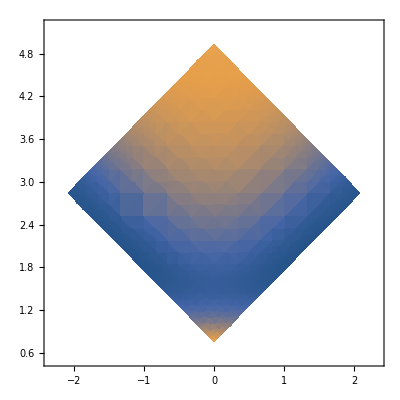

```mathematica
With[
{
rb=RegionBounds@RegionResize[H5FullR1R2Reg, Scaled@1.1],
optr=Lookup[H5OptDistances, "d1"]
},
DensityPlot[
H5FullPot[{a, s, optr, optr}],
{a, rb[[1,1]], rb[[1, 2]]},
{s, rb[[2, 1]] ,rb[[2, 2]]},
RegionFunction->
With[{rf=RegionMember[H5FullR1R2Reg]},
rf[{#, #2}]&
]
]
]
```

r1r2

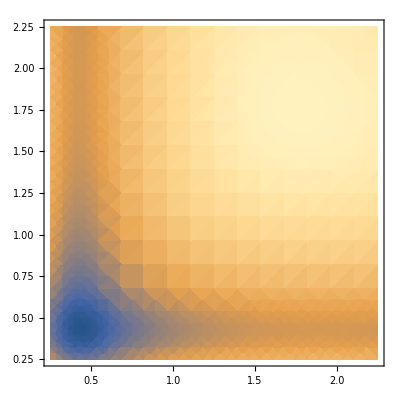

```mathematica
With[{rb=RegionBounds@H5Fullr1r2Reg},
DensityPlot[
H5FullPot[{0, 3.5506659910501295, r1, r2}],
{r1,rb[[1,1]], rb[[1, 2]]},
{r2, rb[[2, 1]] ,rb[[2, 2]]},
RegionFunction->
With[{rf=RegionMember[H5Fullr1r2Reg]},
rf[{#, #2}]&
]
]
]
```

R1r1

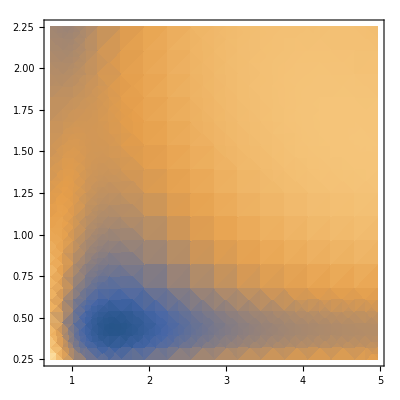

```mathematica
With[
{
rb1=RegionBounds@H5FullR1R2Reg,
rb2=RegionBounds@H5Fullr1r2Reg,
opta=1/(√2)(Subtract@@Lookup[H5OptDistances, {"R1", "R2"}]),
optr=Lookup[H5OptDistances, "d1"]
},
DensityPlot[
H5FullPot[{opta, s, r1, optr}],
{s, rb1[[2, 1]] ,rb1[[2, 2]]},
{r1,rb2[[2, 1]] ,rb2[[2, 2]]},
RegionFunction->
With[
{
rf1=RegionMember[H5FullR1R2Reg],
rf2=RegionMember[H5Fullr1r2Reg]
},
rf1[{opta, #}]&&rf2[{#2, optr}]&
]
]
]
```

R2r2

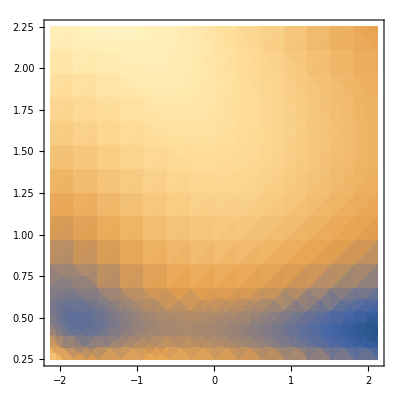

```mathematica
With[
{
rb1=RegionBounds@H5FullR1R2Reg,
rb2=RegionBounds@H5Fullr1r2Reg
},
With[{means=Mean@rb1[[2]],meanr=Mean@rb2[[1]]},
DensityPlot[
H5FullPot[{a, means, meanr, r2}],
{a, rb1[[1, 1]] ,rb1[[1, 2]]},
{r2,rb2[[1, 1]] ,rb2[[1, 2]]},
RegionFunction->
With[
{
rf1=RegionMember[H5FullR1R2Reg],
rf2=RegionMember[H5Fullr1r2Reg]
},
rf1[{#, means}]&&rf2[{#2, meanr}]&
]
]
]
]
```

### Prelim Run (just confirm results are still good)

#### KE

```mathematica
$H5DVR["KineticEnergy"]//MatrixPlot
```

-Graphics-

#### PE

##### Mat PE

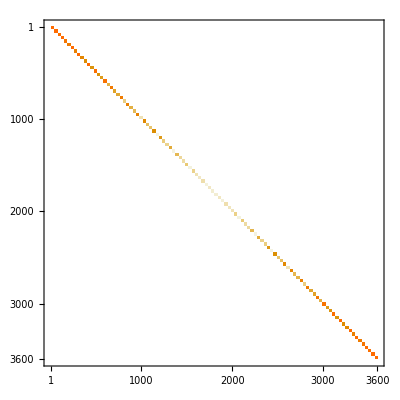

```mathematica
$H5DVR["PotentialEnergy"]//MatrixPlot
```

##### Grid PE

```mathematica
ListPlot3D[
$H5DVR["GridPotentialEnergy"]/.(1.*10^9->0),
RegionFunction->(h5RegMemFunc[{#, #2}]&),
ColorFunction->h5ColFun,
ColorFunctionScaling->False
]
```

-Graphics3D-

#### Ham

```mathematica
nwf=$H5DVR["Points"->{60, 60}, "NumberOfWavefunctions"->5];
```

```mathematica
nwf["Wavefunctions"]["Energies"]
```

{950.049,1603.41,1950.95,2519.21,2689.26}

```mathematica
#-#[[1]]&@nwf["Wavefunctions"]["Energies"]
```

{0.,653.363,1000.9,1569.16,1739.21}

##### Pruning Tests

```mathematica
ChemTools["Get", "DVR/Package/Object"]
ChemTools["Get", "DVR/Package/Defaults"]
```

Get::noopen: Cannot open /Users/Mark/Documents/Wolfram Mathematica/Applications/ChemTools/Packages/DVR/Package/Defaults.m.

$Failed

##### 120 Unpruned

```mathematica
AbsoluteTiming[
$H5DVR["Hamiltonian","Points"->{120, 120}]
]
```

{2.21247,SparseArray[<3441600>, {14400, 14400}]}

```mathematica
AbsoluteTiming[
$H5DVR["Energies","Points"->{120, 120}]
]
```

$Aborted

##### Pruning at 20% of the energy range (on the grid)

```mathematica
peVec=Diagonal@$H5DVR["PotentialEnergy","Points"->{120, 120}];
```

```mathematica
MinMax@DeleteCases[Normal@peVec, 1.*10^9]
```

{-68.4641,88773.9}

```mathematica
AbsoluteTiming[
Rest[#]-First[#]&@
$H5DVR["Energies",
"Points"->{120, 120},
 "PruningEnergy"->
Rescale[.2, {0, 1}, {-68.46412516618649,88773.86585779088}]
]
]
```

{3.70104,{532.733,866.282,1251.94,1480.7,1827.45,1878.65,2138.86,2290.64,2475.39,2654.15,2762.2,2919.12,2980.99,3009.83,3175.9,3213.33,3400.41,3509.69,3644.91,3827.36,3855.87,3948.89,4120.12,4276.36}}

```mathematica
AbsoluteTiming[
Rest[#]-First[#]&@
$H5DVR["Energies",
"Points"->{80, 80},
 "PruningEnergy"->
Rescale[.2, {0, 1}, {-68.46412516618649,88773.86585779088}]
]
]
```

{0.860435,{532.264,865.618,1250.84,1479.57,1825.77,1877.24,2136.98,2288.42,2473.16,2651.41,2759.65,2915.61,2978.02,3005.94,3172.19,3209.12,3395.78,3504.25,3639.59,3820.77,3849.37,3942.32,4112.8,4268.12}}

##### Just pruning the off-grid points

HOLY SHIT OF COURSE THIS IS JUST GERSCHGORIN’S THEOREM!

```mathematica
AbsoluteTiming[
Rest[#]-First[#]&@
$H5DVR["Energies","Points"->{60, 60}, "PruningEnergy"->Scaled[.99]]
]
```

{0.975846,{531.949,865.129,1250.02,1478.68,1824.47,1876.14,2135.52,2286.67,2471.36,2649.21,2757.57,2912.72,2975.55,3002.7,3169.02,3205.45,3391.66,3499.31,3634.73,3814.79,3843.44,3936.39,4106.,4260.31}}

#### Wavefunctions

##### Energies

```mathematica
h5Engs=$H5DVR["Energies"]
```

{929.141,1461.09,1794.27,2179.16,2407.83,2753.61,2805.28,3064.66,3215.81,3400.5,3578.35,3686.71,3841.86,3904.69,3931.84,4098.16,4134.59,4320.8,4428.45,4563.87,4743.93,4772.58,4865.53,5035.14,5189.45}

```mathematica
Rest[h5Engs]-First[h5Engs]
```

{531.949,865.129,1250.02,1478.68,1824.47,1876.14,2135.52,2286.66,2471.36,2649.21,2757.57,2912.71,2975.55,3002.7,3169.02,3205.45,3391.66,3499.31,3634.73,3814.79,3843.44,3936.39,4106.,4260.31}

##### Wavefunctions

```mathematica
h5Wfns=$H5DVR["Wavefunctions"];
```

### Average Field (Adiabatic Treatment)

#### SA Stuff

This is misnamed as it’s really an (a,s) grid...

```mathematica
saGrid=Flatten[$H5DVR["Grid"], 1];
```

```mathematica
(*$h2SAPotMins=Import["~/Documents/UW/Research/H5+/inputs/sa_pot_mins.mx"];
h2SAPotMin[{a_, s_}]:=
h2SAPotMin[{a, s}]=
If[
With[{R1R2=RotationMatrix[-π/4].{a, s}, bounds=H5FullInterpPot[[1, 3]]},
AllTrue[R1R2, bounds[[1]]<=#<bounds[[2]]&]
],
NMinimize[
Evaluate[h5PotCut[{a, s, Automatic, Automatic}][{r1, r2}]],
{r1, r2}∈Rectangle[{.1, .1}, {2, 2}]
],
$Failed
]*)
```

```mathematica
h2SAPot//Clear
h2SAPot[{a_, s_}]:=
If[
With[{R1R2=RotationMatrix[-π/4].{a, s}, bounds=H5FullInterpPot[[1, 3]]},
AllTrue[R1R2, bounds[[1]]<=#<bounds[[2]]&]
],
h5PotCutVec[{a, s, Automatic, Automatic}],
$Failed
]
```

```mathematica
h2SAEqPts=
Nearest[
saGrid->"Index",
{0,2.1364750560940324}
]
h2SAEqPt=h2SAEqPts[[1]];
```

{1759,1819}

#### H2 Wavefunctions

```mathematica
h2SAGrid=
$H2DVR["Grid",
 "PotentialOptimizationOptions"->{
"PotentialFunction"->h2SinglePot,
"OptimizedBasisSize"->25
}];
```

Get H_2 wavefunctions parametrized by (s, a)

```mathematica
(*h2SAWavefunctions=
AssociationMap[
With[{pot=h2SAPot[#]},
If[pot=!=$Failed,
$H2DVR[
"Wavefunctions",
 "PotentialEnergy"->SparseArray[Band[{1, 1}]->pot@Flatten[h2SAGrid, 1]],
"Grid"->h2SAGrid,
"ArnoldiIterations"->5000
],
$Failed
]
]&,
saGrid
];*)
```

```mathematica
(*Export["~/Documents/UW/Research/H5+/results/h2_outer_SA_wfns.mx", h2SAWavefunctions]*)
```

~/Documents/UW/Research/H5+/results/h2_outer_SA_wfns.mx

```mathematica
h2SAWavefunctions=Import@"~/Documents/UW/Research/H5+/results/h2_outer_SA_wfns.mx";
```

```mathematica
h2SAValidCoords=
Complement[
Range[Length@h2SAWavefunctions],
Pick[Range[Length@h2SAWavefunctions], Values[h2SAWavefunctions], $Failed]
];
```

```mathematica
h2SAInterestingWavefunctions=
Select[h2SAWavefunctions, #=!=$Failed&];
```

#### H2 Wavefunction Analysis

```mathematica
h2SAInterestingWavefunctions//Length
```

1740

```mathematica
h2Adiabats=
KeyValueMap[
If[#2===$Failed, 
Join[ConstantArray[#, 6], ConstantArray[{10.^9}, 6], 2], Join[ConstantArray[#, 6], List/@#2[[1, ;;6]], 2]]&,
h2SAWavefunctions
]//Transpose;
```

```mathematica
h2AdiabatInterps=Interpolation/@h2Adiabats;
```

Plot adiabats

```mathematica
h2Adiabats[[{2}]]
```

{{{-2.28395,0.722261,1.×10^9},{-2.28395,0.799684,1.×10^9},{-2.28395,0.877106,1.×10^9},3594,{2.28395,5.13533,1.×10^9},{2.28395,5.21275,1.×10^9},{2.28395,5.29017,1.×10^9}}}
 |  |  |  |

```mathematica
MinimalBy[h2Adiabats[[2]], Last, 2]
```

{{0.3484,1.57391,5871.65},{-0.3484,1.57391,5871.65}}

```mathematica
MinimalBy[h2Adiabats[[3]], Last, 2]
```

{{0.270978,1.57391,6003.91},{-0.270978,1.57391,6003.91}}

```mathematica
h2Adiabats[[{2}]]//ListPlot3D[Map[Select[#[[-1]]<10^8&], #], PlotRange->{{-1, 1}, {1, 3}, {0, 20000}+2000*{1, 1}}, InterpolationOrder->2, ClippingStyle->None, Boxed->False, AxesEdge->{{1,-1},{1,-1},{1,1}},
AxesLabel->Thread@Style[{"a (Å)", "s (Å)", "V (Å)"}, Black],
AxesStyle->Black
]&
```

-Graphics3D-

Plot differences

```mathematica
diffAds=
Module[
{
gps=Pick[h2Adiabats[[1, All, ;;2]], UnitStep[Abs[h2Adiabats[[1, All, 3]]]-10^8], 0],
ad0=Pick[#, UnitStep[Abs[#]-10^8], 0]&@h2Adiabats[[1, All, 3]],
ad1=Pick[#, UnitStep[Abs[#]-10^8], 0]&@h2Adiabats[[2, All, 3]],
ad2=Pick[#, UnitStep[Abs[#]-10^8], 0]&@h2Adiabats[[3, All, 3]],
mad0,
mad1,
mad2
},
mad0=Min@ad0;
mad1=Min@ad1;
mad2=Min@ad2;
ad0-=mad0;
ad1-=mad1;
ad2-=mad2;
Join[gps, List/@#, 2]&/@{ad1-ad0, ad2-ad0}
];
```

```mathematica
rf2=RegionMember@RegionResize[h5Reg, Scaled[.85]];
```

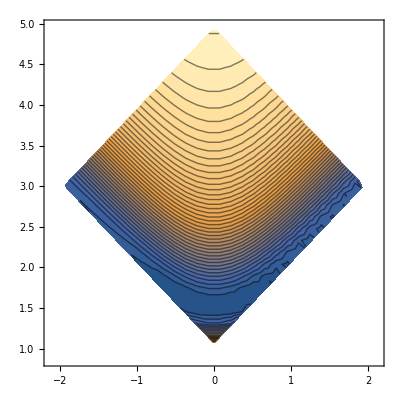

```mathematica
ListContourPlot[h2Adiabats[[1]],
 RegionFunction->({x, y}↦rf2[{x, y}]), Contours->50,
ColorFunction->"M10DefaultDensityGradient",
PlotRange->CoordinateBounds@Select[h2Adiabats[[1]], Abs[#[[3]]]<10^8&],
ContourLabels->None
]
```

```mathematica
rf3=RegionMember@RegionIntersection[RegionResize[h5Reg, Scaled[.85]], Rectangle[{-1, 1.4}, {1, 2}]];
```

```mathematica
ListPointPlot3D[h2Adiabats[[1]],
 RegionFunction->({x, y}↦rf3[{x, y}]),
ColorFunction->"M10DefaultDensityGradient",
PlotRange->CoordinateBounds@Select[h2Adiabats[[1]], rf3@#[[;;2]]&]
]
```

-Graphics3D-

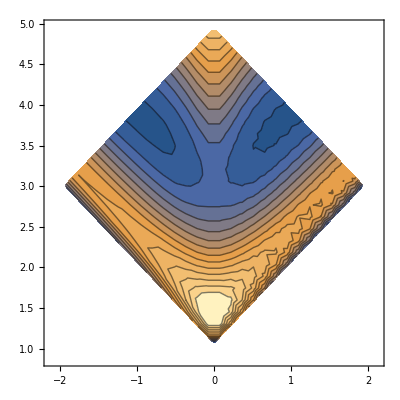

```mathematica
ListContourPlot[diffAds[[1]],
 RegionFunction->({x, y}↦rf2[{x, y}]), Contours->25,
ColorFunction->"M10DefaultDensityGradient",
ContourLabels->None
]
```

```mathematica
216/2
```

108

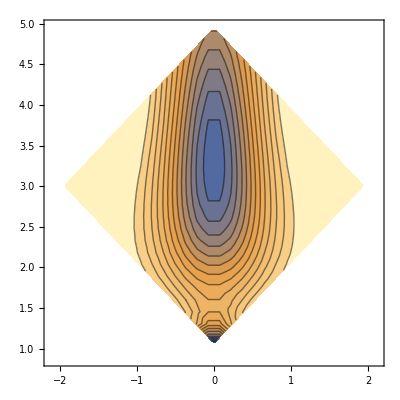

```mathematica
ListContourPlot[diffAds[[2]],
 RegionFunction->({x, y}↦rf2[{x, y}]), 
Contours->25,
ColorFunction->"M10DefaultDensityGradient",
ContourLabels->None
]
```

```mathematica
h2SAInterestingWavefunctions[[All, 1]]
```

Plot (some of) these suckers

```mathematica
Nearest[
Keys[h2SAInterestingWavefunctions]->"Index",
{0,2.1364750560940324}
]
```

{166,192}

```mathematica
h2SAInterestingWavefunctions[[{195}, 2, 2]]//MinMax
```

{-0.209289,0.206249}

```mathematica
Block[{(*ListDensityPlot=Echo*)},
KeyValueMap[
$H2DVR[
 "Wavefunctions"->#2,
"ShowPotential"->False,
"Grid"->Reverse[Reverse[h2SAGrid], {2}],
"PlotDisplayMode"->List,
"WavefunctionSelection"->5,
"PlotMode"->"Density",
"WavefunctionClipping"->None,
"WavefunctionRescaling"->None,
"WavefunctionScaling"->None,
"WavefunctionShifting"->None,
"ColorFunction"->"Rainbow",
"ColorFunctionScaling"->True,
FrameTicks->False(*,
PlotLabel->StringRiffle[#, ", "]*)
]&,
h2SAInterestingWavefunctions[[{1, 166, 391}]]
]
]//Iconize[#, "outer_wfns"]&
```

```mathematica
//ByteCount
```

#### H2 Distances

```mathematica
(*h2AveragedH2s=
If[#=!=$Failed,
$H2DVR[
"ExpectationValues",
#&,
"Grid"->h2SAGrid,
"Wavefunctions"->#,
"WavefunctionSelection"->50
],
$Failed
]&/@h2SAWavefunctions;*)
```

```mathematica
h2AveragedH2s=
Import["~/Documents/UW/Research/H5+/results/SA_grid_h2_dists.mx"];
```

```mathematica
(*Export["~/Documents/UW/Research/H5+/SA_grid_h2_dists.mx", h2AveragedH2s]*)
```

~/Documents/UW/Research/H5+/SA_grid_h2_dists.mx

```mathematica
h2SAH2Dists=
Range[
Length@h2AveragedH2s[[h2SAEqPt]]]->
Thread[
Subtract@@@h2AveragedH2s[[h2SAEqPt, All, {1,2}]]//Thread
]//Thread//Association//SortBy[Abs@*Apply[Subtract]];
```

```mathematica
h2SAH2DistOrdering=
With[{n=Length@h2AveragedH2s[[h2SAEqPt]]},
Range[n]->
Thread[
With[{r=#},
Ordering@h2AveragedH2s[[h2SAEqPt, All, r]]->Range[n]//Thread//SortBy[#, First]&//Values
]&/@Range[2]
]//Thread//Association//SortBy[Abs@*Apply[Subtract]]
];
```

```mathematica
h2SAH2MeanDistOrdering=
With[{n=Length@h2AveragedH2s[[h2SAEqPt]]},
Range[n]->
Thread[
With[{r=#},
Ordering@
Mean@Select[h2AveragedH2s, #=!=$Failed&][[All, All, r]]->Range[n]//Thread//SortBy[#, First]&//Values
]&/@Range[2]
]//Thread//Association//SortBy[Abs@*Apply[Subtract]]
];
```

#### Coupling Adiabats

We’ll try coupling the first two excited states:

H=H^(1,0)+H^(0,1)+H^((0,1)|(1, 0))
(H^(1,0))_(ij, i'j')=T_(ij, i'j)+(E^(1, 0))_(ij, i'j')δ_(ij, i'j')
(H^(0, 1))_(ij, i'j')=T_(ij, i'j')+(E^(0, 1))_(ij, i'j')δ_(ij, i'j')

The last term is slightly odd as we have

(H^((0,1)|(1, 0)))_(ij, i'j')=(H_2^(0, 1))_ij  (H_2^(1, 0))_i'j'(j' T_s j δ_ii'+i T_a i' δ_jj')

which means that we need to actually be a little bit careful about the overlap ordering. We need to compute overlaps for each pair of gridpoints (a_i, s_j) and (a_i', s_j') then project this up to the higher dimensional case by...?

##### Overlaps

```mathematica
h2OverlapMatrix[i_, j_]:=
Module[
{
wooplen=Length@h2SAInterestingWavefunctions[[1, 2, 1]],
woopart1,
woopart2,
flooplen=Length@h2SAWavefunctions
},
woopart1=
Map[
If[#===$Failed, ConstantArray[0., wooplen], #[[2, i]]]&,
Values@h2SAWavefunctions
];
woopart2=
Map[
If[#===$Failed, ConstantArray[0., wooplen], #[[2, j]]]&,
Values@h2SAWavefunctions
];
h2OverlapMatrix[i, j]=
SparseArray@$H2DVR["OperatorMatrix",
(#2&),
"Wavefunctions"->{ConstantArray[0, 2*flooplen], Join[woopart1,woopart2]}
]
]
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/h5AdiabatOverlapMatrix_1_2.mx",
h2OverlapMatrix[1, 2]
]
```

~/Documents/UW/Research/H5+/results/h5AdiabatOverlapMatrix_1_2.mx

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/h5AdiabatOverlapMatrix_2_3.mx",
h2OverlapMatrix[2, 3]
]
```

~/Documents/UW/Research/H5+/results/h5AdiabatOverlapMatrix_2_3.mx

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/h5AdiabatOverlapMatrix_1_3.mx",
h2OverlapMatrix[1, 3]
]
```

~/Documents/UW/Research/H5+/results/h5AdiabatOverlapMatrix_1_3.mx

##### Coupled KE

```mathematica
h2CoupledKineticEnergy[i_, j_]:=
Module[
{
woop=h2OverlapMatrix[i, j],
waap=$H5DVR["KineticEnergy"],
klap
},
klap=
Join[
Join[waap,waap, 2],
Join[waap,waap, 2]
];
woop*klap
];
```

```mathematica
ke=h2CoupledKineticEnergy[1, 2];
```

```mathematica
ke//MatrixPlot
```

-Graphics-

##### Pots

```mathematica
h2AveragedEnergy[i_]:=
Map[
If[#===$Failed, 10^9//N, #[[1, i]]]&,
Values@h2SAWavefunctions
];
```

##### Hammer

```mathematica
h5AdiabatCoupledHam[i_, j_]:=
Module[
{
h1=
$H5DVR["Hamiltonian",
 "PotentialEnergy"->SparseArray[Band[{1, 1}]->h2AveragedEnergy[i]]
],
h2=
$H5DVR["Hamiltonian",
 "PotentialEnergy"->SparseArray[Band[{1, 1}]->h2AveragedEnergy[j]]
],
kt=h2CoupledKineticEnergy[i, j]
},
SparseArray[Band[{1, 1}]->Join[h2AveragedEnergy[i], h2AveragedEnergy[j]]]+kt
]
```

```mathematica
Export["~/Documents/UW/Research/H5+/results/h5AdiabatCoupledHam_1_2.mx", h5AdiabatCoupledHam[1, 2]]
```

~/Documents/UW/Research/H5+/results/h5AdiabatCoupledHam_1_2.mx

```mathematica
schloop=h5AdiabatCoupledHam[1, 2];
```

```mathematica
schloop//MatrixPlot
```

-Graphics-

```mathematica
$H5DVR["Energies",
"KineticEnergy"->schloop,
"PotentialEnergy"->N@SparseArray[{}, Dimensions@schloop],
"NumberOfWavefunctions"->100,
"ArnoldiIterations"->5000
]//AbsoluteTiming
```

{27.4632,{3657.41,4098.7,4424.28,4765.05,5007.75,5303.18,5387.49,5592.46,5740.16,5928.91,6089.09,6221.06,6307.2,6401.05,6432.12,6583.01,6611.8,6762.65,6852.76,6987.35,7040.25,7121.14,7131.61,7225.9,7326.06,7445.53,7495.26,7662.4,7747.1,7771.58,7781.86,7913.2,7930.59,8085.57,8150.82,8220.96,8275.04,8355.35,8395.64,8556.95,8592.84,8601.15,8708.97,8715.11,8792.49,8890.83,8923.68,8961.36,8981.55,9036.91,9102.8,9155.35,9184.54,9208.51,9310.47,9328.57,9411.28,9465.41,9490.27,9544.15,9598.01,9644.53,9703.2,9727.37,9745.5,9816.54,9843.44,9883.76,9886.25,9995.33,9999.99,10061.2,10154.5,10155.8,10182.9,10217.5,10274.8,10376.9,10414.7,10417.4,10451.,10476.6,10580.3,10592.9,10644.9,10649.7,10679.,10713.9,10816.9,10911.8,10949.2,10993.7,11029.,11082.4,11108.6,11126.8,11183.3,11198.6,11299.9,11366.2}}

```mathematica
%232[[2]]-%232[[2, 1]]
```

{0.,441.295,766.866,1107.64,1350.34,1645.77,1730.08,1935.05,2082.75,2271.5,2431.68,2563.65,2649.79,2743.64,2774.72,2925.6,2954.39,3105.24,3195.35,3329.94,3382.84,3463.73,3474.2,3568.49,3668.65,3788.12,3837.85,4004.99,4089.69,4114.17,4124.45,4255.8,4273.18,4428.16,4493.41,4563.55,4617.63,4697.94,4738.23,4899.54,4935.43,4943.74,5051.56,5057.7,5135.09,5233.42,5266.27,5303.95,5324.14,5379.5,5445.39,5497.95,5527.13,5551.1,5653.06,5671.16,5753.87,5808.,5832.86,5886.74,5940.6,5987.12,6045.79,6069.96,6088.09,6159.13,6186.04,6226.35,6228.84,6337.92,6342.58,6403.79,6497.08,6498.44,6525.51,6560.13,6617.4,6719.48,6757.26,6760.04,6793.55,6819.19,6922.88,6935.47,6987.48,6992.33,7021.63,7056.53,7159.46,7254.35,7291.83,7336.28,7371.56,7425.,7451.22,7469.37,7525.92,7541.15,7642.45,7708.76}

```mathematica
schloop2=h5AdiabatCoupledHam[2, 3];
```

```mathematica
$H5DVR["Energies",
"KineticEnergy"->schloop2,
"PotentialEnergy"->N@SparseArray[{}, Dimensions@schloop2],
"NumberOfWavefunctions"->100,
"ArnoldiIterations"->5000
]//AbsoluteTiming
```

{31.6139,{6944.02,6970.83,7408.39,7429.01,7732.49,7752.56,8082.05,8098.82,8321.15,8338.67,8619.01,8629.14,8723.05,8740.04,8925.23,8939.1,9075.28,9083.62,9259.24,9268.,9421.77,9426.09,9560.85,9565.56,9677.62,9678.12,9752.38,9766.27,9822.79,9823.6,9889.46,9892.24,10008.3,10012.3,10097.2,10098.8,10220.8,10222.1,10344.6,10348.5,10463.9,10466.4,10571.,10578.4,10635.,10647.4,10737.2,10739.8,10858.3,10860.4,11018.5,11025.7,11161.,11163.9,11197.6,11214.2,11289.6,11293.1,11346.4,11354.4,11522.,11527.1,11633.4,11633.9,11734.8,11748.,11826.7,11837.6,11938.1,11941.4,12064.1,12066.5,12175.2,12184.1,12224.7,12235.9,12298.6,12303.7,12347.,12354.5,12468.6,12469.1,12526.4,12536.5,12582.3,12586.7,12641.3,12644.8,12779.8,12783.9,12847.6,12847.8,12916.3,12916.9,12977.9,12978.8,13057.4,13061.1,13150.3,13155.1}}

```mathematica
%235[[2]]-%235[[2, 1]]
```

{0.,26.8045,464.369,484.983,788.464,808.543,1138.03,1154.8,1377.13,1394.65,1674.99,1685.12,1779.02,1796.02,1981.21,1995.08,2131.25,2139.6,2315.21,2323.98,2477.75,2482.07,2616.83,2621.54,2733.6,2734.1,2808.36,2822.25,2878.77,2879.58,2945.44,2948.22,3064.3,3068.32,3153.17,3154.81,3276.75,3278.05,3400.56,3404.44,3519.84,3522.35,3626.99,3634.4,3691.01,3703.42,3793.16,3795.74,3914.32,3916.4,4074.52,4081.63,4217.02,4219.85,4253.61,4270.15,4345.6,4349.1,4402.35,4410.38,4577.97,4583.03,4689.34,4689.84,4790.82,4803.98,4882.67,4893.53,4994.04,4997.42,5120.07,5122.53,5231.15,5240.08,5280.71,5291.84,5354.62,5359.65,5402.99,5410.47,5524.58,5525.03,5582.41,5592.43,5638.23,5642.7,5697.23,5700.8,5835.77,5839.84,5903.54,5903.78,5972.24,5972.85,6033.83,6034.82,6113.36,6117.04,6206.29,6211.05}

#### SA Wavefunctions

We have ~625 wavefunctions to work off per GP

Extract the i^th energy eigenvalue for each gridpoint in (s, a)

```mathematica
h2AveragedEnergy[i_]:=
Map[
If[#===$Failed, 10^9//N, #[[1, i]]]&,
Values@h2SAWavefunctions
];
```

```mathematica
h5Wfns2Grid=
$H5DVR["Grid",
"Points"->{30, 30}
];
```

```mathematica
(*$h5WfnsCache//Clear*)
If[!AssociationQ@$h5WfnsCache,$h5WfnsCache=<||>];
h5Wfns2//Clear
ih5Wfns2[i_, n_]:=
$H5DVR["Wavefunctions",
"Points"->{30, 30},
 "PotentialEnergy"->SparseArray[Band[{1, 1}]->h2AveragedEnergy[i]],
"NumberOfWavefunctions"->n,
"PruningEnergy"->Scaled[.99]
];
h5Wfns2[i_, n:_Integer?Positive:25]:=
If[KeyMemberQ[$h5WfnsCache, i],
With[{kn=Length@$h5WfnsCache[i][[1]]},
If[kn<n,
$h5WfnsCache[i]=
ih5Wfns2[i, n],
$h5WfnsCache[i][[All, ;;n]]
]
],
$h5WfnsCache[i]=
ih5Wfns2[i, n]
]
```

```mathematica
(*$h5Wfns2=h5Wfns2~Array~25;*)
```

```mathematica
(*Export["~/Documents/UW/Research/H5+/sa_wfns_per_h2.mx", $h5Wfns2]*)
```

~/Documents/UW/Research/H5+/sa_wfns_per_h2.mx

#### Averaged Frequencies

```mathematica
h5Freqs2[i_, n_]:=
h5Wfns2[i, n][[1]]-h5Wfns2[i, n][[1, 1]]//Rest
h5Freqs2[i_]:=
h5Wfns2[i][[1]]-h5Wfns2[i][[1, 1]]//Rest
```

```mathematica
h5Freqs2/@Range[25]//TableForm
```

445.017 | 730.67 | 1120.92 | 1294.48 | 1630.75 | 1730.23 | 1937.32 | 1991.81 | 2314.76 | 2350.17 | 2646.94 | 2659.17 | 2725.71 | 2889.61 | 2936.46 | 3002.57 | 3095.73 | 3224.57 | 3247.05 | 3417.5 | 3489.02 | 3628.19 | 3632.03 | 4048.34
404.963 | 692.819 | 1058.64 | 1237.82 | 1562.63 | 1676.93 | 1867.29 | 1915.54 | 2212.95 | 2251.01 | 2536.02 | 2553.44 | 2658.74 | 2785.31 | 2820.2 | 2937.9 | 3036.96 | 3109.46 | 3153. | 3388.83 | 3410.17 | 3515.22 | 3521.5 | 3962.74
462.195 | 745.001 | 1145.48 | 1314.71 | 1659.41 | 1746.51 | 1967.66 | 2026.35 | 2363.24 | 2398.46 | 2704.04 | 2705.99 | 2759.7 | 2942.12 | 3004.87 | 3034.84 | 3109.58 | 3292.24 | 3302.68 | 3426.55 | 3514.05 | 3696.65 | 3698.36 | 4063.73
347.42 | 637.207 | 968.5 | 1155.46 | 1461.05 | 1592.93 | 1785.72 | 1807.73 | 2067.39 | 2110.87 | 2374.88 | 2395.03 | 2570.55 | 2625.07 | 2655.35 | 2847.8 | 2929.8 | 2943.67 | 3040.2 | 3287.77 | 3333.65 | 3372.55 | 3385.75 | 3811.59
427.574 | 711.925 | 1090.05 | 1263.52 | 1598.99 | 1696.25 | 1898.58 | 1956.83 | 2268.97 | 2306.45 | 2603.53 | 2616.54 | 2684.78 | 2853.34 | 2895.57 | 2971.1 | 3058.43 | 3184.78 | 3212.38 | 3393.63 | 3441.55 | 3589.72 | 3592.36 | 3996.52
488.6 | 767.527 | 1184.29 | 1346.28 | 1703.55 | 1771.45 | 2017.06 | 2079.44 | 2436.17 | 2471.09 | 2745.79 | 2791.09 | 2835.5 | 3004.11 | 3076.52 | 3104.83 | 3150.85 | 3373.12 | 3389.38 | 3464.31 | 3553.43 | 3797.49 | 3798.3 | 4079.45
256.254 | 546.425 | 822.816 | 1020.43 | 1289.68 | 1430.25 | 1635.34 | 1698.89 | 1843.08 | 1896.45 | 2115.64 | 2141.59 | 2361.12 | 2375.44 | 2458.67 | 2643.67 | 2678.82 | 2779.32 | 2896.87 | 3052.74 | 3088.08 | 3177.88 | 3372.35 | 3550.15
371.007 | 657.933 | 1001.65 | 1183.67 | 1500.42 | 1618.7 | 1806.64 | 1850.67 | 2124.8 | 2167.21 | 2444.79 | 2463.84 | 2592.96 | 2699.25 | 2729.6 | 2885.78 | 2965.52 | 3020.21 | 3081.7 | 3328.67 | 3362.51 | 3431.07 | 3434.36 | 3877.09
456.531 | 737.132 | 1131.68 | 1297.13 | 1646.7 | 1720.37 | 1945.66 | 2011.58 | 2343.69 | 2380.35 | 2680.08 | 2691.92 | 2739.99 | 2934.12 | 2996.14 | 3012.96 | 3090.32 | 3284. | 3296.81 | 3409.81 | 3481.23 | 3690.79 | 3691.73 | 4011.73
534.043 | 805.036 | 1250.16 | 1397.1 | 1775.86 | 1811.77 | 2101.33 | 2166.18 | 2549.94 | 2584.68 | 2796.5 | 2913.54 | 2967.24 | 3079.02 | 3111.32 | 3253.32 | 3264.25 | 3435.74 | 3523.13 | 3583.81 | 3629.35 | 3947.26 | 3949.94 | 4104.02
131.356 | 435.829 | 628.585 | 847.279 | 1053.96 | 1202.63 | 1396.61 | 1513.88 | 1645.99 | 1714.22 | 1797.85 | 1840.93 | 2028.95 | 2055.31 | 2315.9 | 2323.38 | 2355.17 | 2644.32 | 2698.3 | 2722.46 | 2823.25 | 2988.45 | 3207.87 | 3210.07
280.61 | 567.68 | 857.38 | 1051.24 | 1332.28 | 1468.08 | 1680.95 | 1704.59 | 1896.48 | 1951.43 | 2186.37 | 2210.77 | 2436.8 | 2440.28 | 2485.88 | 2711.31 | 2754.53 | 2803.74 | 2921.7 | 3120.83 | 3160.86 | 3210.96 | 3363.69 | 3630.06
401.949 | 685.853 | 1045.79 | 1220.39 | 1552.11 | 1646.61 | 1843.59 | 1907.09 | 2201.1 | 2241.89 | 2536.13 | 2550.86 | 2625.6 | 2794.25 | 2829.94 | 2926.63 | 3004.33 | 3120.97 | 3158.04 | 3370.6 | 3371.72 | 3528.45 | 3529.86 | 3915.15
503.969 | 776.387 | 1196.51 | 1344.9 | 1716.96 | 1752.23 | 2019.22 | 2090.32 | 2443.98 | 2479.88 | 2726.18 | 2803.01 | 2846.73 | 3018.03 | 3049.62 | 3123.65 | 3164.75 | 3378.63 | 3404.98 | 3471.27 | 3532.88 | 3823.34 | 3825.21 | 4011.51
593.878 | 850.506 | 1332.58 | 1454.02 | 1859.73 | 1860.31 | 2193.34 | 2257.79 | 2646.5 | 2680.89 | 2841.12 | 2994.83 | 3062.56 | 3127.58 | 3146.71 | 3340.61 | 3346.13 | 3479.48 | 3595.39 | 3678.53 | 3703.22 | 4036.84 | 4052.82 | 4114.41
58.0616 | 413.591 | 530.426 | 799.214 | 950.815 | 1134.5 | 1304.81 | 1427.94 | 1574.34 | 1687.43 | 1764.88 | 1829.19 | 1933.13 | 1962.81 | 2224.23 | 2239.05 | 2341.3 | 2594.13 | 2613.74 | 2669.01 | 2821.16 | 2978.23 | 3093.05 | 3094.85
151.759 | 448.976 | 658.798 | 873.755 | 1095.62 | 1242.48 | 1446.36 | 1564.4 | 1698.59 | 1705.23 | 1862.81 | 1904.48 | 2103.86 | 2126.61 | 2330.31 | 2397.16 | 2422.15 | 2663.15 | 2740.18 | 2797.75 | 2860.19 | 3005.91 | 3286.81 | 3288.7
315.861 | 599.709 | 906.527 | 1094.38 | 1391.41 | 1513.1 | 1712.78 | 1743.12 | 1973.72 | 2027.25 | 2282.01 | 2304.5 | 2487.72 | 2538.91 | 2567.52 | 2792.16 | 2839.39 | 2857.63 | 2966.13 | 3193.12 | 3261.93 | 3279.96 | 3360.88 | 3724.96
462.351 | 733.439 | 1117.54 | 1269.05 | 1618.38 | 1662.9 | 1890.5 | 1968.89 | 2256.76 | 2297.86 | 2581.95 | 2592.04 | 2654.84 | 2835.56 | 2872.91 | 2956.58 | 3026.16 | 3166.47 | 3203.39 | 3378.65 | 3396.42 | 3581.66 | 3582.95 | 3881.72
554.81 | 804.601 | 1234.07 | 1350.83 | 1746.29 | 1749.09 | 2034.82 | 2109.63 | 2430.26 | 2464.35 | 2690.26 | 2758.18 | 2800.18 | 2982.26 | 3021.38 | 3056.83 | 3126.23 | 3337.34 | 3337.96 | 3429.04 | 3474.78 | 3765.69 | 3768.89 | 3931.19
619.608 | 865.578 | 1347.72 | 1447.89 | 1835.13 | 1848.02 | 2151.76 | 2220.27 | 2571.38 | 2608.07 | 2789.84 | 2912.82 | 2969.07 | 3081.53 | 3115.3 | 3240.86 | 3253.45 | 3425.45 | 3505.24 | 3583.2 | 3624.49 | 3935.3 | 3946.12 | 4029.3
56.6618 | 460.591 | 578. | 888.393 | 1044.34 | 1248.48 | 1440.83 | 1583.59 | 1719.01 | 1891.37 | 1921.26 | 1944.74 | 2183.63 | 2196.27 | 2445.37 | 2479.68 | 2490.67 | 2760.34 | 2852.94 | 2873.71 | 2957.56 | 3094.27 | 3373.21 | 3373.98
68.7169 | 422.61 | 558.919 | 826.133 | 995.33 | 1172.84 | 1362.63 | 1487.51 | 1631.38 | 1760.15 | 1806.31 | 1829.23 | 2021.49 | 2044.49 | 2313.04 | 2320.34 | 2345.71 | 2652.04 | 2693.72 | 2704.12 | 2827.83 | 2986.94 | 3186.76 | 3188.54
203.934 | 480.592 | 724.922 | 927.282 | 1174.25 | 1311.72 | 1531.48 | 1597.86 | 1710.14 | 1787.4 | 1973.23 | 2010.62 | 2222.57 | 2241.71 | 2363.24 | 2512.66 | 2539.55 | 2695.59 | 2795.82 | 2916.28 | 2954.18 | 3057.6 | 3397. | 3412.4
372.399 | 618.622 | 936.863 | 1097.38 | 1399.84 | 1485.72 | 1686.63 | 1740.59 | 1930.08 | 1992.05 | 2197.96 | 2225.54 | 2439.98 | 2440.55 | 2490.37 | 2723.21 | 2766.93 | 2801.58 | 2919.04 | 3123.3 | 3181.62 | 3213.36 | 3328.03 | 3637.82

Using older potential on smaller grid:

484.471 | 825.535 | 1178.67 | 1364.78 | 1731.79 | 1752.94 | 2012.32 | 2219.98 | 2320.44 | 2542.37 | 2656.15 | 2762.63 | 2822.21 | 2887.09 | 3019.15 | 3051.64 | 3330.75 | 3336.57 | 3635.7 | 3718.51 | 3757.33 | 3781.97 | 4002.55 | 4156.46
434.538 | 772.099 | 1098.72 | 1312.65 | 1648.75 | 1663.96 | 1927.77 | 2101.61 | 2207.74 | 2433.77 | 2525.79 | 2645.92 | 2744.28 | 2777.03 | 2877.43 | 2932.42 | 3183.14 | 3189.87 | 3535.11 | 3582.72 | 3613.84 | 3681.71 | 3921.27 | 4039.93
504.302 | 842.772 | 1206.62 | 1380.09 | 1754.71 | 1789.54 | 2040.85 | 2264.24 | 2361.91 | 2585.18 | 2705.9 | 2812.22 | 2844.89 | 2924.61 | 3086.52 | 3109.13 | 3400.32 | 3405.08 | 3662.54 | 3757.2 | 3824.9 | 3826.08 | 4034.4 | 4190.12
358.311 | 685.374 | 975.108 | 1216.22 | 1486.75 | 1570.57 | 1803.62 | 1912.47 | 2036.71 | 2244.52 | 2318.01 | 2475.28 | 2579.24 | 2618.91 | 2682.17 | 2785.27 | 2958.96 | 2970.78 | 3354.29 | 3359.87 | 3417.18 | 3540.05 | 3795.59 | 3851.08
466.103 | 800.211 | 1140.93 | 1338.47 | 1690.76 | 1701.08 | 1966.03 | 2163.18 | 2262.94 | 2495.57 | 2592.52 | 2708.89 | 2773.46 | 2828.8 | 2958.08 | 2990.81 | 3268.14 | 3273.08 | 3575.3 | 3651.72 | 3694.49 | 3716.84 | 3963.76 | 4087.89
525.762 | 862.243 | 1238.67 | 1397.85 | 1783.83 | 1832.6 | 2074.3 | 2316.11 | 2410.94 | 2634.13 | 2761.8 | 2852.95 | 2891.57 | 2970.35 | 3168.75 | 3184.4 | 3484.75 | 3488.71 | 3693.32 | 3785.65 | 3897.09 | 3907.96 | 4074.8 | 4228.85
235.113 | 543.907 | 779.464 | 1031.81 | 1235.4 | 1409.94 | 1617.81 | 1656.4 | 1797.93 | 1928.08 | 2008.73 | 2187.89 | 2255.91 | 2410.75 | 2476.44 | 2553.54 | 2651.52 | 2712.66 | 3018.27 | 3024.26 | 3194.47 | 3355.01 | 3539.19 | 3539.85
396.851 | 720.415 | 1025.21 | 1254.68 | 1547.53 | 1596.64 | 1839.87 | 1983.79 | 2097.89 | 2321.73 | 2395.2 | 2545.01 | 2653.45 | 2655.76 | 2757.29 | 2823.69 | 3048.45 | 3054.58 | 3422.07 | 3447.73 | 3482.01 | 3560.56 | 3846.83 | 3912.76
503.728 | 834.281 | 1192.92 | 1367.89 | 1728.35 | 1765.98 | 2015.24 | 2238.83 | 2330.29 | 2568.5 | 2669.64 | 2779.16 | 2818.6 | 2886.7 | 3060.51 | 3079.24 | 3374.44 | 3378.35 | 3621.33 | 3703.12 | 3797.6 | 3799.09 | 4018.03 | 4143.78
553.241 | 887.1 | 1279.75 | 1420.05 | 1822.02 | 1886.34 | 2114.89 | 2378.17 | 2468.73 | 2691.93 | 2820.65 | 2879.24 | 2968.61 | 3028.98 | 3266.8 | 3277.92 | 3585.1 | 3588.74 | 3724.49 | 3801.62 | 3985.61 | 4007.93 | 4133.14 | 4265.76
115.991 | 439.45 | 610.104 | 870.138 | 1028.54 | 1239.11 | 1380.44 | 1528.94 | 1670.97 | 1731.89 | 1798.14 | 1934.4 | 2010.78 | 2228.44 | 2313.79 | 2361.31 | 2474.85 | 2616.92 | 2748.67 | 2758.88 | 3063.37 | 3227.25 | 3259.89 | 3293.39
274.767 | 577.495 | 829.676 | 1078.79 | 1295.84 | 1454.03 | 1667.73 | 1689.01 | 1844. | 2008.93 | 2083.35 | 2269.03 | 2336.36 | 2458. | 2522.89 | 2609.75 | 2726.88 | 2750.32 | 3105.34 | 3110.62 | 3233.02 | 3362.15 | 3619.04 | 3622.4
460.627 | 774.34 | 1105.92 | 1304.04 | 1636.82 | 1641.92 | 1906.83 | 2090.17 | 2188.96 | 2430.98 | 2501.94 | 2641.05 | 2714.59 | 2741.16 | 2875.94 | 2904.57 | 3178.88 | 3182.22 | 3497.74 | 3555.37 | 3605.81 | 3624.12 | 3917.86 | 3995.64
548.299 | 877.286 | 1254.59 | 1400.62 | 1773.14 | 1831.61 | 2064.03 | 2300.75 | 2378.36 | 2622.62 | 2709.72 | 2806.65 | 2866.47 | 2922.75 | 3120.14 | 3136.1 | 3437.44 | 3441.41 | 3641.05 | 3696.02 | 3862.53 | 3864.69 | 4078.59 | 4158.87
568.41 | 895.656 | 1291.89 | 1421.57 | 1830.24 | 1897.08 | 2125.5 | 2392.79 | 2475.44 | 2707.92 | 2824.64 | 2867.12 | 2991.27 | 3041.79 | 3294.11 | 3303.94 | 3608.87 | 3611.32 | 3702.14 | 3755.25 | 4014.88 | 4029.71 | 4161.16 | 4235.4
77.5709 | 442.756 | 578.434 | 866.77 | 1004.75 | 1241.14 | 1366.2 | 1542.86 | 1668.86 | 1779.13 | 1835.75 | 1940.98 | 2020.35 | 2235.85 | 2319.84 | 2389.98 | 2475.26 | 2660.7 | 2746.45 | 2751.94 | 3095.3 | 3237.48 | 3252.17 | 3325.96
154.448 | 454.977 | 656.203 | 905.938 | 1083.53 | 1286.31 | 1445.6 | 1575.87 | 1696.08 | 1746.03 | 1844.53 | 2012.49 | 2081.02 | 2295.12 | 2383.34 | 2385. | 2526.99 | 2615.47 | 2823.7 | 2835.82 | 3091.91 | 3244.48 | 3344.22 | 3350.46
369.321 | 650.477 | 941.067 | 1159.75 | 1420.42 | 1501.81 | 1718.21 | 1826.06 | 1954.08 | 2155.62 | 2217.3 | 2409.05 | 2471.93 | 2532.3 | 2636.36 | 2678.31 | 2872.71 | 2873.18 | 3261.53 | 3262.52 | 3327.47 | 3408.54 | 3732.04 | 3752.72
501.099 | 810.893 | 1134.56 | 1316.43 | 1628.04 | 1641.49 | 1901.6 | 2045.56 | 2142.03 | 2359.13 | 2403.9 | 2561.62 | 2634.55 | 2650.93 | 2801.87 | 2820.29 | 3080.88 | 3087.19 | 3402.24 | 3434.03 | 3508.65 | 3529.74 | 3878.62 | 3895.33
551.62 | 873.123 | 1231.36 | 1374.16 | 1728.83 | 1769.77 | 2021.92 | 2219.6 | 2297.17 | 2546.19 | 2606.46 | 2738.33 | 2799.65 | 2836.53 | 2999.81 | 3025.46 | 3307.05 | 3312.93 | 3578.88 | 3609.86 | 3733.17 | 3741.05 | 4037.63 | 4082.03
551.339 | 871.957 | 1254.6 | 1398.98 | 1789.79 | 1845.42 | 2084.32 | 2323.01 | 2402.75 | 2643.41 | 2744.21 | 2827.48 | 2898.6 | 2953.75 | 3175.65 | 3187.78 | 3496.33 | 3498.46 | 3655.71 | 3708.81 | 3915.38 | 3921.39 | 4098.94 | 4180.18
77.261 | 489.543 | 628.7 | 965.389 | 1111.46 | 1400.7 | 1550.5 | 1740.73 | 1910.19 | 1938.98 | 2031.63 | 2251.31 | 2322.04 | 2458.81 | 2507.51 | 2637.41 | 2679.95 | 2767.44 | 3069.16 | 3076.98 | 3191.78 | 3378.08 | 3610.7 | 3618.91
95.806 | 438.412 | 599.547 | 873.33 | 1031.66 | 1258.36 | 1400.91 | 1567.76 | 1711.49 | 1751.66 | 1818.6 | 1983.81 | 2055.32 | 2272.64 | 2356.96 | 2373.65 | 2501.19 | 2632.05 | 2782. | 2794.85 | 3085.81 | 3257.6 | 3299.94 | 3317.04
254.536 | 508.096 | 763.317 | 981.278 | 1198.88 | 1357.26 | 1569.64 | 1577.89 | 1731.04 | 1877.98 | 1956.23 | 2146.49 | 2201.7 | 2384.69 | 2446.62 | 2488.23 | 2638.15 | 2640.55 | 2964.74 | 2977.3 | 3150.26 | 3249.08 | 3487.74 | 3491.84
392.794 | 625.639 | 876.801 | 1072.43 | 1277.14 | 1389.79 | 1584.59 | 1610.45 | 1785.05 | 1885.75 | 1982.05 | 2142.76 | 2199.5 | 2362.12 | 2459.75 | 2464.94 | 2653.06 | 2682.8 | 2979.01 | 2982.78 | 3183.4 | 3272.1 | 3482.7 | 3488.34

Here’s the same, but entirely relative to the GS

```mathematica
h5GSFreq2[i_, n_]:=
h5Wfns2[i, n][[1]]-h5Wfns2[1, n][[1, 1]];
h5GSFreq2[i_]:=
h5Wfns2[i][[1]]-h5Wfns2[1][[1, 1]]
```

```mathematica
h5GSFreq2/@Range[25]//TableForm
```

0. | 445.017 | 730.67 | 1120.92 | 1294.48 | 1630.75 | 1730.23 | 1937.32 | 1991.81 | 2314.76 | 2350.17 | 2646.94 | 2659.17 | 2725.71 | 2889.61 | 2936.46 | 3002.57 | 3095.73 | 3224.57 | 3247.05 | 3417.5 | 3489.02 | 3628.19 | 3632.03 | 4048.34
3200.43 | 3605.4 | 3893.25 | 4259.07 | 4438.25 | 4763.06 | 4877.37 | 5067.72 | 5115.97 | 5413.38 | 5451.44 | 5736.46 | 5753.87 | 5859.17 | 5985.74 | 6020.64 | 6138.34 | 6237.4 | 6309.9 | 6353.44 | 6589.26 | 6610.6 | 6715.65 | 6721.94 | 7163.17
3327.11 | 3789.3 | 4072.11 | 4472.59 | 4641.82 | 4986.52 | 5073.61 | 5294.77 | 5353.45 | 5690.35 | 5725.57 | 6031.15 | 6033.1 | 6086.81 | 6269.22 | 6331.97 | 6361.95 | 6436.68 | 6619.35 | 6629.78 | 6753.66 | 6841.15 | 7023.76 | 7025.47 | 7390.84
6368.67 | 6716.09 | 7005.87 | 7337.17 | 7524.13 | 7829.72 | 7961.6 | 8154.39 | 8176.4 | 8436.06 | 8479.53 | 8743.55 | 8763.69 | 8939.21 | 8993.74 | 9024.01 | 9216.47 | 9298.46 | 9312.34 | 9408.86 | 9656.43 | 9702.31 | 9741.22 | 9754.41 | 10180.3
6520.09 | 6947.66 | 7232.02 | 7610.14 | 7783.61 | 8119.08 | 8216.34 | 8418.67 | 8476.92 | 8789.06 | 8826.54 | 9123.62 | 9136.63 | 9204.87 | 9373.43 | 9415.66 | 9491.19 | 9578.52 | 9704.87 | 9732.47 | 9913.72 | 9961.64 | 10109.8 | 10112.5 | 10516.6
6651.59 | 7140.19 | 7419.11 | 7835.88 | 7997.86 | 8355.13 | 8423.04 | 8668.65 | 8731.03 | 9087.76 | 9122.67 | 9397.37 | 9442.68 | 9487.09 | 9655.7 | 9728.1 | 9756.41 | 9802.44 | 10024.7 | 10041. | 10115.9 | 10205. | 10449.1 | 10449.9 | 10731.
9484.13 | 9740.38 | 10030.6 | 10306.9 | 10504.6 | 10773.8 | 10914.4 | 11119.5 | 11183. | 11327.2 | 11380.6 | 11599.8 | 11625.7 | 11845.2 | 11859.6 | 11942.8 | 12127.8 | 12162.9 | 12263.5 | 12381. | 12536.9 | 12572.2 | 12662. | 12856.5 | 13034.3
9687.36 | 10058.4 | 10345.3 | 10689. | 10871. | 11187.8 | 11306.1 | 11494. | 11538. | 11812.2 | 11854.6 | 12132.2 | 12151.2 | 12280.3 | 12386.6 | 12417. | 12573.1 | 12652.9 | 12707.6 | 12769.1 | 13016. | 13049.9 | 13118.4 | 13121.7 | 13564.4
9844.1 | 10300.6 | 10581.2 | 10975.8 | 11141.2 | 11490.8 | 11564.5 | 11789.8 | 11855.7 | 12187.8 | 12224.4 | 12524.2 | 12536. | 12584.1 | 12778.2 | 12840.2 | 12857.1 | 12934.4 | 13128.1 | 13140.9 | 13253.9 | 13325.3 | 13534.9 | 13535.8 | 13855.8
9988.26 | 10522.3 | 10793.3 | 11238.4 | 11385.4 | 11764.1 | 11800. | 12089.6 | 12154.4 | 12538.2 | 12572.9 | 12784.8 | 12901.8 | 12955.5 | 13067.3 | 13099.6 | 13241.6 | 13252.5 | 13424. | 13511.4 | 13572.1 | 13617.6 | 13935.5 | 13938.2 | 14092.3
12468.4 | 12599.7 | 12904.2 | 13096.9 | 13315.6 | 13522.3 | 13671. | 13865. | 13982.2 | 14114.4 | 14182.6 | 14266.2 | 14309.3 | 14497.3 | 14523.7 | 14784.3 | 14791.7 | 14823.5 | 15112.7 | 15166.7 | 15190.8 | 15291.6 | 15456.8 | 15676.2 | 15678.4
12803.5 | 13084.1 | 13371.2 | 13660.9 | 13854.8 | 14135.8 | 14271.6 | 14484.5 | 14508.1 | 14700. | 14755. | 14989.9 | 15014.3 | 15240.3 | 15243.8 | 15289.4 | 15514.8 | 15558. | 15607.3 | 15725.2 | 15924.4 | 15964.4 | 16014.5 | 16167.2 | 16433.6
13011. | 13413. | 13696.9 | 14056.8 | 14231.4 | 14563.1 | 14657.6 | 14854.6 | 14918.1 | 15212.1 | 15252.9 | 15547.1 | 15561.9 | 15636.6 | 15805.3 | 15840.9 | 15937.6 | 16015.3 | 16132. | 16169. | 16381.6 | 16382.7 | 16539.5 | 16540.9 | 16926.2
13179.8 | 13683.8 | 13956.2 | 14376.3 | 14524.7 | 14896.8 | 14932.1 | 15199. | 15270.1 | 15623.8 | 15659.7 | 15906. | 15982.8 | 16026.5 | 16197.9 | 16229.4 | 16303.5 | 16344.6 | 16558.5 | 16584.8 | 16651.1 | 16712.7 | 17003.2 | 17005. | 17191.3
13333.1 | 13927. | 14183.6 | 14665.7 | 14787.2 | 15192.9 | 15193.4 | 15526.5 | 15590.9 | 15979.6 | 16014. | 16174.3 | 16328. | 16395.7 | 16460.7 | 16479.8 | 16673.8 | 16679.3 | 16812.6 | 16928.5 | 17011.7 | 17036.4 | 17370. | 17386. | 17447.5
15238.5 | 15296.6 | 15652.1 | 15769. | 16037.7 | 16189.3 | 16373. | 16543.3 | 16666.5 | 16812.9 | 16926. | 17003.4 | 17067.7 | 17171.7 | 17201.3 | 17462.8 | 17477.6 | 17579.8 | 17832.7 | 17852.3 | 17907.5 | 18059.7 | 18216.8 | 18331.6 | 18333.4
15797.5 | 15949.2 | 16246.4 | 16456.3 | 16671.2 | 16893.1 | 17039.9 | 17243.8 | 17361.9 | 17496. | 17502.7 | 17660.3 | 17701.9 | 17901.3 | 17924.1 | 18127.8 | 18194.6 | 18219.6 | 18460.6 | 18537.6 | 18595.2 | 18657.6 | 18803.4 | 19084.3 | 19086.2
16125.3 | 16441.2 | 16725. | 17031.9 | 17219.7 | 17516.7 | 17638.4 | 17838.1 | 17868.5 | 18099.1 | 18152.6 | 18407.4 | 18429.8 | 18613.1 | 18664.2 | 18692.9 | 18917.5 | 18964.7 | 18983. | 19091.5 | 19318.5 | 19387.3 | 19405.3 | 19486.2 | 19850.3
16332.1 | 16794.5 | 17065.5 | 17449.6 | 17601.2 | 17950.5 | 17995. | 18222.6 | 18301. | 18588.9 | 18630. | 18914.1 | 18924.1 | 18986.9 | 19167.7 | 19205. | 19288.7 | 19358.3 | 19498.6 | 19535.5 | 19710.8 | 19728.5 | 19913.8 | 19915.1 | 20213.8
16496. | 17050.8 | 17300.6 | 17730.1 | 17846.8 | 18242.3 | 18245.1 | 18530.8 | 18605.6 | 18926.2 | 18960.3 | 19186.2 | 19254.2 | 19296.2 | 19478.2 | 19517.4 | 19552.8 | 19622.2 | 19833.3 | 19833.9 | 19925. | 19970.8 | 20261.7 | 20264.9 | 20427.2
16638. | 17257.6 | 17503.5 | 17985.7 | 18085.8 | 18473.1 | 18486. | 18789.7 | 18858.2 | 19209.3 | 19246. | 19427.8 | 19550.8 | 19607. | 19719.5 | 19753.3 | 19878.8 | 19891.4 | 20063.4 | 20143.2 | 20221.2 | 20262.4 | 20573.3 | 20584.1 | 20667.3
18025.5 | 18082.1 | 18486.1 | 18603.5 | 18913.9 | 19069.8 | 19273.9 | 19466.3 | 19609.1 | 19744.5 | 19916.8 | 19946.7 | 19970.2 | 20209.1 | 20221.7 | 20470.8 | 20505.1 | 20516.1 | 20785.8 | 20878.4 | 20899.2 | 20983. | 21119.7 | 21398.7 | 21399.4
18587.1 | 18655.8 | 19009.7 | 19146. | 19413.2 | 19582.4 | 19759.9 | 19949.7 | 20074.6 | 20218.4 | 20347.2 | 20393.4 | 20416.3 | 20608.6 | 20631.6 | 20900.1 | 20907.4 | 20932.8 | 21239.1 | 21280.8 | 21291.2 | 21414.9 | 21574. | 21773.8 | 21775.6
19108.6 | 19312.6 | 19589.2 | 19833.5 | 20035.9 | 20282.9 | 20420.3 | 20640.1 | 20706.5 | 20818.8 | 20896. | 21081.9 | 21119.2 | 21331.2 | 21350.3 | 21471.9 | 21621.3 | 21648.2 | 21804.2 | 21904.4 | 22024.9 | 22062.8 | 22166.2 | 22505.6 | 22521.
19421.6 | 19794. | 20040.2 | 20358.5 | 20519. | 20821.5 | 20907.3 | 21108.2 | 21162.2 | 21351.7 | 21413.7 | 21619.6 | 21647.1 | 21861.6 | 21862.2 | 21912. | 22144.8 | 22188.5 | 22223.2 | 22340.7 | 22544.9 | 22603.2 | 22635. | 22749.6 | 23059.4

#### Split by State Assignment

```mathematica
Ordering@Array[h5Freqs2, 25][[All, 1]]
```

{22,16,23,11,17,24,7,12,4,18,8,25,2,13,5,1,9,19,3,6,14,10,20,21,15}

```mathematica
Keys@h2SAH2DistOrdering
```

{1,2,9,20,21,3,6,10,13,14,15,4,5,19,8,18,25,7,24,12,11,16,17,22,23}

```mathematica
Reverse@h2SAH2DistOrdering[[-10;;]]
```

<|23→{1,25},22→{25,1},17→{2,24},16→{24,2},11→{23,4},12→{4,22},24→{17,3},7→{20,6},25→{3,16},18→{14,5}|>

```mathematica
h2SAH2Dists
```

```mathematica
Accumulate@Range[12]
```

{1,3,6,10,15,21,28,36,45,55,66,78}

```mathematica
h2SAH2StateAssignments=
With[{splits=Accumulate@Range[12]},
KeyValueMap[
With[{n=#,k=Keys@#2 , v=Values@#2},
With[
{
tups=Select[Tuples[Range[0, #], 2], Total@#==n&]
},
If[Length@tups==Length@k,
k[[Ordering[v]]]->tups//Thread,
Nothing
]
]
]&
]@
GroupBy[
Normal@
Part[
h2SAH2Dists,
Key/@
Range@
splits[[
FirstPosition[
Length@h2SAH2Dists-splits,
_?(Not@*Positive)
][[1]]
]]
],
FirstPosition[
First@#-splits,
_?(Not@*Positive)
][[1]]-1&
]
]//Association;
```

#### State Energy Plot

```mathematica
Merge[
{
AssociationMap[
h5Freqs2[#][[1]]&,
Keys@h2SAH2StateAssignments
],
h2SAH2StateAssignments
},
AssociationThread[{"Frequency", "State"}->#]&
]//SortBy[First]//Dataset
```

Dataset[<>]

#### Plot Energies

I can do this and see various state groupings and things, but don’t think this is what I was supposed to be doing...

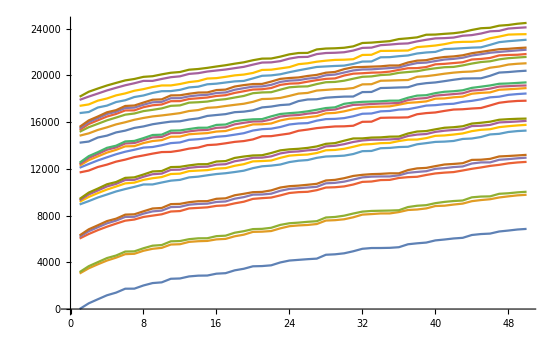

```mathematica
ListLinePlot@Array[h5GSFreq2[#, 50]&, 25]
```

Maybe this is more like it... But I don’t really see avoided crossings. Instead I just see the same pattern repeating every n steps.

We can also plot the different frequencies across the first 25 excited states. Each line is a different state (i.e. lowest is the first excitation energy, second is the second excitation, etc.)

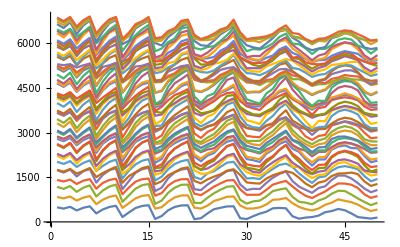

```mathematica
Array[h5Freqs2[#, 50]&, 50]//Transpose//ListLinePlot
```

Here is that in more readable form:

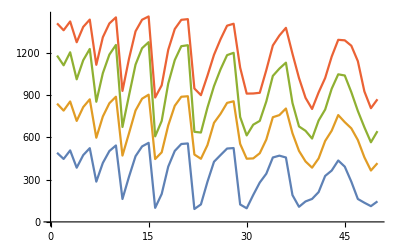

```mathematica
Array[h5Freqs2[#, 5]&, 50]//Transpose//ListLinePlot
```

#### Averaged Plots

Code

```mathematica
h5Plots2[i_, sel_:10]:=
$H5DVR[
"Wavefunctions"->h5Wfns2[i],
"Points"->{30, 30},
"WavefunctionSelection"->sel,
"ShowPotential"->False,
"WavefunctionClipping"->None,
"PlotMode"->"Density",
"PlotDisplayMode"->List,
ColorFunction->"Rainbow",
ColorFunctionScaling->True
]//Partition[#, UpTo@5]&//Grid
```

```mathematica
h5Plots3D2[i_, sel_:10]:=
$H5DVR[
"Wavefunctions"->h5Wfns2[i],
"Points"->{30, 30},
"WavefunctionSelection"->sel,
"ShowPotential"->False,
"WavefunctionClipping"->None,
"PlotMode"->"Cartesian",
"PlotDisplayMode"->List,
ColorFunction->"Rainbow",
ColorFunctionScaling->True
]//Partition[#, UpTo@5]&//Grid
```

Plots

```mathematica
h5Plots3D2[1, 3]
```

```mathematica
h5Plots3D2[7, 3]
```

```mathematica
With[{n=25, n2=5},
Map[
Sequence@@{
Prepend[Flatten@First@h5Plots2[#, n2], Row@{#, ": "}],
Join[{Null, 0}, h5Freqs2[#][[;;n2-1]]]
}&,
Ordering@Array[h5Freqs2, n][[All, 1]]
]//Grid[#/.g_Graphics:>Append[g, ImageSize->250], Dividers->{{1->Gray, -1->Gray}, Thread[Range[1, 2*n+1, 2]->Gray]}]&
]//Export["~/Documents/UW/Research/H5+/h2_outer_SA_pics.png", #]&
```

~/Documents/UW/Research/H5+/h2_outer_SA_pics.png

#### Ref

Reference states

```mathematica
#-#[[1]]&@
$H5DVR[
"Energies",
"Points"->{30, 30},
"NumberOfWavefunctions"->10
]//Rest
```

{520.322,850.812,1239.77,1388.46,1811.13,1832.47,2099.63,2287.23,2430.72}

```mathematica
$H5DVR[
"Points"->{30, 30},
"WavefunctionSelection"->10,
"ShowPotential"->False,
"WavefunctionClipping"->None,
"PlotMode"->"Density",
"PlotDisplayMode"->List,
ColorFunction->"Rainbow",
ColorFunctionScaling->True
]//Partition[#, 5]&//Grid
```

#### Transition Moments

```mathematica
h2SAInterpolatedDipoleSurfaces[{a_, s_}]:=
H5VectorizedInterpCut[{a, s, Automatic, Automatic}, #, 0.]&/@$H5DipoleSurfaceInterps
```

```mathematica
vec=h2SAInterpolatedDipoleSurfaces[{0, 2}][[1]];
```

Extract the the first 25 transition moments for each gridpoint in (s, a)

```mathematica
h2SADipoleVectors=
MapIndexed[
With[{fg=Flatten[h2SAGrid, 1]},
If[#=!=$Failed,
With[
{interps=h2SAInterpolatedDipoleSurfaces@#2[[1, 1]]},
#@fg&/@interps//Transpose
],
$Failed
]&
],
(* This is just here for the keys and the $Failed *)
h2SAWavefunctions
];
```

```mathematica
(*Manipulate[
ListPlot3D[
Join[Flatten[h2SAGrid, 1], h2SADipoleVectors[[h2SAValidCoords[[i]],All, {1}]], 2],
ColorFunction->"Rainbow",
PlotLabel->TemplateApply["s: `` a: ``", Keys[h2SAWavefunctions][[h2SAValidCoords[[i]]]]]
],
{i, 1, Length@h2SAValidCoords, 1}
]*)
```

There is some question as to whether I want to calculate μ_i=ϕ_i^H_2μ(r_1, r_2; s, a)ϕ_i^H_2 or μ_(i,0)=ϕ_i^H_2μ(r_1, r_2; s, a)ϕ_0^H_2. Not entirely sure which I want, but I believe the latter, from the math.

```mathematica
h2SATransitionMoments=
MapThread[
If[#=!=$Failed,
With[{wfns=#[[All, ;;25]], vec=#2},
$H2DVR[
"OperatorMatrixElements",
{1, 1;;25}->(vec&),
"Wavefunctions"->wfns,
"Grid"->h2SAGrid,
"PotentialEnergy"->None
]
],
$Failed
]&,
{
h2SAWavefunctions,
h2SADipoleVectors
}
];
```

Use these to calculate transition moments over the (s, a) coordinates

```mathematica
h2SAGridTMs=
Transpose@
Map[
If[#===$Failed, ConstantArray[0, {25, 3}], #]&, 
Values@h2SATransitionMoments
];
```

Then we calculate ψ_i(s,a; n_1, n_2)μ(s, a;n_1,n_2)ψ_0(s,a; 0, 0) to get a transition from the absolute ground state.

```mathematica
saTransitionMoments=
MapIndexed[
With[{vec=#},
$H5DVR[
"OperatorMatrixElements",
{1, 2;;26}->(vec&),
"Wavefunctions"->
MapThread[Join,
{
h5Wfns2[1][[All, ;;1]],
h5Wfns2[#2[[1]]]
}
],
"Grid"->h5Wfns2Grid,
"PotentialEnergy"->None
]
]&,
h2SAGridTMs
];
```

We then turn these into intensities and plot them:

```mathematica
saTransitionIntensities=
MapIndexed[
With[{ns=Norm[#]^2&/@#, freqs=h5GSFreq2[#2[[1]]][[;;25]]},
Thread[{freqs, ns/Max[ns]}]
]&,
saTransitionMoments
];
```

```mathematica
saTransitionUnnormedIntensities=
MapIndexed[
With[{ns=Norm[#]^2&/@#, freqs=h5GSFreq2[#2[[1]]][[;;25]]},
Thread[{freqs, ns}]
]&,
saTransitionMoments
];
```

#### Spectra Plots

After we build the transition moments we can plot them:

```mathematica
Manipulate[
H5PlotSpec[Join@@saTransitionUnnormedIntensities, shift],
{{shift, 1330}, 4400, -4400}
]
```

```mathematica
H5PlotSpecBroadened[
Join@@Rest@saTransitionUnnormedIntensities, 
35, 
1330
]
```

### Shared Proton Slices

```mathematica
h5sharedHWavefunctions[{1, 10}]=
$H5DVR["Wavefunctions", "PotentialFunction"->sharedHPot@{1, 10}];
```

```mathematica
h5sharedHWavefunctions[{1, 10}][[1]]-
h5sharedHWavefunctions[{1, 10}][[1, 1]]//Rest
```

{400.169,779.796,1113.41,1324.37,1396.84,1584.06,1792.04,2037.8,2238.38,2320.1,2622.43,2795.56,2962.34,3271.42,3341.99,3590.67,3688.61,3776.77,3998.23,4078.37,4146.63,4202.56,4337.87,4428.}

```mathematica
$H5DVR[
"Wavefunctions"->h5sharedHWavefunctions[{1, 10}],
"PlotDisplayMode"->List,
"ShowPotential"->False,
"WavefunctionSelection"->5,
"WavefunctionClipping"->None,
ViewPoint->Above
]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

### Single H2 Test

#### Direct Solution

##### Energies

```mathematica
Rest[#]-First[#]&@
$H2SingleDVR["Energies", "NumberOfWavefunctions"->10]
```

{3613.63,7152.95,10604.7,13874.9,16893.6,19817.3,22599.7,25266.6,27859.4}

##### Plots

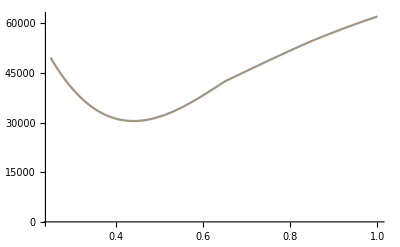

```mathematica
ListLinePlot[
$H2SingleDVR["GridPotentialEnergy"],
ColorFunction->"M10DefaultDensityGradient"
]
```

```mathematica
$H2SingleDVR[]
```

#### Potential Optimized DVR

##### Harmonic Potential

```mathematica
potFun=
{
"HarmonicOscillator",
"EquilibriumBondLength"->.65,
"ForceConstant"->10^8
};
```

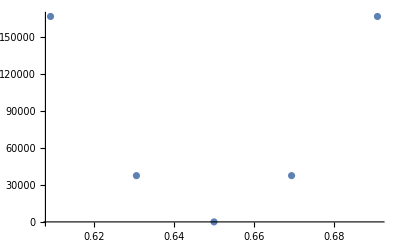

```mathematica
po=
$H2SingleDVR[
"PotentialOptimization", 
"Points"->250,
"OptimizedComponents"->All,
"OptimizedBasisSize"->5,
"PotentialFunction"->potFun
];
poGrid=po[["Grid", 1]];
ListPlot[
$H2SingleDVR[
"GridPotentialEnergy",
"Grid"->poGrid,
"PotentialFunction"->potFun
]
]
```

```mathematica
eTrue=
Sort@$H2SingleDVR[
"Energies", 
"PotentialFunction"->potFun, 
"NumberOfWavefunctions"->10
]
```

{40898.3,122695.,204492.,286288.,368085.,449882.,531678.,613475.,695272.,777068.}

```mathematica
$H2SingleDVR[
"Energies",
"Grid"->po[["Grid", 1]],
"KineticEnergy"->po[["KineticEnergy", 1]],
"PotentialEnergy"->po[["PotentialEnergy", 1]]
]
```

{40898.3,122695.,204492.}

##### Proper Potential

```mathematica
potE2=
$H2SingleDVR[
"GridPotentialEnergy",
"Grid"->poGrid2,
"PotentialFunction"->h2SinglePot
];
```

```mathematica
Rest[#]-First[#]&@
$H2SingleDVR[
"Energies", 
"Points"->250,
"OptimizedComponents"->All,
"OptimizedBasisSize"->6,
"PotentialFunction"->h2SinglePot,
"PotentialOptimize"->True,
"NumberOfWavefunctions"->All
]
```

```mathematica
{3613.014021283663,7142.091268658121,10385.833659392716,11928.765782050948,15564.83478532642}//Iconize
```

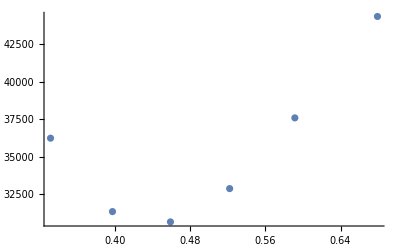

```mathematica
po2=
$H2SingleDVR[
"PotentialOptimization", 
"Points"->250,
"OptimizedComponents"->All,
"OptimizedBasisSize"->6,
"PotentialFunction"->h2SinglePot
];
poGrid2=po2[["Grid", 1]];
ListPlot[
$H2SingleDVR[
"GridPotentialEnergy",
"Grid"->poGrid2,
"PotentialFunction"->h2SinglePot
]
]
```

```mathematica
Rest[#]-First[#]&@
$H2SingleDVR[
"Energies",
"Points"->250,
"PotentialFunction"->h2SinglePot,
"NumberOfWavefunctions"->10
]
```

{3613.63,7152.95,10604.7,13874.9,16893.6,19817.3,22599.7,25266.6,27859.4}

```mathematica
Rest[#]-First[#]&@
$H2SingleDVR[
"Energies",
"PotentialOptimize"->True,
"NumberOfWavefunctions"->10
]//AbsoluteTiming
```

{0.476663,{3613.64,7152.99,10604.9,13875.4,16893.7,19817.5,22599.8,25266.9,27859.4}}

### Double H2 PODVR

#### Plots

##### Proper Solutions

```mathematica
$H2DVR[ 
"PruningEnergy"->Scaled[.35],
"Points"->{30, 30},
"ShowPotential"->False,
"PlotDisplayMode"->List,
"NumberOfWavefunctions"->5
]
```

```mathematica
$H2DVR[ 
"Wavefunctions",
"Points"->{80, 80},
"ShowPotential"->False,
"PlotDisplayMode"->List,
"NumberOfWavefunctions"->5
]//AbsoluteTiming
```

```mathematica
Rest[#]-First[#]&@
$H2DVR[ 
"Energies",
"Points"->{250, 250},
"ShowPotential"->False,
"PlotDisplayMode"->List,
"PotentialOptimizationOptions"->{
"PotentialFunction"->{h2SinglePot,h2SinglePot},
"OptimizedBasisSize"->50
},
"NumberOfWavefunctions"->6
]
```

{3495.56,3614.24,6938.68,7016.18,7191.27}

```mathematica
Iconize[
$H2DVR[ 
"Points"->{80, 80},
"ShowPotential"->False,
"PlotDisplayMode"->List,
"PlotMode"->"Density",
"PotentialOptimizationOptions"->{
"PotentialFunction"->{h2SinglePot,h2SinglePot},
"OptimizedBasisSize"->25
},
"NumberOfWavefunctions"->8,
Boxed->False,
Axes->False,
ImageSize->300,
ColorFunction->"Rainbow",
ColorFunctionScaling->True,
"WavefunctionClipping"->None
]
]
```

```mathematica
Iconize[gpe]
```

```mathematica
gpe=
$H2DVR[ 
"GridPotentialEnergy",
"Points"->{80, 80}
];
```

```mathematica
$H2DVR[ 
"Points"->{80, 80},
"ShowPotential"->False,
"PlotDisplayMode"->List,
"PotentialOptimizationOptions"->{
"PotentialFunction"->{h2SinglePot,h2SinglePot},
"OptimizedBasisSize"->25
},
"NumberOfWavefunctions"->6,
Boxed->False,
Axes->False,
ImageSize->300
];
```

##### Plots in the coupled potential

```mathematica
ListPlot3D[
$H2DVR[
"GridPotentialEnergy",
"Points"->{50, 50}
],
ColorFunction->h2ColFun,
ColorFunctionScaling->False
]
```

-Graphics3D-

##### Plots in the uncoupled potential

```mathematica
ListPlot3D[
$H2DVR[
"GridPotentialEnergy",
"Points"->{250, 250},
"PotentialFunction"->{h2SinglePot,h2SinglePot},
"PotentialOptimize"->True,
"OptimizedBasisSize"->10
],
ColorFunction->h2ColFun,
ColorFunctionScaling->False
]
```

-Graphics3D-

##### Frequencies from the coupled potential

```mathematica
$H2DVR[
"Energies",
"Points"->{60, 60},
"NumberOfWavefunctions"->10
]
```

{14712.8,18206.6,18325.4,21643.5,21719.4,21898.9,24978.8,25005.1,25214.7,25421.}

```mathematica
Rest[#]-First[#]&@
$H2DVR[
"Energies",
"Points"->{60, 60},
"NumberOfWavefunctions"->10
]
```

{3493.75,3612.53,6930.62,7006.59,7186.11,10265.9,10292.3,10501.9,10708.2}

```mathematica
$H2DVR[
"Points"->{60, 60},
"NumberOfWavefunctions"->10,
"PlotDisplayMode"->List
]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

##### Frequencies from the uncoupled potential

```mathematica
Rest[#]-First[#]&@
$H2DVR[
"Energies",
"Points"->{60, 60},
"PotentialFunction"->{h2SinglePot,h2SinglePot}
]
```

{3610.51,3610.51,7136.94,7136.94,7221.03,10559.3,10559.3,10747.5,10747.5,13791.2,13791.2,14169.8,14169.8,14273.9,16772.4,16772.4,17401.7,17401.7,17696.3,17696.3,19656.3,19656.3,20382.9,20382.9}

##### PODVR

Plots

```mathematica
Rest[#]-First[#]&@
$H2DVR[
"Energies",
"Points"->{125, 125},
"PlotDisplayMode"->List,
"PotentialOptimize"->True,
"PotentialOptimizationOptions"->{
"PotentialFunction"->{h2SinglePot,h2SinglePot},
"OptimizedBasisSize"->25
},
"NumberOfWavefunctions"->5
]
```

{3494.82,3613.54,6935.31,7012.12}

```mathematica
Rest[#]-First[#]&@
$H2DVR[
"Energies",
"Points"->{125, 125},
"PlotDisplayMode"->List,
"PotentialOptimize"->True,
"PotentialFunction"->{h2SinglePot,h2SinglePot},
"PotentialOptimizationOptions"->{
"OptimizedBasisSize"->25
},
"NumberOfWavefunctions"->5
]
```

{3612.41,3612.41,7146.66,7224.82}

```mathematica
$H2DVR[
"Points"->{125, 125},
"ShowPotential"->False,
"ShowEnergies"->True,
"PlotDisplayMode"->List,
"PotentialOptimize"->True,
"PotentialOptimizationOptions"->{
"PotentialFunction"->{h2SinglePot,h2SinglePot},
"OptimizedBasisSize"->25
},
"NumberOfWavefunctions"->5
]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

Test Energies

```mathematica
Rest[#]-First[#]&@
$H2DVR[
"Energies",
"Points"->{60, 60},
"PotentialOptimizationOptions"->
{
"PotentialFunction"->h2SinglePot,
"OptimizedBasisSize"->50
},
"NumberOfWavefunctions"->10
]
```

{3493.75,3612.53,6930.59,7006.54,7186.09,10265.7,10292.1,10501.8,10708.1}

Frequencies

```mathematica
Rest[#]-First[#]&@
$H2DVR[
"Energies",
"Points"->{250, 250},
"PotentialFunction"->{h2SinglePot,h2SinglePot},
"PotentialOptimize"->True,
"OptimizedBasisSize"->10,
"NumberOfWavefunctions"->10
]
```

{3613.63,3613.63,7152.95,7152.95,7227.27,10604.7,10604.7,10766.6,10766.6}

##### Extra Potentials

```mathematica
engs=
$H2DVR[
"Energies",
"Points"->{125, 125},
"PotentialEnergyOptions"->{
"PotentialFunction"->#
},
"PotentialOptimizationOptions"->{
"OptimizedBasisSize"->25,
"PotentialFunction"->{h2SinglePot,h2SinglePot}
},
"NumberOfWavefunctions"->12,
"ArnoldiIterations"->2500
]&/@h2Pots;
```

```mathematica
conts=
ListContourPlot[
$H2DVR[
"GridPotentialEnergy",
"Points"->{125, 125},
"PotentialEnergyOptions"->{
"PotentialFunction"->#
}
],
 ColorFunction->(Opacity[0]&), 
ContourStyle->GrayLevel[0, .35], 
PlotRangePadding->None
]&/@h2Pots;
```

```mathematica
wfnsies=
$H2DVR[
"Points"->{125, 125},
"PlotDisplayMode"->List,
"PotentialOptimize"->True,
"PotentialEnergyOptions"->{
"PotentialFunction"->#
},
"PotentialOptimizationOptions"->{
"OptimizedBasisSize"->25,
"PotentialFunction"->{h2SinglePot,h2SinglePot}
},
"NumberOfWavefunctions"->12,
"PlotMode"->"Density",
"ViewOptions"->
{
ColorFunctionScaling->True,
ColorFunction->ColorData@"Rainbow",
"ShowPotential"->False,
"WavefunctionClipping"->None
}
]&/@h2Pots;
```

```mathematica
plottos=
MapThread[
With[{cont=#},
MapThread[
Column@
{
Show[#, 
cont,
 PlotRangePadding->None,
 FrameTicks->None,
ImageSize->200
],
#2,
#3
}&,
{
#2,
#3,
#3-First[#3]
}
]
]&,
{
conts,
wfnsies,
engies-Min[engies]
}
];
```

```mathematica
plottoGrid=
Style[
KeyValueMap[
Prepend[#2, Grid@{{"R_1=", #[[1]]}, {"R_2=", #[[2]]}}]&,
plottos
]//Grid[#, ItemSize->Full]&,
FontFamily->"CMU Serif",
FontSize->24
]/.g_Grid:>Insert[g, Alignment->Center, 2];
```

```mathematica
biggyIm=
Rasterize[
plottoGrid,
ImageSize->2000
];
```

```mathematica
Export["~/Desktop/big_H2_R1_R2_effects.png", biggyIm]
```

~/Desktop/big_H2_R1_R2_effects.png

### 3D Contraction of 4D (1)

```mathematica
$H5Key={30, 25, {1}};
```

```mathematica
$H5Data[$H5Key, "SharedProtonPoints"]=$H5Key[[1]];
$H5Data[$H5Key, "SharedProtonBasisSize"]=$H5Data[$H5Key, "SharedProtonPoints"]^2;
$H5Data[$H5Key, "OuterH2Points"]=$H5Key[[2]];
$H5Data[$H5Key, "OuterH2States"]=$H5Key[[3]];
$H5Data[$H5Key, "OuterH2BasisSize"]=Length@$H5Data[$H5Key, "OuterH2States"];
$H5Data[$H5Key, "TotalBasisSize"]=$H5Data[$H5Key, "SharedProtonBasisSize"]*$H5Data[$H5Key, "OuterH2BasisSize"]
```

900

#### T_R

```mathematica
$H5Data[$H5Key, "SharedProtonKineticEnergy"]=
$H5DVR["KineticEnergy",
 "Points"->
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

#### h_r

H_2 wavefunctions are computed for the equilibrium value of (a, s)

```mathematica
$H5Data[$H5Key, "OuterH2Wavefunctions"]=
$H2DVR[
Return->{"Grid", "Wavefunctions"},
"Points"->{250, 250},
"PotentialOptimizationOptions"->
{
"PotentialFunction"->h2SinglePot,
"OptimizedBasisSize"->$H5Data[$H5Key, "OuterH2Points"]
},
"NumberOfWavefunctions"->$H5Data[$H5Key, "OuterH2Points"]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2Hamiltonian"]=
SparseArray[
Band[{1, 1}]->
$H5Data[$H5Key, "OuterH2Wavefunctions"][[
"Wavefunctions", 1, $H5Data[$H5Key, "OuterH2States"]
]]
];
```

#### V

```mathematica
$H5Data[$H5Key, "SharedProtonGrid"]=
$H5DVR["Grid", 
"Points"->{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

```mathematica
$H5Data[$H5Key, "OuterH2Grid"]=
Flatten[
$H5Data[$H5Key, "OuterH2Wavefunctions"]["Grid"],
 1
];
```

```mathematica
$H5Data[$H5Key, "OuterH2GridPotential"]=
h2PotVec@$H5Data[$H5Key, "OuterH2Grid"];
```

```mathematica
(*H5OuterH2PotVector//Clear*)
H5OuterH2PotVector[key_][i_,j_]:=
H5OuterH2PotVector[key][i,j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
H5FullVecPot@
Join[
ConstantArray[gp, $H5Data[$H5Key, "OuterH2Points"]^2],
$H5Data[$H5Key, "OuterH2Grid"],
2
],
ConstantArray[10^9, $H5Data[$H5Key, "OuterH2Points"]^2]
]-$H5Data[$H5Key, "OuterH2GridPotential"]
]
```

```mathematica
(*Clear[H5OuterH2PotBlock]*)
H5OuterH2PotBlock[key_][i_, j_]:=
H5OuterH2PotBlock[key][i, j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[i==1&&j==1||
dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
$H2DVR["OperatorMatrix",
Evaluate[H5OuterH2PotVector[key][i, j]]&,
"Grid"->$H5Data[key, "OuterH2Wavefunctions"]["Grid"],
"Wavefunctions"->Hold@$H5Data[key, "OuterH2Wavefunctions"]["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
H5OuterH2PotBlock[key][1, 1]
]
]
```

```mathematica
$H5Data[$H5Key, "PotentialBlocks"]=
Flatten[
Array[H5OuterH2PotBlock[$H5Key], 
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]}
], 
1
];
```

```mathematica
$H5Data[$H5Key, "PotentialEnergy"]=
SparseArray[
Band[{1,1}]->$H5Data[$H5Key, "PotentialBlocks"]
];
```

#### Full Kinetic Energy

```mathematica
$H5Data[$H5Key, "KineticEnergy"]=
KroneckerProduct[
IdentityMatrix[$H5Data[$H5Key, "OuterH2BasisSize"], SparseArray],
$H5Data[$H5Key, "SharedProtonKineticEnergy"]
]+
KroneckerProduct[
$H5Data[$H5Key, "OuterH2Hamiltonian"],
IdentityMatrix[$H5Data[$H5Key, "SharedProtonBasisSize"], SparseArray]
];
```

#### Energies and Wavefunctions

I just use one of the DVRs as a wrapper to access its eigenvalues/vectors routine

```mathematica
$H5Data[$H5Key, "Eigensystem"]=
$H2DVR["Wavefunctions", 
"KineticEnergy"->Hold@$H5Data[$H5Key, "KineticEnergy"],
"PotentialEnergy"->Hold@$H5Data[$H5Key, "PotentialEnergy"],
Method->"Direct", 
"NumberOfWavefunctions"->350(* This will die on some of these huge matrices... *)
(*"NumberOfWavefunctions"->250,
"ArnoldiIterations"->10000*)
];//AbsoluteTiming
```

{0.827134,Null}

```mathematica
{$H5Data[$H5Key, "Energies"], $H5Data[$H5Key, "Wavefunctions"]}=$H5Data[$H5Key, "Eigensystem"];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/wavefunctions@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Eigensystem"]
]
```

~/Documents/UW/Research/H5+/results/wavefunctions@{30, 25, {1}}.mx

##### Frequencies

```mathematica
$H5Data[$H5Key, "Frequencies"]=
Rest[#-#[[1]]]&@$H5Data[$H5Key, "Energies"];
$H5Data[$H5Key, "Frequencies"]~Take~100
```

{612.116,893.227,1421.36,1572.78,1964.24,1975.54,2403.79,2460.06,2929.07,2962.53,3037.22,3170.23,3247.6,3405.71,3413.98,3607.57,3718.34,3765.98,3880.38,4038.72,4044.86,4342.55,4405.77,4421.08,4637.7,4716.58,4751.12,4895.,4907.85,5188.65,5195.47,5489.67,5490.97,5538.43,5594.49,5659.68,6144.,6151.03,6339.65,6481.18,6517.8,6568.07,6591.5,6849.45,6873.58,6873.89,7001.02,7201.72,7202.78,7219.15,7504.63,7505.29,7714.39,7855.07,7862.63,7898.01,7904.04,8070.86,8198.29,8198.8,8224.2,8402.81,8649.54,8651.36,8766.88,9173.92,9177.08,9342.05,9533.79,9534.74,9571.87,9638.,9811.36,9821.92,9851.87,9898.57,9911.19,10071.8,10072.8,10356.8,10709.7,10877.2,10912.2,10970.7,10971.7,10995.2,11176.5,11317.7,11346.4,11602.7,11616.7,11778.9,11954.7,12044.4,12046.5,12079.,12080.9,12328.7,12408.8,12410.6}

##### Slices

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
Sign[ur.#]*Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
nr
]
];
```

#### Spectrum

##### Transition Moments

```mathematica
$H5Data[$H5Key, "SharedProtonGrid"]=
$H5DVR["Grid", "Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]}];
```

Helper to extract the grid to be use to compute the dipole surface elements. Effectively just the surface parametrized in (a, s)

```mathematica
H5OuterH2DipoleGrid[key_][i_, j_]:=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=$H5DipoleSurfaceInterps[[1, 1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
Join[
ConstantArray[gp, $H5Data[key, "OuterH2Points"]^2],
$H5Data[key, "OuterH2Grid"],
2
],
$Failed
]
]
```

```mathematica
(*computeDipVecs//Clear*)
H5OuterH2DipoleVector[key_][i_,j_]:=
H5OuterH2DipoleVector[key][i,j]=
With[{gr=H5OuterH2DipoleGrid[key][i, j]},
If[gr===$Failed,
ConstantArray[{0., 0., 0.}, $H5Data[key, "OuterH2Points"]^2],
$H5DipoleSurfaceVec@gr//Through//Transpose
]
]
```

This computes a term in the transition matrix defined by m_rμn_r for a given (a, s)

```mathematica
(*Clear[H5OuterH2TransitionMatrix]*)
H5OuterH2TransitionMatrix[key_][i_, j_]:=
H5OuterH2TransitionMatrix[key][i, j]=
With[{dip=H5OuterH2DipoleVector[key][i, j]},
If[Norm[Flatten[dip]]>0,
$H2DVR[
"OperatorMatrix",
(dip&),
"Grid"->$H5Data[key, "OuterH2Wavefunctions"]["Grid"],
"Wavefunctions"->$H5Data[key, "OuterH2Wavefunctions"]["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
$Failed
]
]
```

Computing these for each (R_1, R_2):

```mathematica
$H5Data[$H5Key, "OuterH2TransitionMoments"]=
Array[H5OuterH2TransitionMatrix[$H5Key], 
{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]}];
```

Then we slice up the coefficients:

```mathematica
$H5Data[$H5Key, "SharedProtonCoefficientVectors"]=
With[
{
wfns=$H5Data[$H5Key, "Wavefunctions"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
nr=$H5Data[$H5Key, "OuterH2BasisSize"]
},
Partition[
Array[
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]], 
ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Developer`ToPackedArray@
Map[
(*Sign[#.ur]**)#&,
wfs
]
]&,
NR^2
],
NR
]
];
```

Then we compute the transition moment vector over the (s, a) coordinates

```mathematica
H5SharedProtonTransitionMoment//Clear
H5SharedProtonTransitionMoment[key_][i_]:=
H5SharedProtonTransitionMoment[key][i]=
With[
{
coeffs=
Flatten[$H5Data[key, "SharedProtonCoefficientVectors"][[All, All, {i, 1}]], 1],
momsArr=
Flatten[$H5Data[key, "OuterH2TransitionMoments"], 1]
},
MapThread[
If[#2===$Failed,
0,
#[[1]].#2[[All,All, 1]].#[[2]]
]&,
{
coeffs,
momsArr
}
]
]
```

Check some phase stuff

```mathematica
Manipulate[
MapThread[Append, 
{
Flatten[$H5Data[$H5Key, "SharedProtonGrid"], 1],
H5SharedProtonTransitionMoment[$H5Key][i]
}
]//ListPlot3D[#, 
PlotRange->{{-1.5, 1.5}, {1.2, 2}, All},
 ColorFunction->"Rainbow", PerformanceGoal->"Quality"
]&,
{i, 1, Length@$H5Data[$H5Key, "Energies"], 1, AnimationRate->.5}
]
```

Norm and square to get raw intensity:

```mathematica
$H5Data[$H5Key, "Intensities"]=
Array[Total[H5SharedProtonTransitionMoment[$H5Key][#]]^2&, Length@$H5Data[$H5Key, "Energies"]];
```

##### Plots

```mathematica
$H5Data[$H5Key, "Spectrum"]=Thread[{Prepend[$H5Data[$H5Key, "Frequencies"], 0], $H5Data[$H5Key, "Intensities"]}];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/spectrum@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Spectrum"]
]
```

~/Documents/UW/Research/H5+/results/spectrum@{30, 25, {1}}.mx

```mathematica
$H5Data[$H5Key, "TargetShift"]=984-MaximalBy[#, Last, 2][[2, 1]]&@H5SpecPrep@$H5Data[$H5Key, "Spectrum"]
$H5Data[$H5Key, "TargetScaling"]=
(6684-4911)/(#[[2]]-#[[1]])&@
Sort@
MaximalBy[
H5SpecPrep[$H5Data[$H5Key, "Spectrum"],{4800, 7500}, Offset@$H5Data[$H5Key, "TargetShift"]],
Last,
2
][[All, 1]]
```

-437.36

2.60747

```mathematica
Manipulate[
H5PlotSpec[
$H5Data[$H5Key, "Spectrum"],
 Offset[shift, Scaled[scale]],
.05
],
{{shift, 225(*$H5Data[$H5Key, "TargetShift"]*)}, 4400, -4400},
{{scale, .68(*$H5Data[$H5Key, "TargetScaling"]*)}, .5, 2}
]
```

```mathematica
Manipulate[
H5SpecGaussianBroadenedSpectrum[
$H5Data[$H5Key, "Spectrum"], 
σ,
range,
Offset[shift, Scaled[scale]],
cutoff,
PlotRange->{range, All}
],
{{shift, 0}, 4400, -4400},
{{scale, 1}, .5, 1.5},
{{range, {4500, 7500}}, 0, 10000, ControlType->IntervalSlider},
{{σ, 25}, 1, 50, 1},
{{cutoff, .05}, 0.000001, .1}
]
```

#### State Assignments

##### Slices

Slice the wavefunctions to start:

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
Sign[ur.#]*Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
nr
]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]],
 ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Map[
Sign[#.ur]*#&,
wfs
]
]&,
NR^2
]
];
```

##### H2 Vectors

```mathematica
$H5Data[$H5Key, "OuterH2StateVectors"]=$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]//Transpose//Map[Normalize@*Total];
```

##### SP Vectors

For the shared-proton we’ll compute the overlap with the equilibrium calculation:

```mathematica
$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]=
$H5DVR["Wavefunctions", 
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"NumberOfWavefunctions"->10
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonStateCoefficients"]=
Table[
Transpose@$H5DVR[
"ExpectationValues",
Function[
{X, ψ},
#
]&/@wfns,
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"Wavefunctions"->$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]
],
{wfns, $H5Data[$H5Key, "SharedProtonSliceWavefunctions"]}
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonStateVectors"]=
$H5Data[$H5Key, "SharedProtonStateCoefficients"]//Transpose//Map[Normalize@*Total];
```

##### Tables

```mathematica
$iH5FormatStatePercentTableRelativeIntensities=True;
```

```mathematica
iH5FormatStatePercentTable[vecs_, headers_, states_, ops:OptionsPattern[]]:=
Grid[
Prepend[Join[{"𝒻", "ℐ"}, headers]]@
Join[
Round[List/@Prepend[$H5Data[$H5Key, "Frequencies"], 0][[states]], 1],
List/@
If[TrueQ@$iH5FormatStatePercentTableRelativeIntensities,
Map[
If[#<0.0001, ScientificForm[#, 2], Round[#, .01]]&,
100*#/Max[#]
]&,
Map[ScientificForm[#, 2]&]
]@$H5Data[$H5Key, "Intensities"][[states]],
100*
Round[
Power[
vecs,
2
], 
.01
],
2
],
ops,
Alignment->Left,
Dividers->{{3->Gray}, {2->Gray}},
ItemSize->Full
]//Style[#, ShowStringCharacters->False]&
```

```mathematica
H5FormatH2StatePercentTable[states_]:=
iH5FormatStatePercentTable[
$H5Data[$H5Key, "OuterH2StateVectors"][[states]],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
],
states
]
```

```mathematica
H5FormatH2StatePercentTable2[states_, saSpec_:All]:=
iH5FormatStatePercentTable[
Normalize@*Total/@
Transpose[
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]
][[states, saSpec]],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
],
states
]
```

```mathematica
H5FormatSharedProtonStatePercentTable[states_]:=
iH5FormatStatePercentTable[
$H5Data[$H5Key, "SharedProtonStateVectors"][[states]],
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[10]]]
],
states
]
```

```mathematica
H5FormatSharedProtonStatePercentTable[states_, h2Spec_]:=
iH5FormatStatePercentTable[
Normalize@*Total/@
Transpose[
$H5Data[$H5Key, "SharedProtonStateCoefficients"]
][[states, h2Spec]],
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[10]]]
],
states
]
```

```mathematica
H5FormatStatePercentTable[states_]:=
iH5FormatStatePercentTable[
Join[
$H5Data[$H5Key, "OuterH2StateVectors"][[states]],
$H5Data[$H5Key, "SharedProtonStateVectors"][[states]],
2
],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
]~Join~
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[10]]]
],
states,
Dividers->{{3, -10}->Gray//Thread, {2->Gray}}
]
```

##### Tests

```mathematica
H5FormatSharedProtonStatePercentTable[Ordering[$H5Data[$H5Key, "Intensities"], -25]//Sort]
```

𝒻 | ℐ | 1^(H+) | 2^(H+) | 3^(H+) | 4^(H+) | 5^(H+) | 6^(H+) | 7^(H+) | 8^(H+) | 9^(H+) | 10^(H+)
450 | 100. | 0. | 14. | 0. | 61. | 0. | 25. | 0. | 0. | 0. | 0.
1128 | 4.23 | 0. | 6. | 0. | 54. | 0. | 35. | 0. | 0. | 5. | 0.
1640 | 1.28 | 0. | 0. | 0. | 3. | 0. | 40. | 0. | 0. | 57. | 0.
2002 | 0.38 | 0. | 24. | 0. | 31. | 0. | 23. | 0. | 0. | 22. | 0.
2363 | 0.07 | 0. | 7. | 0. | 6. | 0. | 3. | 0. | 0. | 84. | 0.
2651 | 0.21 | 0. | 41. | 0. | 8. | 0. | 51. | 0. | 0. | 0. | 0.
3360 | 0.08 | 86. | 0. | 6. | 0. | 5. | 0. | 1. | 0. | 0. | 2.
3449 | 0.08 | 0. | 7. | 0. | 35. | 0. | 58. | 0. | 0. | 0. | 0.
3511 | 0.25 | 98. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0.
3858 | 1.55 | 0. | 45. | 0. | 44. | 0. | 10. | 0. | 0. | 1. | 0.
4012 | 1.78 | 0. | 99. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
4172 | 0.06 | 0. | 20. | 0. | 5. | 0. | 28. | 0. | 0. | 48. | 0.
4296 | 0.08 | 48. | 0. | 0. | 0. | 45. | 0. | 2. | 2. | 0. | 2.
4600 | 0.26 | 0. | 11. | 0. | 62. | 0. | 18. | 0. | 0. | 9. | 0.
4750 | 0.37 | 0. | 2. | 0. | 53. | 0. | 43. | 0. | 0. | 2. | 0.
5035 | 0.2 | 0. | 6. | 0. | 37. | 0. | 23. | 0. | 0. | 34. | 0.
5288 | 0.12 | 0. | 1. | 0. | 9. | 0. | 46. | 0. | 0. | 45. | 0.
5316 | 0.08 | 10. | 0. | 6. | 0. | 2. | 0. | 53. | 30. | 0. | 0.
5679 | 0.05 | 0. | 40. | 0. | 1. | 0. | 0. | 0. | 0. | 58. | 0.
6350 | 0.21 | 0. | 94. | 0. | 0. | 0. | 1. | 0. | 0. | 4. | 0.
7519 | 0.14 | 0. | 84. | 0. | 13. | 0. | 2. | 0. | 0. | 1. | 0.
7885 | 0.06 | 0. | 35. | 0. | 52. | 0. | 4. | 0. | 0. | 9. | 0.
8046 | 0.06 | 0. | 67. | 0. | 2. | 0. | 25. | 0. | 0. | 6. | 0.
8693 | 0.05 | 0. | 38. | 0. | 41. | 0. | 18. | 0. | 0. | 2. | 0.
8740 | 0.06 | 0. | 4. | 0. | 59. | 0. | 37. | 0. | 0. | 0. | 0.

```mathematica
H5FormatH2StatePercentTable[Ordering[$H5Data[$H5Key, "Intensities"], -25]//Sort]
```

𝒻 | ℐ | (0,0)^H_2 | (0,1-1,0)^H_2 | (0,1+1,0)^H_2 | (0,2-2,0)^H_2 | (1,1∠45)^H_2 | (0,2+2,0)^H_2
450 | 100. | 91. | 8. | 0. | 0. | 0. | 0.
1128 | 4.23 | 89. | 11. | 0. | 1. | 0. | 0.
1640 | 1.28 | 87. | 12. | 0. | 1. | 0. | 0.
2002 | 0.38 | 86. | 13. | 0. | 1. | 0. | 0.
2363 | 0.07 | 82. | 16. | 1. | 1. | 0. | 0.
2651 | 0.21 | 80. | 18. | 0. | 2. | 0. | 0.
3360 | 0.08 | 80. | 10. | 6. | 3. | 0. | 0.
3449 | 0.08 | 81. | 16. | 1. | 1. | 0. | 0.
3511 | 0.25 | 1. | 72. | 20. | 4. | 2. | 0.
3858 | 1.55 | 4. | 66. | 0. | 20. | 8. | 1.
4012 | 1.78 | 4. | 68. | 15. | 9. | 3. | 0.
4172 | 0.06 | 76. | 20. | 1. | 2. | 0. | 0.
4296 | 0.08 | 7. | 75. | 7. | 9. | 2. | 0.
4600 | 0.26 | 24. | 13. | 61. | 3. | 0. | 0.
4750 | 0.37 | 2. | 81. | 0. | 14. | 2. | 0.
5035 | 0.2 | 62. | 23. | 11. | 4. | 0. | 0.
5288 | 0.12 | 13. | 71. | 0. | 15. | 1. | 0.
5316 | 0.08 | 7. | 77. | 0. | 13. | 1. | 1.
5679 | 0.05 | 1. | 79. | 0. | 19. | 0. | 1.
6350 | 0.21 | 0. | 82. | 0. | 18. | 0. | 0.
7519 | 0.14 | 0. | 14. | 0. | 0. | 2. | 83.
7885 | 0.06 | 6. | 56. | 8. | 19. | 1. | 11.
8046 | 0.06 | 0. | 0. | 0. | 67. | 31. | 2.
8693 | 0.05 | 1. | 24. | 0. | 29. | 39. | 7.
8740 | 0.06 | 1. | 4. | 0. | 2. | 3. | 90.

### 3D Contraction of 4D (3)

```mathematica
$H5Key={30, 25, {1, 2, 3}};
```

```mathematica
$H5Data[$H5Key, "SharedProtonPoints"]=$H5Key[[1]];
$H5Data[$H5Key, "SharedProtonBasisSize"]=$H5Data[$H5Key, "SharedProtonPoints"]^2;
$H5Data[$H5Key, "OuterH2Points"]=$H5Key[[2]];
$H5Data[$H5Key, "OuterH2States"]=$H5Key[[3]];
$H5Data[$H5Key, "OuterH2BasisSize"]=Length@$H5Data[$H5Key, "OuterH2States"];
$H5Data[$H5Key, "TotalBasisSize"]=$H5Data[$H5Key, "SharedProtonBasisSize"]*$H5Data[$H5Key, "OuterH2BasisSize"]
```

2700

#### T_R

```mathematica
$H5Data[$H5Key, "SharedProtonKineticEnergy"]=
$H5DVR["KineticEnergy",
 "Points"->
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

#### h_r

H_2 wavefunctions are computed for the equilibrium value of (a, s)

```mathematica
$H5Data[$H5Key, "OuterH2Wavefunctions"]=
$H2DVR[
Return->{"Grid", "Wavefunctions"},
"Points"->{250, 250},
"PotentialOptimizationOptions"->
{
"PotentialFunction"->h2SinglePot,
"OptimizedBasisSize"->$H5Data[$H5Key, "OuterH2Points"]
},
"NumberOfWavefunctions"->$H5Data[$H5Key, "OuterH2Points"]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2Hamiltonian"]=
SparseArray[
Band[{1, 1}]->
$H5Data[$H5Key, "OuterH2Wavefunctions"][[
"Wavefunctions", 1, $H5Data[$H5Key, "OuterH2States"]
]]
];
```

#### V

```mathematica
$H5Data[$H5Key, "SharedProtonGrid"]=
$H5DVR["Grid", 
"Points"->{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

```mathematica
$H5Data[$H5Key, "OuterH2Grid"]=
Flatten[
$H5Data[$H5Key, "OuterH2Wavefunctions"]["Grid"],
 1
];
```

```mathematica
$H5Data[$H5Key, "OuterH2GridPotential"]=
h2PotVec@$H5Data[$H5Key, "OuterH2Grid"];
```

```mathematica
(*H5OuterH2PotVector//Clear*)
H5OuterH2PotVector[key_][i_,j_]:=
H5OuterH2PotVector[key][i,j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
H5FullVecPot@
Join[
ConstantArray[gp, $H5Data[key, "OuterH2Points"]^2],
$H5Data[key, "OuterH2Grid"],
2
],
ConstantArray[10^9, $H5Data[$H5Key, "OuterH2Points"]^2]
]-$H5Data[key, "OuterH2GridPotential"]
]
```

```mathematica
(*Clear[H5OuterH2PotBlock]*)
H5OuterH2PotBlock[key_][i_, j_]:=
H5OuterH2PotBlock[key][i, j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[i==1&&j==1||
dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
$H2DVR["OperatorMatrix",
Evaluate[H5OuterH2PotVector[key][i, j]]&,
"Grid"->$H5Data[key, "OuterH2Wavefunctions"]["Grid"],
"Wavefunctions"->Hold@$H5Data[key, "OuterH2Wavefunctions"]["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
H5OuterH2PotBlock[key][1, 1]
]
]
```

```mathematica
$H5Data[$H5Key, "PotentialBlocks"]=
Flatten[
Array[H5OuterH2PotBlock[$H5Key], 
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]}
], 
1
];
```

```mathematica
$H5Data[$H5Key, "PotentialEnergy"]=
SparseArray[
Band[{1,1}]->$H5Data[$H5Key, "PotentialBlocks"]
];
```

#### Full Kinetic Energy

```mathematica
$H5Data[$H5Key, "KineticEnergy"]=
KroneckerProduct[
$H5Data[$H5Key, "SharedProtonKineticEnergy"],
IdentityMatrix[$H5Data[$H5Key, "OuterH2BasisSize"], SparseArray]
]+
KroneckerProduct[
IdentityMatrix[$H5Data[$H5Key, "SharedProtonBasisSize"], SparseArray],
$H5Data[$H5Key, "OuterH2Hamiltonian"]
];
```

#### Energies and Wavefunctions

I just use one of the DVRs as a wrapper to access its eigenvalues/vectors routine

```mathematica
$H5Data[$H5Key, "Eigensystem"]=
$H2DVR["Wavefunctions", 
"KineticEnergy"->Hold@$H5Data[$H5Key, "KineticEnergy"],
"PotentialEnergy"->Hold@$H5Data[$H5Key, "PotentialEnergy"],
Method->"Direct", 
"NumberOfWavefunctions"->350(* This will die on some of these huge matrices... *)
(*"NumberOfWavefunctions"->250,
"ArnoldiIterations"->10000*)
];//AbsoluteTiming
```

{22.6233,Null}

```mathematica
{$H5Data[$H5Key, "Energies"], $H5Data[$H5Key, "Wavefunctions"]}=$H5Data[$H5Key, "Eigensystem"];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/wavefunctions@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Eigensystem"]
]
```

~/Documents/UW/Research/H5+/results/wavefunctions@{30, 25, {1, 2, 3}}.mx

##### Frequencies

```mathematica
$H5Data[$H5Key, "Frequencies"]=
Rest[#-#[[1]]]&@$H5Data[$H5Key, "Energies"];
$H5Data[$H5Key, "Frequencies"]~Take~100
```

{463.869,753.837,1162.39,1360.61,1664.43,1786.31,2012.78,2066.04,2443.88,2480.06,2740.16,2772.05,2842.18,2916.05,3076.93,3102.52,3113.19,3348.53,3382.25,3441.42,3568.04,3568.26,3601.29,3773.64,3774.79,4102.97,4175.21,4221.53,4230.32,4271.43,4272.9,4362.7,4384.31,4512.31,4603.54,4785.9,4812.,4818.7,4823.49,5004.72,5045.26,5079.1,5210.67,5221.55,5284.68,5435.93,5509.62,5513.15,5584.91,5595.25,5757.68,5793.52,5851.63,5853.18,5866.8,5866.84,6094.94,6130.54,6132.68,6141.97,6226.01,6439.78,6443.46,6460.83,6461.72,6491.82,6550.39,6580.58,6628.06,6645.98,6675.2,6728.47,6736.73,6776.,6776.37,6860.28,6902.95,6994.82,7101.87,7122.86,7160.4,7160.94,7204.25,7279.59,7281.41,7284.04,7352.76,7376.15,7408.2,7441.53,7460.77,7473.35,7566.79,7617.62,7618.15,7677.93,7733.74,7742.47,7747.1,7789.75}

##### Slices

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
Sign[ur.#]*Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
nr
]
];
```

#### Spectrum

##### Transition Moments

```mathematica
$H5Data[$H5Key, "SharedProtonGrid"]=
$H5DVR["Grid", "Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]}];
```

Helper to extract the grid to be use to compute the dipole surface elements. Effectively just the surface parametrized in (a, s)

```mathematica
H5OuterH2DipoleGrid[key_][i_, j_]:=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=$H5DipoleSurfaceInterps[[1, 1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
Join[
ConstantArray[gp, $H5Data[key, "OuterH2Points"]^2],
$H5Data[key, "OuterH2Grid"],
2
],
$Failed
]
]
```

```mathematica
(*H5OuterH2DipoleVector//Clear*)
H5OuterH2DipoleVector[key_][i_,j_]:=
H5OuterH2DipoleVector[key][i,j]=
With[{gr=H5OuterH2DipoleGrid[key][i, j]},
If[gr===$Failed,
ConstantArray[{0., 0., 0.}, $H5Data[key, "OuterH2Points"]^2],
$H5DipoleSurfaceVec@gr//Through//Transpose
]
]
```

This computes a term in the transition matrix defined by m_rμn_r for a given (a, s)

```mathematica
(*Clear[H5OuterH2TransitionMatrix]*)
H5OuterH2TransitionMatrix[key_][i_, j_]:=
H5OuterH2TransitionMatrix[key][i, j]=
With[{dip=H5OuterH2DipoleVector[key][i, j]},
If[Norm[Flatten[dip]]>0,
$H2DVR[
"OperatorMatrix",
(dip&),
"Grid"->$H5Data[key, "OuterH2Wavefunctions"]["Grid"],
"Wavefunctions"->$H5Data[key, "OuterH2Wavefunctions"]["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
$Failed
]
]
```

Computing these for each (R_1, R_2):

```mathematica
$H5Data[$H5Key, "OuterH2TransitionMoments"]=
Array[H5OuterH2TransitionMatrix[$H5Key], 
{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]}];
```

Then we slice up the coefficients:

```mathematica
$H5Data[$H5Key, "SharedProtonCoefficientVectors"]=
With[
{
wfns=$H5Data[$H5Key, "Wavefunctions"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
nr=$H5Data[$H5Key, "OuterH2BasisSize"]
},
Partition[
Array[
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]], 
ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Developer`ToPackedArray@
Map[
(*Sign[#.ur]**)#&,
wfs
]
]&,
NR^2
],
NR
]
];
```

Then we compute the transition moment vector over the (s, a) coordinates

```mathematica
H5SharedProtonTransitionMoment//Clear
H5SharedProtonTransitionMoment[key_][i_]:=
H5SharedProtonTransitionMoment[key][i]=
With[
{
coeffs=
Flatten[$H5Data[key, "SharedProtonCoefficientVectors"][[All, All, {i, 1}]], 1],
momsArr=
Flatten[$H5Data[key, "OuterH2TransitionMoments"], 1]
},
MapThread[
If[#2===$Failed,
0,
#[[1]].#2[[All,All, 1]].#[[2]]
]&,
{
coeffs,
momsArr
}
]
]
```

Check some phase stuff

```mathematica
Manipulate[
MapThread[Append, 
{
Flatten[$H5Data[$H5Key, "SharedProtonGrid"], 1],
H5SharedProtonTransitionMoment[$H5Key][i]
}
]//ListPlot3D[#, 
PlotRange->{{-1.5, 1.5}, {1.2, 2}, All},
 ColorFunction->"Rainbow", PerformanceGoal->"Quality"
]&,
{i, 1, Length@$H5Data[$H5Key, "Energies"], 1, AnimationRate->.5}
]
```

Norm and square to get raw intensity:

```mathematica
$H5Data[$H5Key, "Intensities"]=
Array[Total[H5SharedProtonTransitionMoment[$H5Key][#]]^2&, Length@$H5Data[$H5Key, "Energies"]];
```

##### Plots

```mathematica
$H5Data[$H5Key, "Spectrum"]=Thread[{Prepend[$H5Data[$H5Key, "Frequencies"], 0], $H5Data[$H5Key, "Intensities"]}];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/spectrum@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Spectrum"]
]
```

~/Documents/UW/Research/H5+/results/spectrum@{30, 25, {1, 2, 3}}.mx

```mathematica
(*$H5Data[$H5Key, "TargetShift"]=984-MaximalBy[#, Last, 2][[2, 1]]&@H5SpecPrep@$H5Data[$H5Key, "Spectrum"]
$H5Data[$H5Key, "TargetScaling"]=
(6684-4911)/(#[[2]]-#[[1]])&@
Sort@
MaximalBy[
H5SpecPrep[$H5Data[$H5Key, "Spectrum"],{4800, 7500}, Offset@$H5Data[$H5Key, "TargetShift"]],
Last,
2
][[All, 1]]*)
```

```mathematica
Manipulate[
H5PlotSpec[
$H5Data[$H5Key, "Spectrum"],
 Offset[shift, Scaled[scale]],
.05
],
{{shift, 0}, 4400, -4400, 10},
{{scale, 1}, .5, 2}
]
```

```mathematica
Manipulate[
H5SpecGaussianBroadenedSpectrum[
$H5Data[$H5Key, "Spectrum"], 
σ,
range,
Offset[shift, Scaled[scale]],
cutoff,
PlotRange->{range, All}
],
{{shift, 0}, 4400, -4400},
{{scale, 1}, .5, 1.5},
{{range, {4500, 7500}}, 0, 10000, ControlType->IntervalSlider},
{{σ, 25}, 1, 50, 1},
{{cutoff, .05}, 0.000001, .1}
]
```

#### State Assignments

##### Slices

Slice the wavefunctions to start:

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
(*Sign[ur.#]**)Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
nr
]
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctionsUnnormalized"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
(*(*Sign[ur.#]**)#&/@*)wfs//Developer`ToPackedArray
]&,
nr
]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]],
 ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Map[
(*Sign[#.ur]**)#&,
wfs
]
]&,
NR^2
]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2SliceWavefunctions"]=
With[
{
basis=
$H5Data[$H5Key, "OuterH2Wavefunctions"][[
"Wavefunctions",
 2,
$H5Data[$H5Key, "OuterH2States"]
]],
coeffs=Transpose@$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]
},
Map[
Map[Total[#*basis]&],
coeffs
]
];
```

##### H2 Vectors

```mathematica
$H5Data[$H5Key, "OuterH2StateVectors"]=$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]//Transpose//Map[Normalize@*Total];
```

##### SP Vectors

For the shared-proton we’ll compute the overlap with the equilibrium calculation:

```mathematica
$H5Data[$H5Key, "SharedProtonStates"]=350;
```

```mathematica
$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]=
$H5DVR["Wavefunctions", 
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"NumberOfWavefunctions"->$H5Data[$H5Key, "SharedProtonStates"]
];
```

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

```mathematica
$H5Data[$H5Key, "SharedProtonStateCoefficients"]=
Table[
Transpose@$H5DVR[
"ExpectationValues",
Function[
{X, ψ},
#
]&/@wfns,
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"Wavefunctions"->$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]
],
{wfns, $H5Data[$H5Key, "SharedProtonSliceWavefunctions"]}
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonStateVectors"]=
$H5Data[$H5Key, "SharedProtonStateCoefficients"]//Transpose//Map[Normalize@*Total];
```

Should I find a way to only deal with the overlaps near the eq.?

##### Tests

```mathematica
H5FormatStatePercentTable[;;35]
```

```mathematica
stateIndices=Partition[Range[30^2], 30];
```

```mathematica
H5PlotH2HPStates[{1, 3,7,8}, Flatten@stateIndices[[16, 4;;10]]]
```

```mathematica
Manipulate[
H5FormatH2StatePercentTable3[{1, 2, 3, 4, 5, 24}, Flatten@{stateIndices[[a, s]]}],
{{a, Range[30]}, Range[30], ControlType->TogglerBar},
{{s, {6}}, Range[30], ControlType->TogglerBar}
]
```

```mathematica
H5FormatH2StatePercentTable3[{1, 2, 3, 4, 5,6, 7, 8, 24}, Flatten@{stateIndices[[Range[30], {6}]]}]
```

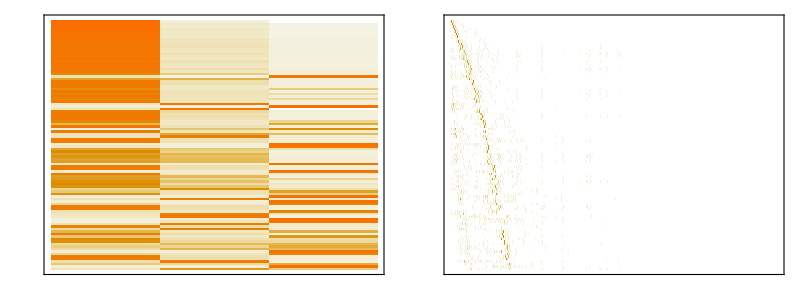

```mathematica
Grid@{
{
Show[H5FormatH2StatePercentPlot2[;;#],
FrameTicks->None, ImageSize->{Automatic, 5*#}],
Show[H5FormatSharedProtonStatePercentPlot[;;#],
FrameTicks->None,ImageSize->{Automatic, 5*#}] }}&@Max@{Min@{#, 350}, 1}&@100
```

```mathematica
MatrixPlot[Range[{50}], ImagePadding->None, PlotRangePadding->None, ImageSize->{Automatic, 50}]
```

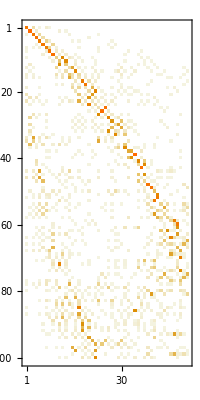

```mathematica
H5FormatSharedProtonStatePercentPlot[;;100]
```

```mathematica
H5PlotHPH2States[{2, 24}]
```

### 3D Contraction of 4D (3, Arnoldi)

```mathematica
$H5Key={30, 25, {1, 2, 3}, "Arnoldi"};
```

```mathematica
$H5Data[$H5Key, "SharedProtonPoints"]=$H5Key[[1]];
$H5Data[$H5Key, "SharedProtonBasisSize"]=$H5Data[$H5Key, "SharedProtonPoints"]^2;
$H5Data[$H5Key, "OuterH2Points"]=$H5Key[[2]];
$H5Data[$H5Key, "OuterH2States"]=$H5Key[[3]];
$H5Data[$H5Key, "OuterH2BasisSize"]=Length@$H5Data[$H5Key, "OuterH2States"];
$H5Data[$H5Key, "TotalBasisSize"]=$H5Data[$H5Key, "SharedProtonBasisSize"]*$H5Data[$H5Key, "OuterH2BasisSize"]
```

2700

#### T_R

```mathematica
$H5Data[$H5Key, "SharedProtonKineticEnergy"]=
$H5DVR["KineticEnergy",
 "Points"->
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

#### h_r

H_2 wavefunctions are computed for the equilibrium value of (a, s)

```mathematica
$H5Data[$H5Key, "OuterH2Wavefunctions"]=
$H2DVR[
Return->{"Grid", "Wavefunctions"},
"Points"->{250, 250},
"PotentialOptimizationOptions"->
{
"PotentialFunction"->h2SinglePot,
"OptimizedBasisSize"->$H5Data[$H5Key, "OuterH2Points"]
},
"NumberOfWavefunctions"->$H5Data[$H5Key, "OuterH2Points"]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2Hamiltonian"]=
SparseArray[
Band[{1, 1}]->
$H5Data[$H5Key, "OuterH2Wavefunctions"][[
"Wavefunctions", 1, $H5Data[$H5Key, "OuterH2States"]
]]
];
```

#### V

```mathematica
$H5Data[$H5Key, "SharedProtonGrid"]=
$H5DVR["Grid", 
"Points"->{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

```mathematica
$H5Data[$H5Key, "OuterH2Grid"]=
Flatten[
$H5Data[$H5Key, "OuterH2Wavefunctions"]["Grid"],
 1
];
```

```mathematica
$H5Data[$H5Key, "OuterH2GridPotential"]=
h2PotVec@$H5Data[$H5Key, "OuterH2Grid"];
```

```mathematica
(*H5OuterH2PotVector//Clear*)
H5OuterH2PotVector[key_][i_,j_]:=
H5OuterH2PotVector[key][i,j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
H5FullVecPot@
Join[
ConstantArray[gp, $H5Data[key, "OuterH2Points"]^2],
$H5Data[key, "OuterH2Grid"],
2
],
ConstantArray[10^9, $H5Data[$H5Key, "OuterH2Points"]^2]
]-$H5Data[key, "OuterH2GridPotential"]
]
```

```mathematica
(*Clear[H5OuterH2PotBlock]*)
H5OuterH2PotBlock[key_][i_, j_]:=
H5OuterH2PotBlock[key][i, j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[i==1&&j==1||
dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
$H2DVR["OperatorMatrix",
Evaluate[H5OuterH2PotVector[key][i, j]]&,
"Grid"->$H5Data[key, "OuterH2Wavefunctions"]["Grid"],
"Wavefunctions"->Hold@$H5Data[key, "OuterH2Wavefunctions"]["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
H5OuterH2PotBlock[key][1, 1]
]
]
```

```mathematica
$H5Data[$H5Key, "PotentialBlocks"]=
Flatten[
Array[H5OuterH2PotBlock[$H5Key], 
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]}
], 
1
];
```

```mathematica
$H5Data[$H5Key, "PotentialEnergy"]=
SparseArray[
Band[{1,1}]->$H5Data[$H5Key, "PotentialBlocks"]
];
```

#### Full Kinetic Energy

```mathematica
$H5Data[$H5Key, "KineticEnergy"]=
KroneckerProduct[
$H5Data[$H5Key, "SharedProtonKineticEnergy"],
IdentityMatrix[$H5Data[$H5Key, "OuterH2BasisSize"], SparseArray]
]+
KroneckerProduct[
IdentityMatrix[$H5Data[$H5Key, "SharedProtonBasisSize"], SparseArray],
$H5Data[$H5Key, "OuterH2Hamiltonian"]
];
```

#### Energies and Wavefunctions

I just use one of the DVRs as a wrapper to access its eigenvalues/vectors routine

```mathematica
$H5Data[$H5Key, "Eigensystem"]=
$H2DVR["Wavefunctions", 
"KineticEnergy"->Hold@$H5Data[$H5Key, "KineticEnergy"],
"PotentialEnergy"->Hold@$H5Data[$H5Key, "PotentialEnergy"],
"NumberOfWavefunctions"->350(* This will die on some of these huge matrices... *),
"ArnoldiIterations"->10000
];//AbsoluteTiming
```

{24.0299,Null}

```mathematica
{$H5Data[$H5Key, "Energies"], $H5Data[$H5Key, "Wavefunctions"]}=$H5Data[$H5Key, "Eigensystem"];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/wavefunctions@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Eigensystem"]
]
```

~/Documents/UW/Research/H5+/results/wavefunctions@{30, 25, {1, 2, 3}}.mx

##### Frequencies

```mathematica
$H5Data[$H5Key, "Frequencies"]=
Rest[#-#[[1]]]&@$H5Data[$H5Key, "Energies"];
$H5Data[$H5Key, "Frequencies"]~Take~100
```

{463.869,753.837,1162.39,1360.61,1664.43,1786.31,2012.78,2066.04,2443.88,2480.06,2740.16,2772.05,2842.18,2916.05,3076.93,3102.52,3113.19,3348.53,3382.25,3441.42,3568.04,3568.26,3601.29,3773.64,3774.79,4102.97,4175.21,4221.53,4230.32,4271.43,4272.9,4362.7,4384.31,4512.31,4603.54,4785.9,4812.,4818.7,4823.49,5004.72,5045.26,5079.1,5210.67,5221.55,5284.68,5435.93,5509.62,5513.15,5584.91,5595.25,5757.68,5793.52,5851.63,5853.18,5866.8,5866.84,6094.94,6130.54,6132.68,6141.97,6226.01,6439.78,6443.46,6460.83,6461.72,6491.82,6550.39,6580.58,6628.06,6645.98,6675.2,6728.47,6736.73,6776.,6776.37,6860.28,6902.95,6994.82,7101.87,7122.86,7160.4,7160.94,7204.25,7279.59,7281.41,7284.04,7352.76,7376.15,7408.2,7441.53,7460.77,7473.35,7566.79,7617.62,7618.15,7677.93,7733.74,7742.47,7747.1,7789.75}

```mathematica
dd
```

{463.869,753.837,1162.39,1360.61,1664.43,1786.31,2012.78,2066.04,2443.88,2480.06,2740.16,2772.05,2842.18,2916.05,3076.93,3102.52,3113.19,3348.53,3382.25,3441.42,3568.04,3568.26,3601.29,3773.64,3774.79,4102.97,4175.21,4221.53,4230.32,4271.43,4272.9,4362.7,4384.31,4512.31,4603.54,4785.9,4812.,4818.7,4823.49,5004.72,5045.26,5079.1,5210.67,5221.55,5284.68,5435.93,5509.62,5513.15,5584.91,5595.25,5757.68,5793.52,5851.63,5853.18,5866.8,5866.84,6094.94,6130.54,6132.68,6141.97,6226.01,6439.78,6443.46,6460.83,6461.72,6491.82,6550.39,6580.58,6628.06,6645.98,6675.2,6728.47,6736.73,6776.,6776.37,6860.28,6902.95,6994.82,7101.87,7122.86,7160.4,7160.94,7204.25,7279.59,7281.41,7284.04,7352.76,7376.15,7408.2,7441.53,7460.77,7473.35,7566.79,7617.62,7618.15,7677.93,7733.74,7742.47,7747.1,7789.75}

##### Slices

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
Sign[ur.#]*Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
nr
]
];
```

#### Spectrum

##### Transition Moments

```mathematica
$H5Data[$H5Key, "SharedProtonGrid"]=
$H5DVR["Grid", "Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]}];
```

Helper to extract the grid to be use to compute the dipole surface elements. Effectively just the surface parametrized in (a, s)

```mathematica
H5OuterH2DipoleGrid[key_][i_, j_]:=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=$H5DipoleSurfaceInterps[[1, 1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
Join[
ConstantArray[gp, $H5Data[key, "OuterH2Points"]^2],
$H5Data[key, "OuterH2Grid"],
2
],
$Failed
]
]
```

```mathematica
(*H5OuterH2DipoleVector//Clear*)
H5OuterH2DipoleVector[key_][i_,j_]:=
H5OuterH2DipoleVector[key][i,j]=
With[{gr=H5OuterH2DipoleGrid[key][i, j]},
If[gr===$Failed,
ConstantArray[{0., 0., 0.}, $H5Data[key, "OuterH2Points"]^2],
$H5DipoleSurfaceVec@gr//Through//Transpose
]
]
```

This computes a term in the transition matrix defined by m_rμn_r for a given (a, s)

```mathematica
(*Clear[H5OuterH2TransitionMatrix]*)
H5OuterH2TransitionMatrix[key_][i_, j_]:=
H5OuterH2TransitionMatrix[key][i, j]=
With[{dip=H5OuterH2DipoleVector[key][i, j]},
If[Norm[Flatten[dip]]>0,
$H2DVR[
"OperatorMatrix",
(dip&),
"Grid"->$H5Data[key, "OuterH2Wavefunctions"]["Grid"],
"Wavefunctions"->$H5Data[key, "OuterH2Wavefunctions"]["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
$Failed
]
]
```

Computing these for each (R_1, R_2):

```mathematica
$H5Data[$H5Key, "OuterH2TransitionMoments"]=
Array[H5OuterH2TransitionMatrix[$H5Key], 
{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]}];
```

Then we slice up the coefficients:

```mathematica
$H5Data[$H5Key, "SharedProtonCoefficientVectors"]=
With[
{
wfns=$H5Data[$H5Key, "Wavefunctions"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
nr=$H5Data[$H5Key, "OuterH2BasisSize"]
},
Partition[
Array[
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]], 
ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Developer`ToPackedArray@
Map[
(*Sign[#.ur]**)#&,
wfs
]
]&,
NR^2
],
NR
]
];
```

Then we compute the transition moment vector over the (s, a) coordinates

```mathematica
H5SharedProtonTransitionMoment//Clear
H5SharedProtonTransitionMoment[key_][i_]:=
H5SharedProtonTransitionMoment[key][i]=
With[
{
coeffs=
Flatten[$H5Data[key, "SharedProtonCoefficientVectors"][[All, All, {i, 1}]], 1],
momsArr=
Flatten[$H5Data[key, "OuterH2TransitionMoments"], 1]
},
MapThread[
If[#2===$Failed,
0,
#[[1]].#2[[All,All, 1]].#[[2]]
]&,
{
coeffs,
momsArr
}
]
]
```

Check some phase stuff

```mathematica
Manipulate[
MapThread[Append, 
{
Flatten[$H5Data[$H5Key, "SharedProtonGrid"], 1],
H5SharedProtonTransitionMoment[$H5Key][i]
}
]//ListPlot3D[#, 
PlotRange->{{-1.5, 1.5}, {1.2, 2}, All},
 ColorFunction->"Rainbow", PerformanceGoal->"Quality"
]&,
{i, 1, Length@$H5Data[$H5Key, "Energies"], 1, AnimationRate->.5}
]
```

Norm and square to get raw intensity:

```mathematica
$H5Data[$H5Key, "Intensities"]=
Array[Total[H5SharedProtonTransitionMoment[$H5Key][#]]^2&, Length@$H5Data[$H5Key, "Energies"]];
```

##### Plots

```mathematica
$H5Data[$H5Key, "Spectrum"]=Thread[{Prepend[$H5Data[$H5Key, "Frequencies"], 0], $H5Data[$H5Key, "Intensities"]}];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/spectrum@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Spectrum"]
]
```

~/Documents/UW/Research/H5+/results/spectrum@{30, 25, {1, 2, 3}, Arnoldi}.mx

```mathematica
(*$H5Data[$H5Key, "TargetShift"]=984-MaximalBy[#, Last, 2][[2, 1]]&@H5SpecPrep@$H5Data[$H5Key, "Spectrum"]
$H5Data[$H5Key, "TargetScaling"]=
(6684-4911)/(#[[2]]-#[[1]])&@
Sort@
MaximalBy[
H5SpecPrep[$H5Data[$H5Key, "Spectrum"],{4800, 7500}, Offset@$H5Data[$H5Key, "TargetShift"]],
Last,
2
][[All, 1]]*)
```

```mathematica
Manipulate[
H5PlotSpec[
$H5Data[$H5Key, "Spectrum"],
 Offset[shift, Scaled[scale]],
.05
],
{{shift, 0}, 4400, -4400, 10},
{{scale, 1}, .5, 2}
]
```

```mathematica
Manipulate[
H5SpecGaussianBroadenedSpectrum[
$H5Data[$H5Key, "Spectrum"], 
σ,
range,
Offset[shift, Scaled[scale]],
cutoff,
PlotRange->{range, All}
],
{{shift, 0}, 4400, -4400},
{{scale, 1}, .5, 1.5},
{{range, {4500, 7500}}, 0, 10000, ControlType->IntervalSlider},
{{σ, 25}, 1, 50, 1},
{{cutoff, .05}, 0.000001, .1}
]
```

#### State Assignments

##### Slices

Slice the wavefunctions to start:

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
(*Sign[ur.#]**)Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
nr
]
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctionsUnnormalized"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
(*(*Sign[ur.#]**)#&/@*)wfs//Developer`ToPackedArray
]&,
nr
]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]],
 ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Map[
(*Sign[#.ur]**)#&,
wfs
]
]&,
NR^2
]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2SliceWavefunctions"]=
With[
{
basis=
$H5Data[$H5Key, "OuterH2Wavefunctions"][[
"Wavefunctions",
 2,
$H5Data[$H5Key, "OuterH2States"]
]],
coeffs=Transpose@$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]
},
Map[
Map[Total[#*basis]&],
coeffs
]
];
```

##### H2 Vectors

```mathematica
$H5Data[$H5Key, "OuterH2StateVectors"]=$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]//Transpose//Map[Normalize@*Total];
```

##### SP Vectors

For the shared-proton we’ll compute the overlap with the equilibrium calculation:

```mathematica
$H5Data[$H5Key, "SharedProtonStates"]=350;
```

```mathematica
$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]=
$H5DVR["Wavefunctions", 
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"NumberOfWavefunctions"->$H5Data[$H5Key, "SharedProtonStates"]
];
```

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

```mathematica
$H5Data[$H5Key, "SharedProtonStateCoefficients"]=
Table[
Transpose@$H5DVR[
"ExpectationValues",
Function[
{X, ψ},
#
]&/@wfns,
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"Wavefunctions"->$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]
],
{wfns, $H5Data[$H5Key, "SharedProtonSliceWavefunctions"]}
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonStateVectors"]=
$H5Data[$H5Key, "SharedProtonStateCoefficients"]//Transpose//Map[Normalize@*Total];
```

Should I find a way to only deal with the overlaps near the eq.?

##### Tests

```mathematica
H5FormatStatePercentTable[;;35]
```

```mathematica
stateIndices=Partition[Range[30^2], 30];
```

```mathematica
H5PlotH2HPStates[{1, 3,7,8}, Flatten@stateIndices[[16, 4;;10]]]
```

```mathematica
Manipulate[
H5FormatH2StatePercentTable3[{1, 2, 3, 4, 5, 24}, Flatten@{stateIndices[[a, s]]}],
{{a, Range[30]}, Range[30], ControlType->TogglerBar},
{{s, {6}}, Range[30], ControlType->TogglerBar}
]
```

```mathematica
H5FormatH2StatePercentTable3[{1, 2, 3, 4, 5,6, 7, 8, 24}, Flatten@{stateIndices[[Range[30], {6}]]}]
```

```mathematica
Grid@{
{
Show[H5FormatH2StatePercentPlot2[;;#],
FrameTicks->None, ImageSize->{Automatic, 5*#}],
Show[H5FormatSharedProtonStatePercentPlot[;;#],
FrameTicks->None,ImageSize->{Automatic, 5*#}] }}&@Max@{Min@{#, 350}, 1}&@100
```

-Graphics-

```mathematica
MatrixPlot[Range[{50}], ImagePadding->None, PlotRangePadding->None, ImageSize->{Automatic, 50}]
```

```mathematica
H5FormatSharedProtonStatePercentPlot[;;100]
```

```mathematica
H5PlotHPH2States[{2, 24}]
```

### 3D Contraction of 4D (60, 3, Arnoldi)

```mathematica
$H5Key={60, 25, {1, 2, 3}, "Arnoldi"};
```

```mathematica
$H5Data[$H5Key, "SharedProtonPoints"]=$H5Key[[1]];
$H5Data[$H5Key, "SharedProtonBasisSize"]=$H5Data[$H5Key, "SharedProtonPoints"]^2;
$H5Data[$H5Key, "OuterH2Points"]=$H5Key[[2]];
$H5Data[$H5Key, "OuterH2States"]=$H5Key[[3]];
$H5Data[$H5Key, "OuterH2BasisSize"]=Length@$H5Data[$H5Key, "OuterH2States"];
$H5Data[$H5Key, "TotalBasisSize"]=$H5Data[$H5Key, "SharedProtonBasisSize"]*$H5Data[$H5Key, "OuterH2BasisSize"]
```

10800

#### T_R

```mathematica
$H5Data[$H5Key, "SharedProtonKineticEnergy"]=
$H5DVR["KineticEnergy",
 "Points"->
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

#### h_r

H_2 wavefunctions are computed for the equilibrium value of (a, s)

```mathematica
$H5Data[$H5Key, "OuterH2Wavefunctions"]=
$H2DVR[
Return->{"Grid", "Wavefunctions"},
"Points"->{250, 250},
"PotentialOptimizationOptions"->
{
"PotentialFunction"->h2SinglePot,
"OptimizedBasisSize"->$H5Data[$H5Key, "OuterH2Points"]
},
"NumberOfWavefunctions"->$H5Data[$H5Key, "OuterH2Points"]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2Hamiltonian"]=
SparseArray[
Band[{1, 1}]->
$H5Data[$H5Key, "OuterH2Wavefunctions"][[
"Wavefunctions", 1, $H5Data[$H5Key, "OuterH2States"]
]]
];
```

#### V

```mathematica
$H5Data[$H5Key, "SharedProtonGrid"]=
$H5DVR["Grid", 
"Points"->{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

```mathematica
$H5Data[$H5Key, "OuterH2Grid"]=
Flatten[
$H5Data[$H5Key, "OuterH2Wavefunctions"]["Grid"],
 1
];
```

```mathematica
$H5Data[$H5Key, "OuterH2GridPotential"]=
h2PotVec@$H5Data[$H5Key, "OuterH2Grid"];
```

```mathematica
(*H5OuterH2PotVector//Clear*)
H5OuterH2PotVector[key_][i_,j_]:=
H5OuterH2PotVector[key][i,j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
H5FullVecPot@
Join[
ConstantArray[gp, $H5Data[key, "OuterH2Points"]^2],
$H5Data[key, "OuterH2Grid"],
2
],
ConstantArray[10^9, $H5Data[$H5Key, "OuterH2Points"]^2]
]-$H5Data[key, "OuterH2GridPotential"]
]
```

```mathematica
(*Clear[H5OuterH2PotBlock]*)
H5OuterH2PotBlock[key_][i_, j_]:=
H5OuterH2PotBlock[key][i, j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[i==1&&j==1||
dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
$H2DVR["OperatorMatrix",
Evaluate[H5OuterH2PotVector[key][i, j]]&,
"Grid"->$H5Data[key, "OuterH2Wavefunctions"]["Grid"],
"Wavefunctions"->Hold@$H5Data[key, "OuterH2Wavefunctions"]["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
H5OuterH2PotBlock[key][1, 1]
]
]
```

```mathematica
$H5Data[$H5Key, "PotentialBlocks"]=
Flatten[
Array[H5OuterH2PotBlock[$H5Key], 
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]}
], 
1
];
```

```mathematica
$H5Data[$H5Key, "PotentialEnergy"]=
SparseArray[
Band[{1,1}]->$H5Data[$H5Key, "PotentialBlocks"]
];
```

#### Full Kinetic Energy

```mathematica
$H5Data[$H5Key, "KineticEnergy"]=
KroneckerProduct[
$H5Data[$H5Key, "SharedProtonKineticEnergy"],
IdentityMatrix[$H5Data[$H5Key, "OuterH2BasisSize"], SparseArray]
]+
KroneckerProduct[
IdentityMatrix[$H5Data[$H5Key, "SharedProtonBasisSize"], SparseArray],
$H5Data[$H5Key, "OuterH2Hamiltonian"]
];
```

#### Energies and Wavefunctions

I just use one of the DVRs as a wrapper to access its eigenvalues/vectors routine

```mathematica
$H5Data[$H5Key, "Eigensystem"]=
$H2DVR["Wavefunctions", 
"KineticEnergy"->Hold@$H5Data[$H5Key, "KineticEnergy"],
"PotentialEnergy"->Hold@$H5Data[$H5Key, "PotentialEnergy"],
"NumberOfWavefunctions"->350(* This will die on some of these huge matrices... *),
"ArnoldiIterations"->10000
];//AbsoluteTiming
```

{334.084,Null}

```mathematica
{$H5Data[$H5Key, "Energies"], $H5Data[$H5Key, "Wavefunctions"]}=$H5Data[$H5Key, "Eigensystem"];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/wavefunctions@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Eigensystem"]
]
```

~/Documents/UW/Research/H5+/results/wavefunctions@{60, 25, {1, 2, 3}, Arnoldi}.mx

##### Frequencies

```mathematica
$H5Data[$H5Key, "Frequencies"]=
Rest[#-#[[1]]]&@$H5Data[$H5Key, "Energies"];
$H5Data[$H5Key, "Frequencies"]~Take~100
```

{460.022,796.526,1153.16,1399.73,1714.84,1773.15,2006.25,2173.12,2365.99,2540.91,2668.6,2757.4,2867.73,2878.65,3041.71,3090.25,3232.86,3326.25,3455.23,3555.79,3569.15,3609.48,3635.68,3703.9,3836.46,3961.17,4117.67,4207.11,4217.87,4282.56,4355.63,4377.02,4412.8,4563.93,4642.79,4680.7,4728.99,4812.2,4913.48,5024.03,5026.98,5166.59,5202.14,5267.34,5276.37,5282.18,5374.37,5381.45,5409.86,5582.79,5603.94,5635.25,5654.67,5689.01,5738.25,5852.57,5898.41,5957.41,5965.89,5981.73,6034.54,6079.99,6159.7,6189.24,6232.54,6240.03,6294.86,6345.09,6351.22,6451.18,6452.57,6520.02,6601.83,6638.57,6644.85,6669.96,6712.1,6735.78,6805.9,6813.73,6826.66,6921.69,6945.67,6984.42,7040.85,7057.54,7079.79,7103.96,7147.01,7194.12,7217.7,7243.27,7263.65,7325.04,7334.35,7382.86,7473.67,7536.53,7553.51,7565.6}

```mathematica
dd
```

{463.869,753.837,1162.39,1360.61,1664.43,1786.31,2012.78,2066.04,2443.88,2480.06,2740.16,2772.05,2842.18,2916.05,3076.93,3102.52,3113.19,3348.53,3382.25,3441.42,3568.04,3568.26,3601.29,3773.64,3774.79,4102.97,4175.21,4221.53,4230.32,4271.43,4272.9,4362.7,4384.31,4512.31,4603.54,4785.9,4812.,4818.7,4823.49,5004.72,5045.26,5079.1,5210.67,5221.55,5284.68,5435.93,5509.62,5513.15,5584.91,5595.25,5757.68,5793.52,5851.63,5853.18,5866.8,5866.84,6094.94,6130.54,6132.68,6141.97,6226.01,6439.78,6443.46,6460.83,6461.72,6491.82,6550.39,6580.58,6628.06,6645.98,6675.2,6728.47,6736.73,6776.,6776.37,6860.28,6902.95,6994.82,7101.87,7122.86,7160.4,7160.94,7204.25,7279.59,7281.41,7284.04,7352.76,7376.15,7408.2,7441.53,7460.77,7473.35,7566.79,7617.62,7618.15,7677.93,7733.74,7742.47,7747.1,7789.75}

##### Slices

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
Sign[ur.#]*Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
nr
]
];
```

#### Spectrum

##### Transition Moments

```mathematica
$H5Data[$H5Key, "SharedProtonGrid"]=
$H5DVR["Grid", "Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]}];
```

Helper to extract the grid to be use to compute the dipole surface elements. Effectively just the surface parametrized in (a, s)

```mathematica
H5OuterH2DipoleGrid[key_][i_, j_]:=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=$H5DipoleSurfaceInterps[[1, 1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
Join[
ConstantArray[gp, $H5Data[key, "OuterH2Points"]^2],
$H5Data[key, "OuterH2Grid"],
2
],
$Failed
]
]
```

```mathematica
(*H5OuterH2DipoleVector//Clear*)
H5OuterH2DipoleVector[key_][i_,j_]:=
H5OuterH2DipoleVector[key][i,j]=
With[{gr=H5OuterH2DipoleGrid[key][i, j]},
If[gr===$Failed,
ConstantArray[{0., 0., 0.}, $H5Data[key, "OuterH2Points"]^2],
$H5DipoleSurfaceVec@gr//Through//Transpose
]
]
```

This computes a term in the transition matrix defined by m_rμn_r for a given (a, s)

```mathematica
(*Clear[H5OuterH2TransitionMatrix]*)
H5OuterH2TransitionMatrix[key_][i_, j_]:=
H5OuterH2TransitionMatrix[key][i, j]=
With[{dip=H5OuterH2DipoleVector[key][i, j]},
If[Norm[Flatten[dip]]>0,
$H2DVR[
"OperatorMatrix",
(dip&),
"Grid"->$H5Data[key, "OuterH2Wavefunctions"]["Grid"],
"Wavefunctions"->$H5Data[key, "OuterH2Wavefunctions"]["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
$Failed
]
]
```

Computing these for each (R_1, R_2):

```mathematica
$H5Data[$H5Key, "OuterH2TransitionMoments"]=
Array[H5OuterH2TransitionMatrix[$H5Key], 
{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]}];
```

Then we slice up the coefficients:

```mathematica
$H5Data[$H5Key, "SharedProtonCoefficientVectors"]=
With[
{
wfns=$H5Data[$H5Key, "Wavefunctions"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
nr=$H5Data[$H5Key, "OuterH2BasisSize"]
},
Partition[
Array[
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]], 
ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Developer`ToPackedArray@
Map[
(*Sign[#.ur]**)#&,
wfs
]
]&,
NR^2
],
NR
]
];
```

Then we compute the transition moment vector over the (s, a) coordinates

```mathematica
H5SharedProtonTransitionMoment//Clear
H5SharedProtonTransitionMoment[key_][i_]:=
H5SharedProtonTransitionMoment[key][i]=
With[
{
coeffs=
Flatten[$H5Data[key, "SharedProtonCoefficientVectors"][[All, All, {i, 1}]], 1],
momsArr=
Flatten[$H5Data[key, "OuterH2TransitionMoments"], 1]
},
MapThread[
If[#2===$Failed,
0,
#[[1]].#2[[All,All, 1]].#[[2]]
]&,
{
coeffs,
momsArr
}
]
]
```

Check some phase stuff

```mathematica
Manipulate[
MapThread[Append, 
{
Flatten[$H5Data[$H5Key, "SharedProtonGrid"], 1],
H5SharedProtonTransitionMoment[$H5Key][i]
}
]//ListPlot3D[#, 
PlotRange->{{-1.5, 1.5}, {1.2, 2}, All},
 ColorFunction->"Rainbow", PerformanceGoal->"Quality"
]&,
{i, 1, Length@$H5Data[$H5Key, "Energies"], 1, AnimationRate->.5}
]
```

Norm and square to get raw intensity:

```mathematica
$H5Data[$H5Key, "Intensities"]=
Array[Total[H5SharedProtonTransitionMoment[$H5Key][#]]^2&, Length@$H5Data[$H5Key, "Energies"]];
```

##### Plots

```mathematica
$H5Data[$H5Key, "Spectrum"]=Thread[{Prepend[$H5Data[$H5Key, "Frequencies"], 0], $H5Data[$H5Key, "Intensities"]}];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/spectrum@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Spectrum"]
]
```

~/Documents/UW/Research/H5+/results/spectrum@{60, 25, {1, 2, 3}, Arnoldi}.mx

```mathematica
(*$H5Data[$H5Key, "TargetShift"]=984-MaximalBy[#, Last, 2][[2, 1]]&@H5SpecPrep@$H5Data[$H5Key, "Spectrum"]
$H5Data[$H5Key, "TargetScaling"]=
(6684-4911)/(#[[2]]-#[[1]])&@
Sort@
MaximalBy[
H5SpecPrep[$H5Data[$H5Key, "Spectrum"],{4800, 7500}, Offset@$H5Data[$H5Key, "TargetShift"]],
Last,
2
][[All, 1]]*)
```

```mathematica
Manipulate[
H5PlotSpec[
$H5Data[$H5Key, "Spectrum"],
 Offset[shift, Scaled[scale]],
.05
],
{{shift, 0}, 4400, -4400, 10},
{{scale, 1}, .5, 2}
]
```

```mathematica
Manipulate[
H5SpecGaussianBroadenedSpectrum[
$H5Data[$H5Key, "Spectrum"], 
σ,
range,
Offset[shift, Scaled[scale]],
cutoff,
PlotRange->{range, All}
],
{{shift, 0}, 4400, -4400},
{{scale, 1}, .5, 1.5},
{{range, {4500, 7500}}, 0, 10000, ControlType->IntervalSlider},
{{σ, 25}, 1, 50, 1},
{{cutoff, .05}, 0.000001, .1}
]
```

#### State Assignments

##### Slices

Slice the wavefunctions to start:

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
(*Sign[ur.#]**)Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
nr
]
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctionsUnnormalized"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
(*(*Sign[ur.#]**)#&/@*)wfs//Developer`ToPackedArray
]&,
nr
]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]],
 ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Map[
(*Sign[#.ur]**)#&,
wfs
]
]&,
NR^2
]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2SliceWavefunctions"]=
With[
{
basis=
$H5Data[$H5Key, "OuterH2Wavefunctions"][[
"Wavefunctions",
 2,
$H5Data[$H5Key, "OuterH2States"]
]],
coeffs=Transpose@$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]
},
Map[
Map[Total[#*basis]&],
coeffs
]
];
```

##### H2 Vectors

```mathematica
$H5Data[$H5Key, "OuterH2StateVectors"]=$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]//Transpose//Map[Normalize@*Total];
```

##### SP Vectors

For the shared-proton we’ll compute the overlap with the equilibrium calculation:

```mathematica
$H5Data[$H5Key, "SharedProtonStates"]=75;
```

```mathematica
$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]=
$H5DVR["Wavefunctions", 
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"NumberOfWavefunctions"->$H5Data[$H5Key, "SharedProtonStates"]
];
```

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

```mathematica
$H5Data[$H5Key, "SharedProtonStateCoefficients"]=
Table[
Transpose@$H5DVR[
"ExpectationValues",
Function[
{X, ψ},
#
]&/@wfns,
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"Wavefunctions"->$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]
],
{wfns, $H5Data[$H5Key, "SharedProtonSliceWavefunctions"]}
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonStateVectors"]=
$H5Data[$H5Key, "SharedProtonStateCoefficients"]//Transpose//Map[Normalize@*Total];
```

Should I find a way to only deal with the overlaps near the eq.?

##### Tests

```mathematica
H5FormatStatePercentTable[;;35]
```

𝒻 | ℐ | (0,0)^H_2 | (0,1-1,0)^H_2 | (0,1+1,0)^H_2 | 1^(H+) | 2^(H+) | 3^(H+) | 4^(H+) | 5^(H+) | 6^(H+) | 7^(H+) | 8^(H+) | 9^(H+) | 10^(H+) | 11^(H+) | 12^(H+) | 13^(H+) | 14^(H+) | 15^(H+) | 16^(H+) | 17^(H+) | 18^(H+) | 19^(H+) | 20^(H+) | 21^(H+) | 22^(H+) | 23^(H+) | 24^(H+) | 25^(H+) | 26^(H+) | 27^(H+) | 28^(H+) | 29^(H+) | 30^(H+) | 31^(H+) | 32^(H+) | 33^(H+) | 34^(H+) | 35^(H+) | 36^(H+) | 37^(H+) | 38^(H+) | 39^(H+) | 40^(H+) | 41^(H+) | 42^(H+) | 43^(H+) | 44^(H+) | 45^(H+) | 46^(H+) | 47^(H+) | 48^(H+) | 49^(H+) | 50^(H+) | 51^(H+) | 52^(H+) | 53^(H+) | 54^(H+) | 55^(H+) | 56^(H+) | 57^(H+) | 58^(H+) | 59^(H+) | 60^(H+) | 61^(H+) | 62^(H+) | 63^(H+) | 64^(H+) | 65^(H+) | 66^(H+) | 67^(H+) | 68^(H+) | 69^(H+) | 70^(H+) | 71^(H+) | 72^(H+) | 73^(H+) | 74^(H+) | 75^(H+)
0 | 0. | 95. | 5. | 0. | 80. | 0. | 15. | 0. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
460 | 100. | 5. | 5. | 90. | 0. | 90. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
797 | 0. | 80. | 15. | 5. | 0. | 0. | 75. | 0. | 20. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1153 | 3.16 | 90. | 5. | 10. | 0. | 0. | 0. | 85. | 0. | 0. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1400 | 5.5×10^-5 | 90. | 10. | 0. | 0. | 0. | 0. | 0. | 55. | 30. | 0. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1715 | 0.54 | 95. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 80. | 0. | 15. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1773 | 0. | 100. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 65. | 0. | 10. | 0. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2006 | 5.2×10^-5 | 65. | 30. | 5. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 60. | 0. | 25. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2173 | 0.15 | 75. | 25. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 70. | 0. | 15. | 0. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2366 | 3.3×10^-5 | 90. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 35. | 0. | 50. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2541 | 0.05 | 85. | 10. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 40. | 0. | 30. | 0. | 25. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2669 | 0. | 65. | 30. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 15. | 0. | 15. | 0. | 50. | 0. | 15. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2757 | 0.01 | 75. | 20. | 5. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 35. | 0. | 30. | 0. | 15. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2868 | 0. | 90. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 20. | 0. | 40. | 0. | 25. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2879 | 7.4×10^-5 | 90. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 20. | 0. | 20. | 0. | 25. | 0. | 20. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3042 | 1.6×10^-6 | 25. | 75. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 30. | 0. | 15. | 0. | 25. | 0. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3090 | 0. | 40. | 60. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 20. | 0. | 30. | 0. | 30. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3233 | 7.1×10^-5 | 95. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 25. | 0. | 5. | 0. | 40. | 0. | 15. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3326 | 0.01 | 5. | 5. | 90. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 15. | 0. | 35. | 0. | 15. | 0. | 25. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3455 | 9.9×10^-5 | 90. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 10. | 0. | 15. | 0. | 10. | 0. | 30. | 0. | 30. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3556 | 8.1×10^-6 | 0. | 0. | 100. | 20. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 10. | 0. | 15. | 0. | 45. | 0. | 0. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3569 | 4.35 | 0. | 0. | 100. | 0. | 10. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 10. | 0. | 20. | 0. | 30. | 0. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3609 | 7.95 | 30. | 15. | 55. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 10. | 0. | 15. | 0. | 25. | 0. | 25. | 0. | 15. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3636 | 6.×10^-6 | 45. | 20. | 35. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 15. | 0. | 15. | 0. | 25. | 0. | 5. | 0. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3704 | 0.04 | 10. | 10. | 80. | 0. | 0. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 50. | 0. | 25. | 0. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3836 | 0. | 0. | 85. | 15. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 20. | 0. | 25. | 0. | 35. | 0. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3961 | 0.02 | 20. | 0. | 80. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 0. | 0. | 15. | 0. | 50. | 0. | 0. | 10. | 0. | 15. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4118 | 0. | 30. | 60. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 25. | 0. | 10. | 0. | 0. | 40. | 0. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4207 | 0. | 80. | 20. | 0. | 0. | 5. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 0. | 70. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4218 | 0. | 80. | 20. | 0. | 0. | 0. | 5. | 0. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 75. | 0. | 0. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4283 | 0. | 0. | 100. | 0. | 0. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 10. | 0. | 0. | 50. | 0. | 10. | 0. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4356 | 0. | 0. | 10. | 90. | 0. | 0. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 20. | 0. | 0. | 40. | 0. | 5. | 0. | 20. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4377 | 0.04 | 10. | 90. | 0. | 5. | 0. | 30. | 0. | 10. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 0. | 0. | 0. | 25. | 0. | 5. | 0. | 0. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4413 | 0.01 | 10. | 90. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 20. | 0. | 55. | 0. | 10. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4564 | 0. | 5. | 0. | 95. | 5. | 0. | 20. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 45. | 0. | 15. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.

```mathematica
H5FormatStatePercentTable2[;;35]/.(0.->"")
```

```mathematica
H5FormatStatePercentTable2[;;35]
```

𝒻 | ℐ | (0,0)^H_2 | (0,1-1,0)^H_2 | (0,1+1,0)^H_2 | 1^(H+) | 2^(H+) | 3^(H+) | 4^(H+) | 5^(H+) | 6^(H+) | 7^(H+) | 8^(H+) | 9^(H+) | 10^(H+) | 11^(H+) | 12^(H+) | 13^(H+) | 14^(H+) | 15^(H+) | 16^(H+) | 17^(H+) | 18^(H+) | 19^(H+) | 20^(H+) | 21^(H+) | 22^(H+) | 23^(H+) | 24^(H+) | 25^(H+) | 26^(H+) | 27^(H+) | 28^(H+) | 29^(H+) | 30^(H+) | 31^(H+) | 32^(H+) | 33^(H+) | 34^(H+) | 35^(H+) | 36^(H+) | 37^(H+) | 38^(H+) | 39^(H+) | 40^(H+) | 41^(H+) | 42^(H+) | 43^(H+) | 44^(H+) | 45^(H+) | 46^(H+) | 47^(H+) | 48^(H+) | 49^(H+) | 50^(H+) | 51^(H+) | 52^(H+) | 53^(H+) | 54^(H+) | 55^(H+) | 56^(H+) | 57^(H+) | 58^(H+) | 59^(H+) | 60^(H+) | 61^(H+) | 62^(H+) | 63^(H+) | 64^(H+) | 65^(H+) | 66^(H+) | 67^(H+) | 68^(H+) | 69^(H+) | 70^(H+) | 71^(H+) | 72^(H+) | 73^(H+) | 74^(H+) | 75^(H+)
0 | 0. | 95. | 5. | 0. | 80. | 0. | 15. | 0. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
460 | 100. | 90. | 5. | 0. | 0. | 90. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
797 | 0. | 95. | 5. | 0. | 5. | 0. | 75. | 0. | 20. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1153 | 3.16 | 90. | 10. | 0. | 0. | 0. | 0. | 85. | 0. | 0. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1400 | 5.5×10^-5 | 90. | 5. | 0. | 0. | 0. | 5. | 0. | 55. | 30. | 0. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1715 | 0.54 | 90. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 80. | 0. | 15. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1773 | 0. | 90. | 5. | 0. | 5. | 0. | 5. | 0. | 5. | 65. | 0. | 10. | 0. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2006 | 5.2×10^-5 | 90. | 10. | 0. | 5. | 0. | 0. | 0. | 0. | 5. | 0. | 60. | 0. | 25. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2173 | 0.15 | 85. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 70. | 0. | 15. | 0. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2366 | 3.3×10^-5 | 90. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 35. | 0. | 50. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2541 | 0.05 | 85. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 35. | 0. | 30. | 0. | 25. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2669 | 0. | 90. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 10. | 0. | 15. | 0. | 50. | 0. | 15. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2757 | 0.01 | 90. | 10. | 0. | 0. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 35. | 0. | 30. | 0. | 15. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2868 | 0. | 85. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 20. | 0. | 40. | 0. | 25. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2879 | 7.4×10^-5 | 90. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 20. | 0. | 20. | 0. | 25. | 0. | 15. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3042 | 1.6×10^-6 | 85. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 30. | 0. | 15. | 0. | 25. | 0. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3090 | 0. | 85. | 15. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 20. | 0. | 30. | 0. | 30. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3233 | 7.1×10^-5 | 85. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 25. | 0. | 5. | 0. | 40. | 0. | 15. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3326 | 0.01 | 85. | 15. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 15. | 0. | 35. | 0. | 15. | 0. | 25. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3455 | 9.9×10^-5 | 90. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 10. | 0. | 15. | 0. | 5. | 0. | 30. | 0. | 30. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3556 | 8.1×10^-6 | 30. | 5. | 65. | 25. | 0. | 0. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 10. | 0. | 10. | 0. | 35. | 0. | 0. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3569 | 4.35 | 65. | 30. | 0. | 0. | 15. | 0. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 10. | 0. | 20. | 0. | 25. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3609 | 7.95 | 60. | 40. | 0. | 0. | 15. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 10. | 0. | 10. | 0. | 20. | 0. | 20. | 0. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3636 | 6.×10^-6 | 85. | 10. | 5. | 15. | 0. | 0. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 15. | 0. | 15. | 0. | 25. | 0. | 5. | 0. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3704 | 0.04 | 85. | 10. | 0. | 0. | 0. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 45. | 0. | 25. | 0. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3836 | 0. | 85. | 10. | 5. | 5. | 0. | 0. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 15. | 0. | 20. | 0. | 30. | 0. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3961 | 0.02 | 85. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 0. | 0. | 15. | 0. | 50. | 0. | 0. | 5. | 0. | 15. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4118 | 0. | 90. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 25. | 0. | 10. | 0. | 0. | 40. | 0. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4207 | 0. | 25. | 5. | 75. | 0. | 40. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 0. | 45. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4218 | 0. | 85. | 10. | 5. | 0. | 0. | 10. | 0. | 0. | 15. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 65. | 0. | 0. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4283 | 0. | 80. | 10. | 5. | 0. | 15. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 10. | 0. | 0. | 50. | 0. | 10. | 0. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4356 | 0. | 85. | 10. | 5. | 0. | 0. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 15. | 0. | 0. | 40. | 0. | 5. | 0. | 15. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4377 | 0.04 | 20. | 80. | 0. | 25. | 0. | 45. | 0. | 5. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4413 | 0.01 | 85. | 10. | 5. | 0. | 5. | 0. | 0. | 0. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 20. | 0. | 50. | 0. | 5. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4564 | 0. | 35. | 5. | 60. | 5. | 0. | 25. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 35. | 0. | 10. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.

```mathematica
stateIndices=Partition[Range[30^2], 30];
```

```mathematica
Manipulate[
H5FormatH2StatePercentTable3[{1, 2, 3, 4, 5, 24}, Flatten@{stateIndices[[a, s]]}],
{{a, Range[30]}, Range[30], ControlType->TogglerBar},
{{s, {6}}, Range[30], ControlType->TogglerBar}
]
```

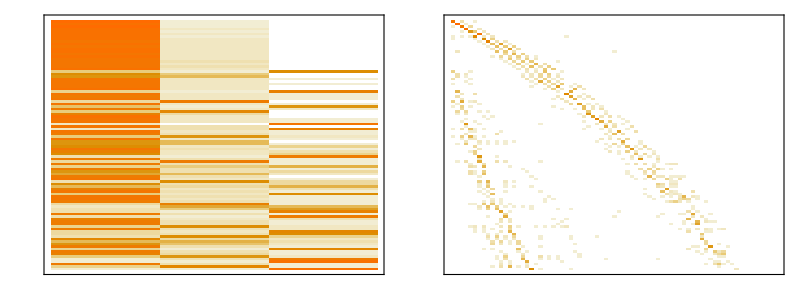

```mathematica
Grid@{
{
Show[H5FormatH2StatePercentPlot2[;;#],
FrameTicks->None, ImageSize->{Automatic, 5*#}],
Show[H5FormatSharedProtonStatePercentPlot2[;;#],
FrameTicks->None,ImageSize->{Automatic, 5*#}] }}&@Max@{Min@{#, 350}, 1}&@100
```

```mathematica
MatrixPlot[Range[{50}], ImagePadding->None, PlotRangePadding->None, ImageSize->{Automatic, 50}]
```

```mathematica
H5FormatSharedProtonStatePercentPlot[;;100]
```

```mathematica
H5PlotHPH2States[{2, 24}]
```

### 3D Contraction of 4D (3) Basis 2

```mathematica
$H5Key={30, 25, {1, 2, 3}, 2};
$H5Data[$H5Key, "SharedProtonPoints"]=$H5Key[[1]];
$H5Data[$H5Key, "SharedProtonBasisSize"]=$H5Data[$H5Key, "SharedProtonPoints"]^2;
$H5Data[$H5Key, "OuterH2Points"]=$H5Key[[2]];
$H5Data[$H5Key, "OuterH2States"]=$H5Key[[3]];
$H5Data[$H5Key, "OuterH2BasisSize"]=Length@$H5Data[$H5Key, "OuterH2States"];
$H5Data[$H5Key, "TotalBasisSize"]=$H5Data[$H5Key, "SharedProtonBasisSize"]*$H5Data[$H5Key, "OuterH2BasisSize"]
```

2700

#### T_R

```mathematica
$H5Data[$H5Key, "SharedProtonKineticEnergy"]=
$H5DVR["KineticEnergy",
 "Points"->
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

#### h_r

H_2 wavefunctions are computed for the equilibrium value of (a, s)

```mathematica
$H5Data[$H5Key, "SharedProtonGrid"]=
$H5DVR["Grid",
 "Points"->
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

```mathematica
(*H5OuterH2WavefunctionBlock//Clear*)
H5OuterH2WavefunctionBlock[key_][i_,j_]:=
H5OuterH2WavefunctionBlock[key][i,j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
$H2DVR[
Return->{"Grid", "Wavefunctions"},
"Points"->{250, 250},
"PotentialFunction"->h5PotCut[Join[gp, {Automatic, Automatic}]],
"PotentialOptimizationOptions"->
{
"PotentialFunction"->h2SinglePot,
"OptimizedBasisSize"->$H5Data[$H5Key, "OuterH2Points"]
},
"NumberOfWavefunctions"->$H5Data[$H5Key, "OuterH2Points"]
],
<|
"Grid"->None,
"Wavefunctions"->
{
ConstantArray[10.^9,$H5Data[$H5Key, "OuterH2Points"]],
ConstantArray[0.,
 {$H5Data[$H5Key, "OuterH2Points"], $H5Data[$H5Key, "OuterH2Points"]^2}
]
}
|>
]
]
```

```mathematica
$H5Data[$H5Key, "OuterH2Wavefunctions"]=
Array[
H5OuterH2WavefunctionBlock[$H5Key],
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

```mathematica
$H5Data[$H5Key, "OuterH2Hamiltonian"]=
SparseArray[
Band[{1, 1}]->
Flatten@
Flatten[$H5Data[$H5Key, "OuterH2Wavefunctions"], 1][[All, "Wavefunctions", 1, $H5Data[$H5Key, "OuterH2States"]]
]
];
```

#### V

I think I don’t need this?

```mathematica
(*(*Clear[H5OuterH2PotBlock]*)
H5OuterH2PotBlock[key_][i_, j_]:=
H5OuterH2PotBlock[key][i, j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[i==1&&j==1||
dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
$H2DVR["OperatorMatrix",
Evaluate[H5OuterH2PotVector[key][i, j]]&,
"Grid"->$H5Data[key, "OuterH2Wavefunctions"]["Grid"],
"Wavefunctions"->Hold@$H5Data[key, "OuterH2Wavefunctions"]["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
H5OuterH2PotBlock[key][1, 1]
]
]*)
```

```mathematica
(*$H5Data[$H5Key, "PotentialBlocks"]=
Flatten[
Array[H5OuterH2PotBlock[$H5Key], 
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]}
], 
1
];*)
```

```mathematica
(*$H5Data[$H5Key, "PotentialEnergy"]=
SparseArray[
Band[{1,1}]->$H5Data[$H5Key, "PotentialBlocks"]
];*)
```

#### Full Kinetic Energy

```mathematica
$H5Data[$H5Key, "KineticEnergy"]=
KroneckerProduct[
$H5Data[$H5Key, "SharedProtonKineticEnergy"],
IdentityMatrix[$H5Data[$H5Key, "OuterH2BasisSize"], SparseArray]
](*+
KroneckerProduct[
IdentityMatrix[$H5Data[$H5Key, "SharedProtonBasisSize"], SparseArray],
$H5Data[$H5Key, "OuterH2Hamiltonian"]
]*);
```

#### Energies and Wavefunctions

I just use one of the DVRs as a wrapper to access its eigenvalues/vectors routine

```mathematica
$H5Data[$H5Key, "Eigensystem"]=
$H2DVR["Wavefunctions", 
"KineticEnergy"->Hold@$H5Data[$H5Key, "KineticEnergy"],
"PotentialEnergy"->Hold@$H5Data[$H5Key, "OuterH2Hamiltonian"],
Method->"Direct", 
"NumberOfWavefunctions"->350(* This will die on some of these huge matrices... *)
(*"NumberOfWavefunctions"->250,
"ArnoldiIterations"->10000*)
];//AbsoluteTiming
```

{20.7206,Null}

```mathematica
{$H5Data[$H5Key, "Energies"], $H5Data[$H5Key, "Wavefunctions"]}=$H5Data[$H5Key, "Eigensystem"];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/wavefunctions@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Eigensystem"]
]
```

~/Documents/UW/Research/H5+/results/wavefunctions@{30, 25, {1, 2, 3}, 2}.mx

##### Frequencies

```mathematica
$H5Data[$H5Key, "Frequencies"]=
Rest[#-#[[1]]]&@$H5Data[$H5Key, "Energies"];
$H5Data[$H5Key, "Frequencies"]~Take~100
```

{442.882,728.424,1117.2,1290.93,1626.66,1726.96,1932.8,1987.06,2308.32,2343.89,2640.01,2652.77,2721.13,2883.46,2929.21,2998.49,3092.15,3217.44,3241.02,3349.61,3415.1,3483.82,3488.91,3621.18,3625.1,3745.68,3951.63,4033.31,4043.39,4085.19,4099.12,4126.93,4214.12,4234.04,4348.52,4393.45,4573.57,4634.6,4685.92,4686.65,4692.82,4803.29,4816.46,4895.62,4922.67,4989.31,5013.07,5135.82,5148.67,5201.61,5234.47,5246.96,5295.25,5299.2,5456.38,5515.55,5537.6,5576.49,5621.8,5623.61,5767.01,5852.42,5858.15,5876.18,5880.72,5887.71,5906.48,5920.14,5993.06,6056.07,6108.14,6141.33,6192.5,6195.69,6243.17,6244.74,6248.54,6273.1,6292.02,6370.1,6430.75,6432.01,6479.72,6481.24,6495.11,6523.62,6565.96,6569.34,6597.77,6732.64,6739.59,6782.5,6792.79,6793.87,6837.77,6844.59,6914.86,7001.44,7101.01,7135.37}

##### Slices

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
Sign[ur.#]*Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
nr
]
];
```

#### Spectrum

##### Transition Moments

Helper to extract the grid to be use to compute the dipole surface elements. Effectively just the surface parametrized in (a, s)

```mathematica
H5OuterH2DipoleGrid2[key_][i_, j_]:=
With[
{
gp=$H5Data[key, "SharedProtonGrid"][[i, j]], 
gd=$H5Data[key, "OuterH2Wavefunctions"][[i, j, "Grid"]]
},
If[gd=!=None,
Join[
ConstantArray[gp, $H5Data[key, "OuterH2Points"]^2],
Flatten[gd, 1],
2
],
$Failed
]
]
```

```mathematica
(*H5OuterH2DipoleVector2//Clear*)
H5OuterH2DipoleVector2[key_][i_,j_]:=
H5OuterH2DipoleVector2[key][i,j]=
With[{gr=H5OuterH2DipoleGrid2[key][i, j]},
If[gr===$Failed,
ConstantArray[{0., 0., 0.}, $H5Data[key, "OuterH2Points"]^2],
$H5DipoleSurfaceVec@gr//Through//Transpose
]
]
```

This computes a term in the transition matrix defined by m_rμn_r for a given (a, s)

```mathematica
(*Clear[H5OuterH2TransitionMatrix]*)
H5OuterH2TransitionMatrix2[key_][i_, j_]:=
H5OuterH2TransitionMatrix2[key][i, j]=
With[
{
dip=H5OuterH2DipoleVector2[key][i, j],
 oh2=$H5Data[key, "OuterH2Wavefunctions"][[i, j]]
},
If[Norm[Flatten[dip]]>0,
$H2DVR[
"OperatorMatrix",
(dip&),
"Grid"->oh2["Grid"],
"Wavefunctions"->oh2["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
$Failed
]
]
```

Computing these for each (R_1, R_2):

```mathematica
$H5Data[$H5Key, "OuterH2TransitionMoments"]=
Array[H5OuterH2TransitionMatrix2[$H5Key], 
{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]}];
```

Then we slice up the coefficients:

```mathematica
$H5Data[$H5Key, "SharedProtonCoefficientVectors"]=
With[
{
wfns=$H5Data[$H5Key, "Wavefunctions"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
nr=$H5Data[$H5Key, "OuterH2BasisSize"]
},
Partition[
Array[
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]], 
ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Developer`ToPackedArray@
Map[
(*Sign[#.ur]**)#&,
wfs
]
]&,
NR^2
],
NR
]
];
```

Then we compute the transition moment vector over the (s, a) coordinates

```mathematica
H5SharedProtonTransitionMoment2//Clear
H5SharedProtonTransitionMoment2[key_][i_]:=
H5SharedProtonTransitionMoment2[key][i]=
With[
{
coeffs=
Flatten[$H5Data[key, "SharedProtonCoefficientVectors"][[All, All, {i, 1}]], 1],
momsArr=
Flatten[$H5Data[key, "OuterH2TransitionMoments"], 1]
},
MapThread[
If[#2===$Failed,
0,
#[[1]].#2[[All, 1]].#[[2]]
]&,
{
coeffs,
momsArr
}
]
]
```

Check some phase stuff

```mathematica
(*Manipulate[
MapThread[Append, 
{
Flatten[$H5Data[$H5Key, "SharedProtonGrid"], 1],
H5SharedProtonTransitionMoment2[$H5Key][i]
}
]//ListPlot3D[#, 
PlotRange->{{-1.5, 1.5}, {1.2, 2}, All},
 ColorFunction->"Rainbow", PerformanceGoal->"Quality"
]&,
{i, 1, Length@$H5Data[$H5Key, "Energies"], 1, AnimationRate->.5}
]*)
```

Norm and square to get raw intensity:

```mathematica
$H5Data[$H5Key, "Intensities"]=
Array[Total[H5SharedProtonTransitionMoment2[$H5Key][#]]^2&, Length@$H5Data[$H5Key, "Energies"]];
```

##### Plots

```mathematica
$H5Data[$H5Key, "Spectrum"]=Thread[{Prepend[$H5Data[$H5Key, "Frequencies"], 0], $H5Data[$H5Key, "Intensities"]}];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/spectrum@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Spectrum"]
]
```

~/Documents/UW/Research/H5+/results/spectrum@{30, 25, {1, 2, 3}}.mx

```mathematica
(*$H5Data[$H5Key, "TargetShift"]=984-MaximalBy[#, Last, 2][[2, 1]]&@H5SpecPrep@$H5Data[$H5Key, "Spectrum"]
$H5Data[$H5Key, "TargetScaling"]=
(6684-4911)/(#[[2]]-#[[1]])&@
Sort@
MaximalBy[
H5SpecPrep[$H5Data[$H5Key, "Spectrum"],{4800, 7500}, Offset@$H5Data[$H5Key, "TargetShift"]],
Last,
2
][[All, 1]]*)
```

```mathematica
Manipulate[
H5PlotSpec[
$H5Data[$H5Key, "Spectrum"]//Select[5990>#[[1]]||#[[1]]>5996&],
 Offset[shift, Scaled[scale]],
.05
],
{{shift, 0}, 4400, -4400, 10},
{{scale, 1}, .5, 2}
]
```

```mathematica
(*Manipulate[
H5PlotSpecLines[
$H5Data[$H5Key, "Spectrum"], 
range,
Offset[shift, Scaled[scale]],
cutoff,
PlotRange->{range, All}
],
{{shift, 0}, 4400, -4400},
{{scale, 1}, .5, 1.5},
{{range, {4500, 7500}}, 0, 10000, ControlType->IntervalSlider},
{{cutoff, .05}, 0.000001, .1}
]*)
```

```mathematica
(*Manipulate[
H5SpecGaussianBroadenedSpectrum[
$H5Data[$H5Key, "Spectrum"], 
σ,
range,
Offset[shift, Scaled[scale]],
cutoff,
PlotRange->{range, All}
],
{{shift, 0}, 4400, -4400},
{{scale, 1}, .5, 1.5},
{{range, {4500, 7500}}, 0, 10000, ControlType->IntervalSlider},
{{σ, 25}, 1, 50, 1},
{{cutoff, .05}, 0.000001, .1}
]*)
```

#### State Assignments

##### Slices

Slice the wavefunctions to start:

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
(*Sign[ur.#]**)Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
nr
]
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctionsUnnormalized"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
(*(*Sign[ur.#]**)#&/@*)wfs//Developer`ToPackedArray
]&,
nr
]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]],
 ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Map[
(*Sign[#.ur]**)#&,
wfs
]
]&,
NR^2
]
];
```

```mathematica
(*$H5Data[$H5Key, "OuterH2SliceWavefunctions"]=
Transpose@
MapThread[
With[
{
basis=
#2[[
"Wavefunctions",
 2,
$H5Data[$H5Key, "OuterH2States"]
]],
coeffs=#
},
Map[Total[#*basis]&, coeffs]
]&,
{
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"],
Flatten[$H5Data[$H5Key, "OuterH2Wavefunctions"], 1]
}
];*)
```

##### H2 Vectors

```mathematica
$H5Data[$H5Key, "OuterH2StateVectors"]=$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]//Transpose//Map[Normalize@*Total];
```

##### SP Vectors

For the shared-proton we’ll compute the overlap with the equilibrium calculation:

```mathematica
$H5Data[$H5Key, "SharedProtonStates"]=25;
```

```mathematica
$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]=
$H5DVR["Wavefunctions", 
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"NumberOfWavefunctions"->$H5Data[$H5Key, "SharedProtonStates"]
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonStateCoefficients"]=
Table[
Transpose@$H5DVR[
"ExpectationValues",
Function[
{X, ψ},
#
]&/@wfns,
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"Wavefunctions"->$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]
],
{wfns, $H5Data[$H5Key, "SharedProtonSliceWavefunctions"]}
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonStateVectors"]=
$H5Data[$H5Key, "SharedProtonStateCoefficients"]//Transpose//Map[Normalize@*Total];
```

##### Tables

```mathematica
$iH5FormatStatePercentTableRelativeIntensities=True;
```

```mathematica
iH5FormatStatePercentTable[vecs_, headers_, states_, ops:OptionsPattern[]]:=
Grid[
Prepend[Join[{"𝒻", "ℐ"}, headers]]@
Join[
Round[List/@Prepend[$H5Data[$H5Key, "Frequencies"], 0][[states]], 1],
List/@
If[TrueQ@$iH5FormatStatePercentTableRelativeIntensities,
Map[
If[#<0.0001, ScientificForm[#, 2], Round[#, .01]]&,
100*#/Max[#]
]&,
Map[ScientificForm[#, 2]&]
]@$H5Data[$H5Key, "Intensities"][[states]],
100*
Round[
Power[
vecs,
2
], 
.01
],
2
],
ops,
Alignment->Left,
Dividers->{{3->Gray}, {2->Gray}},
ItemSize->Full
]//Style[#, ShowStringCharacters->False]&
```

```mathematica
H5FormatH2StatePercentTable[states_]:=
iH5FormatStatePercentTable[
$H5Data[$H5Key, "OuterH2StateVectors"][[states]],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
],
states
]
```

```mathematica
H5FormatH2StatePercentTable2[states_, saSpec_:All]:=
iH5FormatStatePercentTable[
Normalize@*Total/@
Transpose[
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]
][[states, saSpec]],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
],
states
]
```

```mathematica
H5FormatSharedProtonStatePercentTable[states_]:=
iH5FormatStatePercentTable[
$H5Data[$H5Key, "SharedProtonStateVectors"][[states]],
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[$H5Data[$H5Key, "SharedProtonStates"]]]]
],
states
]
```

```mathematica
H5FormatSharedProtonStatePercentTable[states_, h2Spec_]:=
iH5FormatStatePercentTable[
Normalize@*Total/@
Transpose[
$H5Data[$H5Key, "SharedProtonStateCoefficients"]
][[states, h2Spec]],
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[$H5Data[$H5Key, "SharedProtonStates"]]]]
],
states
]
```

```mathematica
H5FormatStatePercentTable[states_]:=
iH5FormatStatePercentTable[
Join[
$H5Data[$H5Key, "OuterH2StateVectors"][[states]],
$H5Data[$H5Key, "SharedProtonStateVectors"][[states]],
2
],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
]~Join~
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[$H5Data[$H5Key, "SharedProtonStates"]]]]
],
states,
Dividers->{{3, -10}->Gray//Thread, {2->Gray}}
]
```

##### Tests

```mathematica
$H5Data[$H5Key, "OuterH2TransitionIndices"]=
$statesToCheck={21, 28,35};
```

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctionsUnnormalized"][[All, $H5Data[$H5Key, "OuterH2TransitionIndices"]]]//
Transpose//Rescale//
Map[
With[{rs=(*Rescale[#]*)#},
Map[
ListDensityPlot[Transpose@Partition[#, 30], ColorFunction->"Rainbow", PlotRange->All,
DataRange->{{-2.5, 2.5}, {.7, 3.7}},
ColorFunctionScaling->False
]&,
rs
]
]&
]//Grid
```

```mathematica
H5FormatH2StatePercentTable[28;;35]
```

𝒻 | ℐ | (0,0)^H_2 | (0,1-1,0)^H_2 | (0,1+1,0)^H_2
3952 | 28.6 | 0. | 0. | 100.
4033 | 100. | 0. | 100. | 0.
4043 | 0.86 | 100. | 0. | 0.
4085 | 0.08 | 100. | 0. | 0.
4099 | 2.14 | 100. | 0. | 0.
4127 | 0.03 | 100. | 0. | 0.
4214 | 0.52 | 100. | 0. | 0.
4234 | 0.11 | 0. | 0. | 100.

```mathematica
H5FormatH2StatePercentTable[Sort@Ordering[$H5Data[$H5Key, "Intensities"], -30]]
```

```mathematica
H5FormatSharedProtonStatePercentTable[Sort@Ordering[$H5Data[$H5Key, "Intensities"], -35]]
```

𝒻 | ℐ | 1^(H+) | 2^(H+) | 3^(H+) | 4^(H+) | 5^(H+) | 6^(H+) | 7^(H+) | 8^(H+) | 9^(H+) | 10^(H+) | 11^(H+) | 12^(H+) | 13^(H+) | 14^(H+) | 15^(H+) | 16^(H+) | 17^(H+) | 18^(H+) | 19^(H+) | 20^(H+) | 21^(H+) | 22^(H+) | 23^(H+) | 24^(H+) | 25^(H+)
0 | 0.98 | 86. | 0. | 3. | 0. | 1. | 0. | 1. | 2. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 1. | 0. | 0.
443 | 100. | 1. | 70. | 0. | 2. | 5. | 8. | 3. | 0. | 0. | 5. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2. | 0. | 2. | 0. | 0. | 0.
728 | 0.22 | 4. | 1. | 59. | 3. | 1. | 1. | 1. | 0. | 2. | 1. | 4. | 9. | 1. | 1. | 0. | 2. | 2. | 0. | 2. | 0. | 2. | 2. | 0. | 1. | 0.
1117 | 4.18 | 1. | 4. | 0. | 67. | 0. | 16. | 0. | 0. | 0. | 2. | 0. | 0. | 2. | 0. | 0. | 1. | 1. | 1. | 0. | 1. | 1. | 0. | 0. | 0. | 0.
1627 | 1.34 | 1. | 0. | 4. | 6. | 0. | 48. | 0. | 0. | 20. | 6. | 0. | 0. | 0. | 1. | 2. | 1. | 0. | 2. | 0. | 0. | 1. | 3. | 0. | 1. | 1.
1933 | 0.08 | 0. | 0. | 0. | 1. | 0. | 1. | 18. | 54. | 1. | 12. | 1. | 0. | 0. | 3. | 1. | 1. | 0. | 2. | 2. | 0. | 0. | 0. | 1. | 0. | 0.
1987 | 0.41 | 1. | 0. | 3. | 2. | 3. | 6. | 0. | 0. | 56. | 0. | 3. | 3. | 1. | 1. | 2. | 1. | 2. | 0. | 0. | 1. | 3. | 3. | 0. | 3. | 4.
3350 | 1.56 | 0. | 12. | 15. | 2. | 8. | 3. | 6. | 0. | 3. | 7. | 1. | 1. | 0. | 26. | 2. | 0. | 5. | 1. | 0. | 9. | 0. | 0. | 0. | 0. | 0.
3489 | 0.69 | 16. | 1. | 2. | 1. | 3. | 2. | 10. | 1. | 1. | 0. | 3. | 0. | 1. | 0. | 1. | 0. | 2. | 7. | 0. | 35. | 0. | 7. | 0. | 3. | 0.
3746 | 0.31 | 15. | 7. | 9. | 4. | 3. | 8. | 7. | 4. | 4. | 0. | 4. | 11. | 0. | 0. | 0. | 4. | 4. | 0. | 0. | 3. | 2. | 2. | 6. | 0. | 0.
4033 | 0.16 | 10. | 1. | 0. | 11. | 14. | 0. | 5. | 22. | 4. | 4. | 0. | 2. | 4. | 5. | 1. | 0. | 0. | 0. | 1. | 0. | 2. | 2. | 7. | 0. | 4.
4574 | 0.14 | 7. | 0. | 6. | 1. | 18. | 31. | 3. | 0. | 18. | 0. | 1. | 5. | 1. | 1. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 2. | 4. | 0. | 0.
5013 | 0.28 | 12. | 1. | 3. | 2. | 21. | 3. | 2. | 0. | 35. | 0. | 10. | 1. | 1. | 1. | 0. | 2. | 0. | 0. | 0. | 4. | 0. | 1. | 0. | 0. | 0.
5202 | 0.17 | 1. | 2. | 21. | 3. | 1. | 0. | 6. | 2. | 26. | 8. | 7. | 0. | 0. | 1. | 1. | 9. | 1. | 1. | 0. | 4. | 1. | 1. | 0. | 1. | 2.
5234 | 0.16 | 13. | 10. | 6. | 4. | 2. | 0. | 3. | 27. | 15. | 3. | 0. | 0. | 1. | 1. | 2. | 1. | 3. | 1. | 0. | 1. | 1. | 0. | 2. | 2. | 2.
5456 | 0.22 | 8. | 3. | 20. | 1. | 0. | 8. | 10. | 6. | 1. | 7. | 4. | 5. | 0. | 1. | 1. | 1. | 3. | 0. | 2. | 10. | 3. | 5. | 0. | 1. | 1.
5876 | 0.08 | 1. | 1. | 10. | 0. | 1. | 16. | 2. | 0. | 1. | 18. | 0. | 22. | 7. | 2. | 0. | 0. | 0. | 0. | 0. | 2. | 2. | 0. | 2. | 2. | 11.
5993 | 0.78 | 1. | 18. | 0. | 6. | 1. | 11. | 2. | 0. | 1. | 0. | 2. | 10. | 2. | 1. | 18. | 14. | 4. | 0. | 1. | 2. | 1. | 0. | 4. | 0. | 0.
6733 | 0.2 | 12. | 0. | 0. | 0. | 1. | 0. | 1. | 0. | 0. | 5. | 1. | 0. | 0. | 0. | 0. | 5. | 0. | 5. | 2. | 3. | 33. | 28. | 2. | 0. | 0.
6740 | 0.17 | 0. | 3. | 1. | 0. | 1. | 2. | 0. | 0. | 2. | 2. | 3. | 1. | 6. | 0. | 3. | 3. | 1. | 8. | 0. | 11. | 26. | 25. | 1. | 0. | 0.
7359 | 0.5 | 0. | 9. | 3. | 0. | 5. | 11. | 1. | 1. | 0. | 1. | 4. | 1. | 0. | 0. | 2. | 0. | 0. | 0. | 1. | 0. | 3. | 0. | 50. | 5. | 1.
7618 | 0.53 | 18. | 3. | 3. | 5. | 0. | 11. | 12. | 4. | 7. | 6. | 3. | 1. | 10. | 0. | 2. | 1. | 0. | 0. | 0. | 2. | 0. | 2. | 8. | 2. | 0.
7938 | 0.13 | 1. | 14. | 3. | 0. | 3. | 2. | 5. | 7. | 9. | 5. | 3. | 0. | 1. | 2. | 1. | 0. | 2. | 4. | 12. | 17. | 1. | 1. | 0. | 4. | 2.
8162 | 0.07 | 18. | 0. | 12. | 2. | 0. | 1. | 20. | 10. | 0. | 1. | 1. | 3. | 0. | 3. | 0. | 0. | 0. | 10. | 1. | 9. | 3. | 4. | 0. | 0. | 0.
8208 | 0.08 | 5. | 0. | 6. | 2. | 4. | 9. | 1. | 26. | 7. | 5. | 2. | 6. | 3. | 3. | 2. | 0. | 3. | 0. | 2. | 1. | 2. | 1. | 7. | 0. | 2.
8389 | 0.24 | 3. | 3. | 3. | 0. | 1. | 34. | 2. | 4. | 1. | 9. | 2. | 16. | 1. | 4. | 1. | 6. | 0. | 0. | 4. | 0. | 2. | 1. | 3. | 0. | 0.
9012 | 0.94 | 7. | 23. | 10. | 17. | 2. | 1. | 3. | 2. | 2. | 0. | 0. | 0. | 1. | 4. | 0. | 0. | 2. | 0. | 4. | 10. | 0. | 1. | 0. | 6. | 4.
9417 | 0.08 | 0. | 0. | 2. | 0. | 0. | 1. | 4. | 0. | 0. | 0. | 7. | 6. | 5. | 11. | 1. | 2. | 2. | 17. | 20. | 0. | 13. | 2. | 2. | 3. | 0.
10767 | 0.33 | 0. | 18. | 1. | 4. | 6. | 16. | 0. | 1. | 4. | 1. | 1. | 1. | 0. | 14. | 1. | 2. | 3. | 7. | 8. | 1. | 0. | 1. | 7. | 0. | 3.
10874 | 0.21 | 0. | 8. | 5. | 3. | 3. | 0. | 2. | 0. | 2. | 2. | 36. | 3. | 4. | 1. | 2. | 2. | 7. | 0. | 1. | 13. | 2. | 0. | 0. | 0. | 3.
11836 | 0.07 | 4. | 1. | 2. | 10. | 0. | 5. | 9. | 0. | 2. | 5. | 30. | 11. | 14. | 1. | 4. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0.
12207 | 0.18 | 0. | 0. | 2. | 11. | 14. | 2. | 2. | 7. | 0. | 14. | 0. | 0. | 24. | 5. | 1. | 0. | 7. | 0. | 4. | 2. | 0. | 2. | 1. | 0. | 0.
12688 | 0.08 | 0. | 0. | 0. | 21. | 1. | 16. | 12. | 10. | 5. | 2. | 0. | 1. | 1. | 10. | 0. | 0. | 10. | 0. | 2. | 0. | 1. | 0. | 7. | 1. | 0.
13728 | 0.16 | 2. | 39. | 2. | 1. | 1. | 2. | 0. | 2. | 1. | 1. | 0. | 0. | 0. | 21. | 0. | 0. | 0. | 1. | 0. | 1. | 1. | 0. | 19. | 0. | 5.
14980 | 0.28 | 6. | 7. | 8. | 1. | 0. | 0. | 1. | 0. | 0. | 1. | 0. | 0. | 8. | 0. | 0. | 0. | 0. | 3. | 21. | 0. | 14. | 1. | 0. | 2. | 24.

### 3D Contraction of 4D (45, 3) Basis 2

```mathematica
$H5Key={45, 25, {1, 2, 3}, 2};
$H5Data[$H5Key, "SharedProtonPoints"]=$H5Key[[1]];
$H5Data[$H5Key, "SharedProtonBasisSize"]=$H5Data[$H5Key, "SharedProtonPoints"]^2;
$H5Data[$H5Key, "OuterH2Points"]=$H5Key[[2]];
$H5Data[$H5Key, "OuterH2States"]=$H5Key[[3]];
$H5Data[$H5Key, "OuterH2BasisSize"]=Length@$H5Data[$H5Key, "OuterH2States"];
$H5Data[$H5Key, "TotalBasisSize"]=$H5Data[$H5Key, "SharedProtonBasisSize"]*$H5Data[$H5Key, "OuterH2BasisSize"]
```

6075

#### T_R

```mathematica
$H5Data[$H5Key, "SharedProtonKineticEnergy"]=
$H5DVR["KineticEnergy",
 "Points"->
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

#### h_r

H_2 wavefunctions are computed for the equilibrium value of (a, s)

```mathematica
$H5Data[$H5Key, "SharedProtonGrid"]=
$H5DVR["Grid",
 "Points"->
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

```mathematica
(*H5OuterH2WavefunctionBlock//Clear*)
H5OuterH2WavefunctionBlock[key_][i_,j_]:=
H5OuterH2WavefunctionBlock[key][i,j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
$H2DVR[
Return->{"Grid", "Wavefunctions"},
"Points"->{250, 250},
"PotentialFunction"->h5PotCut[Join[gp, {Automatic, Automatic}]],
"PotentialOptimizationOptions"->
{
"PotentialFunction"->h2SinglePot,
"OptimizedBasisSize"->$H5Data[$H5Key, "OuterH2Points"]
},
"NumberOfWavefunctions"->$H5Data[$H5Key, "OuterH2Points"]
],
<|
"Grid"->None,
"Wavefunctions"->
{
ConstantArray[10.^9,$H5Data[$H5Key, "OuterH2Points"]],
ConstantArray[0.,
 {$H5Data[$H5Key, "OuterH2Points"], $H5Data[$H5Key, "OuterH2Points"]^2}
]
}
|>
]
]
```

```mathematica
$H5Data[$H5Key, "OuterH2Wavefunctions"]=
Array[
H5OuterH2WavefunctionBlock[$H5Key],
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

```mathematica
$H5Data[$H5Key, "OuterH2Hamiltonian"]=
SparseArray[
Band[{1, 1}]->
Flatten@
Flatten[$H5Data[$H5Key, "OuterH2Wavefunctions"], 1][[All, "Wavefunctions", 1, $H5Data[$H5Key, "OuterH2States"]]
]
];
```

#### V

I think I don’t need this?

```mathematica
(*(*Clear[H5OuterH2PotBlock]*)
H5OuterH2PotBlock[key_][i_, j_]:=
H5OuterH2PotBlock[key][i, j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[i==1&&j==1||
dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
$H2DVR["OperatorMatrix",
Evaluate[H5OuterH2PotVector[key][i, j]]&,
"Grid"->$H5Data[key, "OuterH2Wavefunctions"]["Grid"],
"Wavefunctions"->Hold@$H5Data[key, "OuterH2Wavefunctions"]["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
H5OuterH2PotBlock[key][1, 1]
]
]*)
```

```mathematica
(*$H5Data[$H5Key, "PotentialBlocks"]=
Flatten[
Array[H5OuterH2PotBlock[$H5Key], 
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]}
], 
1
];*)
```

```mathematica
(*$H5Data[$H5Key, "PotentialEnergy"]=
SparseArray[
Band[{1,1}]->$H5Data[$H5Key, "PotentialBlocks"]
];*)
```

#### Full Kinetic Energy

```mathematica
$H5Data[$H5Key, "KineticEnergy"]=
KroneckerProduct[
$H5Data[$H5Key, "SharedProtonKineticEnergy"],
IdentityMatrix[$H5Data[$H5Key, "OuterH2BasisSize"], SparseArray]
](*+
KroneckerProduct[
IdentityMatrix[$H5Data[$H5Key, "SharedProtonBasisSize"], SparseArray],
$H5Data[$H5Key, "OuterH2Hamiltonian"]
]*);
```

#### Energies and Wavefunctions

I just use one of the DVRs as a wrapper to access its eigenvalues/vectors routine

```mathematica
$H5Data[$H5Key, "Eigensystem"]=
$H2DVR["Wavefunctions", 
"KineticEnergy"->Hold@$H5Data[$H5Key, "KineticEnergy"],
"PotentialEnergy"->Hold@$H5Data[$H5Key, "OuterH2Hamiltonian"],
Method->"Direct", 
"NumberOfWavefunctions"->350(* This will die on some of these huge matrices... *)
(*"NumberOfWavefunctions"->250,
"ArnoldiIterations"->10000*)
];//AbsoluteTiming
```

{220.179,Null}

```mathematica
{$H5Data[$H5Key, "Energies"], $H5Data[$H5Key, "Wavefunctions"]}=$H5Data[$H5Key, "Eigensystem"];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/wavefunctions@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Eigensystem"]
]
```

~/Documents/UW/Research/H5+/results/wavefunctions@{45, 25, {1, 2, 3}, 2}.mx

##### Frequencies

```mathematica
$H5Data[$H5Key, "Frequencies"]=
Rest[#-#[[1]]]&@$H5Data[$H5Key, "Energies"];
$H5Data[$H5Key, "Frequencies"]~Take~100
```

{442.437,764.487,1104.62,1344.43,1638.95,1732.47,1937.36,2072.09,2260.82,2419.17,2547.94,2668.83,2751.81,2760.52,2920.39,2937.21,3097.06,3178.18,3320.33,3348.79,3451.93,3489.05,3510.97,3595.56,3704.72,3745.33,3822.76,3951.19,3996.05,4062.47,4101.79,4136.51,4270.37,4271.,4272.03,4381.43,4502.09,4561.06,4621.76,4625.68,4665.3,4741.28,4856.63,4897.8,4900.85,4985.53,5029.4,5072.05,5088.88,5164.02,5201.15,5207.08,5236.69,5263.74,5317.18,5390.09,5409.18,5459.67,5492.52,5505.71,5507.26,5605.86,5625.78,5653.65,5709.67,5788.37,5794.46,5799.99,5861.42,5867.25,5907.43,5961.59,6005.8,6008.89,6048.51,6051.26,6085.27,6134.94,6160.54,6172.32,6175.24,6199.41,6226.91,6265.17,6287.3,6296.86,6332.52,6404.92,6461.62,6495.25,6537.95,6559.67,6574.51,6615.66,6646.42,6646.84,6685.75,6687.18,6734.14,6772.58}

##### Slices

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
Sign[ur.#]*Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
nr
]
];
```

#### Spectrum

##### Transition Moments

Helper to extract the grid to be use to compute the dipole surface elements. Effectively just the surface parametrized in (a, s)

```mathematica
H5OuterH2DipoleGrid2[key_][i_, j_]:=
With[
{
gp=$H5Data[key, "SharedProtonGrid"][[i, j]], 
gd=$H5Data[key, "OuterH2Wavefunctions"][[i, j, "Grid"]]
},
If[gd=!=None,
Join[
ConstantArray[gp, $H5Data[key, "OuterH2Points"]^2],
Flatten[gd, 1],
2
],
$Failed
]
]
```

```mathematica
(*H5OuterH2DipoleVector2//Clear*)
H5OuterH2DipoleVector2[key_][i_,j_]:=
H5OuterH2DipoleVector2[key][i,j]=
With[{gr=H5OuterH2DipoleGrid2[key][i, j]},
If[gr===$Failed,
ConstantArray[{0., 0., 0.}, $H5Data[key, "OuterH2Points"]^2],
$H5DipoleSurfaceVec@gr//Through//Transpose
]
]
```

This computes a term in the transition matrix defined by m_rμn_r for a given (a, s)

```mathematica
(*Clear[H5OuterH2TransitionMatrix]*)
H5OuterH2TransitionMatrix2[key_][i_, j_]:=
H5OuterH2TransitionMatrix2[key][i, j]=
With[
{
dip=H5OuterH2DipoleVector2[key][i, j],
 oh2=$H5Data[key, "OuterH2Wavefunctions"][[i, j]]
},
If[Norm[Flatten[dip]]>0,
$H2DVR[
"OperatorMatrix",
(dip&),
"Grid"->oh2["Grid"],
"Wavefunctions"->oh2["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
$Failed
]
]
```

Computing these for each (R_1, R_2):

```mathematica
$H5Data[$H5Key, "OuterH2TransitionMoments"]=
Array[H5OuterH2TransitionMatrix2[$H5Key], 
{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]}];
```

Then we slice up the coefficients:

```mathematica
$H5Data[$H5Key, "SharedProtonCoefficientVectors"]=
With[
{
wfns=$H5Data[$H5Key, "Wavefunctions"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
nr=$H5Data[$H5Key, "OuterH2BasisSize"]
},
Partition[
Array[
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]], 
ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Developer`ToPackedArray@
Map[
(*Sign[#.ur]**)#&,
wfs
]
]&,
NR^2
],
NR
]
];
```

Then we compute the transition moment vector over the (s, a) coordinates

```mathematica
H5SharedProtonTransitionMoment2//Clear
H5SharedProtonTransitionMoment2[key_][i_]:=
H5SharedProtonTransitionMoment2[key][i]=
With[
{
coeffs=
Flatten[$H5Data[key, "SharedProtonCoefficientVectors"][[All, All, {i, 1}]], 1],
momsArr=
Flatten[$H5Data[key, "OuterH2TransitionMoments"], 1]
},
MapThread[
If[#2===$Failed,
0,
#[[1]].#2[[All, 1]].#[[2]]
]&,
{
coeffs,
momsArr
}
]
]
```

Check some phase stuff

```mathematica
(*Manipulate[
MapThread[Append, 
{
Flatten[$H5Data[$H5Key, "SharedProtonGrid"], 1],
H5SharedProtonTransitionMoment2[$H5Key][i]
}
]//ListPlot3D[#, 
PlotRange->{{-1.5, 1.5}, {1.2, 2}, All},
 ColorFunction->"Rainbow", PerformanceGoal->"Quality"
]&,
{i, 1, Length@$H5Data[$H5Key, "Energies"], 1, AnimationRate->.5}
]*)
```

Norm and square to get raw intensity:

```mathematica
$H5Data[$H5Key, "Intensities"]=
Array[Total[H5SharedProtonTransitionMoment2[$H5Key][#]]^2&, Length@$H5Data[$H5Key, "Energies"]];
```

##### Plots

```mathematica
$H5Data[$H5Key, "Spectrum"]=Thread[{Prepend[$H5Data[$H5Key, "Frequencies"], 0], $H5Data[$H5Key, "Intensities"]}];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/spectrum@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Spectrum"]
]
```

~/Documents/UW/Research/H5+/results/spectrum@{45, 25, {1, 2, 3}, 2}.mx

```mathematica
(*$H5Data[$H5Key, "TargetShift"]=984-MaximalBy[#, Last, 2][[2, 1]]&@H5SpecPrep@$H5Data[$H5Key, "Spectrum"]
$H5Data[$H5Key, "TargetScaling"]=
(6684-4911)/(#[[2]]-#[[1]])&@
Sort@
MaximalBy[
H5SpecPrep[$H5Data[$H5Key, "Spectrum"],{4800, 7500}, Offset@$H5Data[$H5Key, "TargetShift"]],
Last,
2
][[All, 1]]*)
```

```mathematica
Manipulate[
H5PlotSpec[
$H5Data[$H5Key, "Spectrum"]//Select[5990>#[[1]]||#[[1]]>5996&],
 Offset[shift, Scaled[scale]],
.05
],
{{shift, 0}, 4400, -4400, 10},
{{scale, 1}, .5, 2}
]
```

```mathematica
(*Manipulate[
H5PlotSpecLines[
$H5Data[$H5Key, "Spectrum"], 
range,
Offset[shift, Scaled[scale]],
cutoff,
PlotRange->{range, All}
],
{{shift, 0}, 4400, -4400},
{{scale, 1}, .5, 1.5},
{{range, {4500, 7500}}, 0, 10000, ControlType->IntervalSlider},
{{cutoff, .05}, 0.000001, .1}
]*)
```

```mathematica
(*Manipulate[
H5SpecGaussianBroadenedSpectrum[
$H5Data[$H5Key, "Spectrum"], 
σ,
range,
Offset[shift, Scaled[scale]],
cutoff,
PlotRange->{range, All}
],
{{shift, 0}, 4400, -4400},
{{scale, 1}, .5, 1.5},
{{range, {4500, 7500}}, 0, 10000, ControlType->IntervalSlider},
{{σ, 25}, 1, 50, 1},
{{cutoff, .05}, 0.000001, .1}
]*)
```

#### State Assignments

##### Slices

Slice the wavefunctions to start:

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
Sign[ur.#]*Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
nr
]
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctionsUnnormalized"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
(*(*Sign[ur.#]**)#&/@*)wfs//Developer`ToPackedArray
]&,
nr
]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]],
 ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Map[
(*Sign[#.ur]**)#&,
wfs
]
]&,
NR^2
]
];
```

```mathematica
(*$H5Data[$H5Key, "OuterH2SliceWavefunctions"]=
Transpose@
MapThread[
With[
{
basis=
#2[[
"Wavefunctions",
 2,
$H5Data[$H5Key, "OuterH2States"]
]],
coeffs=#
},
Map[Total[#*basis]&, coeffs]
]&,
{
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"],
Flatten[$H5Data[$H5Key, "OuterH2Wavefunctions"], 1]
}
];*)
```

##### H2 Vectors

```mathematica
$H5Data[$H5Key, "OuterH2StateVectors"]=$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]//Transpose//Map[Normalize@*Total];
```

##### SP Vectors

For the shared-proton we’ll compute the overlap with the equilibrium calculation:

```mathematica
$H5Data[$H5Key, "SharedProtonStates"]=25;
```

```mathematica
$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]=
$H5DVR["Wavefunctions", 
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"NumberOfWavefunctions"->$H5Data[$H5Key, "SharedProtonStates"]
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonStateCoefficients"]=
Table[
Transpose@$H5DVR[
"ExpectationValues",
Function[
{X, ψ},
#
]&/@wfns,
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"Wavefunctions"->$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]
],
{wfns, $H5Data[$H5Key, "SharedProtonSliceWavefunctions"]}
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonStateVectors"]=
$H5Data[$H5Key, "SharedProtonStateCoefficients"]//Transpose//Map[Normalize@*Total];
```

##### Tables

```mathematica
$iH5FormatStatePercentTableRelativeIntensities=True;
```

```mathematica
iH5FormatStatePercentTable[vecs_, headers_, states_, ops:OptionsPattern[]]:=
Grid[
Prepend[Join[{"𝒻", "ℐ"}, headers]]@
Join[
Round[List/@Prepend[$H5Data[$H5Key, "Frequencies"], 0][[states]], 1],
List/@
If[TrueQ@$iH5FormatStatePercentTableRelativeIntensities,
Map[
If[#<0.0001, ScientificForm[#, 2], Round[#, .01]]&,
100*#/Max[#]
]&,
Map[ScientificForm[#, 2]&]
]@$H5Data[$H5Key, "Intensities"][[states]],
100*
Round[
Power[
vecs,
2
], 
.01
],
2
],
ops,
Alignment->Left,
Dividers->{{3->Gray}, {2->Gray}},
ItemSize->Full
]//Style[#, ShowStringCharacters->False]&
```

```mathematica
H5FormatH2StatePercentTable[states_]:=
iH5FormatStatePercentTable[
$H5Data[$H5Key, "OuterH2StateVectors"][[states]],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
],
states
]
```

```mathematica
H5FormatH2StatePercentTable2[states_, saSpec_:All]:=
iH5FormatStatePercentTable[
Normalize@*Total/@
Transpose[
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]
][[states, saSpec]],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
],
states
]
```

```mathematica
H5FormatSharedProtonStatePercentTable[states_]:=
iH5FormatStatePercentTable[
$H5Data[$H5Key, "SharedProtonStateVectors"][[states]],
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[$H5Data[$H5Key, "SharedProtonStates"]]]]
],
states
]
```

```mathematica
H5FormatSharedProtonStatePercentTable[states_, h2Spec_]:=
iH5FormatStatePercentTable[
Normalize@*Total/@
Transpose[
$H5Data[$H5Key, "SharedProtonStateCoefficients"]
][[states, h2Spec]],
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[$H5Data[$H5Key, "SharedProtonStates"]]]]
],
states
]
```

```mathematica
H5FormatStatePercentTable[states_]:=
iH5FormatStatePercentTable[
Join[
$H5Data[$H5Key, "OuterH2StateVectors"][[states]],
$H5Data[$H5Key, "SharedProtonStateVectors"][[states]],
2
],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
]~Join~
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[$H5Data[$H5Key, "SharedProtonStates"]]]]
],
states,
Dividers->{{3, -10}->Gray//Thread, {2->Gray}}
]
```

##### Tests

```mathematica
Nearest[Normalize[#^2]->"Index", 1]&/@$H5Data[$H5Key, "OuterH2StateVectors"][[;;50]] //Position[Flatten@#, Except[1|List], {1}]&//Flatten
```

{19,21,23,27,29,31,36,37,39,40,41,43,44,45,48}

```mathematica
$H5Data[$H5Key, "OuterH2TransitionIndices"]={19,21,23,27,29};
```

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctionsUnnormalized"][[
All, $H5Data[$H5Key, "OuterH2TransitionIndices"]
]]//
Transpose//Rescale//
Map[
With[{rs=(*Rescale[#]*)#},
Map[
ListDensityPlot[Transpose@Partition[#, $H5Data[$H5Key, "SharedProtonPoints"]], ColorFunction->"Rainbow", PlotRange->All,
DataRange->{{-2.5, 2.5}, {.7, 3.7}},
ColorFunctionScaling->False
]&,
rs
]
]&
]//Grid
```

```mathematica
H5FormatH2StatePercentTable[;;35]
```

```mathematica
H5FormatH2StatePercentTable[Sort@Ordering[$H5Data[$H5Key, "Intensities"], -30]]
```

```mathematica
H5FormatSharedProtonStatePercentTable[;;35]
```

### 3D Contraction of 4D (30, 6) Basis 2

```mathematica
$H5Key={30, 25, Range[6], 2};
$H5Data[$H5Key, "SharedProtonPoints"]=$H5Key[[1]];
$H5Data[$H5Key, "SharedProtonBasisSize"]=$H5Data[$H5Key, "SharedProtonPoints"]^2;
$H5Data[$H5Key, "OuterH2Points"]=$H5Key[[2]];
$H5Data[$H5Key, "OuterH2States"]=$H5Key[[3]];
$H5Data[$H5Key, "OuterH2BasisSize"]=Length@$H5Data[$H5Key, "OuterH2States"];
$H5Data[$H5Key, "TotalBasisSize"]=$H5Data[$H5Key, "SharedProtonBasisSize"]*$H5Data[$H5Key, "OuterH2BasisSize"]
```

5400

#### T_R

```mathematica
$H5Data[$H5Key, "SharedProtonKineticEnergy"]=
$H5DVR["KineticEnergy",
 "Points"->
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

#### h_r

H_2 wavefunctions are computed for the equilibrium value of (a, s)

```mathematica
$H5Data[$H5Key, "SharedProtonGrid"]=
$H5DVR["Grid",
 "Points"->
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

```mathematica
(*H5OuterH2WavefunctionBlock//Clear*)
H5OuterH2WavefunctionBlock[key_][i_,j_]:=
H5OuterH2WavefunctionBlock[key][i,j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
$H2DVR[
Return->{"Grid", "Wavefunctions"},
"Points"->{250, 250},
"PotentialFunction"->h5PotCut[Join[gp, {Automatic, Automatic}]],
"PotentialOptimizationOptions"->
{
"PotentialFunction"->h2SinglePot,
"OptimizedBasisSize"->$H5Data[$H5Key, "OuterH2Points"]
},
"NumberOfWavefunctions"->$H5Data[$H5Key, "OuterH2Points"]
],
<|
"Grid"->None,
"Wavefunctions"->
{
ConstantArray[10.^9,$H5Data[$H5Key, "OuterH2Points"]],
ConstantArray[0.,
 {$H5Data[$H5Key, "OuterH2Points"], $H5Data[$H5Key, "OuterH2Points"]^2}
]
}
|>
]
]
```

```mathematica
$H5Data[$H5Key, "OuterH2Wavefunctions"]=
Array[
H5OuterH2WavefunctionBlock[$H5Key],
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

```mathematica
$H5Data[$H5Key, "OuterH2Hamiltonian"]=
SparseArray[
Band[{1, 1}]->
Flatten@
Flatten[$H5Data[$H5Key, "OuterH2Wavefunctions"], 1][[All, "Wavefunctions", 1, $H5Data[$H5Key, "OuterH2States"]]
]
];
```

#### V

I think I don’t need this?

```mathematica
(*(*Clear[H5OuterH2PotBlock]*)
H5OuterH2PotBlock[key_][i_, j_]:=
H5OuterH2PotBlock[key][i, j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[i==1&&j==1||
dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
$H2DVR["OperatorMatrix",
Evaluate[H5OuterH2PotVector[key][i, j]]&,
"Grid"->$H5Data[key, "OuterH2Wavefunctions"]["Grid"],
"Wavefunctions"->Hold@$H5Data[key, "OuterH2Wavefunctions"]["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
H5OuterH2PotBlock[key][1, 1]
]
]*)
```

```mathematica
(*$H5Data[$H5Key, "PotentialBlocks"]=
Flatten[
Array[H5OuterH2PotBlock[$H5Key], 
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]}
], 
1
];*)
```

```mathematica
(*$H5Data[$H5Key, "PotentialEnergy"]=
SparseArray[
Band[{1,1}]->$H5Data[$H5Key, "PotentialBlocks"]
];*)
```

#### Full Kinetic Energy

```mathematica
$H5Data[$H5Key, "KineticEnergy"]=
KroneckerProduct[
$H5Data[$H5Key, "SharedProtonKineticEnergy"],
IdentityMatrix[$H5Data[$H5Key, "OuterH2BasisSize"], SparseArray]
](*+
KroneckerProduct[
IdentityMatrix[$H5Data[$H5Key, "SharedProtonBasisSize"], SparseArray],
$H5Data[$H5Key, "OuterH2Hamiltonian"]
]*);
```

#### Energies and Wavefunctions

I just use one of the DVRs as a wrapper to access its eigenvalues/vectors routine

```mathematica
$H5Data[$H5Key, "Eigensystem"]=
$H2DVR["Wavefunctions", 
"KineticEnergy"->Hold@$H5Data[$H5Key, "KineticEnergy"],
"PotentialEnergy"->Hold@$H5Data[$H5Key, "OuterH2Hamiltonian"],
Method->"Direct", 
"NumberOfWavefunctions"->350(* This will die on some of these huge matrices... *)
(*"NumberOfWavefunctions"->250,
"ArnoldiIterations"->10000*)
];//AbsoluteTiming
```

{158.21,Null}

```mathematica
{$H5Data[$H5Key, "Energies"], $H5Data[$H5Key, "Wavefunctions"]}=$H5Data[$H5Key, "Eigensystem"];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/wavefunctions@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Eigensystem"]
]
```

~/Documents/UW/Research/H5+/results/wavefunctions@{30, 25, {1, 2, 3, 4, 5, 6}, 2}.mx

##### Frequencies

```mathematica
$H5Data[$H5Key, "Frequencies"]=
Rest[#-#[[1]]]&@$H5Data[$H5Key, "Energies"];
$H5Data[$H5Key, "Frequencies"]~Take~100
```

{442.882,728.424,1117.2,1290.93,1626.66,1726.96,1932.8,1987.06,2308.32,2343.89,2640.01,2652.77,2721.13,2883.46,2929.21,2998.49,3092.15,3217.44,3241.02,3349.61,3415.1,3483.82,3488.91,3621.18,3625.1,3745.68,3951.63,4033.31,4043.39,4085.19,4099.12,4126.93,4214.12,4234.04,4348.52,4393.45,4573.57,4634.6,4685.92,4686.65,4692.82,4803.29,4816.46,4895.62,4922.67,4989.31,5013.07,5135.82,5148.67,5201.61,5234.47,5246.96,5295.25,5299.2,5456.38,5515.55,5537.6,5576.49,5621.8,5623.61,5767.01,5852.42,5858.15,5876.18,5880.72,5887.71,5906.48,5920.14,5993.06,6056.07,6108.14,6141.33,6192.5,6195.69,6243.17,6244.74,6248.54,6273.1,6292.02,6370.1,6430.75,6432.01,6479.72,6481.24,6495.11,6523.62,6565.96,6569.34,6597.77,6641.59,6732.64,6739.59,6782.5,6792.79,6793.87,6823.84,6837.77,6844.59,6914.86,6965.29}

##### Slices

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
Sign[ur.#]*Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
nr
]
];
```

#### Spectrum

##### Transition Moments

Helper to extract the grid to be use to compute the dipole surface elements. Effectively just the surface parametrized in (a, s)

```mathematica
H5OuterH2DipoleGrid2[key_][i_, j_]:=
With[
{
gp=$H5Data[key, "SharedProtonGrid"][[i, j]], 
gd=$H5Data[key, "OuterH2Wavefunctions"][[i, j, "Grid"]]
},
If[gd=!=None,
Join[
ConstantArray[gp, $H5Data[key, "OuterH2Points"]^2],
Flatten[gd, 1],
2
],
$Failed
]
]
```

```mathematica
(*H5OuterH2DipoleVector2//Clear*)
H5OuterH2DipoleVector2[key_][i_,j_]:=
H5OuterH2DipoleVector2[key][i,j]=
With[{gr=H5OuterH2DipoleGrid2[key][i, j]},
If[gr===$Failed,
ConstantArray[{0., 0., 0.}, $H5Data[key, "OuterH2Points"]^2],
$H5DipoleSurfaceVec@gr//Through//Transpose
]
]
```

This computes a term in the transition matrix defined by m_rμn_r for a given (a, s)

```mathematica
(*Clear[H5OuterH2TransitionMatrix]*)
H5OuterH2TransitionMatrix2[key_][i_, j_]:=
H5OuterH2TransitionMatrix2[key][i, j]=
With[
{
dip=H5OuterH2DipoleVector2[key][i, j],
 oh2=$H5Data[key, "OuterH2Wavefunctions"][[i, j]]
},
If[Norm[Flatten[dip]]>0,
$H2DVR[
"OperatorMatrix",
(dip&),
"Grid"->oh2["Grid"],
"Wavefunctions"->oh2["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
$Failed
]
]
```

Computing these for each (R_1, R_2):

```mathematica
$H5Data[$H5Key, "OuterH2TransitionMoments"]=
Array[H5OuterH2TransitionMatrix2[$H5Key], 
{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]}];
```

Then we slice up the coefficients:

```mathematica
$H5Data[$H5Key, "SharedProtonCoefficientVectors"]=
With[
{
wfns=$H5Data[$H5Key, "Wavefunctions"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
nr=$H5Data[$H5Key, "OuterH2BasisSize"]
},
Partition[
Array[
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]], 
ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Developer`ToPackedArray@
Map[
(*Sign[#.ur]**)#&,
wfs
]
]&,
NR^2
],
NR
]
];
```

Then we compute the transition moment vector over the (s, a) coordinates

```mathematica
(*H5SharedProtonTransitionMoment2//Clear*)
H5SharedProtonTransitionMoment2[key_][i_]:=
H5SharedProtonTransitionMoment2[key][i]=
With[
{
coeffs=
Flatten[$H5Data[key, "SharedProtonCoefficientVectors"][[All, All, {i, 1}]], 1],
momsArr=
Flatten[$H5Data[key, "OuterH2TransitionMoments"], 1]
},
MapThread[
If[#2===$Failed,
0,
#[[1]]. #2[[All, All, 1]].#[[2]]
]&,
{
coeffs,
momsArr
}
]
]
```

Check some phase stuff

```mathematica
(*Manipulate[
MapThread[Append, 
{
Flatten[$H5Data[$H5Key, "SharedProtonGrid"], 1],
H5SharedProtonTransitionMoment2[$H5Key][i]
}
]//ListPlot3D[#, 
PlotRange->{{-1.5, 1.5}, {1.2, 2}, All},
 ColorFunction->"Rainbow", PerformanceGoal->"Quality"
]&,
{i, 1, Length@$H5Data[$H5Key, "Energies"], 1, AnimationRate->.5}
]*)
```

Norm and square to get raw intensity:

```mathematica
$H5Data[$H5Key, "Intensities"]=
Array[Total[H5SharedProtonTransitionMoment2[$H5Key][#]]^2&, Length@$H5Data[$H5Key, "Energies"]];
```

##### Plots

```mathematica
$H5Data[$H5Key, "Spectrum"]=Thread[{Prepend[$H5Data[$H5Key, "Frequencies"], 0], $H5Data[$H5Key, "Intensities"]}];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/spectrum@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Spectrum"]
]
```

~/Documents/UW/Research/H5+/results/spectrum@{30, 25, {1, 2, 3, 4, 5, 6}, 2}.mx

```mathematica
(*$H5Data[$H5Key, "TargetShift"]=984-MaximalBy[#, Last, 2][[2, 1]]&@H5SpecPrep@$H5Data[$H5Key, "Spectrum"]
$H5Data[$H5Key, "TargetScaling"]=
(6684-4911)/(#[[2]]-#[[1]])&@
Sort@
MaximalBy[
H5SpecPrep[$H5Data[$H5Key, "Spectrum"],{4800, 7500}, Offset@$H5Data[$H5Key, "TargetShift"]],
Last,
2
][[All, 1]]*)
```

```mathematica
Manipulate[
H5PlotSpec[
$H5Data[$H5Key, "Spectrum"]//Select[5990>#[[1]]||#[[1]]>5996&],
 Offset[shift, Scaled[scale]],
.05
],
{{shift, 0}, 4400, -4400, 10},
{{scale, 1}, .5, 2}
]
```

```mathematica
Manipulate[
H5PlotSpecLines[
$H5Data[$H5Key, "Spectrum"], 
range,
Offset[shift, Scaled[scale]],
cutoff,
PlotRange->{range, All}
],
{{shift, 0}, 4400, -4400},
{{scale, 1}, .5, 1.5},
{{range, {4500, 7500}}, 0, 10000, ControlType->IntervalSlider},
{{cutoff, .05}, 0.000001, .1}
]
```

```mathematica
(*Manipulate[
H5SpecGaussianBroadenedSpectrum[
$H5Data[$H5Key, "Spectrum"], 
σ,
range,
Offset[shift, Scaled[scale]],
cutoff,
PlotRange->{range, All}
],
{{shift, 0}, 4400, -4400},
{{scale, 1}, .5, 1.5},
{{range, {4500, 7500}}, 0, 10000, ControlType->IntervalSlider},
{{σ, 25}, 1, 50, 1},
{{cutoff, .05}, 0.000001, .1}
]*)
```

#### State Assignments

##### Slices

Slice the wavefunctions to start:

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
Sign[ur.#]*Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
nr
]
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctionsUnnormalized"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
(*(*Sign[ur.#]**)#&/@*)wfs//Developer`ToPackedArray
]&,
nr
]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]],
 ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Map[
(*Sign[#.ur]**)#&,
wfs
]
]&,
NR^2
]
];
```

```mathematica
(*$H5Data[$H5Key, "OuterH2SliceWavefunctions"]=
Transpose@
MapThread[
With[
{
basis=
#2[[
"Wavefunctions",
 2,
$H5Data[$H5Key, "OuterH2States"]
]],
coeffs=#
},
Map[Total[#*basis]&, coeffs]
]&,
{
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"],
Flatten[$H5Data[$H5Key, "OuterH2Wavefunctions"], 1]
}
];*)
```

##### H2 Vectors

```mathematica
$H5Data[$H5Key, "OuterH2StateVectors"]=$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]//Transpose//Map[Normalize@*Total];
```

##### SP Vectors

For the shared-proton we’ll compute the overlap with the equilibrium calculation:

```mathematica
$H5Data[$H5Key, "SharedProtonStates"]=25;
```

```mathematica
$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]=
$H5DVR["Wavefunctions", 
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"NumberOfWavefunctions"->$H5Data[$H5Key, "SharedProtonStates"]
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonStateCoefficients"]=
Table[
Transpose@$H5DVR[
"ExpectationValues",
Function[
{X, ψ},
#
]&/@wfns,
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"Wavefunctions"->$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]
],
{wfns, $H5Data[$H5Key, "SharedProtonSliceWavefunctions"]}
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonStateVectors"]=
$H5Data[$H5Key, "SharedProtonStateCoefficients"]//Transpose//Map[Normalize@*Total];
```

##### Tables

```mathematica
$iH5FormatStatePercentTableRelativeIntensities=True;
```

```mathematica
iH5FormatStatePercentTable[vecs_, headers_, states_, ops:OptionsPattern[]]:=
Grid[
Prepend[Join[{"𝒻", "ℐ"}, headers]]@
Join[
Round[List/@Prepend[$H5Data[$H5Key, "Frequencies"], 0][[states]], 1],
List/@
If[TrueQ@$iH5FormatStatePercentTableRelativeIntensities,
Map[
If[#<0.0001, ScientificForm[#, 2], Round[#, .01]]&,
100*#/Max[#]
]&,
Map[ScientificForm[#, 2]&]
]@$H5Data[$H5Key, "Intensities"][[states]],
100*
Round[
Power[
vecs,
2
], 
.01
],
2
],
ops,
Alignment->Left,
Dividers->{{3->Gray}, {2->Gray}},
ItemSize->Full
]//Style[#, ShowStringCharacters->False]&
```

```mathematica
H5FormatH2StatePercentTable[states_]:=
iH5FormatStatePercentTable[
$H5Data[$H5Key, "OuterH2StateVectors"][[states]],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
],
states
]
```

```mathematica
H5FormatH2StatePercentTable2[states_, saSpec_:All]:=
iH5FormatStatePercentTable[
Normalize@*Total/@
Transpose[
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]
][[states, saSpec]],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
],
states
]
```

```mathematica
H5FormatSharedProtonStatePercentTable[states_]:=
iH5FormatStatePercentTable[
$H5Data[$H5Key, "SharedProtonStateVectors"][[states]],
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[$H5Data[$H5Key, "SharedProtonStates"]]]]
],
states
]
```

```mathematica
H5FormatSharedProtonStatePercentTable[states_, h2Spec_]:=
iH5FormatStatePercentTable[
Normalize@*Total/@
Transpose[
$H5Data[$H5Key, "SharedProtonStateCoefficients"]
][[states, h2Spec]],
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[$H5Data[$H5Key, "SharedProtonStates"]]]]
],
states
]
```

```mathematica
H5FormatStatePercentTable[states_]:=
iH5FormatStatePercentTable[
Join[
$H5Data[$H5Key, "OuterH2StateVectors"][[states]],
$H5Data[$H5Key, "SharedProtonStateVectors"][[states]],
2
],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
]~Join~
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[$H5Data[$H5Key, "SharedProtonStates"]]]]
],
states,
Dividers->{{3, -10}->Gray//Thread, {2->Gray}}
]
```

##### Tests

```mathematica
Nearest[Normalize[#^2]->"Index", 1]&/@$H5Data[$H5Key, "OuterH2StateVectors"][[;;50]] //Position[Flatten@#, Except[1|List], {1}]&//Flatten
```

{21,23,24,27,28,29,35,36,37,38,39,43,44,45,47,48,49,50}

```mathematica
$H5Data[$H5Key, "OuterH2TransitionIndices"]={21,23,24,27,28,29,35,36,37,38,39,43,44,45,47,48,49,50}[[;;3]];
```

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctionsUnnormalized"][[
All, $H5Data[$H5Key, "OuterH2TransitionIndices"]
]]//
Transpose//Rescale//
Map[
With[{rs=(*Rescale[#]*)#},
Map[
ListDensityPlot[Transpose@Partition[#, $H5Data[$H5Key, "SharedProtonPoints"]], ColorFunction->"Rainbow", PlotRange->All,
DataRange->{{-2.5, 2.5}, {.7, 3.7}},
ColorFunctionScaling->False
]&,
rs
]
]&
]//Grid
```

```mathematica
$H5Data[$H5Key, "OuterH2StateVectors"][[
1, $H5Data[$H5Key, "OuterH2TransitionIndices"]
]]//
Transpose//Rescale//
Map[
With[{rs=(*Rescale[#]*)#},
Map[
ListDensityPlot[Transpose@Partition[#, $H5Data[$H5Key, "SharedProtonPoints"]], ColorFunction->"Rainbow", PlotRange->All,
DataRange->{{-2.5, 2.5}, {.7, 3.7}},
ColorFunctionScaling->False
]&,
rs
]
]&
]//Grid
```

```mathematica
H5FormatH2StatePercentTable[;;55]
```

```mathematica
H5FormatH2StatePercentTable[;;55]
```

𝒻 | ℐ | (0,0)^H_2 | (0,1-1,0)^H_2 | (0,1+1,0)^H_2 | (0,2-2,0)^H_2 | (1,1∠45)^H_2 | (0,2+2,0)^H_2
0 | 0.98 | 100. | 0. | 0. | 0. | 0. | 0.
443 | 100. | 99. | 0. | 0. | 0. | 0. | 1.
728 | 0.22 | 100. | 0. | 0. | 0. | 0. | 0.
1117 | 4.18 | 100. | 0. | 0. | 0. | 0. | 0.
1291 | 0.01 | 100. | 0. | 0. | 0. | 0. | 0.
1627 | 1.34 | 100. | 0. | 0. | 0. | 0. | 0.
1727 | 0.06 | 100. | 0. | 0. | 0. | 0. | 0.
1933 | 0.08 | 100. | 0. | 0. | 0. | 0. | 0.
1987 | 0.41 | 100. | 0. | 0. | 0. | 0. | 0.
2308 | 0.01 | 100. | 0. | 0. | 0. | 0. | 0.
2344 | 0.06 | 100. | 0. | 0. | 0. | 0. | 0.
2640 | 0.01 | 100. | 0. | 0. | 0. | 0. | 0.
2653 | 0.03 | 100. | 0. | 0. | 0. | 0. | 0.
2721 | 0.02 | 100. | 0. | 0. | 0. | 0. | 0.
2883 | 0.01 | 100. | 0. | 0. | 0. | 0. | 0.
2929 | 0. | 100. | 0. | 0. | 0. | 0. | 0.
2998 | 0.03 | 100. | 0. | 0. | 0. | 0. | 0.
3092 | 0. | 100. | 0. | 0. | 0. | 0. | 0.
3217 | 0. | 100. | 0. | 0. | 0. | 0. | 0.
3241 | 1.1×10^-6 | 100. | 0. | 0. | 0. | 0. | 0.
3350 | 0.16 | 0. | 100. | 0. | 0. | 0. | 0.
3415 | 0. | 100. | 0. | 0. | 0. | 0. | 0.
3484 | 0. | 0. | 2. | 98. | 0. | 0. | 0.
3489 | 0.04 | 0. | 0. | 100. | 0. | 0. | 0.
3621 | 6.2×10^-5 | 100. | 0. | 0. | 0. | 0. | 0.
3625 | 2.9×10^-5 | 100. | 0. | 0. | 0. | 0. | 0.
3746 | 0.89 | 0. | 100. | 0. | 0. | 0. | 0.
3952 | 0. | 0. | 0. | 100. | 0. | 0. | 0.
4033 | 1.02 | 0. | 100. | 0. | 0. | 0. | 0.
4043 | 0. | 100. | 0. | 0. | 0. | 0. | 0.
4085 | 0. | 100. | 0. | 0. | 0. | 0. | 0.
4099 | 0. | 100. | 0. | 0. | 0. | 0. | 0.
4127 | 5.4×10^-5 | 100. | 0. | 0. | 0. | 0. | 0.
4214 | 0. | 75. | 24. | 1. | 0. | 0. | 0.
4234 | 0.04 | 0. | 0. | 100. | 0. | 0. | 0.
4349 | 0.03 | 2. | 97. | 1. | 0. | 0. | 0.
4393 | 0.68 | 0. | 100. | 0. | 0. | 0. | 0.
4574 | 0.55 | 0. | 100. | 0. | 0. | 0. | 0.
4635 | 0.15 | 0. | 0. | 100. | 0. | 0. | 0.
4686 | 5.5×10^-6 | 100. | 0. | 0. | 0. | 0. | 0.
4687 | 9.9×10^-5 | 100. | 0. | 0. | 0. | 0. | 0.
4693 | 0. | 100. | 0. | 0. | 0. | 0. | 0.
4803 | 0. | 0. | 0. | 100. | 0. | 0. | 0.
4816 | 0. | 1. | 81. | 17. | 0. | 0. | 0.
4896 | 0.57 | 0. | 100. | 0. | 0. | 0. | 0.
4923 | 0. | 100. | 0. | 0. | 0. | 0. | 0.
4989 | 0. | 3. | 9. | 88. | 0. | 0. | 0.
5013 | 0.43 | 0. | 100. | 0. | 0. | 0. | 0.
5136 | 0.04 | 33. | 5. | 62. | 0. | 0. | 0.
5149 | 0.34 | 0. | 0. | 100. | 0. | 0. | 0.
5202 | 0.09 | 0. | 100. | 0. | 0. | 0. | 0.
5234 | 0.08 | 0. | 0. | 100. | 0. | 0. | 0.
5247 | 0.3 | 0. | 100. | 0. | 0. | 0. | 0.
5295 | 2.6×10^-5 | 100. | 0. | 0. | 0. | 0. | 0.
5299 | 0. | 100. | 0. | 0. | 0. | 0. | 0.

```mathematica
H5FormatH2StatePercentTable[Sort@Ordering[$H5Data[$H5Key, "Intensities"], -30]]
```

```mathematica
H5FormatSharedProtonStatePercentTable[;;35]
```

### 3D Contraction of 4D (6)

```mathematica
$H5Key={30, 25, {1, 2, 3, 4, 5, 6}};
```

```mathematica
$H5Data[$H5Key, "SharedProtonPoints"]=$H5Key[[1]];
$H5Data[$H5Key, "SharedProtonBasisSize"]=$H5Data[$H5Key, "SharedProtonPoints"]^2;
$H5Data[$H5Key, "OuterH2Points"]=$H5Key[[2]];
$H5Data[$H5Key, "OuterH2States"]=$H5Key[[3]];
$H5Data[$H5Key, "OuterH2BasisSize"]=Length@$H5Data[$H5Key, "OuterH2States"];
$H5Data[$H5Key, "TotalBasisSize"]=$H5Data[$H5Key, "SharedProtonBasisSize"]*$H5Data[$H5Key, "OuterH2BasisSize"]
```

5400

#### T_R

```mathematica
$H5Data[$H5Key, "SharedProtonKineticEnergy"]=
$H5DVR["KineticEnergy",
 "Points"->
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

#### h_r

H_2 wavefunctions are computed for the equilibrium value of (a, s)

```mathematica
$H5Data[$H5Key, "OuterH2Wavefunctions"]=
$H2DVR[
Return->{"Grid", "Wavefunctions"},
"Points"->{250, 250},
"PotentialOptimizationOptions"->
{
"PotentialFunction"->h2SinglePot,
"OptimizedBasisSize"->$H5Data[$H5Key, "OuterH2Points"]
},
"NumberOfWavefunctions"->$H5Data[$H5Key, "OuterH2Points"]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2Hamiltonian"]=
SparseArray[
Band[{1, 1}]->
$H5Data[$H5Key, "OuterH2Wavefunctions"][[
"Wavefunctions", 1, $H5Data[$H5Key, "OuterH2States"]
]]
];
```

#### V

```mathematica
$H5Data[$H5Key, "SharedProtonGrid"]=
$H5DVR["Grid", 
"Points"->{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

```mathematica
$H5Data[$H5Key, "OuterH2Grid"]=
Flatten[
$H5Data[$H5Key, "OuterH2Wavefunctions"]["Grid"],
 1
];
```

```mathematica
$H5Data[$H5Key, "OuterH2GridPotential"]=
h2PotVec@$H5Data[$H5Key, "OuterH2Grid"];
```

```mathematica
(*H5OuterH2PotVector//Clear*)
H5OuterH2PotVector[key_][i_,j_]:=
H5OuterH2PotVector[key][i,j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
H5FullVecPot@
Join[
ConstantArray[gp, $H5Data[key, "OuterH2Points"]^2],
$H5Data[key, "OuterH2Grid"],
2
],
ConstantArray[10^9, $H5Data[$H5Key, "OuterH2Points"]^2]
]-$H5Data[key, "OuterH2GridPotential"]
]
```

```mathematica
(*Clear[H5OuterH2PotBlock]*)
H5OuterH2PotBlock[key_][i_, j_]:=
H5OuterH2PotBlock[key][i, j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[i==1&&j==1||
dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
$H2DVR["OperatorMatrix",
Evaluate[H5OuterH2PotVector[key][i, j]]&,
"Grid"->$H5Data[key, "OuterH2Wavefunctions"]["Grid"],
"Wavefunctions"->Hold@$H5Data[key, "OuterH2Wavefunctions"]["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
H5OuterH2PotBlock[key][1, 1]
]
]
```

```mathematica
$H5Data[$H5Key, "PotentialBlocks"]=
Flatten[
Array[H5OuterH2PotBlock[$H5Key], 
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]}
], 
1
];
```

```mathematica
$H5Data[$H5Key, "PotentialEnergy"]=
SparseArray[
Band[{1,1}]->$H5Data[$H5Key, "PotentialBlocks"]
];
```

#### Full Kinetic Energy

```mathematica
$H5Data[$H5Key, "KineticEnergy"]=
KroneckerProduct[
$H5Data[$H5Key, "SharedProtonKineticEnergy"],
IdentityMatrix[$H5Data[$H5Key, "OuterH2BasisSize"], SparseArray]
]+
KroneckerProduct[
IdentityMatrix[$H5Data[$H5Key, "SharedProtonBasisSize"], SparseArray],
$H5Data[$H5Key, "OuterH2Hamiltonian"]
];
```

#### Energies and Wavefunctions

I just use one of the DVRs as a wrapper to access its eigenvalues/vectors routine

```mathematica
$H5Data[$H5Key, "Eigensystem"]=
$H2DVR["Wavefunctions", 
"KineticEnergy"->Hold@$H5Data[$H5Key, "KineticEnergy"],
"PotentialEnergy"->Hold@$H5Data[$H5Key, "PotentialEnergy"],
Method->"Direct", 
"NumberOfWavefunctions"->350(* This will die on some of these huge matrices... *)
(*"NumberOfWavefunctions"->250,
"ArnoldiIterations"->10000*)
];//AbsoluteTiming
```

{157.91,Null}

```mathematica
{$H5Data[$H5Key, "Energies"], $H5Data[$H5Key, "Wavefunctions"]}=$H5Data[$H5Key, "Eigensystem"];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/wavefunctions@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Eigensystem"]
]
```

~/Documents/UW/Research/H5+/results/wavefunctions@{30, 25, {1, 2, 3, 4, 5, 6}}.mx

##### Frequencies

```mathematica
$H2DVR[]
```

```mathematica
$H5Data[$H5Key, "Frequencies"]=
Rest[#-#[[1]]]&@$H5Data[$H5Key, "Energies"];
$H5Data[$H5Key, "Frequencies"]~Take~120
```

{443.415,726.646,1115.53,1307.49,1608.02,1740.16,1933.76,1983.63,2328.85,2364.02,2644.12,2654.01,2711.42,2836.02,2953.82,2971.44,3044.35,3231.03,3236.1,3327.39,3426.76,3469.25,3482.59,3628.68,3630.31,3857.96,3909.36,4056.6,4077.97,4086.38,4119.74,4134.35,4196.79,4234.14,4247.78,4599.52,4617.17,4668.5,4668.55,4709.99,4717.17,4813.9,4822.11,4884.54,4904.09,5017.33,5147.9,5180.56,5235.28,5251.16,5257.16,5315.43,5444.86,5478.24,5563.27,5570.84,5595.61,5597.36,5643.89,5686.93,5844.58,5845.17,5904.73,5924.57,5994.43,6060.02,6084.81,6183.24,6184.47,6214.74,6227.76,6258.5,6287.82,6331.96,6374.06,6375.55,6395.32,6463.17,6493.39,6511.01,6521.31,6524.74,6564.68,6572.34,6580.87,6673.66,6764.04,6768.1,6823.86,6833.91,6880.65,6884.06,6902.85,6977.89,7013.82,7026.11,7052.3,7070.96,7077.24,7108.68,7109.58,7125.17,7128.78,7151.,7185.44,7212.53,7227.61,7432.83,7434.06,7481.62,7493.24,7499.23,7567.31,7603.93,7652.45,7671.26,7683.09,7693.54,7733.57,7750.03}

```mathematica
{0.,757.0814229992525,1174.4025925499377,1675.212827183474,1943.3483156600282,2346.2873070134387,2481.7249426103403,2816.289007087454,2836.8588547974173,3074.2811960415906,3201.2678173397203,3368.9130292382856,3575.6762932568695,3726.832094847747,3776.458863347569,4043.419615287396,4127.306086193012,4288.089725743361,4508.202427269296,4598.314432290346,4862.0431433673,5057.868967417067,5105.84581881924,5211.336760625489,5318.0320463272,5511.907483184124,5699.488949286611,5822.600877159022,5874.407513244789,6012.718502645384,6053.293384982324,6091.015447928161,6249.689150045915,6282.06756594191,6497.7541426542975,6552.534407531088,6608.044532984297,6693.401053032036,6774.134967019729,6816.387609999874,6966.961397771383,7131.667645313901,7142.930001730325,7286.200963571886,7341.800884417156,7391.829001980404,7533.223835011524,7593.80141543615,7657.918199036718,7725.966815843347,7759.8804198852595,7900.245006623851,8044.782345242633,8090.646698169048,8203.363855052306,8217.53448044641,8268.302741119274,8291.541094080463,8413.6476480657,8528.689090479533,8570.051977700055,8802.852839112391,8840.509310211248,8899.172002198287,8989.680356649465,9025.771684273803,9079.798167660989,9131.146818344178,9386.536090578664,9399.284620226652,9462.039978691115,9548.72554946475,9602.752425063925,9665.093913507882,9811.758760826775,9825.239655102274,9897.173027231474,10033.905089427386,10058.452424297231,10248.402684866269,10346.7923780784,10378.660746876303,10425.586154932003,10490.694215123294,10547.221617261117,10606.126427215648,10633.068017330947,10690.73396171052,10764.15704256594,10774.52911370689,11006.710843501789,11034.176473515217,11110.684534586853,11210.280324708741,11241.927603599774,11328.817232365336,11405.956843517735,11473.85705963915,11500.274355401301,11519.433848837882}
```

#### Spectrum

##### Transition Moments

```mathematica
$H5Data[$H5Key, "SharedProtonGrid"]=
$H5DVR["Grid", "Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]}];
```

Helper to extract the grid to be use to compute the dipole surface elements. Effectively just the surface parametrized in (a, s)

```mathematica
H5OuterH2DipoleGrid[key_][i_, j_]:=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=$H5DipoleSurfaceInterps[[1, 1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
Join[
ConstantArray[gp, $H5Data[key, "OuterH2Points"]^2],
$H5Data[key, "OuterH2Grid"],
2
],
$Failed
]
]
```

```mathematica
(*computeDipVecs//Clear*)
H5OuterH2DipoleVector[key_][i_,j_]:=
H5OuterH2DipoleVector[key][i,j]=
With[{gr=H5OuterH2DipoleGrid[key][i, j]},
If[gr===$Failed,
ConstantArray[{0., 0., 0.}, $H5Data[key, "OuterH2Points"]^2],
$H5DipoleSurfaceVec@gr//Through//Transpose
]
]
```

This computes a term in the transition matrix defined by m_rμn_r for a given (a, s)

```mathematica
(*Clear[H5OuterH2TransitionMatrix]*)
H5OuterH2TransitionMatrix[key_][i_, j_]:=
H5OuterH2TransitionMatrix[key][i, j]=
With[{dip=H5OuterH2DipoleVector[key][i, j]},
If[Norm[Flatten[dip]]>0,
$H2DVR[
"OperatorMatrix",
(dip&),
"Grid"->$H5Data[key, "OuterH2Wavefunctions"]["Grid"],
"Wavefunctions"->$H5Data[key, "OuterH2Wavefunctions"]["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
$Failed
]
]
```

Computing these for each (R_1, R_2):

```mathematica
$H5Data[$H5Key, "OuterH2TransitionMoments"]=
Array[H5OuterH2TransitionMatrix[$H5Key], 
{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]}];
```

Then we slice up the coefficients:

```mathematica
$H5Data[$H5Key, "SharedProtonCoefficientVectors"]=
With[
{
wfns=$H5Data[$H5Key, "Wavefunctions"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
nr=$H5Data[$H5Key, "OuterH2BasisSize"]
},
Partition[
Array[
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]], 
ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Developer`ToPackedArray@
Map[
(*Sign[#.ur]**)#&,
wfs
]
]&,
NR^2
],
NR
]
];
```

Then we compute the transition moment vector over the (s, a) coordinates

```mathematica
H5SharedProtonTransitionMoment//Clear
H5SharedProtonTransitionMoment[key_][i_]:=
H5SharedProtonTransitionMoment[key][i]=
With[
{
coeffs=
Flatten[$H5Data[key, "SharedProtonCoefficientVectors"][[All, All, {i, 1}]], 1],
momsArr=
Flatten[$H5Data[key, "OuterH2TransitionMoments"], 1]
},
MapThread[
If[#2===$Failed,
0,
#[[1]].#2[[All,All, 1]].#[[2]]
]&,
{
coeffs,
momsArr
}
]
]
```

Check some phase stuff

```mathematica
Manipulate[
MapThread[Append, 
{
Flatten[$H5Data[$H5Key, "SharedProtonGrid"], 1],
H5SharedProtonTransitionMoment[$H5Key][i]
}
]//ListPlot3D[#, 
PlotRange->{{-1.5, 1.5}, {1.2, 2}, All},
 ColorFunction->"Rainbow", PerformanceGoal->"Quality"
]&,
{i, 1, Length@$H5Data[$H5Key, "Energies"], 1, AnimationRate->.5}
]
```

Norm and square to get raw intensity:

```mathematica
$H5Data[$H5Key, "Intensities"]=
Array[Total[H5SharedProtonTransitionMoment[$H5Key][#]]^2&, Length@$H5Data[$H5Key, "Energies"]];
```

##### Plots

```mathematica
$H5Data[$H5Key, "Spectrum"]=Thread[{Prepend[$H5Data[$H5Key, "Frequencies"], 0], $H5Data[$H5Key, "Intensities"]}];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/spectrum@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Spectrum"]
]
```

~/Documents/UW/Research/H5+/results/spectrum@{30, 25, {1, 2, 3, 4, 5, 6}}.mx

```mathematica
$H5Data[$H5Key, "TargetShift"]=989-MaximalBy[#, Last, 2][[2, 1]]&@H5SpecPrep@$H5Data[$H5Key, "Spectrum"];
$H5Data[$H5Key, "TargetScaling"]= 
(6684-4911)/(#[[2]]-#[[1]])&@
Sort@
MaximalBy[
H5SpecPrep[$H5Data[$H5Key, "Spectrum"],{4800, 7500}, Offset@$H5Data[$H5Key, "TargetShift"]],
Last,
2
][[All, 1]];
```

```mathematica
(*Manipulate[
H5PlotSpec[
$H5Data[$H5Key, "Spectrum"],
 Offset[shift, Scaled[scale]],
.05
],
{{shift, $H5Data[$H5Key, "TargetShift"]}, 4400, -4400, 10},
{{scale, $H5Data[$H5Key, "TargetScaling"]}, .5, 2}
]*)
```

```mathematica
Manipulate[
H5PlotSpecLines[
$H5Data[$H5Key, "Spectrum"], 
range,
Offset[shift, Scaled[scale]],
cutoff,
PlotRange->{range, All}
],
{{shift, 0}, 4400, -4400},
{{scale, 1}, .5, 1.5},
{{range, {4500, 7500}}, 0, 10000, ControlType->IntervalSlider},
{{cutoff, .05}, 0.000001, .1}
]
```

```mathematica
Manipulate[
H5SpecGaussianBroadenedSpectrum[
$H5Data[$H5Key, "Spectrum"], 
σ,
range,
Offset[shift, Scaled[scale]],
cutoff,
PlotRange->{range, All}
],
{{shift, 0}, 4400, -4400},
{{scale, 1}, .5, 1.5},
{{range, {4500, 7500}}, 0, 10000, ControlType->IntervalSlider},
{{σ, 25}, 1, 50, 1},
{{cutoff, .05}, 0.000001, .1}
]
```

#### State Assignments

##### Slices

Slice the wavefunctions to start:

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
(*Sign[ur.#]**)Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
nr
]
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctionsUnnormalized"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
(*(*Sign[ur.#]**)#&/@*)wfs//Developer`ToPackedArray
]&,
nr
]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]],
 ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Map[
(*Sign[#.ur]**)#&,
wfs
]
]&,
NR^2
]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2SliceWavefunctions"]=
With[
{
basis=
$H5Data[$H5Key, "OuterH2Wavefunctions"][[
"Wavefunctions",
 2,
$H5Data[$H5Key, "OuterH2States"]
]],
coeffs=Transpose@$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]
},
Map[
Map[Total[#*basis]&],
coeffs
]
];
```

##### H2 Vectors

```mathematica
$H5Data[$H5Key, "OuterH2StateVectors"]=$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]//Transpose//Map[Normalize@*Total];
```

##### SP Vectors

For the shared-proton we’ll compute the overlap with the equilibrium calculation:

```mathematica
$H5Data[$H5Key, "SharedProtonStates"]=75;
```

```mathematica
$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]=
$H5DVR["Wavefunctions", 
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"NumberOfWavefunctions"->$H5Data[$H5Key, "SharedProtonStates"]
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonStateCoefficients"]=
Table[
Transpose@$H5DVR[
"ExpectationValues",
Function[
{X, ψ},
#
]&/@wfns,
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"Wavefunctions"->$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]
],
{wfns, $H5Data[$H5Key, "SharedProtonSliceWavefunctions"]}
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonStateVectors"]=
$H5Data[$H5Key, "SharedProtonStateCoefficients"]//Transpose//Map[Normalize@*Total];
```

##### Tests

```mathematica
H5FormatSharedProtonStatePercentTable[;;25]
```

```mathematica
H5FormatH2StatePercentTable[;;25]
```

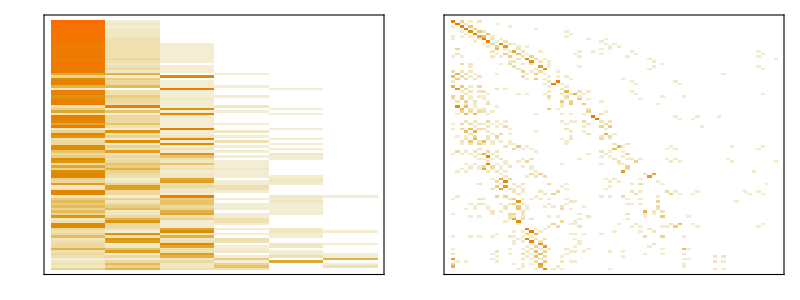

```mathematica
Grid@{
{
Show[H5FormatH2StatePercentPlot2[;;#],
FrameTicks->None, ImageSize->{Automatic, 5*#}],
Show[H5FormatSharedProtonStatePercentPlot2[;;#],
FrameTicks->None,ImageSize->{Automatic, 5*#}] }}&@Max@{Min@{#, 350}, 1}&@100
```

### 3D Contraction of 4D (10)

```mathematica
$H5Key={30, 25, Range[10]};
```

```mathematica
$H5Data[$H5Key, "SharedProtonPoints"]=$H5Key[[1]];
$H5Data[$H5Key, "SharedProtonBasisSize"]=$H5Data[$H5Key, "SharedProtonPoints"]^2;
$H5Data[$H5Key, "OuterH2Points"]=$H5Key[[2]];
$H5Data[$H5Key, "OuterH2States"]=$H5Key[[3]];
$H5Data[$H5Key, "OuterH2BasisSize"]=Length@$H5Data[$H5Key, "OuterH2States"];
$H5Data[$H5Key, "TotalBasisSize"]=$H5Data[$H5Key, "SharedProtonBasisSize"]*$H5Data[$H5Key, "OuterH2BasisSize"]
```

9000

#### T_R

```mathematica
$H5Data[$H5Key, "SharedProtonKineticEnergy"]=
$H5DVR["KineticEnergy",
 "Points"->
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

#### h_r

H_2 wavefunctions are computed for the equilibrium value of (a, s)

```mathematica
$H5Data[$H5Key, "OuterH2Wavefunctions"]=
$H2DVR[
Return->{"Grid", "Wavefunctions"},
"Points"->{250, 250},
"PotentialOptimizationOptions"->
{
"PotentialFunction"->h2SinglePot,
"OptimizedBasisSize"->$H5Data[$H5Key, "OuterH2Points"]
},
"NumberOfWavefunctions"->$H5Data[$H5Key, "OuterH2Points"]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2Hamiltonian"]=
SparseArray[
Band[{1, 1}]->
$H5Data[$H5Key, "OuterH2Wavefunctions"][[
"Wavefunctions", 1, $H5Data[$H5Key, "OuterH2States"]
]]
];
```

#### V

```mathematica
$H5Data[$H5Key, "SharedProtonGrid"]=
$H5DVR["Grid", 
"Points"->{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

```mathematica
$H5Data[$H5Key, "OuterH2Grid"]=
Flatten[
$H5Data[$H5Key, "OuterH2Wavefunctions"]["Grid"],
 1
];
```

```mathematica
$H5Data[$H5Key, "OuterH2GridPotential"]=
h2PotVec@$H5Data[$H5Key, "OuterH2Grid"];
```

```mathematica
(*H5OuterH2PotVector//Clear*)
H5OuterH2PotVector[key_][i_,j_]:=
H5OuterH2PotVector[key][i,j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
H5FullVecPot@
Join[
ConstantArray[gp, $H5Data[key, "OuterH2Points"]^2],
$H5Data[key, "OuterH2Grid"],
2
],
ConstantArray[10^9, $H5Data[$H5Key, "OuterH2Points"]^2]
]-$H5Data[key, "OuterH2GridPotential"]
]
```

```mathematica
(*Clear[H5OuterH2PotBlock]*)
H5OuterH2PotBlock[key_][i_, j_]:=
H5OuterH2PotBlock[key][i, j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[i==1&&j==1||
dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
$H2DVR["OperatorMatrix",
H5OuterH2PotVector[key][i, j]&,
"Grid"->$H5Data[key, "OuterH2Wavefunctions"]["Grid"],
"Wavefunctions"->Hold@$H5Data[key, "OuterH2Wavefunctions"]["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
H5OuterH2PotBlock[key][1, 1]
]
]
```

```mathematica
$H5Data[$H5Key, "PotentialBlocks"]=
Flatten[
Array[H5OuterH2PotBlock[$H5Key], 
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
], 
1
];
```

```mathematica
ddd=$H5Data[$H5Key, "PotentialBlocks"]//DeleteDuplicates;
```

```mathematica
$H5Data[$H5Key, "PotentialEnergy"]=
SparseArray[
Band[{1,1}]->$H5Data[$H5Key, "PotentialBlocks"]
];
```

#### Full Kinetic Energy

```mathematica
$H5Data[$H5Key, "KineticEnergy"]=
KroneckerProduct[
$H5Data[$H5Key, "SharedProtonKineticEnergy"],
IdentityMatrix[$H5Data[$H5Key, "OuterH2BasisSize"], SparseArray]
]+
KroneckerProduct[
IdentityMatrix[$H5Data[$H5Key, "SharedProtonBasisSize"], SparseArray],
$H5Data[$H5Key, "OuterH2Hamiltonian"]
];
```

#### Energies and Wavefunctions

I just use one of the DVRs as a wrapper to access its eigenvalues/vectors routine

```mathematica
$H5Data[$H5Key, "Eigensystem"]=
$H2DVR["Wavefunctions", 
"KineticEnergy"->Hold@$H5Data[$H5Key, "KineticEnergy"],
"PotentialEnergy"->Hold@$H5Data[$H5Key, "PotentialEnergy"],
Method->"Direct", 
"NumberOfWavefunctions"->350(* This will die on some of these huge matrices... *)
(*"NumberOfWavefunctions"->250,
"ArnoldiIterations"->10000*)
];//AbsoluteTiming
```

{692.892,Null}

```mathematica
{$H5Data[$H5Key, "Energies"], $H5Data[$H5Key, "Wavefunctions"]}=$H5Data[$H5Key, "Eigensystem"];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/wavefunctions@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Eigensystem"]
]
```

~/Documents/UW/Research/H5+/results/wavefunctions@{30, 25, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10}}.mx

```mathematica
(*{$H5Data[$H5Key, "Energies"], $H5Data[$H5Key, "Wavefunctions"]}=Import["~/Documents/UW/Research/H5+/results/wavefunctions@{30, 25, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10}}.mx"];*)
```

##### Frequencies

```mathematica
$H5Data[$H5Key, "Frequencies"]=
Rest[#-#[[1]]]&@$H5Data[$H5Key, "Energies"];
$H5Data[$H5Key, "Frequencies"]~Take~100
```

{442.569,728.832,1118.07,1292.53,1627.09,1720.44,1928.72,1988.63,2313.72,2349.16,2635.63,2646.84,2695.17,2882.49,2937.78,2975.94,3071.02,3223.2,3247.91,3375.43,3408.67,3461.77,3468.43,3623.28,3624.02,3805.4,3880.81,3983.61,4068.53,4084.57,4109.54,4137.49,4163.03,4224.37,4275.02,4514.43,4563.4,4628.89,4668.18,4683.03,4700.47,4751.98,4757.2,4850.62,4941.28,4977.87,5085.36,5116.52,5156.19,5156.74,5181.85,5247.04,5349.11,5377.99,5461.8,5463.65,5478.07,5499.72,5684.56,5696.2,5731.45,5753.78,5773.94,5779.74,5846.65,5892.72,5911.03,6054.,6071.39,6107.89,6109.12,6113.54,6158.49,6229.11,6250.55,6261.77,6365.36,6372.77,6381.48,6416.19,6460.07,6463.66,6466.92,6492.52,6524.15,6553.72,6564.73,6654.15,6667.66,6696.14,6761.87,6797.43,6813.44,6829.59,6836.54,6864.25,6885.53,6942.27,6952.94,6968.54}

##### Slices

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
Sign[ur.#]*Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
nr
]
];
```

#### Spectrum

##### Transition Moments

```mathematica
$H5Data[$H5Key, "SharedProtonGrid"]=
$H5DVR["Grid", "Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]}];
```

Helper to extract the grid to be use to compute the dipole surface elements. Effectively just the surface parametrized in (a, s)

```mathematica
H5OuterH2DipoleGrid[key_][i_, j_]:=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=$H5DipoleSurfaceInterps[[1, 1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
Join[
ConstantArray[gp, $H5Data[key, "OuterH2Points"]^2],
$H5Data[key, "OuterH2Grid"],
2
],
$Failed
]
]
```

```mathematica
(*computeDipVecs//Clear*)
H5OuterH2DipoleVector[key_][i_,j_]:=
H5OuterH2DipoleVector[key][i,j]=
With[{gr=H5OuterH2DipoleGrid[key][i, j]},
If[gr===$Failed,
ConstantArray[{0., 0., 0.}, $H5Data[key, "OuterH2Points"]^2],
$H5DipoleSurfaceVec@gr//Through//Transpose
]
]
```

This computes a term in the transition matrix defined by m_rμn_r for a given (a, s)

```mathematica
(*Clear[H5OuterH2TransitionMatrix]*)
H5OuterH2TransitionMatrix[key_][i_, j_]:=
H5OuterH2TransitionMatrix[key][i, j]=
With[{dip=H5OuterH2DipoleVector[key][i, j]},
If[Norm[Flatten[dip]]>0,
$H2DVR[
"OperatorMatrix",
(dip&),
"Grid"->$H5Data[key, "OuterH2Wavefunctions"]["Grid"],
"Wavefunctions"->$H5Data[key, "OuterH2Wavefunctions"]["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
$Failed
]
]
```

Computing these for each (R_1, R_2):

```mathematica
$H5Data[$H5Key, "OuterH2TransitionMoments"]=
Array[H5OuterH2TransitionMatrix[$H5Key], 
{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]}];
```

Then we slice up the coefficients:

```mathematica
$H5Data[$H5Key, "SharedProtonCoefficientVectors"]=
With[
{
wfns=$H5Data[$H5Key, "Wavefunctions"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
nr=$H5Data[$H5Key, "OuterH2BasisSize"]
},
Partition[
Array[
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]], 
ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Developer`ToPackedArray@
Map[
(*Sign[#.ur]**)#&,
wfs
]
]&,
NR^2
],
NR
]
];
```

Then we compute the transition moment vector over the (s, a) coordinates

```mathematica
H5SharedProtonTransitionMoment//Clear
H5SharedProtonTransitionMoment[key_][i_]:=
H5SharedProtonTransitionMoment[key][i]=
With[
{
coeffs=
Flatten[$H5Data[key, "SharedProtonCoefficientVectors"][[All, All, {i, 1}]], 1],
momsArr=
Flatten[$H5Data[key, "OuterH2TransitionMoments"], 1]
},
MapThread[
If[#2===$Failed,
0,
#[[1]].#2[[All,All, 1]].#[[2]]
]&,
{
coeffs,
momsArr
}
]
]
```

Check some phase stuff

```mathematica
(*Manipulate[
MapThread[Append, 
{
Flatten[$H5Data[$H5Key, "SharedProtonGrid"], 1],
H5SharedProtonTransitionMoment[$H5Key][i]
}
]//ListPlot3D[#, 
PlotRange->{{-1.5, 1.5}, {1.2, 2}, All},
 ColorFunction->"Rainbow", PerformanceGoal->"Quality"
]&,
{i, 1, Length@$H5Data[$H5Key, "Energies"], 1, AnimationRate->.5}
]*)
```

Norm and square to get raw intensity:

```mathematica
$H5Data[$H5Key, "Intensities"]=
Array[Total[H5SharedProtonTransitionMoment[$H5Key][#]]^2&, Length@$H5Data[$H5Key, "Energies"]];
```

##### Plots

```mathematica
$H5Data[$H5Key, "Spectrum"]=Thread[{Prepend[$H5Data[$H5Key, "Frequencies"], 0], $H5Data[$H5Key, "Intensities"]}];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/spectrum@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Spectrum"]
]
```

~/Documents/UW/Research/H5+/results/spectrum@{30, 25, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10}}.mx

```mathematica
(*$H5Data[$H5Key, "Spectrum"]=Import["~/Documents/UW/Research/H5+/results/spectrum@{30, 25, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10}}.mx"];*)
```

```mathematica
(*$H5Data[$H5Key, "Frequencies"]=Rest@$H5Data[$H5Key, "Spectrum"][[All, 1]];*)
```

```mathematica
(*$H5Data[$H5Key, "Intensities"]=$H5Data[$H5Key, "Spectrum"][[All, 2]];*)
```

```mathematica
$H5Data[$H5Key, "TargetShift"]=989-MaximalBy[#, Last, 2][[2, 1]]&@H5SpecPrep@$H5Data[$H5Key, "Spectrum"];
$H5Data[$H5Key, "TargetScaling"]= 
(6684-4911)/(#[[2]]-#[[1]])&@
Sort@
MaximalBy[
H5SpecPrep[$H5Data[$H5Key, "Spectrum"],{4800, 7500}, Offset@$H5Data[$H5Key, "TargetShift"]],
Last,
2
][[All, 1]];
```

```mathematica
Manipulate[
H5PlotSpec[
$H5Data[$H5Key, "Spectrum"],
 Offset[shift, Scaled[scale]],
.05
],
{{shift, $H5Data[$H5Key, "TargetShift"]}, 4400, -4400, 10},
{{scale, $H5Data[$H5Key, "TargetScaling"]}, .5, 2}
]
```

```mathematica
Manipulate[
H5PlotSpecLines[
$H5Data[$H5Key, "Spectrum"], 
range,
Offset[shift, Scaled[scale]],
cutoff,
PlotRange->{range, All}
],
{{shift, 0}, 4400, -4400},
{{scale, 1}, .5, 1.5},
{{range, {4500, 7500}}, 0, 10000, ControlType->IntervalSlider},
{{cutoff, .05}, 0.000001, .1}
]
```

```mathematica
Manipulate[
H5SpecGaussianBroadenedSpectrum[
$H5Data[$H5Key, "Spectrum"], 
σ,
range,
Offset[shift, Scaled[scale]],
cutoff,
PlotRange->{range, All}
],
{{shift, 0}, 4400, -4400},
{{scale, 1}, .5, 1.5},
{{range, {4500, 7500}}, 0, 10000, ControlType->IntervalSlider},
{{σ, 25}, 1, 50, 1},
{{cutoff, .05}, 0.000001, .1}
]
```

#### State Assignments

##### Slices

Slice the wavefunctions to start:

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
(*Sign[ur.#]**)Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
nr
]
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctionsUnnormalized"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
(*(*Sign[ur.#]**)#&/@*)wfs//Developer`ToPackedArray
]&,
nr
]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]],
 ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Map[
(*Sign[#.ur]**)#&,
wfs
]
]&,
NR^2
]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2SliceWavefunctions"]=
With[
{
basis=
$H5Data[$H5Key, "OuterH2Wavefunctions"][[
"Wavefunctions",
 2,
$H5Data[$H5Key, "OuterH2States"]
]],
coeffs=Transpose@$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]
},
Map[
Map[Total[#*basis]&],
coeffs
]
];
```

##### H2 Vectors

```mathematica
$H5Data[$H5Key, "OuterH2StateVectors"]=$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]//Transpose//Map[Normalize@*Total];
```

##### SP Vectors

For the shared-proton we’ll compute the overlap with the equilibrium calculation:

```mathematica
$H5Data[$H5Key, "SharedProtonStates"]=25;
```

```mathematica
$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]=
$H5DVR["Wavefunctions", 
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"NumberOfWavefunctions"->$H5Data[$H5Key, "SharedProtonStates"]
];
```

```mathematica
$H5DVR[ 
"Wavefunctions"->$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"],
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"NumberOfWavefunctions"->$H5Data[$H5Key, "SharedProtonStates"],
"WavefunctionSelection"->5
]
```

```mathematica
$H5Data[$H5Key, "SharedProtonStateCoefficients"]=
Table[
Transpose@$H5DVR[
"ExpectationValues",
Function[
{X, ψ},
#
]&/@wfns,
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"Wavefunctions"->$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]
],
{wfns, $H5Data[$H5Key, "SharedProtonSliceWavefunctions"]}
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonStateVectors"]=
$H5Data[$H5Key, "SharedProtonStateCoefficients"]//Transpose//Map[Normalize@*Total];
```

##### Tables

```mathematica
$iH5FormatStatePercentTableRelativeIntensities=True;
```

```mathematica
iH5FormatStatePercentTable[vecs_, headers_, states_, ops:OptionsPattern[]]:=
Grid[
Prepend[Join[{"𝒻", "ℐ"}, headers]]@
Join[
Round[List/@Prepend[$H5Data[$H5Key, "Frequencies"], 0][[states]], 1],
List/@
If[TrueQ@$iH5FormatStatePercentTableRelativeIntensities,
Map[
If[#<0.0001, ScientificForm[#, 2], Round[#, .01]]&,
100*#/Max[#]
]&,
Map[ScientificForm[#, 2]&]
]@$H5Data[$H5Key, "Intensities"][[states]],
100*
Round[
Power[
vecs,
2
], 
.01
],
2
],
ops,
Alignment->Left,
Dividers->{{3->Gray}, {2->Gray}},
ItemSize->Full
]//Style[#, ShowStringCharacters->False]&
```

```mathematica
H5FormatH2StatePercentTable[states_]:=
iH5FormatStatePercentTable[
$H5Data[$H5Key, "OuterH2StateVectors"][[states]],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
],
states
]
```

```mathematica
H5FormatH2StatePercentTable2[states_, saSpec_:All]:=
iH5FormatStatePercentTable[
Normalize@*Total/@
Transpose[
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]
][[states, saSpec]],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
],
states
]
```

```mathematica
H5FormatSharedProtonStatePercentTable[states_]:=
iH5FormatStatePercentTable[
$H5Data[$H5Key, "SharedProtonStateVectors"][[states]],
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[$H5Data[$H5Key, "SharedProtonStates"]]]]
],
states
]
```

```mathematica
H5FormatSharedProtonStatePercentTable[states_, h2Spec_]:=
iH5FormatStatePercentTable[
Normalize@*Total/@
Transpose[
$H5Data[$H5Key, "SharedProtonStateCoefficients"]
][[states, h2Spec]],
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[$H5Data[$H5Key, "SharedProtonStates"]]]]
],
states
]
```

```mathematica
H5FormatStatePercentTable[states_]:=
iH5FormatStatePercentTable[
Join[
$H5Data[$H5Key, "OuterH2StateVectors"][[states]],
$H5Data[$H5Key, "SharedProtonStateVectors"][[states]],
2
],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
]~Join~
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[$H5Data[$H5Key, "SharedProtonStates"]]]]
],
states,
Dividers->{{3, -10}->Gray//Thread, {2->Gray}}
]
```

##### Tests

```mathematica
H5PlotSpec[
$H5Data[$H5Key, "Spectrum"]
]
```

```mathematica
$H5Data[$H5Key, "Frequencies"]
```

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"][[;;3, singleH2Excitations]]//Transpose//Map[
Map[
ListPlot3D[Transpose@Partition[#, 30], ColorFunction->"Rainbow", PlotRange->All,
DataRange->{{-2.5, 2.5}, {.7, 3.7}}
]&
]
]//Grid
```

```mathematica
$H5DVR["Points"->{30, 30}, 
"PlotMode"->"Density",
"WavefunctionClipping"->None, "ShowPotential"->False,
ColorFunction->"Rainbow", ColorFunctionScaling->True,
"WavefunctionSelection"->5
]
```

```mathematica
H5FormatSharedProtonStatePercentTable[;;45]
```

𝒻 | ℐ | 1^(H+) | 2^(H+) | 3^(H+) | 4^(H+) | 5^(H+) | 6^(H+) | 7^(H+) | 8^(H+) | 9^(H+) | 10^(H+) | 11^(H+) | 12^(H+) | 13^(H+) | 14^(H+) | 15^(H+) | 16^(H+) | 17^(H+) | 18^(H+) | 19^(H+) | 20^(H+) | 21^(H+) | 22^(H+) | 23^(H+) | 24^(H+) | 25^(H+)
0 | 0. | 52. | 0. | 20. | 0. | 8. | 0. | 11. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 3. | 0. | 0.
443 | 100. | 0. | 63. | 0. | 15. | 0. | 2. | 0. | 0. | 1. | 0. | 13. | 6. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
729 | 0. | 5. | 0. | 38. | 0. | 38. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7. | 1. | 0. | 2. | 0. | 0. | 0. | 0. | 0. | 8. | 0. | 0.
1118 | 3.86 | 0. | 1. | 0. | 59. | 0. | 24. | 0. | 0. | 2. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 2. | 0. | 9. | 0. | 1. | 0. | 0. | 0.
1293 | 0. | 10. | 0. | 42. | 0. | 11. | 0. | 0. | 15. | 0. | 0. | 0. | 0. | 1. | 6. | 2. | 0. | 4. | 0. | 1. | 0. | 0. | 0. | 8. | 0. | 0.
1627 | 1.19 | 0. | 4. | 0. | 2. | 0. | 60. | 0. | 0. | 32. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
1720 | 2.7×10^-5 | 5. | 0. | 6. | 0. | 0. | 0. | 32. | 43. | 0. | 7. | 0. | 0. | 0. | 0. | 1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 3. | 0. | 1.
1929 | 0. | 9. | 0. | 1. | 0. | 0. | 0. | 2. | 64. | 0. | 19. | 0. | 0. | 3. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2. | 0. | 0.
1989 | 0.31 | 0. | 12. | 0. | 7. | 0. | 12. | 0. | 0. | 29. | 0. | 15. | 20. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 1. | 0. | 0. | 0.
2314 | 2.×10^-5 | 2. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 50. | 0. | 0. | 33. | 0. | 9. | 0. | 1. | 0. | 2. | 0. | 2. | 0. | 0. | 0. | 0.
2349 | 0.02 | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 30. | 49. | 0. | 0. | 0. | 10. | 0. | 6. | 0. | 0. | 0. | 2. | 0. | 0. | 0.
2636 | 0.04 | 0. | 59. | 0. | 2. | 0. | 0. | 0. | 0. | 0. | 0. | 13. | 6. | 0. | 0. | 0. | 17. | 0. | 1. | 0. | 1. | 0. | 1. | 0. | 1. | 0.
2647 | 7.1×10^-11 | 6. | 0. | 2. | 0. | 1. | 0. | 0. | 0. | 0. | 11. | 0. | 0. | 0. | 2. | 54. | 0. | 12. | 0. | 1. | 0. | 6. | 0. | 3. | 0. | 2.
2695 | 0.05 | 0. | 24. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 2. | 25. | 0. | 0. | 0. | 39. | 0. | 3. | 0. | 0. | 0. | 2. | 0. | 4. | 0.
2882 | 4.7×10^-5 | 14. | 0. | 8. | 0. | 2. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 6. | 10. | 7. | 0. | 7. | 0. | 39. | 0. | 5. | 0. | 0. | 0. | 0.
2938 | 0. | 0. | 2. | 0. | 6. | 0. | 4. | 0. | 0. | 4. | 0. | 1. | 6. | 0. | 0. | 0. | 27. | 0. | 38. | 0. | 6. | 1. | 2. | 0. | 2. | 1.
2976 | 6.7×10^-5 | 43. | 0. | 2. | 0. | 15. | 0. | 1. | 0. | 0. | 1. | 0. | 0. | 3. | 16. | 3. | 0. | 0. | 0. | 7. | 0. | 2. | 0. | 5. | 0. | 1.
3071 | 7.3×10^-5 | 12. | 0. | 23. | 0. | 27. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 17. | 0. | 15. | 0. | 2. | 0. | 0.
3223 | 0. | 0. | 0. | 0. | 4. | 0. | 2. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2. | 0. | 8. | 0. | 10. | 0. | 54. | 0. | 19. | 0.
3248 | 3.2×10^-5 | 3. | 0. | 2. | 0. | 1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 3. | 0. | 0. | 0. | 2. | 0. | 10. | 0. | 55. | 0. | 3. | 0. | 20.
3375 | 0. | 43. | 0. | 26. | 0. | 17. | 0. | 4. | 2. | 0. | 2. | 0. | 0. | 2. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 1. | 0. | 1.
3409 | 6.61 | 0. | 20. | 0. | 61. | 0. | 13. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 1. | 0. | 3. | 0. | 2. | 0.
3462 | 8.54 | 0. | 44. | 0. | 32. | 0. | 18. | 0. | 0. | 0. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 2. | 0.
3468 | 0. | 43. | 0. | 26. | 0. | 0. | 0. | 24. | 1. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 1. | 0. | 2.
3623 | 0. | 24. | 0. | 5. | 0. | 5. | 0. | 1. | 2. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 14. | 0. | 7. | 0. | 41.
3624 | 0.02 | 0. | 1. | 0. | 2. | 0. | 4. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 23. | 0. | 68. | 0.
3805 | 0.01 | 46. | 0. | 29. | 0. | 8. | 0. | 15. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3881 | 0.12 | 0. | 25. | 0. | 50. | 0. | 1. | 0. | 0. | 0. | 0. | 15. | 8. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3984 | 0. | 17. | 0. | 42. | 0. | 30. | 0. | 1. | 2. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8. | 0. | 0.
4069 | 0. | 0. | 10. | 0. | 14. | 0. | 12. | 0. | 0. | 35. | 0. | 4. | 2. | 0. | 0. | 0. | 10. | 0. | 4. | 0. | 0. | 0. | 4. | 0. | 6. | 0.
4085 | 0.01 | 41. | 0. | 35. | 0. | 20. | 0. | 0. | 2. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
4110 | 0. | 38. | 0. | 28. | 0. | 15. | 0. | 4. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 3. | 0. | 5. | 0. | 1. | 0. | 3. | 0. | 0. | 0. | 1.
4137 | 0. | 0. | 0. | 0. | 0. | 0. | 45. | 0. | 0. | 41. | 0. | 5. | 0. | 0. | 0. | 0. | 4. | 0. | 1. | 0. | 1. | 0. | 0. | 0. | 1. | 0.
4163 | 0.04 | 0. | 52. | 0. | 36. | 0. | 0. | 0. | 0. | 0. | 0. | 6. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
4224 | 5.4×10^-5 | 5. | 0. | 72. | 0. | 19. | 0. | 1. | 1. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4275 | 0.02 | 0. | 7. | 0. | 63. | 0. | 13. | 0. | 0. | 10. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 2. | 0. | 0. | 0. | 2. | 0.
4514 | 0.01 | 24. | 0. | 7. | 0. | 9. | 0. | 21. | 24. | 0. | 3. | 0. | 0. | 1. | 3. | 3. | 0. | 4. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0.
4563 | 0.03 | 0. | 0. | 0. | 22. | 0. | 29. | 0. | 0. | 0. | 0. | 9. | 12. | 0. | 0. | 0. | 1. | 0. | 4. | 0. | 20. | 0. | 3. | 0. | 1. | 0.
4629 | 0.01 | 11. | 0. | 3. | 0. | 26. | 0. | 17. | 13. | 0. | 23. | 0. | 0. | 3. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
4668 | 0. | 0. | 1. | 0. | 35. | 0. | 21. | 0. | 0. | 16. | 0. | 7. | 16. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0.
4683 | 0. | 12. | 0. | 4. | 0. | 19. | 0. | 17. | 0. | 0. | 2. | 0. | 0. | 0. | 0. | 1. | 0. | 4. | 0. | 6. | 0. | 27. | 0. | 2. | 1. | 6.
4700 | 0.01 | 0. | 0. | 0. | 26. | 0. | 11. | 0. | 0. | 32. | 0. | 11. | 15. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 1. | 0. | 2. | 0. | 0. | 0.
4752 | 0.06 | 0. | 1. | 0. | 47. | 0. | 47. | 0. | 0. | 1. | 0. | 2. | 2. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4757 | 0.01 | 13. | 0. | 12. | 0. | 32. | 0. | 20. | 11. | 0. | 0. | 0. | 0. | 0. | 3. | 0. | 0. | 3. | 0. | 1. | 0. | 1. | 0. | 3. | 0. | 0.
4851 | 0. | 14. | 0. | 8. | 0. | 14. | 0. | 1. | 3. | 0. | 16. | 0. | 0. | 13. | 0. | 11. | 0. | 6. | 0. | 0. | 0. | 1. | 0. | 12. | 0. | 0.

```mathematica
$testStates={24, 27, 29, 36, 37};
```

```mathematica
H5FormatH2StatePercentTable[;;45]
```

```mathematica
H5FormatH2StatePercentTable[20;;40]
```

𝒻 | ℐ | (0,0)^H_2 | (0,1-1,0)^H_2 | (0,1+1,0)^H_2 | (0,2-2,0)^H_2 | (1,1∠45)^H_2 | (0,2+2,0)^H_2 | (0,3-3,0)^H_2 | (1,2-2,1)^H_2 | (1,2+2,1)^H_2 | (0,3+3,0)^H_2
3248 | 100. | 78. | 17. | 3. | 2. | 0. | 0. | 0. | 0. | 0. | 0.
3375 | 100. | 48. | 18. | 29. | 3. | 1. | 0. | 0. | 0. | 0. | 0.
3409 | 100. | 30. | 62. | 3. | 5. | 0. | 0. | 0. | 0. | 0. | 0.
3462 | 100. | 18. | 72. | 3. | 6. | 1. | 0. | 0. | 0. | 0. | 0.
3468 | 100. | 17. | 5. | 77. | 1. | 1. | 0. | 0. | 0. | 0. | 0.
3623 | 100. | 73. | 19. | 5. | 2. | 0. | 0. | 0. | 0. | 0. | 0.
3624 | 100. | 72. | 21. | 4. | 3. | 1. | 0. | 0. | 0. | 0. | 0.
3805 | 100. | 9. | 55. | 16. | 15. | 4. | 0. | 1. | 0. | 0. | 0.
3881 | 100. | 0. | 0. | 94. | 0. | 5. | 1. | 0. | 0. | 0. | 0.
3984 | 100. | 56. | 24. | 11. | 5. | 3. | 0. | 0. | 0. | 0. | 0.
4069 | 100. | 65. | 23. | 7. | 4. | 1. | 0. | 0. | 0. | 0. | 0.
4085 | 100. | 52. | 37. | 6. | 5. | 0. | 0. | 0. | 0. | 0. | 0.
4110 | 100. | 69. | 17. | 11. | 2. | 1. | 0. | 0. | 0. | 0. | 0.
4137 | 100. | 68. | 22. | 6. | 3. | 1. | 0. | 0. | 0. | 0. | 0.
4163 | 100. | 0. | 82. | 2. | 14. | 1. | 0. | 1. | 0. | 0. | 0.
4224 | 100. | 1. | 3. | 90. | 1. | 5. | 0. | 0. | 0. | 0. | 0.
4275 | 100. | 72. | 18. | 8. | 1. | 1. | 0. | 0. | 0. | 0. | 0.
4514 | 100. | 25. | 45. | 13. | 11. | 4. | 0. | 1. | 0. | 0. | 0.
4563 | 100. | 2. | 2. | 88. | 1. | 7. | 0. | 0. | 0. | 0. | 0.
4629 | 100. | 16. | 56. | 9. | 14. | 4. | 0. | 1. | 0. | 0. | 0.
4668 | 100. | 60. | 24. | 9. | 4. | 2. | 0. | 0. | 0. | 0. | 0.

```mathematica
H5FormatSharedProtonStatePercentTable[81;;95]
```

𝒻 | ℐ | 1^(H+) | 2^(H+) | 3^(H+) | 4^(H+) | 5^(H+) | 6^(H+) | 7^(H+) | 8^(H+) | 9^(H+) | 10^(H+) | 11^(H+) | 12^(H+) | 13^(H+) | 14^(H+) | 15^(H+) | 16^(H+) | 17^(H+) | 18^(H+) | 19^(H+) | 20^(H+) | 21^(H+) | 22^(H+) | 23^(H+) | 24^(H+) | 25^(H+)
6385 | 0.01 | 0. | 1. | 0. | 1. | 0. | 5. | 0. | 0. | 7. | 0. | 2. | 1. | 0. | 0. | 0. | 2. | 0. | 46. | 0. | 16. | 0. | 12. | 0. | 7. | 0.
6434 | 67.92 | 62. | 0. | 22. | 0. | 5. | 0. | 0. | 1. | 0. | 1. | 0. | 0. | 0. | 0. | 1. | 0. | 3. | 0. | 3. | 0. | 1. | 0. | 0. | 0. | 0.
6461 | 0.29 | 48. | 0. | 25. | 0. | 6. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 2. | 8. | 1. | 0. | 0. | 0. | 2. | 0. | 5. | 0. | 1. | 0. | 1.
6462 | 0.03 | 0. | 4. | 0. | 2. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 4. | 0. | 0. | 0. | 0. | 0. | 14. | 0. | 3. | 0. | 39. | 0. | 33. | 0.
6511 | 11.99 | 82. | 0. | 12. | 0. | 2. | 0. | 1. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
6528 | 51.14 | 65. | 0. | 4. | 0. | 16. | 0. | 0. | 2. | 0. | 2. | 0. | 0. | 5. | 1. | 0. | 0. | 1. | 0. | 3. | 0. | 1. | 0. | 0. | 0. | 0.
6545 | 0.09 | 0. | 0. | 0. | 1. | 0. | 4. | 0. | 0. | 5. | 0. | 2. | 19. | 0. | 0. | 0. | 11. | 0. | 17. | 0. | 30. | 0. | 1. | 0. | 11. | 0.
6592 | 2.87 | 17. | 0. | 1. | 0. | 12. | 0. | 6. | 2. | 0. | 10. | 0. | 0. | 21. | 6. | 1. | 0. | 0. | 0. | 14. | 0. | 7. | 0. | 0. | 0. | 2.
6646 | 0.04 | 9. | 0. | 6. | 0. | 5. | 0. | 0. | 1. | 0. | 30. | 0. | 0. | 31. | 8. | 4. | 0. | 1. | 0. | 2. | 0. | 0. | 0. | 0. | 0. | 3.
6651 | 1.3 | 0. | 0. | 0. | 7. | 0. | 2. | 0. | 0. | 2. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 21. | 0. | 0. | 0. | 48. | 0. | 18. | 0.
6693 | 0.77 | 50. | 0. | 0. | 0. | 21. | 0. | 15. | 0. | 0. | 0. | 0. | 0. | 2. | 2. | 1. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 4. | 0. | 1.
6721 | 62.5 | 0. | 16. | 0. | 78. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 2. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
6726 | 100. | 51. | 0. | 8. | 0. | 14. | 0. | 9. | 1. | 0. | 1. | 0. | 0. | 3. | 7. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5. | 0. | 0.
6814 | 8.37 | 54. | 0. | 3. | 0. | 11. | 0. | 2. | 1. | 0. | 2. | 0. | 0. | 11. | 7. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 4. | 0. | 1.
6828 | 11.65 | 0. | 2. | 0. | 8. | 0. | 4. | 0. | 0. | 7. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 5. | 0. | 59. | 0. | 11. | 0.

```mathematica
H5FormatH2StatePercentTable[81;;105]
```

𝒻 | ℐ | (0,0)^H_2 | (0,1-1,0)^H_2 | (0,1+1,0)^H_2 | (0,2-2,0)^H_2 | (1,1∠45)^H_2 | (0,2+2,0)^H_2 | (0,3-3,0)^H_2 | (1,2-2,1)^H_2 | (1,2+2,1)^H_2 | (0,3+3,0)^H_2
6385 | 0.01 | 1. | 16. | 59. | 13. | 8. | 0. | 2. | 0. | 0. | 0.
6434 | 67.92 | 1. | 2. | 94. | 0. | 2. | 0. | 0. | 0. | 0. | 0.
6461 | 0.29 | 44. | 28. | 15. | 9. | 3. | 0. | 1. | 0. | 0. | 0.
6462 | 0.03 | 39. | 29. | 15. | 10. | 4. | 0. | 1. | 0. | 0. | 0.
6511 | 11.99 | 0. | 10. | 88. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
6528 | 51.14 | 13. | 1. | 82. | 1. | 1. | 0. | 1. | 0. | 0. | 0.
6545 | 0.09 | 7. | 19. | 51. | 16. | 4. | 0. | 2. | 0. | 0. | 0.
6592 | 2.87 | 4. | 0. | 90. | 0. | 5. | 0. | 0. | 0. | 0. | 0.
6646 | 0.04 | 0. | 28. | 52. | 13. | 4. | 0. | 2. | 0. | 0. | 0.
6651 | 1.3 | 3. | 14. | 59. | 13. | 8. | 0. | 2. | 0. | 0. | 0.
6693 | 0.77 | 0. | 6. | 74. | 12. | 5. | 0. | 2. | 0. | 0. | 0.
6721 | 62.5 | 4. | 0. | 83. | 9. | 1. | 0. | 2. | 0. | 0. | 0.
6726 | 100. | 26. | 0. | 52. | 12. | 5. | 1. | 3. | 1. | 0. | 0.
6814 | 8.37 | 5. | 0. | 84. | 4. | 6. | 0. | 1. | 0. | 0. | 0.
6828 | 11.65 | 7. | 15. | 56. | 15. | 4. | 0. | 2. | 0. | 0. | 0.
6861 | 11.25 | 17. | 11. | 57. | 11. | 3. | 0. | 2. | 0. | 0. | 0.
6906 | 97.38 | 0. | 1. | 93. | 4. | 1. | 0. | 0. | 0. | 0. | 0.
6937 | 87.59 | 1. | 4. | 89. | 1. | 4. | 0. | 0. | 0. | 0. | 0.
6952 | 10.59 | 5. | 22. | 45. | 20. | 6. | 1. | 2. | 0. | 0. | 0.
6968 | 40.17 | 1. | 1. | 87. | 1. | 2. | 9. | 0. | 0. | 0. | 0.
6977 | 0.11 | 0. | 23. | 49. | 13. | 12. | 0. | 2. | 0. | 0. | 0.
6993 | 5.1 | 0. | 1. | 35. | 23. | 38. | 0. | 2. | 2. | 0. | 0.
7014 | 54.35 | 9. | 28. | 55. | 6. | 1. | 0. | 1. | 0. | 0. | 0.
7040 | 0.13 | 0. | 23. | 55. | 14. | 5. | 0. | 2. | 0. | 0. | 0.
7073 | 0. | 61. | 24. | 7. | 6. | 1. | 0. | 1. | 0. | 0. | 0.

```mathematica
H5FormatH2StatePercentTable[Ordering[$H5Data[$H5Key, "Intensities"], -15]//Sort]
```

𝒻 | ℐ | (0,0)^H_2 | (0,1-1,0)^H_2 | (0,1+1,0)^H_2 | (0,2-2,0)^H_2 | (1,1∠45)^H_2 | (0,2+2,0)^H_2 | (0,3-3,0)^H_2 | (1,2-2,1)^H_2 | (1,2+2,1)^H_2 | (0,3+3,0)^H_2
448 | 100. | 91. | 8. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1124 | 4.23 | 89. | 10. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
1635 | 1.28 | 87. | 12. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
1995 | 0.38 | 86. | 12. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
2640 | 0.22 | 86. | 12. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
3495 | 0.24 | 1. | 64. | 31. | 3. | 2. | 0. | 0. | 0. | 0. | 0.
3823 | 1.67 | 1. | 15. | 83. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
3965 | 1.38 | 0. | 20. | 76. | 1. | 2. | 0. | 0. | 0. | 0. | 0.
4549 | 0.34 | 3. | 0. | 96. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
4662 | 0.31 | 15. | 4. | 80. | 1. | 1. | 0. | 0. | 0. | 0. | 0.
4989 | 0.22 | 62. | 11. | 22. | 4. | 0. | 0. | 0. | 0. | 0. | 0.
5612 | 0.11 | 52. | 4. | 41. | 2. | 0. | 0. | 0. | 0. | 0. | 0.
6203 | 0.2 | 12. | 35. | 50. | 1. | 2. | 0. | 0. | 0. | 0. | 0.
7196 | 0.18 | 3. | 4. | 88. | 0. | 1. | 4. | 0. | 0. | 0. | 0.
7546 | 0.15 | 0. | 2. | 7. | 32. | 44. | 3. | 6. | 6. | 0. | 0.

### 3D Contraction of 4D (60, 10)

```mathematica
$H5Key={60, 25, Range[10]};
```

```mathematica
$H5Data[$H5Key, "SharedProtonPoints"]=$H5Key[[1]];
$H5Data[$H5Key, "SharedProtonBasisSize"]=$H5Data[$H5Key, "SharedProtonPoints"]^2;
$H5Data[$H5Key, "OuterH2Points"]=$H5Key[[2]];
$H5Data[$H5Key, "OuterH2States"]=$H5Key[[3]];
$H5Data[$H5Key, "OuterH2BasisSize"]=Length@$H5Data[$H5Key, "OuterH2States"];
$H5Data[$H5Key, "TotalBasisSize"]=$H5Data[$H5Key, "SharedProtonBasisSize"]*$H5Data[$H5Key, "OuterH2BasisSize"]
```

36000

#### T_R

```mathematica
$H5Data[$H5Key, "SharedProtonKineticEnergy"]=
$H5DVR["KineticEnergy",
 "Points"->
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

#### h_r

H_2 wavefunctions are computed for the equilibrium value of (a, s)

```mathematica
$H5Data[$H5Key, "OuterH2Wavefunctions"]=
$H2DVR[
Return->{"Grid", "Wavefunctions"},
"Points"->{250, 250},
"PotentialOptimizationOptions"->
{
"PotentialFunction"->h2SinglePot,
"OptimizedBasisSize"->$H5Data[$H5Key, "OuterH2Points"]
},
"NumberOfWavefunctions"->$H5Data[$H5Key, "OuterH2Points"]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2Hamiltonian"]=
SparseArray[
Band[{1, 1}]->
$H5Data[$H5Key, "OuterH2Wavefunctions"][[
"Wavefunctions", 1, $H5Data[$H5Key, "OuterH2States"]
]]
];
```

#### V

```mathematica
$H5Data[$H5Key, "SharedProtonGrid"]=
$H5DVR["Grid", 
"Points"->{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

```mathematica
$H5Data[$H5Key, "OuterH2Grid"]=
Flatten[
$H5Data[$H5Key, "OuterH2Wavefunctions"]["Grid"],
 1
];
```

```mathematica
$H5Data[$H5Key, "OuterH2GridPotential"]=
h2PotVec@$H5Data[$H5Key, "OuterH2Grid"];
```

```mathematica
(*H5OuterH2PotVector//Clear*)
H5OuterH2PotVector[key_][i_,j_]:=
H5OuterH2PotVector[key][i,j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
H5FullVecPot@
Join[
ConstantArray[gp, $H5Data[$H5Key, "OuterH2Points"]^2],
$H5Data[$H5Key, "OuterH2Grid"],
2
],
ConstantArray[10^9, $H5Data[$H5Key, "OuterH2Points"]^2]
]-$H5Data[$H5Key, "OuterH2GridPotential"]
]
```

```mathematica
(*Clear[H5OuterH2PotBlock]*)
H5OuterH2PotBlock[key_][i_, j_]:=
H5OuterH2PotBlock[key][i, j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[i==1&&j==1||
dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
$H2DVR["OperatorMatrix",
H5OuterH2PotVector[key][i, j]&,
"Grid"->$H5Data[key, "OuterH2Wavefunctions"]["Grid"],
"Wavefunctions"->Hold@$H5Data[key, "OuterH2Wavefunctions"]["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
H5OuterH2PotBlock[key][1, 1]
]
]
```

```mathematica
$H5Data[$H5Key, "PotentialBlocks"]=
Flatten[
Array[H5OuterH2PotBlock[$H5Key], 
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]}
], 
1
];
```

```mathematica
$H5Data[$H5Key, "PotentialEnergy"]=
SparseArray[
Band[{1,1}]->$H5Data[$H5Key, "PotentialBlocks"]
];
```

#### Full Kinetic Energy

```mathematica
$H5Data[$H5Key, "KineticEnergy"]=
KroneckerProduct[
$H5Data[$H5Key, "SharedProtonKineticEnergy"],
IdentityMatrix[$H5Data[$H5Key, "OuterH2BasisSize"], SparseArray]
]+
KroneckerProduct[
IdentityMatrix[$H5Data[$H5Key, "SharedProtonBasisSize"], SparseArray],
$H5Data[$H5Key, "OuterH2Hamiltonian"]
];
```

#### Energies and Wavefunctions

I just use one of the DVRs as a wrapper to access its eigenvalues/vectors routine

```mathematica
$H5Data[$H5Key, "Eigensystem"]=
$H2DVR["Wavefunctions", 
"KineticEnergy"->Hold@$H5Data[$H5Key, "KineticEnergy"],
"PotentialEnergy"->Hold@$H5Data[$H5Key, "PotentialEnergy"],
Method->"Direct", 
"NumberOfWavefunctions"->350(* This will die on some of these huge matrices... *)
(*"NumberOfWavefunctions"->250,
"ArnoldiIterations"->10000*)
];//AbsoluteTiming
```

ChemTools::DVRRun: The kinetic energy is not a square numerical matrix

{0.205283,Null}

```mathematica
{$H5Data[$H5Key, "Energies"], $H5Data[$H5Key, "Wavefunctions"]}=$H5Data[$H5Key, "Eigensystem"];
```

Set::shape: Lists {$H5Data[$H5Key,Energies],$H5Data[$H5Key,Wavefunctions]} and $H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},Eigensystem] are not the same shape.

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/wavefunctions@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Eigensystem"]
]
```

~/Documents/UW/Research/H5+/results/wavefunctions@{30, 25, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10}}.mx

##### Frequencies

```mathematica
$H5Data[$H5Key, "Frequencies"]=
Rest[#-#[[1]]]&@$H5Data[$H5Key, "Energies"];
$H5Data[$H5Key, "Frequencies"]~Take~100
```

{448.358,730.806,1124.39,1294.64,1635.,1722.17,1930.68,1995.18,2316.04,2353.23,2640.23,2648.75,2698.32,2878.99,2940.79,2969.8,3073.17,3226.43,3250.51,3348.89,3432.76,3467.43,3495.4,3626.07,3628.21,3822.67,3919.03,3964.53,3996.03,4072.01,4108.49,4142.29,4221.07,4236.64,4243.58,4549.47,4565.25,4662.15,4671.84,4680.04,4693.67,4708.47,4813.72,4840.53,4957.99,4988.65,5120.68,5121.45,5160.79,5171.21,5188.97,5236.3,5310.14,5424.41,5450.3,5462.85,5469.08,5542.91,5603.91,5612.45,5732.56,5743.58,5778.1,5778.5,5887.52,5907.07,5924.38,6069.66,6089.5,6103.44,6111.53,6115.81,6202.52,6236.25,6260.45,6271.14,6279.57,6349.66,6375.84,6384.59,6433.6,6461.48,6462.36,6511.19,6528.42,6545.28,6592.11,6646.23,6651.17,6693.12,6720.57,6726.48,6814.28,6827.86,6861.13,6905.64,6936.81,6951.75,6967.95,6977.12}

##### Slices

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
Sign[ur.#]*Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
nr
]
];
```

#### Spectrum

##### Transition Moments

```mathematica
$H5Data[$H5Key, "SharedProtonGrid"]=
$H5DVR["Grid", "Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]}];
```

Helper to extract the grid to be use to compute the dipole surface elements. Effectively just the surface parametrized in (a, s)

```mathematica
H5OuterH2DipoleGrid[key_][i_, j_]:=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=$H5DipoleSurfaceInterps[[1, 1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
Join[
ConstantArray[gp, $H5Data[key, "OuterH2Points"]^2],
$H5Data[key, "OuterH2Grid"],
2
],
$Failed
]
]
```

```mathematica
(*computeDipVecs//Clear*)
H5OuterH2DipoleVector[key_][i_,j_]:=
H5OuterH2DipoleVector[key][i,j]=
With[{gr=H5OuterH2DipoleGrid[key][i, j]},
If[gr===$Failed,
ConstantArray[{0., 0., 0.}, $H5Data[key, "OuterH2Points"]^2],
$H5DipoleSurfaceVec@gr//Through//Transpose
]
]
```

This computes a term in the transition matrix defined by m_rμn_r for a given (a, s)

```mathematica
(*Clear[H5OuterH2TransitionMatrix]*)
H5OuterH2TransitionMatrix[key_][i_, j_]:=
H5OuterH2TransitionMatrix[key][i, j]=
With[{dip=H5OuterH2DipoleVector[key][i, j]},
If[Norm[Flatten[dip]]>0,
$H2DVR[
"OperatorMatrix",
(dip&),
"Grid"->$H5Data[key, "OuterH2Wavefunctions"]["Grid"],
"Wavefunctions"->$H5Data[key, "OuterH2Wavefunctions"]["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
$Failed
]
]
```

Computing these for each (R_1, R_2):

```mathematica
$H5Data[$H5Key, "OuterH2TransitionMoments"]=
Array[H5OuterH2TransitionMatrix[$H5Key], 
{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]}];
```

Array::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Array[H5OuterH2TransitionMatrix[{60,25,{1,2,3,4,5,6,7,8,9,10}}],{$H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints],$H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints]}].

Then we slice up the coefficients:

```mathematica
$H5Data[$H5Key, "SharedProtonCoefficientVectors"]=
With[
{
wfns=$H5Data[$H5Key, "Wavefunctions"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
nr=$H5Data[$H5Key, "OuterH2BasisSize"]
},
Partition[
Array[
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]], 
ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Developer`ToPackedArray@
Map[
(*Sign[#.ur]**)#&,
wfs
]
]&,
NR^2
],
NR
]
];
```

Array::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Array[With[{wfs=$H5Data[{«3»},Wavefunctions]⟦All,Plus[«2»];;Times[«2»]⟧,ur=$H5Data[{«3»},Wavefunctions]⟦1,Plus[«2»];;Times[«2»]⟧},Developer`ToPackedArray[(#1&)/@wfs]]&,($H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints])^2].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[Array[With[{wfs=$H5Data[«2»]⟦All,Span[«2»]⟧,ur=$H5Data[«2»]⟦1,Span[«2»]⟧},Developer`ToPackedArray[(Slot[«1»]&)/@wfs]]&,($H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints])^2],$H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints]].

Array::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Array[With[{wfs=$H5Data[{«3»},Wavefunctions]⟦All,Plus[«2»];;Times[«2»]⟧,ur=$H5Data[{«3»},Wavefunctions]⟦1,Plus[«2»];;Times[«2»]⟧},Developer`ToPackedArray[(#1&)/@wfs]]&,($H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints])^2].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[Array[With[{wfs=$H5Data[«2»]⟦All,Span[«2»]⟧,ur=$H5Data[«2»]⟦1,Span[«2»]⟧},Developer`ToPackedArray[(Slot[«1»]&)/@wfs]]&,($H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints])^2],$H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints]].

Then we compute the transition moment vector over the (s, a) coordinates

```mathematica
H5SharedProtonTransitionMoment//Clear
H5SharedProtonTransitionMoment[key_][i_]:=
H5SharedProtonTransitionMoment[key][i]=
With[
{
coeffs=
Flatten[$H5Data[key, "SharedProtonCoefficientVectors"][[All, All, {i, 1}]], 1],
momsArr=
Flatten[$H5Data[key, "OuterH2TransitionMoments"], 1]
},
MapThread[
If[#2===$Failed,
0,
#[[1]].#2[[All,All, 1]].#[[2]]
]&,
{
coeffs,
momsArr
}
]
]
```

Check some phase stuff

```mathematica
(*Manipulate[
MapThread[Append, 
{
Flatten[$H5Data[$H5Key, "SharedProtonGrid"], 1],
H5SharedProtonTransitionMoment[$H5Key][i]
}
]//ListPlot3D[#, 
PlotRange->{{-1.5, 1.5}, {1.2, 2}, All},
 ColorFunction->"Rainbow", PerformanceGoal->"Quality"
]&,
{i, 1, Length@$H5Data[$H5Key, "Energies"], 1, AnimationRate->.5}
]*)
```

Norm and square to get raw intensity:

```mathematica
$H5Data[$H5Key, "Intensities"]=
Array[Total[H5SharedProtonTransitionMoment[$H5Key][#]]^2&, Length@$H5Data[$H5Key, "Energies"]];
```

Part::partd: Part specification Partition[Array[With[{wfs=Part[«3»],ur=Part[«3»]},Developer`ToPackedArray[(«1»&)/@wfs]]&,($H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints])^2],$H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints]]⟦All,All,{1,1}⟧ is longer than depth of object.

Array::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Array[H5OuterH2TransitionMatrix[{60,25,{1,2,3,4,5,6,7,8,9,10}}],{$H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints],$H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints]}].

MapThread::mptd: Object Partition[Array[With[{wfs=Part[«3»],ur=Part[«3»]},Developer`ToPackedArray[(«1»&)/@wfs]]&,($H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints])^2],$H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints]]⟦All,All,{1,1}⟧ at position {2, 1} in MapThread[If[#2===$Failed,0,#1⟦1⟧.#2⟦All,All,1⟧.#1⟦2⟧]&,{Partition[Array[With[{«2»},Developer`ToPackedArray[«1»]]&,($H5Data[{«3»},SharedProtonPoints])^2],$H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints]]⟦All,All,{1,1}⟧,Array[H5OuterH2TransitionMatrix[{60,25,{1,2,3,4,5,6,7,8,9,10}}],{$H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},Shar…oints],«1»}]}] has only 0 of required 1 dimensions.

Array::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Array[With[{wfs=$H5Data[{«3»},Wavefunctions]⟦All,Plus[«2»];;Times[«2»]⟧,ur=$H5Data[{«3»},Wavefunctions]⟦1,Plus[«2»];;Times[«2»]⟧},Developer`ToPackedArray[(#1&)/@wfs]]&,($H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints])^2].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[Array[With[{wfs=$H5Data[«2»]⟦All,Span[«2»]⟧,ur=$H5Data[«2»]⟦1,Span[«2»]⟧},Developer`ToPackedArray[(Slot[«1»]&)/@wfs]]&,($H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints])^2],$H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints]].

Part::partd: Part specification Partition[Array[With[{wfs=Part[«3»],ur=Part[«3»]},Developer`ToPackedArray[(«1»&)/@wfs]]&,($H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints])^2],$H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints]]⟦All,All,{1,1}⟧ is longer than depth of object.

Array::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Array[H5OuterH2TransitionMatrix[{60,25,{1,2,3,4,5,6,7,8,9,10}}],{$H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints],$H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints]}].

General::stop: Further output of Array::ilsmn will be suppressed during this calculation.

Part::partw: Part {2,1} of With[{wfs=$H5Data[{60,25,{«10»}},Wavefunctions]⟦All,1+Times[«2»];;Slot[«1»] $H5Data[«2»]⟧,ur=$H5Data[{60,25,{«10»}},Wavefunctions]⟦1,1+Times[«2»];;$H5Data[«2»] $H5Data[«2»]⟧},Developer`ToPackedArray[(#1&)/@wfs]]& does not exist.

MapThread::mptd: Object Partition[Array[With[{wfs=Part[«3»],ur=Part[«3»]},Developer`ToPackedArray[(«1»&)/@wfs]]&,($H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints])^2],$H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints]]⟦All,All,{2,1}⟧ at position {2, 1} in MapThread[If[#2===$Failed,0,#1⟦1⟧.#2⟦All,All,1⟧.#1⟦2⟧]&,{Partition[Array[With[{«2»},Developer`ToPackedArray[«1»]]&,($H5Data[{«3»},SharedProtonPoints])^2],$H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints]]⟦All,All,{2,1}⟧,Array[H5OuterH2TransitionMatrix[{60,25,{1,2,3,4,5,6,7,8,9,10}}],{$H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},Shar…oints],«1»}]}] has only 0 of required 1 dimensions.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[Array[With[{wfs=$H5Data[«2»]⟦All,Span[«2»]⟧,ur=$H5Data[«2»]⟦1,Span[«2»]⟧},Developer`ToPackedArray[(Slot[«1»]&)/@wfs]]&,($H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints])^2],$H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints]].

Part::partw: Part {2,1} of With[{wfs=$H5Data[{60,25,{«10»}},Wavefunctions]⟦All,1+Times[«2»];;Slot[«1»] $H5Data[«2»]⟧,ur=$H5Data[{60,25,{«10»}},Wavefunctions]⟦1,1+Times[«2»];;$H5Data[«2»] $H5Data[«2»]⟧},Developer`ToPackedArray[(#1&)/@wfs]]& does not exist.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[Array[With[{wfs=$H5Data[«2»]⟦All,Span[«2»]⟧,ur=$H5Data[«2»]⟦1,Span[«2»]⟧},Developer`ToPackedArray[(Slot[«1»]&)/@wfs]]&,($H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints])^2],$H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints]].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

Part::partd: Part specification Partition[Array[With[{wfs=Part[«3»],ur=Part[«3»]},Developer`ToPackedArray[(«1»&)/@wfs]]&,($H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints])^2],$H5Data[{60,25,{1,2,3,4,5,6,7,8,9,10}},SharedProtonPoints]]⟦All,All,{1,1}⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part {2,1} of With[{wfs=$H5Data[{60,25,{«10»}},Wavefunctions]⟦All,1+Times[«2»];;Slot[«1»] $H5Data[«2»]⟧,ur=$H5Data[{60,25,{«10»}},Wavefunctions]⟦1,1+Times[«2»];;$H5Data[«2»] $H5Data[«2»]⟧},Developer`ToPackedArray[(#1&)/@wfs]]& does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

##### Plots

```mathematica
$H5Data[$H5Key, "Spectrum"]=Thread[{Prepend[$H5Data[$H5Key, "Frequencies"], 0], $H5Data[$H5Key, "Intensities"]}];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/spectrum@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Spectrum"]
]
```

~/Documents/UW/Research/H5+/results/spectrum@{30, 25, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10}}.mx

```mathematica
$H5Data[$H5Key, "TargetShift"]=989-MaximalBy[#, Last, 2][[2, 1]]&@H5SpecPrep@$H5Data[$H5Key, "Spectrum"];
$H5Data[$H5Key, "TargetScaling"]= 
(6684-4911)/(#[[2]]-#[[1]])&@
Sort@
MaximalBy[
H5SpecPrep[$H5Data[$H5Key, "Spectrum"],{4800, 7500}, Offset@$H5Data[$H5Key, "TargetShift"]],
Last,
2
][[All, 1]];
```

```mathematica
Manipulate[
H5PlotSpec[
$H5Data[$H5Key, "Spectrum"],
 Offset[shift, Scaled[scale]],
.05
],
{{shift, $H5Data[$H5Key, "TargetShift"]}, 4400, -4400, 10},
{{scale, $H5Data[$H5Key, "TargetScaling"]}, .5, 2}
]
```

```mathematica
Manipulate[
H5PlotSpecLines[
$H5Data[$H5Key, "Spectrum"], 
range,
Offset[shift, Scaled[scale]],
cutoff,
PlotRange->{range, All}
],
{{shift, 0}, 4400, -4400},
{{scale, 1}, .5, 1.5},
{{range, {4500, 7500}}, 0, 10000, ControlType->IntervalSlider},
{{cutoff, .05}, 0.000001, .1}
]
```

```mathematica
Manipulate[
H5SpecGaussianBroadenedSpectrum[
$H5Data[$H5Key, "Spectrum"], 
σ,
range,
Offset[shift, Scaled[scale]],
cutoff,
PlotRange->{range, All}
],
{{shift, 0}, 4400, -4400},
{{scale, 1}, .5, 1.5},
{{range, {4500, 7500}}, 0, 10000, ControlType->IntervalSlider},
{{σ, 25}, 1, 50, 1},
{{cutoff, .05}, 0.000001, .1}
]
```

#### State Assignments

##### Slices

Slice the wavefunctions to start:

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
Sign[ur.#]*Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
nr
]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]],
 ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Map[
Sign[#.ur]*#&,
wfs
]
]&,
NR^2
]
];
```

##### H2 Vectors

```mathematica
$H5Data[$H5Key, "OuterH2StateVectors"]=$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]//Transpose//Map[Normalize@*Total];
```

##### SP Vectors

For the shared-proton we’ll compute the overlap with the equilibrium calculation:

```mathematica
$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]=
$H5DVR["Wavefunctions", 
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"NumberOfWavefunctions"->10
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonStateCoefficients"]=
Table[
Transpose@$H5DVR[
"ExpectationValues",
Function[
{X, ψ},
#
]&/@wfns,
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"Wavefunctions"->$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]
],
{wfns, $H5Data[$H5Key, "SharedProtonSliceWavefunctions"]}
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonStateVectors"]=
$H5Data[$H5Key, "SharedProtonStateCoefficients"]//Transpose//Map[Normalize@*Total];
```

##### Tables

```mathematica
$iH5FormatStatePercentTableRelativeIntensities=True;
```

```mathematica
iH5FormatStatePercentTable[vecs_, headers_, states_, ops:OptionsPattern[]]:=
Grid[
Prepend[Join[{"𝒻", "ℐ"}, headers]]@
Join[
Round[List/@Prepend[$H5Data[$H5Key, "Frequencies"], 0][[states]], 1],
List/@
If[TrueQ@$iH5FormatStatePercentTableRelativeIntensities,
Map[
If[#<0.0001, ScientificForm[#, 2], Round[#, .01]]&,
100*#/Max[#]
]&,
Map[ScientificForm[#, 2]&]
]@$H5Data[$H5Key, "Intensities"][[states]],
100*
Round[
Power[
vecs,
2
], 
.01
],
2
],
ops,
Alignment->Left,
Dividers->{{3->Gray}, {2->Gray}},
ItemSize->Full
]//Style[#, ShowStringCharacters->False]&
```

```mathematica
H5FormatH2StatePercentTable[states_]:=
iH5FormatStatePercentTable[
$H5Data[$H5Key, "OuterH2StateVectors"][[states]],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
],
states
]
```

```mathematica
H5FormatH2StatePercentTable2[states_, saSpec_:All]:=
iH5FormatStatePercentTable[
Normalize@*Total/@
Transpose[
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]
][[states, saSpec]],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
],
states
]
```

```mathematica
H5FormatSharedProtonStatePercentTable[states_]:=
iH5FormatStatePercentTable[
$H5Data[$H5Key, "SharedProtonStateVectors"][[states]],
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[10]]]
],
states
]
```

```mathematica
H5FormatSharedProtonStatePercentTable[states_, h2Spec_]:=
iH5FormatStatePercentTable[
Normalize@*Total/@
Transpose[
$H5Data[$H5Key, "SharedProtonStateCoefficients"]
][[states, h2Spec]],
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[10]]]
],
states
]
```

```mathematica
H5FormatStatePercentTable[states_]:=
iH5FormatStatePercentTable[
Join[
$H5Data[$H5Key, "OuterH2StateVectors"][[states]],
$H5Data[$H5Key, "SharedProtonStateVectors"][[states]],
2
],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
]~Join~
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[10]]]
],
states,
Dividers->{{3, -10}->Gray//Thread, {2->Gray}}
]
```

##### Tests

```mathematica
H5FormatSharedProtonStatePercentTable[Ordering[$H5Data[$H5Key, "Intensities"], -15]//Sort]
```

𝒻 | ℐ | 1^(H+) | 2^(H+) | 3^(H+) | 4^(H+) | 5^(H+) | 6^(H+) | 7^(H+) | 8^(H+) | 9^(H+) | 10^(H+)
448 | 100. | 0. | 99. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
1124 | 4.23 | 0. | 0. | 0. | 90. | 0. | 9. | 0. | 0. | 0. | 0.
1635 | 1.28 | 0. | 4. | 0. | 2. | 0. | 36. | 0. | 0. | 58. | 0.
1995 | 0.38 | 0. | 0. | 0. | 1. | 0. | 6. | 0. | 0. | 93. | 0.
2640 | 0.22 | 0. | 88. | 0. | 12. | 0. | 0. | 0. | 0. | 0. | 0.
3495 | 0.24 | 94. | 0. | 2. | 0. | 1. | 0. | 3. | 0. | 0. | 0.
3823 | 1.67 | 0. | 84. | 0. | 2. | 0. | 10. | 0. | 0. | 4. | 0.
3965 | 1.38 | 0. | 94. | 0. | 4. | 0. | 2. | 0. | 0. | 0. | 0.
4549 | 0.34 | 0. | 25. | 0. | 32. | 0. | 42. | 0. | 0. | 1. | 0.
4662 | 0.31 | 0. | 1. | 0. | 61. | 0. | 37. | 0. | 0. | 0. | 0.
4989 | 0.22 | 0. | 0. | 0. | 5. | 0. | 70. | 0. | 0. | 25. | 0.
5612 | 0.11 | 0. | 33. | 0. | 8. | 0. | 40. | 0. | 0. | 20. | 0.
6203 | 0.2 | 0. | 51. | 0. | 31. | 0. | 11. | 0. | 0. | 7. | 0.
7196 | 0.18 | 0. | 82. | 0. | 17. | 0. | 1. | 0. | 0. | 0. | 0.
7546 | 0.15 | 0. | 96. | 0. | 1. | 0. | 1. | 0. | 0. | 1. | 0.

```mathematica
H5FormatH2StatePercentTable[Ordering[$H5Data[$H5Key, "Intensities"], -15]//Sort]
```

𝒻 | ℐ | (0,0)^H_2 | (0,1-1,0)^H_2 | (0,1+1,0)^H_2 | (0,2-2,0)^H_2 | (1,1∠45)^H_2 | (0,2+2,0)^H_2 | (0,3-3,0)^H_2 | (1,2-2,1)^H_2 | (1,2+2,1)^H_2 | (0,3+3,0)^H_2
448 | 100. | 91. | 8. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1124 | 4.23 | 89. | 10. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
1635 | 1.28 | 87. | 12. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
1995 | 0.38 | 86. | 12. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
2640 | 0.22 | 86. | 12. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
3495 | 0.24 | 1. | 64. | 31. | 3. | 2. | 0. | 0. | 0. | 0. | 0.
3823 | 1.67 | 1. | 15. | 83. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
3965 | 1.38 | 0. | 20. | 76. | 1. | 2. | 0. | 0. | 0. | 0. | 0.
4549 | 0.34 | 3. | 0. | 96. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
4662 | 0.31 | 15. | 4. | 80. | 1. | 1. | 0. | 0. | 0. | 0. | 0.
4989 | 0.22 | 62. | 11. | 22. | 4. | 0. | 0. | 0. | 0. | 0. | 0.
5612 | 0.11 | 52. | 4. | 41. | 2. | 0. | 0. | 0. | 0. | 0. | 0.
6203 | 0.2 | 12. | 35. | 50. | 1. | 2. | 0. | 0. | 0. | 0. | 0.
7196 | 0.18 | 3. | 4. | 88. | 0. | 1. | 4. | 0. | 0. | 0. | 0.
7546 | 0.15 | 0. | 2. | 7. | 32. | 44. | 3. | 6. | 6. | 0. | 0.

### 3D Contraction of 4D (15)

```mathematica
$H5Key={30, 25, Range[15]};
```

```mathematica
$H5Data[$H5Key, "SharedProtonPoints"]=$H5Key[[1]];
$H5Data[$H5Key, "SharedProtonBasisSize"]=$H5Data[$H5Key, "SharedProtonPoints"]^2;
$H5Data[$H5Key, "OuterH2Points"]=$H5Key[[2]];
$H5Data[$H5Key, "OuterH2States"]=$H5Key[[3]];
$H5Data[$H5Key, "OuterH2BasisSize"]=Length@$H5Data[$H5Key, "OuterH2States"];
$H5Data[$H5Key, "TotalBasisSize"]=$H5Data[$H5Key, "SharedProtonBasisSize"]*$H5Data[$H5Key, "OuterH2BasisSize"]
```

13500

#### T_R

```mathematica
$H5Data[$H5Key, "SharedProtonKineticEnergy"]=
$H5DVR["KineticEnergy",
 "Points"->
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

#### h_r

H_2 wavefunctions are computed for the equilibrium value of (a, s)

```mathematica
$H5Data[$H5Key, "OuterH2Wavefunctions"]=
$H2DVR[
Return->{"Grid", "Wavefunctions"},
"Points"->{250, 250},
"PotentialOptimizationOptions"->
{
"PotentialFunction"->h2SinglePot,
"OptimizedBasisSize"->$H5Data[$H5Key, "OuterH2Points"]
},
"NumberOfWavefunctions"->$H5Data[$H5Key, "OuterH2Points"]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2Hamiltonian"]=
SparseArray[
Band[{1, 1}]->
$H5Data[$H5Key, "OuterH2Wavefunctions"][[
"Wavefunctions", 1, $H5Data[$H5Key, "OuterH2States"]
]]
];
```

#### V

```mathematica
$H5Data[$H5Key, "SharedProtonGrid"]=
$H5DVR["Grid", 
"Points"->{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

```mathematica
$H5Data[$H5Key, "OuterH2Grid"]=
Flatten[
$H5Data[$H5Key, "OuterH2Wavefunctions"]["Grid"],
 1
];
```

```mathematica
$H5Data[$H5Key, "OuterH2GridPotential"]=
h2PotVec@$H5Data[$H5Key, "OuterH2Grid"];
```

```mathematica
(*H5OuterH2PotVector//Clear*)
H5OuterH2PotVector[key_][i_,j_]:=
H5OuterH2PotVector[key][i,j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
H5FullVecPot@
Join[
ConstantArray[gp, $H5Data[$H5Key, "OuterH2Points"]^2],
$H5Data[$H5Key, "OuterH2Grid"],
2
],
ConstantArray[10^9, $H5Data[$H5Key, "OuterH2Points"]^2]
]-$H5Data[$H5Key, "OuterH2GridPotential"]
]
```

```mathematica
(*Clear[H5OuterH2PotBlock]*)
H5OuterH2PotBlock[key_][i_, j_]:=
H5OuterH2PotBlock[key][i, j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[i==1&&j==1||
dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
$H2DVR["OperatorMatrix",
H5OuterH2PotVector[key][i, j]&,
"Grid"->$H5Data[key, "OuterH2Wavefunctions"]["Grid"],
"Wavefunctions"->Hold@$H5Data[key, "OuterH2Wavefunctions"]["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
H5OuterH2PotBlock[key][1, 1]
]
]
```

```mathematica
$H5Data[$H5Key, "PotentialBlocks"]=
Flatten[
Array[H5OuterH2PotBlock[$H5Key], 
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]}
], 
1
];
```

```mathematica
$H5Data[$H5Key, "PotentialEnergy"]=
SparseArray[
Band[{1,1}]->$H5Data[$H5Key, "PotentialBlocks"]
];
```

#### Full Kinetic Energy

```mathematica
$H5Data[$H5Key, "KineticEnergy"]=
KroneckerProduct[
$H5Data[$H5Key, "SharedProtonKineticEnergy"],
IdentityMatrix[$H5Data[$H5Key, "OuterH2BasisSize"], SparseArray]
]+
KroneckerProduct[
IdentityMatrix[$H5Data[$H5Key, "SharedProtonBasisSize"], SparseArray],
$H5Data[$H5Key, "OuterH2Hamiltonian"]
];
```

#### Energies and Wavefunctions

I just use one of the DVRs as a wrapper to access its eigenvalues/vectors routine

```mathematica
$H5Data[$H5Key, "Eigensystem"]=
$H2DVR["Wavefunctions", 
"KineticEnergy"->Hold@$H5Data[$H5Key, "KineticEnergy"],
"PotentialEnergy"->Hold@$H5Data[$H5Key, "PotentialEnergy"],
"NumberOfWavefunctions"->350,
Method->"Direct"(*"ArnoldiIterations"->10000*)
];//AbsoluteTiming
```

{2384.86,Null}

```mathematica
{$H5Data[$H5Key, "Energies"], $H5Data[$H5Key, "Wavefunctions"]}=$H5Data[$H5Key, "Eigensystem"];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/wavefunctions@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Eigensystem"]
]
```

~/Documents/UW/Research/H5+/results/wavefunctions@{30, 25, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15}}.mx

##### Frequencies

```mathematica
$H5Data[$H5Key, "Frequencies"]=
Rest[#-#[[1]]]&@$H5Data[$H5Key, "Energies"];
$H5Data[$H5Key, "Frequencies"]~Take~100
```

{448.277,730.69,1124.16,1294.39,1634.66,1721.88,1930.25,1994.72,2315.27,2352.47,2639.43,2647.77,2697.39,2878.19,2939.63,2969.07,3072.3,3225.28,3249.52,3348.,3431.35,3466.87,3494.16,3624.91,3627.09,3819.89,3916.52,3959.68,3992.58,4069.84,4107.14,4139.52,4219.44,4234.67,4237.77,4544.88,4560.29,4651.54,4667.88,4676.27,4689.55,4704.31,4803.98,4836.13,4955.29,4984.03,5113.31,5115.65,5151.97,5163.65,5175.89,5225.47,5302.82,5417.21,5438.83,5451.4,5454.91,5526.53,5592.39,5607.68,5720.18,5732.32,5766.22,5767.22,5864.98,5892.07,5900.,6053.82,6076.97,6088.06,6099.15,6102.57,6176.79,6206.33,6246.52,6255.66,6260.05,6338.8,6367.8,6369.09,6414.78,6452.3,6453.22,6495.78,6510.69,6514.08,6574.72,6622.69,6632.98,6667.13,6689.49,6705.04,6793.83,6796.72,6833.78,6893.9,6915.55,6929.74,6949.38,6956.76}

##### Slices

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
Sign[ur.#]*Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
nr
]
];
```

#### Spectrum

##### Transition Moments

```mathematica
$H5Data[$H5Key, "SharedProtonGrid"]=
$H5DVR["Grid", "Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]}];
```

Helper to extract the grid to be use to compute the dipole surface elements. Effectively just the surface parametrized in (a, s)

```mathematica
H5OuterH2DipoleGrid[key_][i_, j_]:=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=$H5DipoleSurfaceInterps[[1, 1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
Join[
ConstantArray[gp, $H5Data[key, "OuterH2Points"]^2],
$H5Data[key, "OuterH2Grid"],
2
],
$Failed
]
]
```

```mathematica
(*computeDipVecs//Clear*)
H5OuterH2DipoleVector[key_][i_,j_]:=
H5OuterH2DipoleVector[key][i,j]=
With[{gr=H5OuterH2DipoleGrid[key][i, j]},
If[gr===$Failed,
ConstantArray[{0., 0., 0.}, $H5Data[key, "OuterH2Points"]^2],
$H5DipoleSurfaceVec@gr//Through//Transpose
]
]
```

This computes a term in the transition matrix defined by m_rμn_r for a given (a, s)

```mathematica
(*Clear[H5OuterH2TransitionMatrix]*)
H5OuterH2TransitionMatrix[key_][i_, j_]:=
H5OuterH2TransitionMatrix[key][i, j]=
With[{dip=H5OuterH2DipoleVector[key][i, j]},
If[Norm[Flatten[dip]]>0,
$H2DVR[
"OperatorMatrix",
(dip&),
"Grid"->$H5Data[key, "OuterH2Wavefunctions"]["Grid"],
"Wavefunctions"->$H5Data[key, "OuterH2Wavefunctions"]["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
$Failed
]
]
```

Computing these for each (R_1, R_2):

```mathematica
$H5Data[$H5Key, "OuterH2TransitionMoments"]=
Array[H5OuterH2TransitionMatrix[$H5Key], 
{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]}];
```

Then we slice up the coefficients:

```mathematica
$H5Data[$H5Key, "SharedProtonCoefficientVectors"]=
With[
{
wfns=$H5Data[$H5Key, "Wavefunctions"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
nr=$H5Data[$H5Key, "OuterH2BasisSize"]
},
Partition[
Array[
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]], 
ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Developer`ToPackedArray@
Map[
(*Sign[#.ur]**)#&,
wfs
]
]&,
NR^2
],
NR
]
];
```

Then we compute the transition moment vector over the (s, a) coordinates

```mathematica
H5SharedProtonTransitionMoment//Clear
H5SharedProtonTransitionMoment[key_][i_]:=
H5SharedProtonTransitionMoment[key][i]=
With[
{
coeffs=
Flatten[$H5Data[key, "SharedProtonCoefficientVectors"][[All, All, {i, 1}]], 1],
momsArr=
Flatten[$H5Data[key, "OuterH2TransitionMoments"], 1]
},
MapThread[
If[#2===$Failed,
0,
#[[1]].#2[[All,All, 1]].#[[2]]
]&,
{
coeffs,
momsArr
}
]
]
```

Check some phase stuff

```mathematica
(*Manipulate[
MapThread[Append, 
{
Flatten[$H5Data[$H5Key, "SharedProtonGrid"], 1],
H5SharedProtonTransitionMoment[$H5Key][i]
}
]//ListPlot3D[#, 
PlotRange->{{-1.5, 1.5}, {1.2, 2}, All},
 ColorFunction->"Rainbow", PerformanceGoal->"Quality"
]&,
{i, 1, Length@$H5Data[$H5Key, "Energies"], 1, AnimationRate->.5}
]*)
```

Norm and square to get raw intensity:

```mathematica
$H5Data[$H5Key, "Intensities"]=
Array[Total[H5SharedProtonTransitionMoment[$H5Key][#]]^2&, Length@$H5Data[$H5Key, "Energies"]];
```

##### Plots

```mathematica
$H5Data[$H5Key, "Spectrum"]=Thread[{Prepend[$H5Data[$H5Key, "Frequencies"], 0], $H5Data[$H5Key, "Intensities"]}];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/spectrum@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Spectrum"]
]
```

~/Documents/UW/Research/H5+/results/spectrum@{30, 25, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15}}.mx

```mathematica
$H5Data[$H5Key, "TargetShift"]=989-MaximalBy[#, Last, 2][[2, 1]]&@H5SpecPrep@$H5Data[$H5Key, "Spectrum"];
$H5Data[$H5Key, "TargetScaling"]= 
(6684-4911)/(#[[2]]-#[[1]])&@
Sort@
MaximalBy[
H5SpecPrep[$H5Data[$H5Key, "Spectrum"],{4800, 7500}, Offset@$H5Data[$H5Key, "TargetShift"]],
Last,
2
][[All, 1]];
```

```mathematica
Manipulate[
H5PlotSpec[
Select[$H5Data[$H5Key, "Spectrum"], #[[2]]>10^-4&],
 Offset[shift, Scaled[scale]],
.05
],
{{shift, $H5Data[$H5Key, "TargetShift"]}, 4400, -4400, 10},
{{scale, $H5Data[$H5Key, "TargetScaling"]}, .5, 2}
]
```

```mathematica
Manipulate[
H5PlotSpecLines[
$H5Data[$H5Key, "Spectrum"], 
range,
Offset[shift, Scaled[scale]],
cutoff,
PlotRange->{range, All}
],
{{shift, 0}, 4400, -4400},
{{scale, 1}, .5, 1.5},
{{range, {4500, 7500}}, 0, 10000, ControlType->IntervalSlider},
{{cutoff, .05}, 0.000001, .1}
]
```

```mathematica
Manipulate[
H5SpecGaussianBroadenedSpectrum[
$H5Data[$H5Key, "Spectrum"], 
σ,
range,
Offset[shift, Scaled[scale]],
cutoff,
PlotRange->{range, All}
],
{{shift, 0}, 4400, -4400},
{{scale, 1}, .5, 1.5},
{{range, {4000, 7000}}, 0, 10000, ControlType->IntervalSlider},
{{σ, 25}, 1, 50, 1},
{{cutoff, .05}, 0.000001, .1}
]
```

#### State Assignments

##### Slices

Slice the wavefunctions to start:

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
Sign[ur.#]*Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
nr
]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]],
 ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Map[
Sign[#.ur]*#&,
wfs
]
]&,
NR^2
]
];
```

##### H2 Vectors

```mathematica
$H5Data[$H5Key, "OuterH2StateVectors"]=$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]//Transpose//Map[Normalize@*Total];
```

##### SP Vectors

For the shared-proton we’ll compute the overlap with the equilibrium calculation:

```mathematica
$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]=
$H5DVR["Wavefunctions", 
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"NumberOfWavefunctions"->10,
Method->"Direct"
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonStateCoefficients"]=
Table[
Transpose@$H5DVR[
"ExpectationValues",
Function[
{X, ψ},
#
]&/@wfns,
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"Wavefunctions"->$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]
],
{wfns, $H5Data[$H5Key, "SharedProtonSliceWavefunctions"]}
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonStateVectors"]=
$H5Data[$H5Key, "SharedProtonStateCoefficients"]//Transpose//Map[Normalize@*Total];
```

##### Tables

```mathematica
$iH5FormatStatePercentTableRelativeIntensities=True;
```

```mathematica
iH5FormatStatePercentTable[vecs_, headers_, states_, ops:OptionsPattern[]]:=
Grid[
Prepend[Join[{"𝒻", "ℐ"}, headers]]@
Join[
Round[List/@Prepend[$H5Data[$H5Key, "Frequencies"], 0][[states]], 1],
List/@
If[TrueQ@$iH5FormatStatePercentTableRelativeIntensities,
Map[
If[#<0.0001, ScientificForm[Echo@#, 2], Round[#, .01]]&,
100*#/Max[#]
]&,
Map[ScientificForm[#, 2]&]
]@$H5Data[$H5Key, "Intensities"][[states]],
100*
Round[
Power[
vecs,
2
], 
.01
],
2
],
ops,
Alignment->Left,
Dividers->{{3->Gray}, {2->Gray}},
ItemSize->Full
]//Style[#, ShowStringCharacters->False]&
```

```mathematica
H5FormatH2StatePercentTable[states_]:=
iH5FormatStatePercentTable[
$H5Data[$H5Key, "OuterH2StateVectors"][[states]],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
],
states
]
```

```mathematica
H5FormatH2StatePercentTable2[states_, saSpec_:All]:=
iH5FormatStatePercentTable[
Normalize@*Total/@
Transpose[
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]
][[states, saSpec]],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
],
states
]
```

```mathematica
H5FormatSharedProtonStatePercentTable[states_]:=
iH5FormatStatePercentTable[
$H5Data[$H5Key, "SharedProtonStateVectors"][[states]],
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[10]]]
],
states
]
```

```mathematica
H5FormatSharedProtonStatePercentTable[states_, h2Spec_]:=
iH5FormatStatePercentTable[
Normalize@*Total/@
Transpose[
$H5Data[$H5Key, "SharedProtonStateCoefficients"]
][[states, h2Spec]],
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[10]]]
],
states
]
```

```mathematica
H5FormatStatePercentTable[states_]:=
iH5FormatStatePercentTable[
Join[
$H5Data[$H5Key, "OuterH2StateVectors"][[states]],
$H5Data[$H5Key, "SharedProtonStateVectors"][[states]],
2
],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
]~Join~
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[10]]]
],
states,
Dividers->{{3, -10}->Gray//Thread, {2->Gray}}
]
```

##### Tests

```mathematica
H5FormatSharedProtonStatePercentTable[;;15]
```

```mathematica
H5FormatSharedProtonStatePercentTable[Ordering[$H5Data[$H5Key, "Intensities"], -15]//Sort]
```

𝒻 | ℐ | 1^(H+) | 2^(H+) | 3^(H+) | 4^(H+) | 5^(H+) | 6^(H+) | 7^(H+) | 8^(H+) | 9^(H+) | 10^(H+)
448 | 100. | 0. | 82. | 0. | 17. | 0. | 1. | 0. | 0. | 1. | 0.
1124 | 4.23 | 0. | 3. | 0. | 64. | 0. | 30. | 0. | 0. | 3. | 0.
1635 | 1.28 | 0. | 1. | 0. | 0. | 0. | 52. | 0. | 0. | 46. | 0.
1995 | 0.39 | 0. | 0. | 0. | 0. | 0. | 2. | 0. | 0. | 98. | 0.
2639 | 0.22 | 0. | 100. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3494 | 0.24 | 87. | 0. | 4. | 0. | 3. | 0. | 5. | 0. | 0. | 0.
3820 | 1.69 | 0. | 95. | 0. | 1. | 0. | 4. | 0. | 0. | 0. | 0.
3960 | 1.34 | 0. | 97. | 0. | 3. | 0. | 0. | 0. | 0. | 0. | 0.
4545 | 0.35 | 0. | 82. | 0. | 5. | 0. | 2. | 0. | 0. | 11. | 0.
4652 | 0.31 | 0. | 15. | 0. | 18. | 0. | 25. | 0. | 0. | 42. | 0.
4984 | 0.2 | 0. | 44. | 0. | 1. | 0. | 20. | 0. | 0. | 35. | 0.
5608 | 0.11 | 0. | 98. | 0. | 1. | 0. | 0. | 0. | 0. | 1. | 0.
6177 | 0.2 | 0. | 8. | 0. | 51. | 0. | 41. | 0. | 0. | 0. | 0.
7152 | 0.16 | 0. | 81. | 0. | 19. | 0. | 0. | 0. | 0. | 0. | 0.
7477 | 0.13 | 0. | 97. | 0. | 1. | 0. | 2. | 0. | 0. | 0. | 0.

```mathematica
H5FormatH2StatePercentTable[Ordering[$H5Data[$H5Key, "Intensities"], -15]//Sort]
```

𝒻 | ℐ | (0,0)^H_2 | (0,1-1,0)^H_2 | (0,1+1,0)^H_2 | (0,2-2,0)^H_2 | (1,1∠45)^H_2 | (0,2+2,0)^H_2 | (0,3-3,0)^H_2 | (1,2-2,1)^H_2 | (1,2+2,1)^H_2 | (0,3+3,0)^H_2 | (0,4-4,0)^H_2 | (1,3-3,1)^H_2 | (2,2∠45)^H_2 | (1,3+3,1)^H_2 | (0,4+4,0)^H_2
448 | 100. | 91. | 8. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1124 | 4.23 | 88. | 11. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1635 | 1.28 | 86. | 12. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1995 | 0.39 | 85. | 13. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2639 | 0.22 | 79. | 18. | 0. | 2. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3494 | 0.24 | 0. | 73. | 19. | 5. | 2. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3820 | 1.69 | 12. | 19. | 42. | 20. | 3. | 0. | 3. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3960 | 1.34 | 6. | 58. | 18. | 11. | 5. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4545 | 0.35 | 3. | 3. | 89. | 3. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4652 | 0.31 | 2. | 73. | 1. | 19. | 2. | 1. | 2. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4984 | 0.2 | 51. | 23. | 16. | 8. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
5608 | 0.11 | 67. | 15. | 12. | 5. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
6177 | 0.2 | 5. | 55. | 0. | 31. | 0. | 1. | 6. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
7152 | 0.16 | 0. | 17. | 3. | 38. | 29. | 3. | 6. | 2. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
7477 | 0.13 | 0. | 4. | 1. | 29. | 40. | 7. | 8. | 8. | 0. | 0. | 1. | 1. | 0. | 0. | 0.

### 3D Contraction of 4D (21)

```mathematica
$H5Key={30, 25, Range[21]};
```

```mathematica
$H5Data[$H5Key, "SharedProtonPoints"]=$H5Key[[1]];
$H5Data[$H5Key, "SharedProtonBasisSize"]=$H5Data[$H5Key, "SharedProtonPoints"]^2;
$H5Data[$H5Key, "OuterH2Points"]=$H5Key[[2]];
$H5Data[$H5Key, "OuterH2States"]=$H5Key[[3]];
$H5Data[$H5Key, "OuterH2BasisSize"]=Length@$H5Data[$H5Key, "OuterH2States"];
$H5Data[$H5Key, "TotalBasisSize"]=$H5Data[$H5Key, "SharedProtonBasisSize"]*$H5Data[$H5Key, "OuterH2BasisSize"]
```

18900

#### T_R

```mathematica
$H5Data[$H5Key, "SharedProtonKineticEnergy"]=
$H5DVR["KineticEnergy",
 "Points"->
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

#### h_r

H_2 wavefunctions are computed for the equilibrium value of (a, s)

```mathematica
$H5Data[$H5Key, "OuterH2Wavefunctions"]=
$H2DVR[
Return->{"Grid", "Wavefunctions"},
"Points"->{250, 250},
"PotentialOptimizationOptions"->
{
"PotentialFunction"->h2SinglePot,
"OptimizedBasisSize"->$H5Data[$H5Key, "OuterH2Points"]
},
"NumberOfWavefunctions"->$H5Data[$H5Key, "OuterH2Points"]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2Hamiltonian"]=
SparseArray[
Band[{1, 1}]->
$H5Data[$H5Key, "OuterH2Wavefunctions"][[
"Wavefunctions", 1, $H5Data[$H5Key, "OuterH2States"]
]]
];
```

#### V

```mathematica
$H5Data[$H5Key, "SharedProtonGrid"]=
$H5DVR["Grid", 
"Points"->{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

```mathematica
$H5Data[$H5Key, "OuterH2Grid"]=
Flatten[
$H5Data[$H5Key, "OuterH2Wavefunctions"]["Grid"],
 1
];
```

```mathematica
$H5Data[$H5Key, "OuterH2GridPotential"]=
h2PotVec@$H5Data[$H5Key, "OuterH2Grid"];
```

```mathematica
(*H5OuterH2PotVector//Clear*)
H5OuterH2PotVector[key_][i_,j_]:=
H5OuterH2PotVector[key][i,j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
H5FullVecPot@
Join[
ConstantArray[gp, $H5Data[$H5Key, "OuterH2Points"]^2],
$H5Data[$H5Key, "OuterH2Grid"],
2
],
ConstantArray[10^9, $H5Data[$H5Key, "OuterH2Points"]^2]
]-$H5Data[$H5Key, "OuterH2GridPotential"]
]
```

```mathematica
(*Clear[H5OuterH2PotBlock]*)
H5OuterH2PotBlock[key_][i_, j_]:=
H5OuterH2PotBlock[key][i, j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[i==1&&j==1||
dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
$H2DVR["OperatorMatrix",
H5OuterH2PotVector[key][i, j]&,
"Grid"->$H5Data[key, "OuterH2Wavefunctions"]["Grid"],
"Wavefunctions"->Hold@$H5Data[key, "OuterH2Wavefunctions"]["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
H5OuterH2PotBlock[key][1, 1]
]
]
```

```mathematica
$H5Data[$H5Key, "PotentialBlocks"]=
Flatten[
Array[H5OuterH2PotBlock[$H5Key], 
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]}
], 
1
];
```

```mathematica
$H5Data[$H5Key, "PotentialEnergy"]=
SparseArray[
Band[{1,1}]->$H5Data[$H5Key, "PotentialBlocks"]
];
```

#### Full Kinetic Energy

```mathematica
$H5Data[$H5Key, "KineticEnergy"]=
KroneckerProduct[
$H5Data[$H5Key, "SharedProtonKineticEnergy"],
IdentityMatrix[$H5Data[$H5Key, "OuterH2BasisSize"], SparseArray]
]+
KroneckerProduct[
IdentityMatrix[$H5Data[$H5Key, "SharedProtonBasisSize"], SparseArray],
$H5Data[$H5Key, "OuterH2Hamiltonian"]
];
```

#### Energies and Wavefunctions

I just use one of the DVRs as a wrapper to access its eigenvalues/vectors routine

```mathematica
$H5Data[$H5Key, "Eigensystem"]=
$H2DVR["Wavefunctions", 
"KineticEnergy"->Hold@$H5Data[$H5Key, "KineticEnergy"],
"PotentialEnergy"->Hold@$H5Data[$H5Key, "PotentialEnergy"],
"NumberOfWavefunctions"->350,
(*Method->"Direct"*)"ArnoldiIterations"->10000
];//AbsoluteTiming
```

{370.859,Null}

```mathematica
{$H5Data[$H5Key, "Energies"], $H5Data[$H5Key, "Wavefunctions"]}=$H5Data[$H5Key, "Eigensystem"];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/wavefunctions@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Eigensystem"]
]
```

~/Documents/UW/Research/H5+/results/wavefunctions@{30, 25, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20, 21}}.mx

##### Frequencies

```mathematica
$H5Data[$H5Key, "Frequencies"]=
Rest[#-#[[1]]]&@$H5Data[$H5Key, "Energies"];
$H5Data[$H5Key, "Frequencies"]~Take~100
```

{448.27,730.681,1124.14,1294.37,1634.64,1721.86,1930.22,1994.69,2315.22,2352.41,2639.37,2647.69,2697.32,2878.13,2939.54,2969.01,3072.24,3225.19,3249.44,3347.94,3431.25,3466.82,3494.05,3624.82,3627.01,3819.72,3916.35,3959.2,3992.35,4069.69,4107.04,4139.33,4219.33,4234.53,4237.2,4544.57,4559.94,4650.45,4667.57,4675.96,4689.3,4704.02,4802.94,4835.81,4955.08,4983.7,5112.72,5115.24,5151.24,5163.08,5174.58,5224.31,5302.3,5416.7,5437.74,5450.52,5453.54,5524.72,5591.47,5607.31,5719.23,5731.44,5765.27,5766.39,5862.24,5890.9,5897.2,6052.54,6075.98,6086.79,6098.17,6101.51,6173.92,6202.79,6243.49,6254.5,6259.1,6337.77,6366.4,6368.65,6412.54,6451.58,6452.5,6493.4,6506.53,6513.16,6572.83,6620.23,6631.48,6664.58,6686.59,6703.39,6789.71,6794.37,6830.67,6892.91,6913.27,6927.63,6947.28,6954.87}

##### Slices

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
Sign[ur.#]*Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
nr
]
];
```

#### Spectrum

##### Transition Moments

```mathematica
$H5Data[$H5Key, "SharedProtonGrid"]=
$H5DVR["Grid", "Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]}];
```

Helper to extract the grid to be use to compute the dipole surface elements. Effectively just the surface parametrized in (a, s)

```mathematica
H5OuterH2DipoleGrid[key_][i_, j_]:=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=$H5DipoleSurfaceInterps[[1, 1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
Join[
ConstantArray[gp, $H5Data[key, "OuterH2Points"]^2],
$H5Data[key, "OuterH2Grid"],
2
],
$Failed
]
]
```

```mathematica
(*computeDipVecs//Clear*)
H5OuterH2DipoleVector[key_][i_,j_]:=
H5OuterH2DipoleVector[key][i,j]=
With[{gr=H5OuterH2DipoleGrid[key][i, j]},
If[gr===$Failed,
ConstantArray[{0., 0., 0.}, $H5Data[key, "OuterH2Points"]^2],
$H5DipoleSurfaceVec@gr//Through//Transpose
]
]
```

This computes a term in the transition matrix defined by m_rμn_r for a given (a, s)

```mathematica
(*Clear[H5OuterH2TransitionMatrix]*)
H5OuterH2TransitionMatrix[key_][i_, j_]:=
H5OuterH2TransitionMatrix[key][i, j]=
With[{dip=H5OuterH2DipoleVector[key][i, j]},
If[Norm[Flatten[dip]]>0,
$H2DVR[
"OperatorMatrix",
(dip&),
"Grid"->$H5Data[key, "OuterH2Wavefunctions"]["Grid"],
"Wavefunctions"->$H5Data[key, "OuterH2Wavefunctions"]["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
$Failed
]
]
```

Computing these for each (R_1, R_2):

```mathematica
$H5Data[$H5Key, "OuterH2TransitionMoments"]=
Array[H5OuterH2TransitionMatrix[$H5Key], 
{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]}];
```

Then we slice up the coefficients:

```mathematica
$H5Data[$H5Key, "SharedProtonCoefficientVectors"]=
With[
{
wfns=$H5Data[$H5Key, "Wavefunctions"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
nr=$H5Data[$H5Key, "OuterH2BasisSize"]
},
Partition[
Array[
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]], 
ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Developer`ToPackedArray@
Map[
(*Sign[#.ur]**)#&,
wfs
]
]&,
NR^2
],
NR
]
];
```

Then we compute the transition moment vector over the (s, a) coordinates

```mathematica
H5SharedProtonTransitionMoment//Clear
H5SharedProtonTransitionMoment[key_][i_]:=
H5SharedProtonTransitionMoment[key][i]=
With[
{
coeffs=
Flatten[$H5Data[key, "SharedProtonCoefficientVectors"][[All, All, {i, 1}]], 1],
momsArr=
Flatten[$H5Data[key, "OuterH2TransitionMoments"], 1]
},
MapThread[
If[#2===$Failed,
0,
#[[1]].#2[[All,All, 1]].#[[2]]
]&,
{
coeffs,
momsArr
}
]
]
```

Check some phase stuff

```mathematica
(*Manipulate[
MapThread[Append, 
{
Flatten[$H5Data[$H5Key, "SharedProtonGrid"], 1],
H5SharedProtonTransitionMoment[$H5Key][i]
}
]//ListPlot3D[#, 
PlotRange->{{-1.5, 1.5}, {1.2, 2}, All},
 ColorFunction->"Rainbow", PerformanceGoal->"Quality"
]&,
{i, 1, Length@$H5Data[$H5Key, "Energies"], 1, AnimationRate->.5}
]*)
```

Norm and square to get raw intensity:

```mathematica
$H5Data[$H5Key, "Intensities"]=
Array[Total[H5SharedProtonTransitionMoment[$H5Key][#]]^2&, Length@$H5Data[$H5Key, "Energies"]];
```

##### Plots

```mathematica
$H5Data[$H5Key, "Spectrum"]=Thread[{Prepend[$H5Data[$H5Key, "Frequencies"], 0], $H5Data[$H5Key, "Intensities"]}];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/spectrum@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Spectrum"]
]
```

~/Documents/UW/Research/H5+/results/spectrum@{30, 25, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20, 21}}.mx

```mathematica
$H5Data[$H5Key, "TargetShift"]=989-MaximalBy[#, Last, 2][[2, 1]]&@H5SpecPrep@$H5Data[$H5Key, "Spectrum"];
$H5Data[$H5Key, "TargetScaling"]= 
(6684-4911)/(#[[2]]-#[[1]])&@
Sort@
MaximalBy[
H5SpecPrep[$H5Data[$H5Key, "Spectrum"],{4800, 7500}, Offset@$H5Data[$H5Key, "TargetShift"]],
Last,
2
][[All, 1]];
```

```mathematica
Manipulate[
H5PlotSpec[
Select[$H5Data[$H5Key, "Spectrum"], #[[2]]>10^-4&],
 Offset[shift, Scaled[scale]],
.05
],
{{shift, $H5Data[$H5Key, "TargetShift"]}, 4400, -4400, 10},
{{scale, $H5Data[$H5Key, "TargetScaling"]}, .5, 2}
]
```

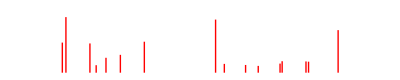
```mathematica
-Graphics--Graphics-
```

```mathematica
Manipulate[
H5PlotSpecLines[
$H5Data[$H5Key, "Spectrum"], 
range,
Offset[shift, Scaled[scale]],
cutoff,
PlotRange->{range, All}
],
{{shift, 0}, 4400, -4400},
{{scale, 1}, .5, 1.5},
{{range, {4500, 7500}}, 0, 10000, ControlType->IntervalSlider},
{{cutoff, .05}, 0.000001, .1}
]
```

```mathematica
Manipulate[
H5SpecGaussianBroadenedSpectrum[
$H5Data[$H5Key, "Spectrum"], 
σ,
range,
Offset[shift, Scaled[scale]],
cutoff,
PlotRange->{range, All}
],
{{shift, 0}, 4400, -4400},
{{scale, 1}, .5, 1.5},
{{range, {4000, 7000}}, 0, 10000, ControlType->IntervalSlider},
{{σ, 25}, 1, 50, 1},
{{cutoff, .05}, 0.000001, .1}
]
```

#### State Assignments

##### Slices

Slice the wavefunctions to start:

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
Sign[ur.#]*Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
nr
]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]],
 ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Map[
Sign[#.ur]*#&,
wfs
]
]&,
NR^2
]
];
```

##### H2 Vectors

```mathematica
$H5Data[$H5Key, "OuterH2StateVectors"]=$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]//Transpose//Map[Normalize@*Total];
```

##### SP Vectors

For the shared-proton we’ll compute the overlap with the equilibrium calculation:

```mathematica
$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]=
$H5DVR["Wavefunctions", 
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"NumberOfWavefunctions"->10,
Method->"Direct"
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonStateCoefficients"]=
Table[
Transpose@$H5DVR[
"ExpectationValues",
Function[
{X, ψ},
#
]&/@wfns,
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"Wavefunctions"->$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]
],
{wfns, $H5Data[$H5Key, "SharedProtonSliceWavefunctions"]}
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonStateVectors"]=
$H5Data[$H5Key, "SharedProtonStateCoefficients"]//Transpose//Map[Normalize@*Total];
```

##### Tables

```mathematica
$iH5FormatStatePercentTableRelativeIntensities=True;
```

```mathematica
iH5FormatStatePercentTable[vecs_, headers_, states_, ops:OptionsPattern[]]:=
Grid[
Prepend[Join[{"𝒻", "ℐ"}, headers]]@
Join[
Round[List/@Prepend[$H5Data[$H5Key, "Frequencies"], 0][[states]], 1],
List/@
If[TrueQ@$iH5FormatStatePercentTableRelativeIntensities,
Map[
If[#<0.0001, ScientificForm[Echo@#, 2], Round[#, .01]]&,
100*#/Max[#]
]&,
Map[ScientificForm[#, 2]&]
]@$H5Data[$H5Key, "Intensities"][[states]],
100*
Round[
Power[
vecs,
2
], 
.01
],
2
],
ops,
Alignment->Left,
Dividers->{{3->Gray}, {2->Gray}},
ItemSize->Full
]//Style[#, ShowStringCharacters->False]&
```

```mathematica
H5FormatH2StatePercentTable[states_]:=
iH5FormatStatePercentTable[
$H5Data[$H5Key, "OuterH2StateVectors"][[states]],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
],
states
]
```

```mathematica
H5FormatH2StatePercentTable2[states_, saSpec_:All]:=
iH5FormatStatePercentTable[
Normalize@*Total/@
Transpose[
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]
][[states, saSpec]],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
],
states
]
```

```mathematica
H5FormatSharedProtonStatePercentTable[states_]:=
iH5FormatStatePercentTable[
$H5Data[$H5Key, "SharedProtonStateVectors"][[states]],
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[10]]]
],
states
]
```

```mathematica
H5FormatSharedProtonStatePercentTable[states_, h2Spec_]:=
iH5FormatStatePercentTable[
Normalize@*Total/@
Transpose[
$H5Data[$H5Key, "SharedProtonStateCoefficients"]
][[states, h2Spec]],
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[10]]]
],
states
]
```

```mathematica
H5FormatStatePercentTable[states_]:=
iH5FormatStatePercentTable[
Join[
$H5Data[$H5Key, "OuterH2StateVectors"][[states]],
$H5Data[$H5Key, "SharedProtonStateVectors"][[states]],
2
],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
]~Join~
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[10]]]
],
states,
Dividers->{{3, -10}->Gray//Thread, {2->Gray}}
]
```

##### Tests

```mathematica
H5FormatSharedProtonStatePercentTable[;;15]
```

```mathematica
H5FormatSharedProtonStatePercentTable[Ordering[$H5Data[$H5Key, "Intensities"], -15]//Sort]
```

𝒻 | ℐ | 1^(H+) | 2^(H+) | 3^(H+) | 4^(H+) | 5^(H+) | 6^(H+) | 7^(H+) | 8^(H+) | 9^(H+) | 10^(H+)
448 | 100. | 0. | 82. | 0. | 17. | 0. | 1. | 0. | 0. | 1. | 0.
1124 | 4.23 | 0. | 3. | 0. | 64. | 0. | 30. | 0. | 0. | 3. | 0.
1635 | 1.28 | 0. | 1. | 0. | 0. | 0. | 52. | 0. | 0. | 46. | 0.
1995 | 0.39 | 0. | 0. | 0. | 0. | 0. | 2. | 0. | 0. | 98. | 0.
2639 | 0.22 | 0. | 100. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3494 | 0.24 | 87. | 0. | 4. | 0. | 3. | 0. | 5. | 0. | 0. | 0.
3820 | 1.69 | 0. | 95. | 0. | 1. | 0. | 4. | 0. | 0. | 0. | 0.
3960 | 1.34 | 0. | 97. | 0. | 3. | 0. | 0. | 0. | 0. | 0. | 0.
4545 | 0.35 | 0. | 82. | 0. | 5. | 0. | 2. | 0. | 0. | 11. | 0.
4652 | 0.31 | 0. | 15. | 0. | 18. | 0. | 25. | 0. | 0. | 42. | 0.
4984 | 0.2 | 0. | 44. | 0. | 1. | 0. | 20. | 0. | 0. | 35. | 0.
5608 | 0.11 | 0. | 98. | 0. | 1. | 0. | 0. | 0. | 0. | 1. | 0.
6177 | 0.2 | 0. | 8. | 0. | 51. | 0. | 41. | 0. | 0. | 0. | 0.
7152 | 0.16 | 0. | 81. | 0. | 19. | 0. | 0. | 0. | 0. | 0. | 0.
7477 | 0.13 | 0. | 97. | 0. | 1. | 0. | 2. | 0. | 0. | 0. | 0.

```mathematica
H5FormatH2StatePercentTable[Ordering[$H5Data[$H5Key, "Intensities"], -15]//Sort]
```

𝒻 | ℐ | (0,0)^H_2 | (0,1-1,0)^H_2 | (0,1+1,0)^H_2 | (0,2-2,0)^H_2 | (1,1∠45)^H_2 | (0,2+2,0)^H_2 | (0,3-3,0)^H_2 | (1,2-2,1)^H_2 | (1,2+2,1)^H_2 | (0,3+3,0)^H_2 | (0,4-4,0)^H_2 | (1,3-3,1)^H_2 | (2,2∠45)^H_2 | (1,3+3,1)^H_2 | (0,4+4,0)^H_2
448 | 100. | 91. | 8. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1124 | 4.23 | 88. | 11. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1635 | 1.28 | 86. | 12. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1995 | 0.39 | 85. | 13. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2639 | 0.22 | 79. | 18. | 0. | 2. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3494 | 0.24 | 0. | 73. | 19. | 5. | 2. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3820 | 1.69 | 12. | 19. | 42. | 20. | 3. | 0. | 3. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3960 | 1.34 | 6. | 58. | 18. | 11. | 5. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4545 | 0.35 | 3. | 3. | 89. | 3. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4652 | 0.31 | 2. | 73. | 1. | 19. | 2. | 1. | 2. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4984 | 0.2 | 51. | 23. | 16. | 8. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
5608 | 0.11 | 67. | 15. | 12. | 5. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
6177 | 0.2 | 5. | 55. | 0. | 31. | 0. | 1. | 6. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
7152 | 0.16 | 0. | 17. | 3. | 38. | 29. | 3. | 6. | 2. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
7477 | 0.13 | 0. | 4. | 1. | 29. | 40. | 7. | 8. | 8. | 0. | 0. | 1. | 1. | 0. | 0. | 0.

### 3D Contraction of 4D (28)

```mathematica
$H5Key={30, 30, Range[28]};
```

```mathematica
$H5Data[$H5Key, "SharedProtonPoints"]=$H5Key[[1]];
$H5Data[$H5Key, "SharedProtonBasisSize"]=$H5Data[$H5Key, "SharedProtonPoints"]^2;
$H5Data[$H5Key, "OuterH2Points"]=$H5Key[[2]];
$H5Data[$H5Key, "OuterH2States"]=$H5Key[[3]];
$H5Data[$H5Key, "OuterH2BasisSize"]=Length@$H5Data[$H5Key, "OuterH2States"];
$H5Data[$H5Key, "TotalBasisSize"]=$H5Data[$H5Key, "SharedProtonBasisSize"]*$H5Data[$H5Key, "OuterH2BasisSize"]
```

25200

#### T_R

```mathematica
$H5Data[$H5Key, "SharedProtonKineticEnergy"]=
$H5DVR["KineticEnergy",
 "Points"->
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

#### h_r

H_2 wavefunctions are computed for the equilibrium value of (a, s)

```mathematica
$H5Data[$H5Key, "OuterH2Wavefunctions"]=
$H2DVR[
Return->{"Grid", "Wavefunctions"},
"Points"->{250, 250},
"PotentialOptimizationOptions"->
{
"PotentialFunction"->h2SinglePot,
"OptimizedBasisSize"->$H5Data[$H5Key, "OuterH2Points"]
},
"NumberOfWavefunctions"->$H5Data[$H5Key, "OuterH2Points"]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2Hamiltonian"]=
SparseArray[
Band[{1, 1}]->
$H5Data[$H5Key, "OuterH2Wavefunctions"][[
"Wavefunctions", 1, $H5Data[$H5Key, "OuterH2States"]
]]
];
```

#### V

```mathematica
$H5Data[$H5Key, "SharedProtonGrid"]=
$H5DVR["Grid", 
"Points"->{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

```mathematica
$H5Data[$H5Key, "OuterH2Grid"]=
Flatten[
$H5Data[$H5Key, "OuterH2Wavefunctions"]["Grid"],
 1
];
```

```mathematica
$H5Data[$H5Key, "OuterH2GridPotential"]=
h2PotVec@$H5Data[$H5Key, "OuterH2Grid"];
```

```mathematica
(*H5OuterH2PotVector//Clear*)
H5OuterH2PotVector[key_][i_,j_]:=
H5OuterH2PotVector[key][i,j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
H5FullVecPot@
Join[
ConstantArray[gp, $H5Data[$H5Key, "OuterH2Points"]^2],
$H5Data[$H5Key, "OuterH2Grid"],
2
],
ConstantArray[10^9, $H5Data[$H5Key, "OuterH2Points"]^2]
]-$H5Data[$H5Key, "OuterH2GridPotential"]
]
```

```mathematica
(*Clear[H5OuterH2PotBlock]*)
H5OuterH2PotBlock[key_][i_, j_]:=
H5OuterH2PotBlock[key][i, j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[i==1&&j==1||
dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
$H2DVR["OperatorMatrix",
Evaluate[H5OuterH2PotVector[key][i, j]]&,
"Grid"->$H5Data[key, "OuterH2Wavefunctions"]["Grid"],
"Wavefunctions"->Hold@$H5Data[key, "OuterH2Wavefunctions"]["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
H5OuterH2PotBlock[key][1, 1]
]
]
```

```mathematica
$H5Data[$H5Key, "PotentialBlocks"]=
Flatten[
Array[H5OuterH2PotBlock[$H5Key], 
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
], 
1
];
```

```mathematica
$H5Data[$H5Key, "PotentialEnergy"]=
SparseArray[
Band[{1,1}]->$H5Data[$H5Key, "PotentialBlocks"]
];
```

#### Full Kinetic Energy

```mathematica
$H5Data[$H5Key, "KineticEnergy"]=
KroneckerProduct[
$H5Data[$H5Key, "SharedProtonKineticEnergy"],
IdentityMatrix[$H5Data[$H5Key, "OuterH2BasisSize"], SparseArray]
]+
KroneckerProduct[
IdentityMatrix[$H5Data[$H5Key, "SharedProtonBasisSize"], SparseArray],
$H5Data[$H5Key, "OuterH2Hamiltonian"]
];
```

#### Energies and Wavefunctions

I just use one of the DVRs as a wrapper to access its eigenvalues/vectors routine

```mathematica
$H5Data[$H5Key, "Eigensystem"]=
$H2DVR["Wavefunctions", 
"KineticEnergy"->Hold@$H5Data[$H5Key, "KineticEnergy"],
"PotentialEnergy"->Hold@$H5Data[$H5Key, "PotentialEnergy"],
"NumberOfWavefunctions"->350,
(*Method->"Direct"*)"ArnoldiIterations"->10000
];//AbsoluteTiming
```

{589.638,Null}

```mathematica
{$H5Data[$H5Key, "Energies"], $H5Data[$H5Key, "Wavefunctions"]}=$H5Data[$H5Key, "Eigensystem"];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/wavefunctions@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Eigensystem"]
]
```

~/Documents/UW/Research/H5+/results/wavefunctions@{30, 30, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20, 21, 22, 23, 24, 25, 26, 27, 28}}.mx

##### Frequencies

```mathematica
$H5Data[$H5Key, "Frequencies"]=
Rest[#-#[[1]]]&@$H5Data[$H5Key, "Energies"];
$H5Data[$H5Key, "Frequencies"]~Take~100
```

{404.984,686.837,1052.66,1225.25,1558.23,1653.87,1843.15,1909.25,2195.89,2237.4,2521.,2530.06,2588.71,2768.53,2807.01,2885.93,2986.54,3094.75,3134.2,3298.91,3318.09,3404.75,3420.51,3494.61,3500.15,3689.08,3811.26,3830.02,3853.1,3934.55,3978.02,4001.46,4096.43,4113.2,4130.03,4405.23,4410.01,4489.01,4510.17,4528.59,4559.59,4567.51,4649.02,4693.02,4821.83,4907.66,4944.42,4958.75,4994.68,4997.49,5025.53,5070.72,5144.25,5252.26,5254.02,5272.87,5280.02,5348.47,5415.8,5464.32,5527.55,5543.89,5580.69,5590.18,5654.5,5693.83,5718.87,5854.31,5884.21,5907.98,5911.22,5911.74,5981.1,5988.45,6032.52,6089.98,6105.28,6148.82,6171.04,6230.83,6261.,6271.36,6275.05,6285.33,6316.88,6358.49,6402.47,6431.33,6434.21,6461.03,6484.48,6532.21,6570.4,6602.09,6690.15,6707.41,6713.44,6738.54,6757.15,6773.86}

##### Slices

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
Sign[ur.#]*Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
nr
]
];
```

#### Spectrum

##### Transition Moments

```mathematica
$H5Data[$H5Key, "SharedProtonGrid"]=
$H5DVR["Grid", "Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]}];
```

Helper to extract the grid to be use to compute the dipole surface elements. Effectively just the surface parametrized in (a, s)

```mathematica
H5OuterH2DipoleGrid[key_][i_, j_]:=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=$H5DipoleSurfaceInterps[[1, 1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
Join[
ConstantArray[gp, $H5Data[key, "OuterH2Points"]^2],
$H5Data[key, "OuterH2Grid"],
2
],
$Failed
]
]
```

```mathematica
(*computeDipVecs//Clear*)
H5OuterH2DipoleVector[key_][i_,j_]:=
H5OuterH2DipoleVector[key][i,j]=
With[{gr=H5OuterH2DipoleGrid[key][i, j]},
If[gr===$Failed,
ConstantArray[{0., 0., 0.}, $H5Data[key, "OuterH2Points"]^2],
$H5DipoleSurfaceVec@gr//Through//Transpose
]
]
```

This computes a term in the transition matrix defined by m_rμn_r for a given (a, s)

```mathematica
(*Clear[H5OuterH2TransitionMatrix]*)
H5OuterH2TransitionMatrix[key_][i_, j_]:=
H5OuterH2TransitionMatrix[key][i, j]=
With[{dip=H5OuterH2DipoleVector[key][i, j]},
If[Norm[Flatten[dip]]>0,
$H2DVR[
"OperatorMatrix",
(dip&),
"Grid"->$H5Data[key, "OuterH2Wavefunctions"]["Grid"],
"Wavefunctions"->$H5Data[key, "OuterH2Wavefunctions"]["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
$Failed
]
]
```

Computing these for each (R_1, R_2):

```mathematica
$H5Data[$H5Key, "OuterH2TransitionMoments"]=
Array[H5OuterH2TransitionMatrix[$H5Key], 
{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]}];
```

Then we slice up the coefficients:

```mathematica
$H5Data[$H5Key, "SharedProtonCoefficientVectors"]=
With[
{
wfns=$H5Data[$H5Key, "Wavefunctions"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
nr=$H5Data[$H5Key, "OuterH2BasisSize"]
},
Partition[
Array[
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]], 
ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Developer`ToPackedArray@
Map[
(*Sign[#.ur]**)#&,
wfs
]
]&,
NR^2
],
NR
]
];
```

Then we compute the transition moment vector over the (s, a) coordinates

```mathematica
H5SharedProtonTransitionMoment//Clear
H5SharedProtonTransitionMoment[key_][i_]:=
H5SharedProtonTransitionMoment[key][i]=
With[
{
coeffs=
Flatten[$H5Data[key, "SharedProtonCoefficientVectors"][[All, All, {i, 1}]], 1],
momsArr=
Flatten[$H5Data[key, "OuterH2TransitionMoments"], 1]
},
MapThread[
If[#2===$Failed,
0,
#[[1]].#2[[All,All, 1]].#[[2]]
]&,
{
coeffs,
momsArr
}
]
]
```

Check some phase stuff

```mathematica
(*Manipulate[
MapThread[Append, 
{
Flatten[$H5Data[$H5Key, "SharedProtonGrid"], 1],
H5SharedProtonTransitionMoment[$H5Key][i]
}
]//ListPlot3D[#, 
PlotRange->{{-1.5, 1.5}, {1.2, 2}, All},
 ColorFunction->"Rainbow", PerformanceGoal->"Quality"
]&,
{i, 1, Length@$H5Data[$H5Key, "Energies"], 1, AnimationRate->.5}
]*)
```

Norm and square to get raw intensity:

```mathematica
$H5Data[$H5Key, "Intensities"]=
Array[Total[H5SharedProtonTransitionMoment[$H5Key][#]]^2&, Length@$H5Data[$H5Key, "Energies"]];
```

##### Plots

```mathematica
$H5Data[$H5Key, "Spectrum"]=Thread[{Prepend[$H5Data[$H5Key, "Frequencies"], 0], $H5Data[$H5Key, "Intensities"]}];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/spectrum@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Spectrum"]
]
```

~/Documents/UW/Research/H5+/results/spectrum@{30, 30, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20, 21, 22, 23, 24, 25, 26, 27, 28}}.mx

```mathematica
$H5Data[$H5Key, "TargetShift"]=989-MaximalBy[#, Last, 2][[2, 1]]&@H5SpecPrep[$H5Data[$H5Key, "Spectrum"], {0, 1500}];
$H5Data[$H5Key, "TargetScaling"]= 
(6684-4911)/(#[[2]]-#[[1]])&@
Sort@
MaximalBy[
H5SpecPrep[$H5Data[$H5Key, "Spectrum"],{4800, 7500}, Offset@$H5Data[$H5Key, "TargetShift"]],
Last,
2
][[All, 1]];
```

```mathematica
Manipulate[
H5PlotSpec[
Select[$H5Data[$H5Key, "Spectrum"], #[[2]]>10^-4&],
 Offset[shift, Scaled[scale]],
.05
],
{{shift, $H5Data[$H5Key, "TargetShift"]}, 4400, -4400, 10},
{{scale, $H5Data[$H5Key, "TargetScaling"]}, .5, 2}
]
```

```mathematica
-Graphics--Graphics-
```

```mathematica
Manipulate[
H5PlotSpecLines[
$H5Data[$H5Key, "Spectrum"], 
range,
Offset[shift, Scaled[scale]],
cutoff,
PlotRange->{range, All}
],
{{shift, 0}, 4400, -4400},
{{scale, 1}, .5, 1.5},
{{range, {4500, 7500}}, 0, 10000, ControlType->IntervalSlider},
{{cutoff, .05}, 0.000001, .1}
]
```

```mathematica
Manipulate[
H5SpecGaussianBroadenedSpectrum[
$H5Data[$H5Key, "Spectrum"], 
σ,
range,
Offset[shift, Scaled[scale]],
cutoff,
PlotRange->{range, All}
],
{{shift, 0}, 4400, -4400},
{{scale, 1}, .5, 1.5},
{{range, {4000, 7000}}, 0, 10000, ControlType->IntervalSlider},
{{σ, 25}, 1, 50, 1},
{{cutoff, .05}, 0.000001, .1}
]
```

#### State Assignments

##### Slices

Slice the wavefunctions to start:

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
Sign[ur.#]*Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
nr
]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]],
 ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Map[
Sign[#.ur]*#&,
wfs
]
]&,
NR^2
]
];
```

##### H2 Vectors

```mathematica
$H5Data[$H5Key, "OuterH2StateVectors"]=$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]//Transpose//Map[Normalize@*Total];
```

##### SP Vectors

For the shared-proton we’ll compute the overlap with the equilibrium calculation:

```mathematica
$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]=
$H5DVR["Wavefunctions", 
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"NumberOfWavefunctions"->10,
Method->"Direct"
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonStateCoefficients"]=
Table[
Transpose@$H5DVR[
"ExpectationValues",
Function[
{X, ψ},
#
]&/@wfns,
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"Wavefunctions"->$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]
],
{wfns, $H5Data[$H5Key, "SharedProtonSliceWavefunctions"]}
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonStateVectors"]=
$H5Data[$H5Key, "SharedProtonStateCoefficients"]//Transpose//Map[Normalize@*Total];
```

##### Tables

```mathematica
$iH5FormatStatePercentTableRelativeIntensities=True;
```

```mathematica
iH5FormatStatePercentTable[vecs_, headers_, states_, ops:OptionsPattern[]]:=
Grid[
Prepend[Join[{"𝒻", "ℐ"}, headers]]@
Join[
Round[List/@Prepend[$H5Data[$H5Key, "Frequencies"], 0][[states]], 1],
List/@
If[TrueQ@$iH5FormatStatePercentTableRelativeIntensities,
Map[
If[#<0.0001, ScientificForm[Echo@#, 2], Round[#, .01]]&,
100*#/Max[#]
]&,
Map[ScientificForm[#, 2]&]
]@$H5Data[$H5Key, "Intensities"][[states]],
100*
Round[
Power[
vecs,
2
], 
.01
],
2
],
ops,
Alignment->Left,
Dividers->{{3->Gray}, {2->Gray}},
ItemSize->Full
]//Style[#, ShowStringCharacters->False]&
```

```mathematica
H5FormatH2StatePercentTable[states_]:=
iH5FormatStatePercentTable[
$H5Data[$H5Key, "OuterH2StateVectors"][[states]],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
],
states
]
```

```mathematica
H5FormatH2StatePercentTable2[states_, saSpec_:All]:=
iH5FormatStatePercentTable[
Normalize@*Total/@
Transpose[
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]
][[states, saSpec]],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
],
states
]
```

```mathematica
H5FormatSharedProtonStatePercentTable[states_]:=
iH5FormatStatePercentTable[
$H5Data[$H5Key, "SharedProtonStateVectors"][[states]],
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[10]]]
],
states
]
```

```mathematica
H5FormatSharedProtonStatePercentTable[states_, h2Spec_]:=
iH5FormatStatePercentTable[
Normalize@*Total/@
Transpose[
$H5Data[$H5Key, "SharedProtonStateCoefficients"]
][[states, h2Spec]],
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[10]]]
],
states
]
```

```mathematica
H5FormatStatePercentTable[states_]:=
iH5FormatStatePercentTable[
Join[
$H5Data[$H5Key, "OuterH2StateVectors"][[states]],
$H5Data[$H5Key, "SharedProtonStateVectors"][[states]],
2
],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
]~Join~
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[10]]]
],
states,
Dividers->{{3, -10}->Gray//Thread, {2->Gray}}
]
```

##### Tests

```mathematica
H5FormatSharedProtonStatePercentTable[Ordering[$H5Data[$H5Key, "Intensities"], -15]//Sort]
```

𝒻 | ℐ | 1^(H+) | 2^(H+) | 3^(H+) | 4^(H+) | 5^(H+) | 6^(H+) | 7^(H+) | 8^(H+) | 9^(H+) | 10^(H+)
405 | 100. | 0. | 74. | 0. | 23. | 0. | 3. | 0. | 0. | 1. | 0.
1053 | 3.81 | 0. | 3. | 0. | 54. | 0. | 37. | 0. | 0. | 6. | 0.
1558 | 1.26 | 0. | 2. | 0. | 67. | 0. | 31. | 0. | 0. | 0. | 0.
1909 | 0.48 | 0. | 0. | 0. | 2. | 0. | 1. | 0. | 0. | 96. | 0.
3299 | 0.24 | 36. | 0. | 34. | 0. | 13. | 0. | 15. | 2. | 0. | 1.
3689 | 5.32 | 0. | 68. | 0. | 26. | 0. | 6. | 0. | 0. | 1. | 0.
3830 | 3.62 | 0. | 65. | 0. | 27. | 0. | 7. | 0. | 0. | 1. | 0.
4130 | 0.26 | 0. | 3. | 0. | 92. | 0. | 0. | 0. | 0. | 5. | 0.
4405 | 0.55 | 0. | 30. | 0. | 54. | 0. | 3. | 0. | 0. | 13. | 0.
4489 | 0.66 | 0. | 5. | 0. | 79. | 0. | 7. | 0. | 0. | 9. | 0.
4822 | 0.24 | 0. | 86. | 0. | 6. | 0. | 6. | 0. | 0. | 1. | 0.
5464 | 0.2 | 0. | 81. | 0. | 1. | 0. | 18. | 0. | 0. | 0. | 0.
5981 | 0.4 | 0. | 91. | 0. | 9. | 0. | 0. | 0. | 0. | 0. | 0.
6033 | 0.19 | 0. | 34. | 0. | 46. | 0. | 8. | 0. | 0. | 12. | 0.
6484 | 0.19 | 0. | 0. | 0. | 71. | 0. | 28. | 0. | 0. | 1. | 0.

```mathematica
H5FormatH2StatePercentTable[Ordering[$H5Data[$H5Key, "Intensities"], -15]//Sort]
```

𝒻 | ℐ | (0,0)^H_2 | (0,1-1,0)^H_2 | (0,1+1,0)^H_2 | (0,2-2,0)^H_2 | (1,1∠45)^H_2 | (0,2+2,0)^H_2 | (0,3-3,0)^H_2 | (1,2-2,1)^H_2 | (1,2+2,1)^H_2 | (0,3+3,0)^H_2 | (0,4-4,0)^H_2 | (1,3-3,1)^H_2 | (2,2∠45)^H_2 | (1,3+3,1)^H_2 | (0,4+4,0)^H_2 | Missing[KeyAbsent,16]^H_2 | Missing[KeyAbsent,17]^H_2 | Missing[KeyAbsent,18]^H_2 | Missing[KeyAbsent,19]^H_2 | Missing[KeyAbsent,20]^H_2 | Missing[KeyAbsent,21]^H_2 | Missing[KeyAbsent,22]^H_2 | Missing[KeyAbsent,23]^H_2 | Missing[KeyAbsent,24]^H_2 | Missing[KeyAbsent,25]^H_2 | Missing[KeyAbsent,26]^H_2 | Missing[KeyAbsent,27]^H_2 | Missing[KeyAbsent,28]^H_2
405 | 100. | 90. | 8. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1053 | 3.81 | 87. | 11. | 2. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1558 | 1.26 | 84. | 12. | 2. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1909 | 0.48 | 84. | 13. | 2. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3299 | 0.24 | 5. | 68. | 19. | 7. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3689 | 5.32 | 3. | 48. | 31. | 12. | 5. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3830 | 3.62 | 2. | 27. | 64. | 4. | 2. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4130 | 0.26 | 47. | 36. | 9. | 6. | 2. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4405 | 0.55 | 11. | 36. | 37. | 9. | 6. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4489 | 0.66 | 36. | 0. | 52. | 0. | 1. | 10. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4822 | 0.24 | 31. | 34. | 19. | 9. | 5. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
5464 | 0.2 | 44. | 28. | 17. | 5. | 4. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
5981 | 0.4 | 14. | 11. | 55. | 1. | 3. | 14. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
6033 | 0.19 | 16. | 17. | 55. | 1. | 4. | 6. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
6484 | 0.19 | 0. | 35. | 25. | 15. | 16. | 0. | 4. | 3. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.

### 3D Contraction of 4D (35, 21)

```mathematica
$H5Key={35, 25, Range[21]};
```

```mathematica
$H5Data[$H5Key, "SharedProtonPoints"]=$H5Key[[1]];
$H5Data[$H5Key, "SharedProtonBasisSize"]=$H5Data[$H5Key, "SharedProtonPoints"]^2;
$H5Data[$H5Key, "OuterH2Points"]=$H5Key[[2]];
$H5Data[$H5Key, "OuterH2States"]=$H5Key[[3]];
$H5Data[$H5Key, "OuterH2BasisSize"]=Length@$H5Data[$H5Key, "OuterH2States"];
$H5Data[$H5Key, "TotalBasisSize"]=$H5Data[$H5Key, "SharedProtonBasisSize"]*$H5Data[$H5Key, "OuterH2BasisSize"]
```

25725

#### T_R

```mathematica
$H5Data[$H5Key, "SharedProtonKineticEnergy"]=
$H5DVR["KineticEnergy",
 "Points"->
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

#### h_r

H_2 wavefunctions are computed for the equilibrium value of (a, s)

```mathematica
$H5Data[$H5Key, "OuterH2Wavefunctions"]=
$H2DVR[
Return->{"Grid", "Wavefunctions"},
"Points"->{250, 250},
"PotentialOptimizationOptions"->
{
"PotentialFunction"->h2SinglePot,
"OptimizedBasisSize"->$H5Data[$H5Key, "OuterH2Points"]
},
"NumberOfWavefunctions"->$H5Data[$H5Key, "OuterH2Points"]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2Hamiltonian"]=
SparseArray[
Band[{1, 1}]->
$H5Data[$H5Key, "OuterH2Wavefunctions"][[
"Wavefunctions", 1, $H5Data[$H5Key, "OuterH2States"]
]]
];
```

#### V

```mathematica
$H5Data[$H5Key, "SharedProtonGrid"]=
$H5DVR["Grid", 
"Points"->{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]
}
];
```

```mathematica
$H5Data[$H5Key, "OuterH2Grid"]=
Flatten[
$H5Data[$H5Key, "OuterH2Wavefunctions"]["Grid"],
 1
];
```

```mathematica
$H5Data[$H5Key, "OuterH2GridPotential"]=
h2PotVec@$H5Data[$H5Key, "OuterH2Grid"];
```

```mathematica
(*H5OuterH2PotVector//Clear*)
H5OuterH2PotVector[key_][i_,j_]:=
H5OuterH2PotVector[key][i,j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
H5FullVecPot@
Join[
ConstantArray[gp, $H5Data[$H5Key, "OuterH2Points"]^2],
$H5Data[$H5Key, "OuterH2Grid"],
2
],
ConstantArray[10^9, $H5Data[$H5Key, "OuterH2Points"]^2]
]-$H5Data[$H5Key, "OuterH2GridPotential"]
]
```

```mathematica
(*Clear[H5OuterH2PotBlock]*)
H5OuterH2PotBlock[key_][i_, j_]:=
H5OuterH2PotBlock[key][i, j]=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[i==1&&j==1||
dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
$H2DVR["OperatorMatrix",
H5OuterH2PotVector[key][i, j]&,
"Grid"->$H5Data[key, "OuterH2Wavefunctions"]["Grid"],
"Wavefunctions"->Hold@$H5Data[key, "OuterH2Wavefunctions"]["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
H5OuterH2PotBlock[key][1, 1]
]
]
```

```mathematica
$H5Data[$H5Key, "PotentialBlocks"]=
Flatten[
Array[H5OuterH2PotBlock[$H5Key], 
{
$H5Data[$H5Key, "SharedProtonPoints"], 
$H5Data[$H5Key, "SharedProtonPoints"]}
], 
1
];
```

```mathematica
$H5Data[$H5Key, "PotentialEnergy"]=
SparseArray[
Band[{1,1}]->$H5Data[$H5Key, "PotentialBlocks"]
];
```

#### Full Kinetic Energy

```mathematica
$H5Data[$H5Key, "KineticEnergy"]=
KroneckerProduct[
$H5Data[$H5Key, "SharedProtonKineticEnergy"],
IdentityMatrix[$H5Data[$H5Key, "OuterH2BasisSize"], SparseArray]
]+
KroneckerProduct[
IdentityMatrix[$H5Data[$H5Key, "SharedProtonBasisSize"], SparseArray],
$H5Data[$H5Key, "OuterH2Hamiltonian"]
];
```

#### Energies and Wavefunctions

I just use one of the DVRs as a wrapper to access its eigenvalues/vectors routine

```mathematica
$H5Data[$H5Key, "Eigensystem"]=
$H2DVR["Wavefunctions", 
"KineticEnergy"->Hold@$H5Data[$H5Key, "KineticEnergy"],
"PotentialEnergy"->Hold@$H5Data[$H5Key, "PotentialEnergy"],
"NumberOfWavefunctions"->350,
Method->"Direct"
];//AbsoluteTiming
```

{19906.5,Null}

```mathematica
{$H5Data[$H5Key, "Energies"], $H5Data[$H5Key, "Wavefunctions"]}=$H5Data[$H5Key, "Eigensystem"];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/wavefunctions@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Eigensystem"]
]
```

~/Documents/UW/Research/H5+/results/wavefunctions@{35, 25, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20, 21}}.mx

##### Frequencies

```mathematica
$H5Data[$H5Key, "Frequencies"]=
Rest[#-#[[1]]]&@$H5Data[$H5Key, "Energies"];
$H5Data[$H5Key, "Frequencies"]~Take~100
```

{451.975,764.804,1116.55,1348.98,1646.68,1744.61,1935.89,2067.76,2287.44,2408.58,2580.99,2643.66,2724.87,2761.51,2910.09,2936.93,3054.05,3187.88,3191.77,3341.33,3444.,3470.64,3490.47,3548.81,3625.22,3826.24,3894.24,3900.96,3961.03,3964.22,4044.84,4097.68,4187.07,4261.61,4284.76,4439.45,4441.02,4473.77,4529.14,4568.74,4642.99,4726.92,4844.58,4858.15,4899.36,4937.11,4990.69,4999.05,5088.63,5109.67,5149.16,5185.99,5186.96,5239.29,5340.26,5368.19,5408.63,5453.28,5477.75,5527.23,5603.66,5622.56,5627.1,5659.42,5661.62,5741.33,5775.89,5794.61,5826.81,5834.,5949.87,5961.78,5980.67,5986.83,6065.56,6075.11,6119.88,6119.94,6175.46,6228.03,6260.62,6269.77,6296.56,6315.31,6369.87,6375.83,6415.43,6430.72,6456.01,6499.8,6559.48,6583.15,6598.53,6614.72,6676.33,6715.42,6735.03,6744.32,6751.2,6820.57}

```mathematica
kk
```

{451.975,764.804,1116.55,1348.98,1646.68,1744.61,1935.89,2067.76,2287.44,2408.58,2580.99,2643.66,2724.87,2761.51,2910.09,2936.93,3054.05,3187.88,3191.77,3341.33,3444.,3470.64,3490.47,3548.81,3625.22,3826.24,3894.24,3900.96,3961.03,3964.22,4044.84,4097.68,4187.07,4261.61,4284.76,4439.45,4441.02,4473.77,4529.14,4568.74,4642.99,4726.92,4844.58,4858.15,4899.36,4937.11,4990.69,4999.05,5088.63,5109.67,5149.16,5185.99,5186.96,5239.29,5340.26,5368.19,5408.63,5453.28,5477.75,5527.23,5603.66,5622.56,5627.1,5659.42,5661.62,5741.33,5775.89,5794.61,5826.81,5834.,5949.87,5961.78,5980.67,5986.83,6065.56,6075.11,6119.88,6119.94,6175.46,6228.03,6260.62,6269.77,6296.56,6315.31,6369.87,6375.83,6415.43,6430.72,6456.01,6499.8,6559.48,6583.15,6598.53,6614.72,6676.33,6715.42,6735.03,6744.32,6751.2,6820.57}

##### Slices

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
Sign[ur.#]*Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
nr
]
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]//Dimensions
```

{21,350,1225}

```mathematica
20000/3600.
```

5.55556

#### Spectrum

##### Transition Moments

```mathematica
$H5Data[$H5Key, "SharedProtonGrid"]=
$H5DVR["Grid", "Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]}];
```

Helper to extract the grid to be use to compute the dipole surface elements. Effectively just the surface parametrized in (a, s)

```mathematica
H5OuterH2DipoleGrid[key_][i_, j_]:=
With[{gp=$H5Data[key, "SharedProtonGrid"][[i, j]], dom=$H5DipoleSurfaceInterps[[1, 1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
Join[
ConstantArray[gp, $H5Data[key, "OuterH2Points"]^2],
$H5Data[key, "OuterH2Grid"],
2
],
$Failed
]
]
```

```mathematica
(*computeDipVecs//Clear*)
H5OuterH2DipoleVector[key_][i_,j_]:=
H5OuterH2DipoleVector[key][i,j]=
With[{gr=H5OuterH2DipoleGrid[key][i, j]},
If[gr===$Failed,
ConstantArray[{0., 0., 0.}, $H5Data[key, "OuterH2Points"]^2],
$H5DipoleSurfaceVec@gr//Through//Transpose
]
]
```

This computes a term in the transition matrix defined by m_rμn_r for a given (a, s)

```mathematica
(*Clear[H5OuterH2TransitionMatrix]*)
H5OuterH2TransitionMatrix[key_][i_, j_]:=
H5OuterH2TransitionMatrix[key][i, j]=
With[{dip=H5OuterH2DipoleVector[key][i, j]},
If[Norm[Flatten[dip]]>0,
$H2DVR[
"OperatorMatrix",
(dip&),
"Grid"->$H5Data[key, "OuterH2Wavefunctions"]["Grid"],
"Wavefunctions"->$H5Data[key, "OuterH2Wavefunctions"]["Wavefunctions"],
"WavefunctionSelection"->$H5Data[key, "OuterH2States"]
],
$Failed
]
]
```

Computing these for each (R_1, R_2):

```mathematica
$H5Data[$H5Key, "OuterH2TransitionMoments"]=
Array[H5OuterH2TransitionMatrix[$H5Key], 
{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]}];
```

Then we slice up the coefficients:

```mathematica
$H5Data[$H5Key, "SharedProtonCoefficientVectors"]=
With[
{
wfns=$H5Data[$H5Key, "Wavefunctions"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
nr=$H5Data[$H5Key, "OuterH2BasisSize"]
},
Partition[
Array[
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]], 
ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Developer`ToPackedArray@
Map[
(*Sign[#.ur]**)#&,
wfs
]
]&,
NR^2
],
NR
]
];
```

Then we compute the transition moment vector over the (s, a) coordinates

```mathematica
H5SharedProtonTransitionMoment//Clear
H5SharedProtonTransitionMoment[key_][i_]:=
H5SharedProtonTransitionMoment[key][i]=
With[
{
coeffs=
Flatten[$H5Data[key, "SharedProtonCoefficientVectors"][[All, All, {i, 1}]], 1],
momsArr=
Flatten[$H5Data[key, "OuterH2TransitionMoments"], 1]
},
MapThread[
If[#2===$Failed,
0,
#[[1]].#2[[All,All, 1]].#[[2]]
]&,
{
coeffs,
momsArr
}
]
]
```

Check some phase stuff

```mathematica
(*Manipulate[
MapThread[Append, 
{
Flatten[$H5Data[$H5Key, "SharedProtonGrid"], 1],
H5SharedProtonTransitionMoment[$H5Key][i]
}
]//ListPlot3D[#, 
PlotRange->{{-1.5, 1.5}, {1.2, 2}, All},
 ColorFunction->"Rainbow", PerformanceGoal->"Quality"
]&,
{i, 1, Length@$H5Data[$H5Key, "Energies"], 1, AnimationRate->.5}
]*)
```

Norm and square to get raw intensity:

```mathematica
$H5Data[$H5Key, "Intensities"]=
Array[Total[H5SharedProtonTransitionMoment[$H5Key][#]]^2&, Length@$H5Data[$H5Key, "Energies"]];
```

##### Plots

```mathematica
$H5Data[$H5Key, "Spectrum"]=Thread[{Prepend[$H5Data[$H5Key, "Frequencies"], 0], $H5Data[$H5Key, "Intensities"]}];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/spectrum@``.mx"~TemplateApply~{$H5Key},
$H5Data[$H5Key, "Spectrum"]
]
```

~/Documents/UW/Research/H5+/results/spectrum@{35, 25, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20, 21}}.mx

```mathematica
$H5Data[$H5Key, "TargetShift"]=989-MaximalBy[#, Last, 2][[2, 1]]&@H5SpecPrep@$H5Data[$H5Key, "Spectrum"];
$H5Data[$H5Key, "TargetScaling"]= 
(6684-4911)/(#[[2]]-#[[1]])&@
Sort@
MaximalBy[
H5SpecPrep[$H5Data[$H5Key, "Spectrum"],{4800, 7500}, Offset@$H5Data[$H5Key, "TargetShift"]],
Last,
2
][[All, 1]];
```

```mathematica
Manipulate[
H5PlotSpec[
$H5Data[$H5Key, "Spectrum"],
 Offset[shift, Scaled[scale]],
.05
],
{{shift, $H5Data[$H5Key, "TargetShift"]}, 4400, -4400, 10},
{{scale, $H5Data[$H5Key, "TargetScaling"]}, .5, 2}
]
```

```mathematica
Manipulate[
H5PlotSpecLines[
$H5Data[$H5Key, "Spectrum"], 
range,
Offset[shift, Scaled[scale]],
cutoff,
PlotRange->{range, All}
],
{{shift, 0}, 4400, -4400},
{{scale, 1}, .5, 1.5},
{{range, {4500, 7500}}, 0, 10000, ControlType->IntervalSlider},
{{cutoff, .05}, 0.000001, .1}
]
```

```mathematica
Manipulate[
H5SpecGaussianBroadenedSpectrum[
$H5Data[$H5Key, "Spectrum"], 
σ,
range,
Offset[shift, Scaled[scale]],
cutoff,
PlotRange->{range, All}
],
{{shift, 0}, 4400, -4400},
{{scale, 1}, .5, 1.5},
{{range, {4000, 7000}}, 0, 10000, ControlType->IntervalSlider},
{{σ, 25}, 1, 50, 1},
{{cutoff, .05}, 0.000001, .1}
]
```

#### State Assignments

##### Slices

Slice the wavefunctions to start:

```mathematica
$H5Data[$H5Key, "SharedProtonSliceWavefunctions"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, #;;-1;;nr]], 
ur=wfns[[1, 1;;-1;;nr]]
},
Sign[ur.#]*Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
nr
]
];
```

```mathematica
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]=
With[
{
nr=$H5Data[$H5Key, "OuterH2BasisSize"],
NR=$H5Data[$H5Key, "SharedProtonPoints"],
wfns=$H5Data[$H5Key, "Wavefunctions"]
},
Array[ 
With[
{
wfs=wfns[[All, 1+(#-1)nr;;#*nr]],
 ur=wfns[[1, 1+(NR-1)nr;;NR*nr]]
},
Map[
Sign[#.ur]*#&,
wfs
]
]&,
NR^2
]
];
```

##### H2 Vectors

```mathematica
$H5Data[$H5Key, "OuterH2StateVectors"]=$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]//Transpose//Map[Normalize@*Total];
```

##### SP Vectors

For the shared-proton we’ll compute the overlap with the equilibrium calculation:

```mathematica
$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]=
$H5DVR["Wavefunctions", 
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"NumberOfWavefunctions"->10,
Method->"Direct"
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonStateCoefficients"]=
Table[
Transpose@$H5DVR[
"ExpectationValues",
Function[
{X, ψ},
#
]&/@wfns,
"Points"->{$H5Data[$H5Key, "SharedProtonPoints"], $H5Data[$H5Key, "SharedProtonPoints"]},
"Wavefunctions"->$H5Data[$H5Key, "SharedProtonEquilibriumWavefunctions"]
],
{wfns, $H5Data[$H5Key, "SharedProtonSliceWavefunctions"]}
];
```

```mathematica
$H5Data[$H5Key, "SharedProtonStateVectors"]=
$H5Data[$H5Key, "SharedProtonStateCoefficients"]//Transpose//Map[Normalize@*Total];
```

##### Tables

```mathematica
$iH5FormatStatePercentTableRelativeIntensities=True;
```

```mathematica
iH5FormatStatePercentTable[vecs_, headers_, states_, ops:OptionsPattern[]]:=
Grid[
Prepend[Join[{"𝒻", "ℐ"}, headers]]@
Join[
Round[List/@Prepend[$H5Data[$H5Key, "Frequencies"], 0][[states]], 1],
List/@
If[TrueQ@$iH5FormatStatePercentTableRelativeIntensities,
Map[
If[#<0.0001, ScientificForm[Echo@#, 2], Round[#, .01]]&,
100*#/Max[#]
]&,
Map[ScientificForm[#, 2]&]
]@$H5Data[$H5Key, "Intensities"][[states]],
100*
Round[
Power[
vecs,
2
], 
.01
],
2
],
ops,
Alignment->Left,
Dividers->{{3->Gray}, {2->Gray}},
ItemSize->Full
]//Style[#, ShowStringCharacters->False]&
```

```mathematica
H5FormatH2StatePercentTable[states_]:=
iH5FormatStatePercentTable[
$H5Data[$H5Key, "OuterH2StateVectors"][[states]],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
],
states
]
```

```mathematica
H5FormatH2StatePercentTable2[states_, saSpec_:All]:=
iH5FormatStatePercentTable[
Normalize@*Total/@
Transpose[
$H5Data[$H5Key, "OuterH2SliceWavefunctionCoefficients"]
][[states, saSpec]],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
],
states
]
```

```mathematica
H5FormatSharedProtonStatePercentTable[states_]:=
iH5FormatStatePercentTable[
$H5Data[$H5Key, "SharedProtonStateVectors"][[states]],
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[10]]]
],
states
]
```

```mathematica
H5FormatSharedProtonStatePercentTable[states_, h2Spec_]:=
iH5FormatStatePercentTable[
Normalize@*Total/@
Transpose[
$H5Data[$H5Key, "SharedProtonStateCoefficients"]
][[states, h2Spec]],
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[10]]]
],
states
]
```

```mathematica
H5FormatStatePercentTable[states_]:=
iH5FormatStatePercentTable[
Join[
$H5Data[$H5Key, "OuterH2StateVectors"][[states]],
$H5Data[$H5Key, "SharedProtonStateVectors"][[states]],
2
],
Map[
Superscript[#, "H"~Subscript~2]&,Lookup[$H2StateAssignments, $H5Data[$H5Key, "OuterH2States"]]
]~Join~
Map[
Superscript[#, "H+"]&,Thread[Ket[Range[10]]]
],
states,
Dividers->{{3, -10}->Gray//Thread, {2->Gray}}
]
```

##### Tests

```mathematica
H5FormatSharedProtonStatePercentTable[Ordering[$H5Data[$H5Key, "Intensities"], -15]//Sort]
```

𝒻 | ℐ | 1^(H+) | 2^(H+) | 3^(H+) | 4^(H+) | 5^(H+) | 6^(H+) | 7^(H+) | 8^(H+) | 9^(H+) | 10^(H+)
452 | 100. | 0. | 0. | 0. | 94. | 0. | 0. | 0. | 0. | 6. | 0.
1117 | 4. | 0. | 33. | 0. | 21. | 0. | 0. | 43. | 0. | 3. | 0.
1647 | 0.76 | 0. | 1. | 0. | 0. | 0. | 0. | 58. | 0. | 41. | 0.
2068 | 0.24 | 0. | 0. | 0. | 8. | 0. | 0. | 0. | 0. | 91. | 0.
2644 | 0.22 | 0. | 92. | 0. | 5. | 0. | 0. | 2. | 0. | 1. | 0.
3341 | 0.13 | 72. | 0. | 8. | 0. | 13. | 7. | 0. | 0. | 0. | 0.
3490 | 0.2 | 80. | 0. | 7. | 0. | 5. | 7. | 0. | 0. | 0. | 0.
3826 | 1.55 | 0. | 31. | 0. | 60. | 0. | 0. | 8. | 0. | 1. | 0.
3964 | 1.33 | 0. | 69. | 0. | 20. | 0. | 0. | 8. | 0. | 2. | 0.
4474 | 0.33 | 0. | 30. | 0. | 8. | 0. | 0. | 54. | 0. | 9. | 0.
4643 | 0.27 | 0. | 1. | 0. | 74. | 0. | 0. | 25. | 0. | 0. | 0.
4937 | 0.22 | 0. | 22. | 0. | 16. | 0. | 0. | 8. | 0. | 54. | 0.
5776 | 0.12 | 0. | 72. | 0. | 9. | 0. | 0. | 10. | 0. | 9. | 0.
6175 | 0.16 | 0. | 57. | 0. | 30. | 0. | 0. | 4. | 0. | 9. | 0.
7474 | 0.11 | 0. | 43. | 0. | 0. | 0. | 0. | 56. | 0. | 1. | 0.

```mathematica
ssss
```

𝒻 | ℐ | 1^(H+) | 2^(H+) | 3^(H+) | 4^(H+) | 5^(H+) | 6^(H+) | 7^(H+) | 8^(H+) | 9^(H+) | 10^(H+)
448 | 100. | 0. | 82. | 0. | 17. | 0. | 1. | 0. | 0. | 1. | 0.
1124 | 4.23 | 0. | 3. | 0. | 64. | 0. | 30. | 0. | 0. | 3. | 0.
1635 | 1.28 | 0. | 1. | 0. | 0. | 0. | 52. | 0. | 0. | 46. | 0.
1995 | 0.39 | 0. | 0. | 0. | 0. | 0. | 2. | 0. | 0. | 98. | 0.
2639 | 0.22 | 0. | 100. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3494 | 0.24 | 87. | 0. | 4. | 0. | 3. | 0. | 5. | 0. | 0. | 0.
3820 | 1.69 | 0. | 95. | 0. | 1. | 0. | 4. | 0. | 0. | 0. | 0.
3960 | 1.34 | 0. | 97. | 0. | 3. | 0. | 0. | 0. | 0. | 0. | 0.
4545 | 0.35 | 0. | 82. | 0. | 5. | 0. | 2. | 0. | 0. | 11. | 0.
4652 | 0.31 | 0. | 15. | 0. | 18. | 0. | 25. | 0. | 0. | 42. | 0.
4984 | 0.2 | 0. | 44. | 0. | 1. | 0. | 20. | 0. | 0. | 35. | 0.
5608 | 0.11 | 0. | 98. | 0. | 1. | 0. | 0. | 0. | 0. | 1. | 0.
6177 | 0.2 | 0. | 8. | 0. | 51. | 0. | 41. | 0. | 0. | 0. | 0.
7152 | 0.16 | 0. | 81. | 0. | 19. | 0. | 0. | 0. | 0. | 0. | 0.
7477 | 0.13 | 0. | 97. | 0. | 1. | 0. | 2. | 0. | 0. | 0. | 0.

```mathematica
H5FormatH2StatePercentTable[Ordering[$H5Data[$H5Key, "Intensities"], -15]//Sort]
```

𝒻 | ℐ | (0,0)^H_2 | (0,1-1,0)^H_2 | (0,1+1,0)^H_2 | (0,2-2,0)^H_2 | (1,1∠45)^H_2 | (0,2+2,0)^H_2 | (0,3-3,0)^H_2 | (1,2-2,1)^H_2 | (1,2+2,1)^H_2 | (0,3+3,0)^H_2 | (0,4-4,0)^H_2 | (1,3-3,1)^H_2 | (2,2∠45)^H_2 | (1,3+3,1)^H_2 | (0,4+4,0)^H_2 | Missing[KeyAbsent,16]^H_2 | Missing[KeyAbsent,17]^H_2 | Missing[KeyAbsent,18]^H_2 | Missing[KeyAbsent,19]^H_2 | Missing[KeyAbsent,20]^H_2 | Missing[KeyAbsent,21]^H_2
452 | 100. | 91. | 8. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1117 | 4. | 88. | 11. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1647 | 0.76 | 86. | 13. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2068 | 0.24 | 84. | 14. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2644 | 0.22 | 84. | 14. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3341 | 0.13 | 88. | 8. | 3. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3490 | 0.2 | 97. | 0. | 2. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3826 | 1.55 | 81. | 6. | 3. | 4. | 6. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3964 | 1.33 | 51. | 31. | 1. | 12. | 3. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4474 | 0.33 | 95. | 4. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4643 | 0.27 | 60. | 3. | 28. | 7. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4937 | 0.22 | 92. | 7. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
5776 | 0.12 | 83. | 12. | 3. | 2. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
6175 | 0.16 | 58. | 9. | 16. | 11. | 1. | 1. | 3. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
7474 | 0.11 | 4. | 2. | 47. | 21. | 19. | 0. | 3. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.

```mathematica
lll
```

𝒻 | ℐ | (0,0)^H_2 | (0,1-1,0)^H_2 | (0,1+1,0)^H_2 | (0,2-2,0)^H_2 | (1,1∠45)^H_2 | (0,2+2,0)^H_2 | (0,3-3,0)^H_2 | (1,2-2,1)^H_2 | (1,2+2,1)^H_2 | (0,3+3,0)^H_2 | (0,4-4,0)^H_2 | (1,3-3,1)^H_2 | (2,2∠45)^H_2 | (1,3+3,1)^H_2 | (0,4+4,0)^H_2 | Missing[KeyAbsent,16]^H_2 | Missing[KeyAbsent,17]^H_2 | Missing[KeyAbsent,18]^H_2 | Missing[KeyAbsent,19]^H_2 | Missing[KeyAbsent,20]^H_2 | Missing[KeyAbsent,21]^H_2
452 | 100. | 91. | 8. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1117 | 4. | 88. | 11. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1647 | 0.76 | 86. | 13. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2068 | 0.24 | 84. | 14. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
2644 | 0.22 | 84. | 14. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3341 | 0.13 | 88. | 8. | 3. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3490 | 0.2 | 98. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3826 | 1.55 | 81. | 6. | 3. | 4. | 6. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
3964 | 1.33 | 51. | 31. | 1. | 12. | 3. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4474 | 0.33 | 95. | 4. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4643 | 0.27 | 60. | 3. | 28. | 7. | 0. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4937 | 0.22 | 92. | 7. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
5776 | 0.12 | 83. | 12. | 3. | 2. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
6175 | 0.16 | 58. | 9. | 16. | 11. | 1. | 1. | 3. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
7474 | 0.11 | 4. | 2. | 47. | 21. | 19. | 0. | 3. | 1. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.

### 3D Contraction of 4D (Original)

#### Idea

We in essence want to look at:

H(R_1, R_2, r_1, r_2)=T_R(R_1, R_2)+T_r(r_1, r_2)+V(R_1, R_2, r_1, r_2)

Which ends up being:

H_(n_R_1,n_R_2,n_r_1,n_(r_2,)m_R_1,m_R_2 m_r_1,m_r_2)=
	n_R_1,n_R_2 T_R m_R_1,m_R_2 δ_(n_r_1,n_r_2;m_r_1,m_r_2)+
		n_r_1,n_r_2 T_r m_r_1,m_r_2 δ_(n_R_1,n_R_2;m_R_1,m_R_2)+
			n_R_1,n_R_2n_r_1,n_r_2V(R_1, R_2, r_1, r_2)m_r_1,m_r_2m_R_1,m_R_2

We’ll separate V(R_1, R_2, r_1, r_2) into two orthogonal parts:

V(R_1, R_2, r_1, r_2)=V_r(r_1, r_2)+V_c(R_1, R_2, r_1, r_2)

Where V_r will only depend on the nodes in T_r. Letting

h_r=T_r+V_r

We get

H_(n_R_1,n_R_2,n_r_1,n_(r_2,)m_R_1,m_R_2 m_r_1,m_r_2)=
	n_R_1,n_R_2 T_R m_R_1,m_R_2 δ_(n_r_1,n_r_2;m_r_1,m_r_2)+
		n_r_1,n_r_2 h_r m_r_1,m_r_2 δ_(n_R_1,n_R_2;m_R_1,m_R_2)+
			n_R_1,n_R_2n_r_1,n_r_2 V_c-V_r m_r_1,m_r_2m_R_1,m_R_2

We can then treat h_r in a DVR and re-express it in its eigenstates, allowing us to use a much smaller matrix.

So letting N be the basis size in R and let M be that in the new r we get

H=T_R⊗I_M+I_N⊗h_r+V_c-V_r

We’ll let V=V_c-V_r for compactness. V is then the N×M block-diagonal matrix with blocks defined by

V_(i,j)=(V(R_(1,i), R_(1,j), r_(1,1), r_(2,1)) | … | … | V(R_(1,i), R_(1,j), r_(1,1), r_(2,M))
⋮ | V(R_(1,i), R_(1,j), r_(1,2), r_(2,2)) |   | ⋮
⋮ |   | ⋱ | ⋮
V(R_(1,i), R_(1,j), r_(1,M), r_(2,1)) | … | … | V(R_(1,i), R_(1,j), r_(1,M), r_(2,M)))

^this isn’t quite correct but I’ll patch it up later. Really it’s more like n_r_1,n_r_2V(R_(1,i), R_(1,j))m_r_1,m_r_2 as evaluated by the DVR.

#### Parameters

```mathematica
$H5NR=30;
$H5nr=25;
($H5NR^2)*$H5nr
```

22500

#### T_R

```mathematica
H5TR=$H5DVR["KineticEnergy", "Points"->{$H5NR, $H5NR}];
```

#### h_r

##### Plots and Analysis

```mathematica
h2Plots=
$H2DVR[
"Wavefunctions"->Hold@H2Wfns["Wavefunctions"], 
"WavefunctionSelection"->5,
"PlotDisplayMode"->List,
"ShowPotential"->False,
"WavefunctionClipping"->None,
PlotRange->All
]
```

```mathematica
h2PlotsClipped=
$H2DVR[
"Wavefunctions"->Hold@H2Wfns["Wavefunctions"], 
"WavefunctionSelection"->5,
"PlotDisplayMode"->List,
"ShowPotential"->False,
"WavefunctionClipping"->Scaled[.00001],
PlotRange->All
]
```

```mathematica
h2Points=H2Wfns["ExpectationValues"];
```

```mathematica
Rest[#]-First[#]&@H2Wfns[["Wavefunctions", 1]]
```

{4889.05,5055.04,9620.49,9696.39}

```mathematica
MapThread[
Show[#, 
Graphics3D@{
Red, 
PointSize[Large],
 Point[Append[#2, 0]],
Thick,
Line[{Append[#2, -1], Append[#2, 1]}]
}]&,
{
h2PlotsClipped,
Take[h2Points, Length@h2PlotsClipped]
}
]
```

##### h_r

H_2 wavefunctions are computed for the equilibrium value of (a, s)

```mathematica
H5H2Wfns=
$H2DVR[(* I'm so dumb *)
Return->{"Grid", "Wavefunctions"},
"Points"->{250, 250},
"PotentialOptimizationOptions"->
{
"PotentialFunction"->h2SinglePot,
"OptimizedBasisSize"->$H5nr
},
"NumberOfWavefunctions"->$H5nr
];
H5hr=SparseArray[Band[{1, 1}]->H5H2Wfns[["Wavefunctions", 1, ;;$H5nr]]];
```

#### V

##### Cut Plots

```mathematica
ListPlot3D[
$H5DVR["GridPotentialEnergy"]/.(1.*10^9->0),
FilterRules[h5PlotOps, Options@ListPlot3D]
]
```

-Graphics3D-

```mathematica
ListPlot3D[$H2DVR["GridPotentialEnergy"],
FilterRules[h2PlotOps, Options@ListPlot3D]
]
```

-Graphics3D-

##### Matrix Build

```mathematica
h5Grid=$H5DVR["Grid", "Points"->{$H5NR, $H5NR}];
```

```mathematica
potGrid=Flatten[H5H2Wfns["Grid"], 1];
gridPot=h2PotVec@potGrid;
computePotVec//Clear
computePotVec[i_,j_]:=
computePotVec[i,j]=
With[{gp=h5Grid[[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
With[{g=Map[Flatten@{h5Grid[[i, j]], #}&, potGrid]},
H5FullVecPot@g
],
ConstantArray[10^9, Length@potGrid]
]-gridPot
]
```

```mathematica
Clear[h2PotEl]
h2PotEl[i_, j_]:=
h2PotEl[i, j]=
With[{gp=h5Grid[[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[i==1&&j==1||
dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
$H2DVR["OperatorMatrix",
computePotVec[i, j]&,
"Grid"->H5H2Wfns["Grid"],
"Wavefunctions"->Hold@H5H2Wfns["Wavefunctions"],
"WavefunctionSelection"->$H5nr
],
h2PotEl[1, 1]
]
]
```

```mathematica
H5VBlocks=
Flatten[Array[h2PotEl, {$H5NR, $H5NR}], 1];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/results/V_blocks.mx",
H5VBlocks
]
```

~/Documents/UW/Research/H5+/results/V_blocks.mx

```mathematica
H5V=SparseArray[Band[{1,1}]->H5VBlocks];
```

#### Full Mat

##### Kronecker Product of the T_R and h_r

```mathematica
H5KPTerm=
KroneckerProduct[H5TR,IdentityMatrix[$H5nr, SparseArray]]+
KroneckerProduct[IdentityMatrix[$H5NR^2, SparseArray], H5hr];
```

##### Full Matrix

```mathematica
H5Mat=H5KPTerm+H5V;
```

#### Energies and Wavefunctions

I just use one of the DVRs as a wrapper to access its eigenvalues/vectors routine

##### Wavefunctions

```mathematica
wfns=
$H2DVR["Wavefunctions", 
"KineticEnergy"->Hold@H5KPTerm,
"PotentialEnergy"->Hold@H5V,
"NumberOfWavefunctions"->250,
"ArnoldiIterations"->10000
];//AbsoluteTiming
```

{362.046,Null}

```mathematica
(*Export[
"~/Documents/UW/Research/H5+/results/wavefunctions.mx",
H5VBlocks
]*)
```

```mathematica
wfns=Import["~/Documents/UW/Research/H5+/results/wavefunctions.mx"];
```

```mathematica
wfns500=
$H2DVR["Wavefunctions", 
"KineticEnergy"->Hold@H5KPTerm,
"PotentialEnergy"->Hold@H5V,
"NumberOfWavefunctions"->100,
"ArnoldiBasisSize"->500,
"ArnoldiIterations"->10000
];//AbsoluteTiming
```

{178.396,Null}

```mathematica
(*Export["~/Documents/UW/Research/H5+/wavefunctions_500_basis.mx", wfns500]*)
```

~/Documents/UW/Research/H5+/wavefunctions_500_basis.mx

```mathematica
wfns1000=
$H2DVR["Wavefunctions", 
"KineticEnergy"->Hold@H5KPTerm,
"PotentialEnergy"->Hold@H5V,
"NumberOfWavefunctions"->100,
"ArnoldiBasisSize"->1000,
"ArnoldiIterations"->10000
];//AbsoluteTiming
```

{230.653,Null}

```mathematica
(*Export["~/Documents/UW/Research/H5+/wavefunctions_1000_basis.mx", wfns1000]*)
```

~/Documents/UW/Research/H5+/wavefunctions_1000_basis.mx

```mathematica
wfns2500=
$H2DVR["Wavefunctions", 
"KineticEnergy"->Hold@H5KPTerm,
"PotentialEnergy"->Hold@H5V,
"NumberOfWavefunctions"->100,
"ArnoldiBasisSize"->2500,
"ArnoldiIterations"->10000
];//AbsoluteTiming
```

{850.9,Null}

```mathematica
(*Export["~/Documents/UW/Research/H5+/wavefunctions_2500_basis.mx", wfns2500]*)
```

~/Documents/UW/Research/H5+/wavefunctions_2500_basis.mx

##### Frequencies

```mathematica
freqs=
Rest[wfns[[1]]]-wfns[[1, 1]]
```

{448.269,730.68,1124.14,1294.36,1634.64,1721.86,1930.22,1994.68,2315.21,2352.41,2639.36,2647.68,2697.32,2878.13,2939.53,2969.01,3072.24,3225.18,3249.43,3347.94,3431.25,3466.82,3494.04,3624.81,3627.,3819.71,3916.34,3959.13,3992.33,4069.68,4107.03,4139.31,4219.32,4234.52,4237.12,4544.56,4559.93,4650.31,4667.56,4675.95,4689.29,4704.,4802.81,4835.79,4955.07,4983.69,5112.7,5115.21,5151.2,5163.06,5174.45,5224.17,5302.27,5416.68,5437.63,5450.49,5453.41,5524.51,5591.42,5607.28,5719.19,5731.4,5765.24,5766.36,5861.92,5890.85,5896.86,6052.5,6075.95,6086.75,6098.13,6101.48,6173.66,6202.38,6243.15,6254.4,6259.06,6337.74,6366.35,6368.63,6412.29,6451.55,6452.47,6493.12,6506.04,6513.1,6572.63,6620.09,6631.43,6664.5,6686.51,6703.35,6789.23,6794.09,6830.35,6892.85,6913.07,6927.54,6947.03,6954.81,6969.56,6980.1,7019.07,7066.29,7066.49,7077.73,7148.39,7183.92,7192.15,7193.02,7238.59,7320.15,7334.74,7342.74,7371.27,7375.45,7411.58,7465.58,7479.25,7501.43,7522.21,7559.56,7572.51,7581.97,7612.3,7634.67,7671.45,7684.45,7699.58,7729.97,7731.25,7734.99,7783.39,7850.08,7879.02,7891.81,7949.85,7959.14,7979.11,7980.12,8016.78,8023.35,8069.96,8072.64,8122.79,8148.62,8184.58,8188.57,8212.81,8240.57,8247.,8251.97,8261.43,8273.48,8308.06,8331.61,8363.62,8373.62,8392.5,8439.72,8461.77,8466.17,8505.92,8543.34,8546.56,8607.64,8609.55,8629.9,8659.08,8691.82,8696.7,8699.82,8704.42,8711.55,8721.4,8747.94,8795.18,8828.5,8828.92,8833.34,8940.02,8947.04,8969.17,8978.91,9000.07,9011.59,9014.68,9014.96,9039.19,9050.84,9060.94,9119.68,9123.6,9183.47,9236.79,9272.92,9273.15,9277.98,9280.02,9293.3,9314.24,9317.32,9325.3,9330.61,9357.12,9388.4,9423.41,9430.15,9434.36,9456.48,9458.76,9536.13,9557.62,9598.,9607.76,9609.27,9623.96,9633.13,9659.98,9664.87,9665.21,9674.25,9681.36,9701.64,9720.3,9753.38,9769.39,9779.06,9825.56,9832.54,9883.89,9902.53,9905.78,9930.24,9937.46,9943.86,9979.07,9981.5,10002.5,10013.2,10020.4,10025.9,10026.4,10027.5,10028.3,10071.5,10074.,10100.7,10112.9}

For reference here are the adiabatic energies

```mathematica
h5GSFreq2/@Range[25]//Flatten//Rest//Sort//Take[#, 250]&
```

{445.017,730.67,1120.92,1294.48,1630.75,1730.23,1937.32,1991.81,2314.76,2350.17,2646.94,2659.17,2725.71,2889.61,2936.46,3002.57,3095.73,3200.43,3224.57,3247.05,3327.11,3417.5,3489.02,3605.4,3628.19,3632.03,3789.3,3893.25,4048.34,4072.11,4259.07,4438.25,4472.59,4641.82,4763.06,4877.37,4986.52,5067.72,5073.61,5115.97,5294.77,5353.45,5413.38,5451.44,5690.35,5725.57,5736.46,5753.87,5859.17,5985.74,6020.64,6031.15,6033.1,6086.81,6138.34,6237.4,6269.22,6309.9,6331.97,6353.44,6361.95,6368.67,6436.68,6520.09,6589.26,6610.6,6619.35,6629.78,6651.59,6715.65,6716.09,6721.94,6753.66,6841.15,6947.66,7005.87,7023.76,7025.47,7140.19,7163.17,7232.02,7337.17,7390.84,7419.11,7524.13,7610.14,7783.61,7829.72,7835.88,7961.6,7997.86,8119.08,8154.39,8176.4,8216.34,8355.13,8418.67,8423.04,8436.06,8476.92,8479.53,8668.65,8731.03,8743.55,8763.69,8789.06,8826.54,8939.21,8993.74,9024.01,9087.76,9122.67,9123.62,9136.63,9204.87,9216.47,9298.46,9312.34,9373.43,9397.37,9408.86,9415.66,9442.68,9484.13,9487.09,9491.19,9578.52,9655.7,9656.43,9687.36,9702.31,9704.87,9728.1,9732.47,9740.38,9741.22,9754.41,9756.41,9802.44,9844.1,9913.72,9961.64,9988.26,10024.7,10030.6,10041.,10058.4,10109.8,10112.5,10115.9,10180.3,10205.,10300.6,10306.9,10345.3,10449.1,10449.9,10504.6,10516.6,10522.3,10581.2,10689.,10731.,10773.8,10793.3,10871.,10914.4,10975.8,11119.5,11141.2,11183.,11187.8,11238.4,11306.1,11327.2,11380.6,11385.4,11490.8,11494.,11538.,11564.5,11599.8,11625.7,11764.1,11789.8,11800.,11812.2,11845.2,11854.6,11855.7,11859.6,11942.8,12089.6,12127.8,12132.2,12151.2,12154.4,12162.9,12187.8,12224.4,12263.5,12280.3,12381.,12386.6,12417.,12468.4,12524.2,12536.,12536.9,12538.2,12572.2,12572.9,12573.1,12584.1,12599.7,12652.9,12662.,12707.6,12769.1,12778.2,12784.8,12803.5,12840.2,12856.5,12857.1,12901.8,12904.2,12934.4,12955.5,13011.,13016.,13034.3,13049.9,13067.3,13084.1,13096.9,13099.6,13118.4,13121.7,13128.1,13140.9,13179.8,13241.6,13252.5,13253.9,13315.6,13325.3,13333.1,13371.2,13413.}

##### Symmetrization

My wavefunctions in some sense must be symmetric about a and the approximation in the Arnoldi algorithm here might be enough to fuck that all up. So we’ll force this symmetry...

In each eigenvector every n_r or so eigenvalues corresponds to a new shared-proton DVR point. In these every N_R points corresponds to a new value of a. So to symmetrize we need to take blocks in each value of a and then split like that. It might be cleanest to build out the slices first:

```mathematica
wfnSASliceWavefunctions=
Array[ 
With[
{
wfs=wfns[[2, All, #;;-1;;$H5nr]], 
ur=wfns[[2, 1, 1;;-1;;$H5nr]]
},
Sign[ur.#]*Normalize[#]&/@wfs//Developer`ToPackedArray
]&,
$H5nr
];
```

Then in each of these force the symmetry:

```mathematica
wfnSASymmetrizedWavefunctions=wfnSASliceWavefunctions;
```

```mathematica
Manipulate[
wfnSASymmetrizedWavefunctions[[n, m, i;;-1;;$H5NR]]//ListLinePlot[#, PlotRange->All]&,
{i, 1, $H5NR-1, 1},
{n, 1,  Length@wfnSASymmetrizedWavefunctions, 1},
{m, 1, Length@wfnSASymmetrizedWavefunctions[[1]], 1}
]
```

```mathematica
Manipulate[
{
wfnSASymmetrizedWavefunctions[[1, 1, -($H5NR-i+1);;(($H5NR)^2)/2;;-$H5NR]],
wfnSASymmetrizedWavefunctions[[1, 1, i;;(($H5NR)^2)/2;;$H5NR]]
}//ListPlot[#, PlotRange->All]&,
{i, 1, 15, 1}
]
```

Actual symmetrization

```mathematica
Do[
wfnSASymmetrizedWavefunctions[[1, 1, -($H5NR-i+1);;(($H5NR)^2)/2;;-$H5NR]]=
If[EvenQ@m, -1, 1]*wfnSASymmetrizedWavefunctions[[1, 1, i;;(($H5NR)^2)/2;;$H5NR]],
{i, 1, $H5NR-1, 1},
{n, 1,  Length@wfnSASymmetrizedWavefunctions, 1},
{m, 1, Length@wfnSASymmetrizedWavefunctions[[1]], 1}
]
```

Flatten out lists

```mathematica
wfnsSymm=
Table[
Flatten@Thread[wfnSASymmetrizedWavefunctions[[All, i]]], {i, Length@wfnSASymmetrizedWavefunctions[[1]]}
];
```

##### Slices

Now the question is how to interpret this...

We know that every n or so diagonal elements corresponds to a new point in the shared-proton DVR, so we can group these by n_r state?

```mathematica
wfnSASlices=
Array[ 
With[
{
wfs=wfns[[2, All, #;;-1;;$H5nr]], 
ur=wfns[[2, 1, 1;;-1;;$H5nr]]
},
{wfns[[1]],Sign[ur.#]*Normalize[#]&/@wfs//Developer`ToPackedArray}
]&,
$H5nr
];
```

```mathematica
wfnSASlicesSymm=
Array[ 
With[
{
wfs=wfnsSymm[[All, #;;-1;;$H5nr]], 
ur=wfnsSymm[[1, 1;;-1;;$H5nr]]
},
{wfns[[1]],Sign[ur.#]*Normalize[#]&/@wfs//Developer`ToPackedArray}
]&,
$H5nr
];
```

We can also group by the n_r states, but here I think these are effectively expansion coefficients on the H2 wavefunctions extracted before.

```mathematica
wfnH2Slices=
Array[ 
With[
{
wfs=wfns[[2, All, 1+(#-1)$H5nr;;#*$H5nr]], ur=wfns[[2, 1, 1+14$H5nr;;15*$H5nr]],
basis=H5H2Wfns[["Wavefunctions", 2]]
},
{
wfns[[1]],
Developer`ToPackedArray@
Map[
Sign[#.ur]*Normalize[#].basis&,
wfs
]
}
]&,
($H5NR)^2
];
```

```mathematica
wfnH2SlicesSymm=
Array[ 
With[
{
wfs=wfnsSymm[[ All, 1+(#-1)$H5nr;;#*$H5nr]], ur=wfns[[2, 1, 1+14$H5nr;;15*$H5nr]],
basis=H5H2Wfns[["Wavefunctions", 2]]
},
{
wfns[[1]],
Developer`ToPackedArray@
Map[
Sign[#.ur]*Normalize[#].basis&,
wfs
]
}
]&,
($H5NR)^2
];
```

Grid Wavefunctions

We can then stick the SA wavefunctions on a grid:

```mathematica
grSAWfns=
Map[Flatten]/@
$H5DVR[
"GridWavefunctions",
"Points"->{$H5NR, $H5NR},
"Wavefunctions"->#
]&/@wfnSASlices;
```

```mathematica
(*Export["~/Documents/UW/Research/H5+/grid_wavefunctions_sa.mx", grSAWfns]*)
```

~/Documents/UW/Research/H5+/grid_wavefunctions_sa.mx

```mathematica
(*grSAWfns[[9, 1]]//ListPointPlot3D[#, PlotRange->All, ColorFunction->"Rainbow"]&*)
```

And then do the same for the H2 Slices

```mathematica
grH2Wfns=
Map[Flatten]/@
$H2DVR[
"GridWavefunctions",
"Grid"->H5H2Wfns["Grid"],
"Wavefunctions"->#
]&/@wfnH2Slices;
```

```mathematica
(*Export["~/Documents/UW/Research/H5+/grid_wavefunctions_h2.mx", grH2Wfns]*)
```

~/Documents/UW/Research/H5+/grid_wavefunctions_h2.mx

```mathematica
(*grH2Wfns=Import["~/Documents/UW/Research/H5+/grid_wavefunctions_h2.mx"];*)
```

##### Plots

And make plots

SA 3D

```mathematica
wfnSAPlots3D=
Table[
ListPlot3D[
#,
PlotRange->All,
ColorFunction->"Rainbow",
Boxed->False,
Axes->False,
ImageSize->250
]&/@wfnSet[[;;5]],
{wfnSet, grSAWfns[[;;5]]}
]
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/SA_contracted_wfns_3D.png", 
Grid@wfnSAPlots3D,
ImageResolution->125
]
```

~/Documents/UW/Research/H5+/SA_contracted_wfns_3D.png

SA Density

```mathematica
wfnSAPlotsDensity=
Table[
ListDensityPlot[
#,
PlotRange->All,
ColorFunction->"Rainbow",
ImageSize->250,
Axes->False,
FrameTicks->False
]&/@wfnSet[[;;15]],
{wfnSet, grSAWfns[[;;15]]}
];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/SA_contracted_wfns.png", 
Grid@wfnSAPlotsDensity,
ImageResolution->125
]
```

~/Documents/UW/Research/H5+/SA_contracted_wfns.png

H2 3D

```mathematica
grH2WfnsIndexable=Partition[grH2Wfns, 30];
```

```mathematica
wfnH2PlotState3D[
i:_Integer?(Between[{1, 30}]), 
j:_Integer?(Between[{1, 30}]),
 n:_Integer?(Between[{1, 25}])
]:=
ListPlot3D[
grH2WfnsIndexable[[i, j, n]], 
PlotRange->All,
ColorFunction->"Rainbow",
Boxed->False,
Axes->False,
ImageSize->250
]
```

```mathematica
wfnH2SPlots3D=
Array[
ListPlot3D[#, 
PlotRange->All,
ColorFunction->"Rainbow",
Boxed->False,
Axes->False,
ImageSize->250
]&/@
grH2WfnsIndexable[[15, #, ;;15]]&,
15
];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/H2_contracted_wfns_S_3D.png", 
Grid@wfnH2SPlots3D,
ImageResolution->125
]
```

~/Documents/UW/Research/H5+/H2_contracted_wfns_S_3D.png

```mathematica
wfnH2APlots3D=
Array[
ListPlot3D[#, 
PlotRange->All,
ColorFunction->"Rainbow",
Boxed->False,
Axes->False,
ImageSize->250
]&/@
grH2WfnsIndexable[[#, 15, ;;15]]&,
15
];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/H2_contracted_wfns_A_3D.png", 
Grid@wfnH2APlots3D,
ImageResolution->125
]
```

~/Documents/UW/Research/H5+/H2_contracted_wfns_A_3D.png

```mathematica
ListAnimate[wfnH2PlotState3D[#, 5, 1]&~Array~30]
```

H2 Density

```mathematica
wfnH2PlotState[
i:_Integer?(Between[{1, 30}]), 
j:_Integer?(Between[{1, 30}]),
 n:_Integer?(Between[{1, 25}]),
ops:OptionsPattern[ListDensityPlot]
]:=
ListDensityPlot[
grH2WfnsIndexable[[i, j, n]],
ops,
PlotRange->All,
ColorFunction->"Rainbow",
ImageSize->250,
Axes->False,
FrameTicks->False
];
```

```mathematica
wfnH2SPlotsDensity=
Array[
ListDensityPlot[
#,
PlotRange->All,
ColorFunction->"Rainbow",
ImageSize->250,
Axes->False,
FrameTicks->False
]&/@
grH2WfnsIndexable[[15, #, ;;15]]&,
15
];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/H2_contracted_wfns_S.png", 
Grid@wfnH2SPlotsDensity,
ImageResolution->125
]
```

~/Documents/UW/Research/H5+/H2_contracted_wfns_S.png

```mathematica
"~/Documents/UW/Research/H5+/H2_contracted_wfns_S.png"//SystemOpen
```

```mathematica
wfnH2APlotsDensity=
Array[
ListDensityPlot[
#,
PlotRange->All,
ColorFunction->"Rainbow",
ImageSize->250,
Axes->False,
FrameTicks->False
]&/@
grH2WfnsIndexable[[#, 15, ;;15]]&,
15
];
```

```mathematica
Export[
"~/Documents/UW/Research/H5+/H2_contracted_wfns_A.png", 
Grid@wfnH2APlots3D,
ImageResolution->125
]
```

~/Documents/UW/Research/H5+/H2_contracted_wfns_A.png

Animations

```mathematica
ListAnimate[
Table[
Row@Table[wfnH2PlotState[i, j, 1, ImageSize->100], {j, {1, 5, 15, 25, 30}}], 
{i, 30}
]
]
```

#### Spectrum

##### Idea

This is what I want

ψ_iμψ_0

My basis is

n_rN_R

So my wavefunctions look like:

ψ_i=∑_(N_R,n_r) c_(N_R,n_r)^(i)n_rN_R

And so

ψ_iμψ_0=(∑_(N_R,n_r) c_(N_R,n_r)^(i)n_rN_R)μ(∑_(M_R,m_r) c_(M_R,m_r)^(0)m_rM_R)
=∑_(N_R,n_r) ∑_(M_R,m_r) c_(N_R,n_r)^(i)c_(M_R,m_r)^(0)N_Rn_rμ(r_1, r_2, s, a)m_rM_R
=∑_(N_R,n_r) ∑_(M_R,m_r) c_(N_R,n_r)^(i)c_(M_R,m_r)^(0)n_rμ(r_1, r_2, s, a)m_rN_R  M_R
=∑_(N_R,n_r) ∑_(M_R,m_r) c_(N_R,n_r)^(i)c_(M_R,m_r)^(0)n_rμ(r_1, r_2;s, a)m_r δ_(N_R M_R)
=∑_N_R ∑_(n_r,m_r) c_(N_R,n_r)^(i)c_(N_R,m_r)^(0)n_rμ(r_1, r_2;s, a)m_r

So first we build a transition matrix for each N_R by:

M_(N_R,m_r,n_r)=m_r μ^(N_R)n_r

Letting

c_N_R^(i)=(c_(N_R,1)^(0), c_(N_R,2)^(0), …, c_(N_R,ν)^(0)) where ν is max{n_r}

Then average these with the coefficients

T_N_r=∑_(n_r,m_r) c_(N_R,n_r)^(i)c_(N_R,m_r)^(0)M_(N_R,n_r,m_r)
=(c_N_R^(i))^ᵀ M_N_R c_N_R^(0)

Finally, we add up every element in every one of these matrices to get the desired result

##### Fucked Up Dipole Surface Tests

```mathematica
h2surfs=
Table[
$H5DipoleSurfaceVec[[1]]@
Join[g,ConstantArray[#, 30], 2],
{g, h5Grid}
]&/@h2GridPoints;
```

```mathematica
h2Gridpoints=Flatten[h2SAGrid, 1];
Manipulate[
Flatten[Join[h5Grid, Map[List]/@h2surfs[[i]], 3], 1]//
ListPlot3D[#, 
ColorFunction->"Rainbow",
PlotLabel->"r1: `` r2: ``"~TemplateApply~h2Gridpoints[[i]],
ViewPoint->Above,
PerformanceGoal->"Quality",
PlotRange->All,
RegionFunction->
Function[{a, s, z}, .6<(s-a)/Sqrt[2.]<3.7&&.6<(s+a)/Sqrt[2.]<3.7]
]&,
{i,1, Length@h2surfs, 1, AnimationRate->2}
]
```

```mathematica
gg=
Flatten[
Outer[List,
 h5Grid[[All, 1, 1]], 
h5Grid[[1, All, 2]],
h2SAGrid[[All, 1, 1]],
h2SAGrid[[1, All, 2]]],
3
];
```

```mathematica
dsvecFull=$H5DipoleSurfaceVec[[1]]@gg;
```

```mathematica
dsvecFull//Total
```

-1.59351

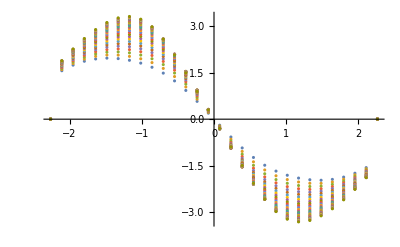

```mathematica
ListPlot[
Thread[{
h5Grid[[All, 1, 1]],
#
}]&/@h2vecs[[;;;;26]],
PlotRange->All
]
```

##### Attempt

```mathematica
h5Grid=$H5DVR["Grid", "Points"->{$H5NR, $H5NR}];
h2GridPoints=Flatten[H5H2Wfns["Grid"], 1];
```

Helper to extract the grid to be use to compute the dipole surface elements. Effectively just the surface parametrized in (a, s)

```mathematica
getComputeDipGrid[i_, j_]:=
With[{gp=h5Grid[[i, j]], dom=$H5DipoleSurfaceInterps[[1, 1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
With[{g=Map[Join[h5Grid[[i, j]], #]&, h2GridPoints]},
g
],
$Failed
]
]
```

```mathematica
computeDipVecs//Clear
computeDipVecs[i_,j_]:=
computeDipVecs[i,j]=
With[{gr=getComputeDipGrid[i, j]},
If[gr===$Failed,
ConstantArray[{0., 0., 0.}, Length@h2GridPoints],
$H5DipoleSurfaceVec@gr//Through//Transpose
]
]
```

This computes a term in the transition matrix defined by m_rμn_r for a given (a, s)

```mathematica
Clear[h2DipMomTerm]
h2DipMomTerm[i_, j_]:=
h2DipMomTerm[i, j]=
With[{dip=computeDipVecs[i, j]},
If[Norm[Flatten[dip]]>0,
$H2DVR[
"OperatorMatrix",
(dip&),
"Grid"->H5H2Wfns["Grid"],
"Wavefunctions"->H5H2Wfns["Wavefunctions"],
"WavefunctionSelection"->$H5nr
],
$Failed
]
]
```

Computing these for each (R_1, R_2):

```mathematica
h2DipMomArray=Array[h2DipMomTerm, {$H5NR, $H5NR}];
```

Then we slice up the coefficients:

```mathematica
wfnH2CoefficientVectors=
Partition[
Array[
With[
{
wfs=wfns[[2, All, 1+(#-1)$H5nr;;#*$H5nr]], ur=wfns[[2, 1, 1+14$H5nr;;15*$H5nr]]
},
Developer`ToPackedArray@
Map[
(*Sign[#.ur]**)#&,
wfs
]
]&,
($H5NR)^2
],
$H5NR
];
```

```mathematica
wfnH2CoefficientVectorsSymm=
Partition[
Array[
With[
{
wfs=wfnsSymm[[All, 1+(#-1)$H5nr;;#*$H5nr]],
 ur=wfnsSymm[[1, 1+($H5NR/2-1)$H5nr;;($H5NR/2)*$H5nr]]
},
Developer`ToPackedArray@
Map[
(*Sign[#.ur]**)#&,
wfs
]
]&,
($H5NR)^2
],
$H5NR
];
```

Then we compute the transition moment vector over the (s, a) coordinates

```mathematica
wfnTransitionMomentVector//Clear
wfnTransitionMomentVector[i_]:=
wfnTransitionMomentVector[i]=
With[
{
coeffs=
Flatten[wfnH2CoefficientVectors[[All, All, {i, 1}]], 1],
momsArr=
Flatten[h2DipMomArray, 1]
},
MapThread[
If[#2===$Failed,
0,
#[[1]].#2[[All,All, 1]].#[[2]]
]&,
{
coeffs,
momsArr
}
]
]
```

```mathematica
wfnTransitionMomentVectorSymm//Clear
wfnTransitionMomentVectorSymm[i_]:=
wfnTransitionMomentVectorSymm[i]=
With[
{
coeffs=
Flatten[wfnH2CoefficientVectorsSymm[[All, All, {i, 1}]], 1],
momsArr=
Flatten[h2DipMomArray, 1]
},
MapThread[
If[#2===$Failed,
0,
#[[1]].#2[[All,All, 1]].#[[2]]
]&,
{
coeffs,
momsArr
}
]
]
```

Check some phase stuff

```mathematica
Manipulate[
MapThread[Append, {Flatten[h5Grid, 1],wfnTransitionMomentVector[i]}]//ListPlot3D[#, PlotRange->{{-1.5, 1.5}, {1.2, 2}, All}, ColorFunction->"Rainbow", PerformanceGoal->"Quality"]&,
{i, 1, Length@wfns[[1]], 1, AnimationRate->.5}
]
```

```mathematica
Manipulate[
MapThread[Append, {Flatten[h5Grid, 1],wfnTransitionMomentVectorSymm[i]}]//ListPlot3D[#, PlotRange->{{-1.5, 1.5}, {1.2, 2}, All}, ColorFunction->"Rainbow", PerformanceGoal->"Quality"]&,
{i, 1, Length@wfns[[1]], 1, AnimationRate->.5}
]
```

Norm and square to get raw intensity:

```mathematica
intensities=Array[Total[wfnTransitionMomentVector[#]]^2&, Length@wfns[[1]]];
```

```mathematica
intensitiesSymm=Array[Total[wfnTransitionMomentVectorSymm[#]]^2&, Length@wfns[[1]]];
```

Misc

```mathematica
Clear[overlapTerm]
overlapTerm[i_, j_]:=
overlapTerm[i, j]=
$H2DVR[
"OperatorMatrix",
(#&),
"Grid"->H5H2Wfns["Grid"],
"Wavefunctions"->Hold@wfnH2SlicesIndexable[[i, j]],
"WavefunctionSelection"->$H5nr
]
```

##### Plots

```mathematica
specPoints=Thread[{Prepend[freqs, 0], intensities}];
```

```mathematica
Export["~/Documents/UW/Research/H5+/results/spectrum.mx", specPoints]
```

```mathematica
specPointsOld=;
```

```mathematica
Manipulate[
H5PlotSpec[Thread[{Prepend[freqs, 0], intensities}], shift],
{{shift, 1100}, 4400, -4400}
]
```

```mathematica
Manipulate[
H5PlotSpec[Thread[{Prepend[freqs, 0], intensitiesSymm}], Offset[shift, Scaled[scale]]],
{{shift, 0}, 4400, -4400},
{{scale, 1}, .5, 2}
]
```

```mathematica
H5PlotSpecBroadened[specPoints,25, 137]
```

### Larger Contracted

#### Parameters

```mathematica
$H5NRbig=60;
$H5nrbig=25;
($H5NRbig^2)*$H5nrbig
```

90000

#### T_R

```mathematica
H5TRbig=$H5DVR["KineticEnergy", "Points"->{$H5NRbig, $H5NRbig}];
```

#### h_r

H_2 wavefunctions are computed for the equilibrium value of (a, s)

```mathematica
H5H2Wfnsbig=
$H2DVR[
Return->{"Grid", "Wavefunctions"},
"Points"->{250, 250},
"PotentialOptimizationOptions"->
{
"PotentialFunction"->h2SinglePot,
"OptimizedBasisSize"->$H5nrbig
},
"NumberOfWavefunctions"->$H5nrbig
];
H5hrbig=SparseArray[Band[{1, 1}]->H5H2Wfnsbig[["Wavefunctions", 1, ;;$H5nrbig]]];
```

#### V

```mathematica
h5Gridbig=$H5DVR["Grid", "Points"->{$H5NRbig, $H5NRbig}];
```

```mathematica
potGridbig=Flatten[H5H2Wfnsbig["Grid"], 1];
gridPotbig=h2PotVec@potGridbig;
```

```mathematica
computePotVecbig//Clear
computePotVecbig[i_,j_]:=
computePotVecbig[i,j]=
With[{gp=h5Gridbig[[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
With[{g=Map[Flatten@{h5Gridbig[[i, j]], #}&, potGridbig]},
H5FullVecPot@g
],
ConstantArray[10^9, Length@potGridbig]
]-gridPotbig
]
```

```mathematica
Clear[h2PotElbig]
h2PotElbig[i_, j_]:=
h2PotElbig[i, j]=
With[{gp=h5Gridbig[[i, j]], dom=H5FullInterpPot[[1, 3;;4]]},
If[i==1&&j==1||
dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
$H2DVR["OperatorMatrix",
computePotVecbig[i, j]&,
"Grid"->H5H2Wfnsbig["Grid"],
"Wavefunctions"->Hold@H5H2Wfnsbig["Wavefunctions"],
"WavefunctionSelection"->$H5nrbig
],
h2PotElbig[1, 1]
]
]
```

```mathematica
H5VBlocksbig=
Flatten[Array[h2PotElbig, {$H5NRbig, $H5NRbig}], 1];
```

```mathematica
H5Vbig=SparseArray[Band[{1,1}]->H5VBlocksbig];
```

#### Full Mat

```mathematica
H5KPTermbig=
KroneckerProduct[H5TRbig,IdentityMatrix[$H5nrbig, SparseArray]]+
KroneckerProduct[IdentityMatrix[$H5NRbig^2, SparseArray], H5hrbig];
```

#### Energies and Wavefunctions

I just use one of the DVRs as a wrapper to access its eigenvalues/vectors routine

##### Wavefunctions

```mathematica
wfnsbig=
$H2DVR["Wavefunctions", 
"KineticEnergy"->Hold@H5KPTermbig,
"PotentialEnergy"->Hold@H5Vbig,
"NumberOfWavefunctions"->250,
"ArnoldiIterations"->10000
];//AbsoluteTiming
```

{4278.33,Null}

```mathematica
(*Export["~/Documents/UW/Research/H5+/wavefunctions_60_60_25.mx", wfnsbig]*)
```

~/Documents/UW/Research/H5+/wavefunctions_60_60_25.mx

```mathematica
wfnsbig=Import["~/Documents/UW/Research/H5+/wavefunctions_60_60_25.mx"];
```

##### Frequencies

```mathematica
freqsbig=
Rest[wfnsbig[[1]]]-wfnsbig[[1, 1]]
```

{445.37,770.178,1112.49,1354.31,1651.99,1734.29,1942.23,2089.64,2278.38,2439.4,2570.75,2663.74,2754.8,2782.63,2936.64,2967.,3121.58,3214.2,3349.82,3418.56,3423.01,3492.4,3536.58,3592.3,3728.27,3863.32,3869.59,3886.98,4034.88,4116.36,4148.58,4195.03,4204.91,4294.5,4327.92,4529.87,4535.51,4555.37,4605.93,4654.32,4741.92,4807.53,4810.81,4946.19,4975.13,5007.79,5076.91,5113.98,5135.72,5170.49,5191.04,5263.75,5300.17,5331.86,5374.99,5413.33,5415.52,5537.25,5543.2,5564.19,5573.49,5597.42,5701.83,5744.43,5755.78,5818.43,5853.34,5877.05,5913.14,5950.79,5977.11,6045.33,6048.43,6056.3,6113.3,6130.2,6164.77,6209.55,6225.91,6232.22,6237.81,6282.26,6288.08,6379.57,6392.53,6418.68,6464.58,6472.76,6573.64,6578.08,6587.48,6598.23,6623.95,6676.22,6696.85,6734.89,6765.22,6767.9,6791.32,6828.75,6831.,6839.5,6867.85,6884.69,6908.66,6973.98,6987.47,7021.09,7038.63,7054.31,7070.49,7097.64,7107.2,7175.66,7196.75,7273.79,7278.5,7301.07,7306.98,7347.1,7360.18,7360.59,7382.49,7465.98,7472.67,7501.58,7515.66,7540.81,7573.67,7592.45,7596.81,7612.16,7617.03,7617.33,7649.83,7754.88,7758.81,7766.12,7776.23,7788.66,7836.34,7858.19,7876.37,7907.32,7933.69,7939.93,7949.83,7976.97,7998.42,8015.51,8060.96,8065.3,8094.3,8097.79,8131.88,8150.86,8175.55,8182.6,8221.54,8233.43,8242.41,8255.58,8258.16,8283.98,8351.43,8358.51,8367.44,8400.06,8406.85,8428.91,8430.2,8464.45,8490.47,8504.84,8522.3,8552.62,8571.12,8576.55,8595.56,8613.16,8640.83,8646.81,8667.58,8670.4,8686.39,8701.95,8710.44,8738.93,8744.22,8760.72,8772.04,8797.32,8818.63,8835.88,8851.22,8865.55,8881.83,8895.35,8925.66,8950.55,8964.,8978.02,8985.65,8998.91,9020.72,9028.78,9043.02,9073.36,9090.95,9120.81,9131.98,9143.07,9152.03,9177.93,9197.32,9207.35,9210.42,9222.24,9241.66,9252.06,9267.62,9277.8,9286.01,9331.59,9341.86,9353.46,9378.8,9388.56,9389.57,9405.62,9434.84,9450.67,9463.1,9478.88,9492.2,9501.82,9529.23,9533.97,9542.73,9561.51,9582.63,9602.23,9605.31,9637.33,9651.63,9669.44,9692.86,9698.69,9722.27}

##### Slices

```mathematica
wfnSASlicesbig=
Array[ 
With[
{
wfs=wfnsbig[[2, All, #;;-1;;$H5nrbig]], 
ur=wfnsbig[[2, 1, 1;;-1;;$H5nrbig]]
},
{wfnsbig[[1]],Sign[ur.#]*Normalize[#]&/@wfs//Developer`ToPackedArray}
]&,
$H5nrbig
];
```

```mathematica
grSAWfnsbig=
Map[Flatten]/@
$H5DVR[
"GridWavefunctions",
"Points"->{$H5NRbig, $H5NRbig},
"Wavefunctions"->#
]&/@wfnSASlicesbig;
```

```mathematica
(*grSAWfnsbig[[6, 1]]//ListPointPlot3D[#, PlotRange->All, ColorFunction->"Rainbow", ViewPoint->Front]&*)
```

#### Spectrum

##### Attempt

```mathematica
h5Gridbig=$H5DVR["Grid", "Points"->{$H5NRbig, $H5NRbig}];
```

```mathematica
h2GridPointsbig=Flatten[H5H2Wfns["Grid"], 1];
```

Helper to extract the grid to be use to compute the dipole surface elements. Effectively just the surface parametrized in (a, s)

```mathematica
getComputeDipGridbig[i_, j_]:=
With[{gp=h5Gridbig[[i, j]], dom=$H5DipoleSurfaceInterps[[1, 1, 3;;4]]},
If[dom[[1, 1]]<=(1/Sqrt[2])*(gp[[2]]-gp[[1]])<=dom[[1, 2]]&&
dom[[2, 1]]<=(1/Sqrt[2])*(gp[[2]]+gp[[1]])<=dom[[2, 2]],
With[{g=Map[Join[h5Gridbig[[i, j]], #]&, h2GridPointsbig]},
g
],
$Failed
]
]
```

```mathematica
computeDipVecsbig//Clear
computeDipVecsbig[i_,j_]:=
computeDipVecsbig[i,j]=
With[{gr=getComputeDipGridbig[i, j]},
If[gr===$Failed,
ConstantArray[{0., 0., 0.}, Length@potGridbig],
$H5DipoleSurfaceVec@gr//Through//Transpose
]
]
```

This computes a term in the transition matrix defined by m_rμn_r for a given (a, s)

```mathematica
Clear[h2DipMomTermbig]
h2DipMomTermbig[i_, j_]:=
h2DipMomTermbig[i, j]=
With[{dip=computeDipVecsbig[i, j]},
If[Norm[Flatten[dip]]>0,
$H2DVR[
"OperatorMatrix",
(dip&),
"Grid"->H5H2Wfnsbig["Grid"],
"Wavefunctions"->H5H2Wfnsbig["Wavefunctions"],
"WavefunctionSelection"->$H5nrbig
],
$Failed
]
]
```

Computing these for each (R_1, R_2):

```mathematica
h2DipMomArraybig=Array[h2DipMomTermbig, {$H5NRbig, $H5NRbig}];
```

Then we slice up the coefficients:

```mathematica
wfnH2CoefficientVectorsbig=
Partition[
Array[
With[
{
wfs=wfnsbig[[2, All, 1+(#-1)$H5nrbig;;#*$H5nrbig]], ur=wfnsbig[[2, 1, 1+14$H5nrbig;;15*$H5nrbig]]
},
Developer`ToPackedArray@
Map[
(*Sign[#.ur]**)#&,
wfs
]
]&,
($H5NRbig)^2
],
$H5NRbig
];
```

Then we compute the transition moment vector over the (s, a) coordinates

```mathematica
wfnTransitionMomentVectorbig//Clear
wfnTransitionMomentVectorbig[i_]:=
wfnTransitionMomentVectorbig[i]=
With[
{
coeffs=
Flatten[wfnH2CoefficientVectorsbig[[All, All, {i, 1}]], 1],
momsArr=
Flatten[h2DipMomArraybig, 1]
},
MapThread[
If[#2===$Failed,
0,
#[[1]].#2[[All,All, 1]].#[[2]]
]&,
{
coeffs,
momsArr
}
]
]
```

Norm and square to get raw intensity:

```mathematica
intensitiesbig=Array[Total[wfnTransitionMomentVectorbig[#]]^2&, Length@wfnsbig[[1]]];
```

##### Plots

```mathematica
specPointsbig=Thread[{Prepend[freqsbig, 0], intensitiesbig}];
```

```mathematica
Export["~/Documents/UW/Research/H5+/results/spectrum_large_basis.mx", specPointsbig]
```

~/Documents/UW/Research/H5+/results/spectrum_large_basis.mx

```mathematica
Manipulate[
H5PlotSpec[specPointsbig, shift],
{{shift, 0}, 4400, -4400}
]
```

```mathematica
H5PlotSpecBroadened[specPoints,25, 137]
```

### Small 4D

Runs always in 5 and 5 for the PO part

```mathematica
smallH54DResults=<||>;
```

#### 20, 20

```mathematica
smallH54DResults["20x20"]=<||>;
```

##### Wavefunctions

```mathematica
smallH54DResults["20x20", "Wavefunctions"]=
$H54DDVR[
"Wavefunctions",
"Points"->{20, 20, 125, 125},
"PotentialOptimizationOptions"->Lookup[$H54DDVR["RuntimeOptions"], "PotentialOptimizationOptions"]/.
("OptimizedBasisSize"->_)->("OptimizedBasisSize"->5)
];
```

##### Energies

```mathematica
smallH54DResults["20x20", "Energies"]=
smallH54DResults["20x20", "Wavefunctions"][[1]]
```

{7186.24,7572.46,7773.39,7922.9,8542.03,8905.83,9115.11,9314.,9412.88,9494.86,9533.05,9575.28,9600.44,9771.71,9909.97,10068.1,10093.6,10151.3,10365.,10405.9,10470.8,10505.1,10534.9,10535.4,10627.1}

```mathematica
smallH54DResults["20x20", "Frequencies"]=
smallH54DResults[[Key@"20x20", "Energies"]]-
smallH54DResults[[Key@"20x20", "Energies", 1]]//Rest
```

{386.219,587.141,736.651,1355.78,1719.58,1928.87,2127.75,2226.63,2308.62,2346.8,2389.04,2414.2,2585.46,2723.72,2881.83,2907.33,2965.06,3178.79,3219.69,3284.55,3318.9,3348.68,3349.13,3440.88}

##### Grid

```mathematica
smallH54DResults["20x20", "Grid"]=
$H54DDVR[
"Grid",
"Points"->{20, 20, 125, 125},
"PotentialOptimizationOptions"->Lookup[$H54DDVR["RuntimeOptions"], "PotentialOptimizationOptions"]/.
("OptimizedBasisSize"->_)->("OptimizedBasisSize"->5)
];
```

```mathematica
smallH54DResults["20x20", "GridPoints"]=
ChemTools`DVR`Package`ChemDVRDefaultGridPointList@
smallH54DResults["20x20", "Grid"];
```

##### Grid Wavefunctions

```mathematica
smallH54DResults["20x20", "GridWavefunctions"]=
Map[
Flatten/@
Thread[{smallH54DResults["20x20", "GridPoints"], #}]&,
smallH54DResults["20x20", "Wavefunctions"][[2]]
];
```

##### Plots

```mathematica
smallH54DResults["20x20", "Plots"]=
ListPlot5D[
smallH54DResults["20x20", "GridWavefunctions"],
;;3
];
```

```mathematica
smallH54DResults["20x20", "Plots"][[All, 1]]//ListAnimate
```

#### 30, 30

```mathematica
smallH54DResults["30x30"]=<||>;
```

##### Wavefunctions

```mathematica
smallH54DResults["30x30", "Wavefunctions"]=
$H54DDVR[
"Wavefunctions",
"Points"->{30, 30, 125, 125},
"PotentialOptimizationOptions"->Lookup[$H54DDVR["RuntimeOptions"], "PotentialOptimizationOptions"]/.
("OptimizedBasisSize"->_)->("OptimizedBasisSize"->5),
"WavefunctionsOptions"->{Method->{"Arnoldi", "MaxIterations"->5000}}
];
```

##### Energies

```mathematica
smallH54DResults["30x30", "Energies"]=
smallH54DResults["30x30", "Wavefunctions"][[1]]
```

{7781.33,8299.05,8300.97,8740.82,9040.58,9420.93,9488.05,10073.1,10081.7,10082.2,10147.6,10226.6,10248.3,10367.2,10446.6,10471.9,10514.2,10554.3,10594.,10633.2,10641.7,10735.,10767.3,10918.5,10978.6}

```mathematica
smallH54DResults["30x30", "Frequencies"]=
smallH54DResults[[Key@"30x30", "Energies"]]-
smallH54DResults[[Key@"30x30", "Energies", 1]]//Rest
```

{517.717,519.642,959.493,1259.25,1639.6,1706.72,2291.76,2300.37,2300.84,2366.27,2445.3,2467.,2585.86,2665.31,2690.59,2732.87,2772.97,2812.63,2851.91,2860.39,2953.68,2985.96,3137.18,3197.25}

##### Grid

```mathematica
smallH54DResults["30x30", "Grid"]=
$H54DDVR[
"Grid",
"Points"->{30, 30, 125, 125},
"PotentialOptimizationOptions"->Lookup[$H54DDVR["RuntimeOptions"], "PotentialOptimizationOptions"]/.
("OptimizedBasisSize"->_)->("OptimizedBasisSize"->5)
];
```

```mathematica
smallH54DResults["30x30", "GridPoints"]=
ChemTools`DVR`Package`ChemDVRDefaultGridPointList@
smallH54DResults["30x30", "Grid"];
```

##### Grid Wavefunctions

```mathematica
smallH54DResults["30x30", "GridWavefunctions"]=
Map[
Flatten/@
Thread[{smallH54DResults["30x30", "GridPoints"], #}]&,
smallH54DResults["30x30", "Wavefunctions"][[2]]
];
```

##### Plots

```mathematica
smallH54DResults["30x30", "Plots"]=
ListPlot5D[
smallH54DResults["30x30", "GridWavefunctions"],
;;3,
InterpolationOrder->2
];
```

OptionValue::nodef: Unknown option InterpolationOrder for Plot3D.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

$Aborted

```mathematica
smallH54DResults["30x30", "Plots"][[All, 1]]
```

```mathematica
smallH54DResults["30x30", "Plots"][[All, 1]]
```

#### 45, 45

```mathematica
smallH54DResults["45x45"]=<||>;
```

##### Wavefunctions

```mathematica
smallH54DResults["45x45", "Wavefunctions"]=
$H54DDVR[
"Wavefunctions",
"Points"->{45, 45, 125, 125},
"PotentialOptimizationOptions"->Lookup[$H54DDVR["RuntimeOptions"], "PotentialOptimizationOptions"]/.
("OptimizedBasisSize"->_)->("OptimizedBasisSize"->5),
"WavefunctionsOptions"->{
Method->{"Arnoldi", "MaxIterations"->5000, ""}
}
];
```

##### Energies

```mathematica
smallH54DResults["45x45", "Energies"]=
smallH54DResults["45x45", "Wavefunctions"][[1]]
```

{9641.39,9651.01,9816.99,9932.37,9980.63,10051.7,10140.4,10267.,10271.6,10433.,10463.9,10522.7,10555.1,10692.2,10903.4,11028.7,11054.1,11113.2,11210.9,11255.6,11459.4,11484.3,11497.9,11714.4,11729.7}

```mathematica
smallH54DResults["45x45", "Frequencies"]=
smallH54DResults[[Key@"45x45", "Energies"]]-
smallH54DResults[[Key@"45x45", "Energies", 1]]//Rest
```

{9.61555,175.602,290.979,339.242,410.33,498.995,625.597,630.247,791.629,822.473,881.316,913.7,1050.77,1261.98,1387.33,1412.68,1471.81,1569.46,1614.17,1818.06,1842.92,1856.46,2072.99,2088.34}

##### Grid

```mathematica
smallH54DResults["45x45", "Grid"]=
$H54DDVR[
"Grid",
"Points"->{45, 45, 125, 125},
"PotentialOptimizationOptions"->Lookup[$H54DDVR["RuntimeOptions"], "PotentialOptimizationOptions"]/.
("OptimizedBasisSize"->_)->("OptimizedBasisSize"->5)
];
```

```mathematica
smallH54DResults["45x45", "GridPoints"]=
ChemTools`DVR`Package`ChemDVRDefaultGridPointList@
smallH54DResults["45x45", "Grid"];
```

##### Grid Wavefunctions

```mathematica
smallH54DResults["45x45", "GridWavefunctions"]=
Map[
Flatten/@
Thread[{smallH54DResults["45x45", "GridPoints"], #}]&,
smallH54DResults["45x45", "Wavefunctions"][[2]]
];
```

##### Plots

```mathematica
smallH54DResults["45x45", "Plots"]=
ListPlot5D[
smallH54DResults["45x45", "GridWavefunctions"],
;;3
];
```

```mathematica
smallH54DResults["45x45", "Plots"][[All, 1]]//ListAnimate
```

### Full 4D

#### Grid PE

```mathematica
h54DGPE=$H54DDVR["GridPotentialEnergy"];
```

```mathematica
GroupBy[
h54DGPE,
Function[#[[{3, 4}]]]->Function[#[[{1, 2, 5}]]]
][[1]]/.(10.^9->10^5)//ListPlot3D[#, ColorFunction->"M10DefaultDensityGradient"]&
```

```mathematica
h54DGrid=$H54DDVR["Grid"];
```

```mathematica
flatH5Grid=Flatten[h54DGrid, 3];
```

```mathematica
h5GroupedGrid=
GroupBy[
flatH5Grid,
Function[#[[{3, 4}]]]->Function[#[[;;2]]]
];
```

```mathematica
testGrid=
MapIndexed[
Flatten/@Thread[{#, ConstantArray[#2[[1, 1]],Length@#]}]&,
h5GroupedGrid[[;;1]]
][[1]];
```

#### PO

```mathematica
optHam=$H54DDVR["Hamiltonian"];//AbsoluteTiming
```

{47.6885,Null}

```mathematica
Export["~/Desktop/test.mtx", optHam]
```

~/Desktop/test.mtx

```mathematica
optHam["Density"]*Length[optHam]^2
```

1.76175×10^7

```mathematica
fullWfns2=
$H54DDVR[
"Wavefunctions", 
"NumberOfWavefunctions"->6, 
Method->{"Arnoldi", "BasisSize"->25}
];//AbsoluteTiming
```

$Aborted

```mathematica
fullWfns2[[1]]-fullWfns2[[1, 1]]
```

{0.,335.716,392.103,784.168,1195.7,1229.01}

```mathematica
fullGRWFS2=
$H54DDVR["GridWavefunctions", "Wavefunctions"->fullWfns2];
```

```mathematica
flattendGridWfns=
Map[Flatten]/@fullGRWFS2;
```

```mathematica
groupedWfns=
GroupBy[flattendGridWfns[[1]],Function[#[[{3, 4}]]]->Function[#[[{1, 2, 5}]]]];
```

```mathematica
groupedWfnsR1=
GroupBy[
Normal@groupedWfns,
Function[#[[1, 1]]]->Function[#],
Association
];
```

```mathematica
potMinMaxes=
MapIndexed[
MinMax@
DeleteCases[
H5FullVecPot[
Flatten/@Thread[{#[[All, ;;2]], ConstantArray[#2[[1, 1]],Length@#]}]
],
10.^9
]&,
KeySort[groupedWfns]
];
```

```mathematica
wfnCutPlots=
KeyValueMap[
ListPlot3D[
#2,
PlotLabel->TemplateApply["r1: `` r2: ``", #],
PlotRange->All,
ColorFunction->
With[
{
minmax=potMinMaxes[#], 
cf=ColorData["M10DefaultDensityGradient"],
r1r2=Sequence@@#
},
cf@
Rescale[
H5FullPot[{#, #2, r1r2}],
minmax,
{0,1}
]&
],
ColorFunctionScaling->False
]&,
KeySort[groupedWfns]
];
```

```mathematica
wfnCutPlots//ListAnimate
```

#### Imported

```mathematica
wfnsImpRaw=
Re@Import["~/Documents/UW/Research/H5+/out.mtx"];
```

```mathematica
wfnsImpRaw[[1]]
```

{20169.4,20603.3,20819.7,20880.7,21071.3,21300.7,21482.4,21480.1,21746.9,21958.,21989.6,22021.6,22291.1,22363.5,22346.9,22719.9,22731.7,22839.5,22865.9,22973.1,23011.9,22992.1,23126.4,23239.9,23332.4}

```mathematica
Rest[wfnsImpRaw[[1]]-wfnsImpRaw[[1, 1]]]
```

{433.889,650.311,711.28,901.848,1131.29,1312.98,1310.7,1577.46,1788.52,1820.19,1852.2,2121.64,2194.08,2177.51,2550.47,2562.3,2670.06,2696.5,2803.7,2842.46,2822.64,2957.,3070.46,3162.93}

```mathematica
wfnsImpRaw//Dimensions
```

{562501,25}

```mathematica
wfnsImpRaw//Dimensions
```

{562501,25}

```mathematica
wfnsImp=
With[{lambdas=wfnsImpRaw[[1]], vees=Reverse/@Transpose@Rest@wfnsImpRaw},
{(*Sort@*)lambdas, vees(*[[Ordering[lambdas]]]*)}
];
```

```mathematica
wfnPosBlocks=
Position[UnitStep[wfnsImp[[2, 1]]-10^-4], 1]//Flatten//Split[#, #2-#==1&]&;
```

```mathematica
wfnsImp[[2, 1]]//Max
```

0.549622

```mathematica
wfnPosBlocks//Length
```

124

```mathematica
h54DGridFlat=Flatten[$H54DGrid, 3];
h54DGridFlat[[1]]
```

```mathematica
h54DGridFlat[[wfnPosBlocks[[9]]]]
```

{191351,191352,191353,191354,191355,191356,191357,191358}

```mathematica
wfnsImp[[2, 1, wfnPosBlocks[[3]]]]
```

{0.000126834,0.000256537,0.000284247,0.00017953}

```mathematica
Count[UnitStep[wfnsImp[[2, 1]]-10^-8], 1]
```

23852

```mathematica
grWfns4D=
Map[Flatten]/@
$H54DDVR[
"GridWavefunctions",
"Grid"->$H54DGrid,
"Wavefunctions"->wfnsImp[[All, ;;1]]
];
```

```mathematica
groupedWfn1=
GroupBy[grWfns4D[[1]], Function@#[[{3, 4}]]->Function@#[[{1, 2, 5}]]];
```

```mathematica
groupedWfnH21=
GroupBy[grWfns4D[[1]], Function@#[[{1, 2}]]->Function@#[[{3, 4, 5}]]];
```

```mathematica
groupedWfnH2A1=
GroupBy[grWfns4D[[1]], Function@#[[{1, 3}]]->Function@#[[{2, 4, 5}]]];
```

```mathematica
groupedWfnH2S1=
GroupBy[grWfns4D[[1]], Function@#[[{2, 3}]]->Function@#[[{1, 4, 5}]]];
```

```mathematica
Select[KeySort[groupedWfn1][[45, All, 3]], #>10^-9&]//Length
```

52

```mathematica
KeySort[groupedWfnH2S1][[7]]//DeleteDuplicatesBy[#[[;;2]]&]//Length
```

750

```mathematica
Position[KeySort[groupedWfnH2S1], 0.5496222580235507]
```

{}

```mathematica
Values[KeySort[groupedWfnH2A1][[{3}]]]//MinMax
```

{-5.6865×10^-11,4.96488}

```mathematica
KeySort[groupedWfnH2A1][[3, All, 3]]
```

```mathematica
Pick[#, UnitStep[Abs[#[[All, 3]]]-10^-10], 1]&/@Values[KeySort[groupedWfnH2A1][[{3}]]]
```

{{}}

```mathematica
KeySort[groupedWfnH21][[All, All ,3]]//MinMax
```

{-0.0850819,0.549622}

```mathematica
Abs[#[[All, 3]]]&/@Values[KeySort[groupedWfnH2A1][[3, All 3]]]
```

```mathematica
Pick[#, UnitStep[#[[All, 3]]-10^-11], 1]&/@Values[KeySort[groupedWfnH21][[{3}]]]
```

{{{0.606391,0.363986,1.28557×10^-11},{0.606391,0.404011,2.82682×10^-11},{0.606391,0.443534,3.39724×10^-11},{0.606391,0.483096,2.32142×10^-11}}}

```mathematica
groupedWfn1[[1, All, {1, 2}]]//CoordinateBounds
```

{{-2.12132,2.12132},{0.722239,4.96488}}

```mathematica
groupedWfn1//Length
```

625

```mathematica
625/2//Floor
```

312

```mathematica
H5OptDistances
```

{d1→0.795831,d2→0.795831,x5D→10.,R1→1.51072,R2→1.51072}

```mathematica
Nearest[Keys[groupedWfn1]->"Index", {"d1", "d2"}/.H5OptDistances]
```

{313}

```mathematica
groupedWfn1//Keys
```

```mathematica
H5E
```

```mathematica
ListPlot3D[groupedWfn1[[313]], 
PlotRange->All, ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
ListPointPlot3D[
With[{wfn=Transpose@ReplacePart[Transpose[#], 3->#[[All, 3]]^2]},Pick[wfn, UnitStep[Abs[#[[All, 3]]]-5*10^-6], 1]
]&/@Values[KeySort[groupedWfn1][[{313}]]], PlotRange->
{
{-2.1213203435596424,2.1213203435596424},{0.7222388663039396,4.964879553423224}, 
All
}, ColorFunction->"Rainbow"
]
```

```mathematica
ListPointPlot3D[
With[{wfn=Transpose@ReplacePart[Transpose[#], 3->#[[All, 3]]^2]},Pick[wfn, UnitStep[Abs[#[[All, 3]]]-5*10^-6], 1]
]&/@Values[KeySort[groupedWfn1][[{313}]]], PlotRange->
{
{-2.1213203435596424,2.1213203435596424},{0.7222388663039396,4.964879553423224}, 
All
}, ColorFunction->"Rainbow"
]
```

-Graphics3D-

```mathematica
groupedWfnH21[[1, All, {1, 2}]]//CoordinateBounds
```

{{0.278893,1.92123},{0.278893,1.92123}}

```mathematica
$H54DDVR[
"Wavefunctions"->Hold[wfnsImp],
"WavefunctionSelection"->1
]
```

```mathematica
H54DPlot[
"Wavefunctions"->Hold[wfnsImp]
]
```

#### Separate parts

```mathematica
$coarseGridSize=20;
coarseSP=
$H5DVR["Wavefunctions", "Points"->$coarseGridSize*{1, 1}, "NumberOfWavefunctions"->10];
Rest[#]-First[#]&@coarseSP[[1]]
```

{411.149,1052.17,1204.16,1258.89,1650.11,1990.79,2004.22,2548.82,2558.87}

```mathematica
fineSP=$H5DVR["Wavefunctions", "Points"->{30, 30}, "NumberOfWavefunctions"->10];
```

```mathematica
Rest[#]-First[#]&@fineSP[[1]]
```

{520.322,850.812,1239.77,1388.46,1811.13,1832.47,2099.63,2287.22,2430.3}

```mathematica
coarseH2=
$H2DVR["Wavefunctions", 
"Points"->{125, 125}, 
"PotentialOptimizationOptions"->{
"PotentialFunction"->h2SinglePot,
"OptimizedBasisSize"->6
},
"NumberOfWavefunctions"->10
];
Rest[#]-First[#]&@coarseH2[[1]]
```

{3494.03,3612.75,6927.51,7001.67,7184.91,10228.3,10249.1,10490.3,10701.6}

#### New Grid

```mathematica
fullWfns3=$H54DDVR["Wavefunctions", "NumberOfWavefunctions"->10];
```

```mathematica
fullWfns3//Iconize
```

```mathematica
Rest[#]-First[#]&@fullWfns3[[1]]
```

{467.047,528.871,531.024,572.055,824.416}

```mathematica
fullGRWFS3=
$H54DDVR["GridWavefunctions", "Wavefunctions"->fullWfns3];
```

```mathematica
fullGRWFS3//Iconize
```

## Write Up